### Note to the Instructor/Grader- This code can be executed for the large data sets, but it might take really long time when we are pre processing the data takes around 1 hr to pre process 100000 documents and around 10-15 minutes to pre process 20000 documents. For the illustrative purpose I am just running the code by extracting only 2000 documents which will be executed within 5 minute[ Professor has mentioned in the class that we can take only certain set of data and it is up to us to decide the size of the training and test data set ]. I have tried to incorporate comments as needed so that anyone executing this code can really understand what is happening in the background . This notebook contains 5 algorithms- Random Forest, Neural Network,Markov,Logistic Regression and Support Vector Machine. I have chosen “Support Vector Machine” as my third algorithm apart from first two which are Random Forest (Decision Tree) and Neural Network. But I am computing Markov and Logistic Regression for comparing the accuracy and precision. Code is divided into cells, please make sure you run each cell in sequential order.

### 1. Importing Data - For the illustrative purpose I am just extracting a small set of data though this code runs for large data sets.

```mathematica
raw=OpenRead["reviews.csv"]
reviews=Map[StringSplit[#,"|"]&,ReadList[raw,String,2000]]
```

InputStream[…]

{{label,text},1998,{positive,Great Children's Story: The Precious Moments Stories are great.We like to keep them in our home to share with childrenthat come to visit ~ we enjoy watching them over and over again as well.}}
 |  |  |  |

### 2. Preprocessing of data- Data extracted is processed. Each document is processed in following way- a) Special Characters are removed. b) Diacritics are converted. c) Stop words are deleted. c) Each document is converted to lower case. Every fifth document is categorised as “test data set” and others are considered as “training data set” Each document in turn is classified as “Positive” and “Negative” based on the label from the input document for the respective document.

```mathematica
(* creating empty lists which will be used to store the sorted data in later part of the code *)
positiveReviews={}
negativeReviews={}
trainingSet={}
testPositiveSet={}
testNegativeSet={}
testSet={}
testAccuracyTest1={}
testAccuracyTest2={}
testAccuracyTest3={}
testAccuracyTest4={}

accuracyTestSet={}

(* Parsing input file, adding every 5th document as a test document and remaining documents are considered as training documents and are classified as positive or negative based on the label in the input file *)
For[i=2,i≤Length[reviews],i++,
temporarySet=reviews⟦i,2⟧;
(* Replacing the special characters with empty character as these special characters do not add any meaning to the sentence *)temporarySet=StringReplace[temporarySet,{",",".","?",":","!","-","|","(",")","\"","{","}",";","$","!","@","#","%","^","&","*","[","]",DigitCharacter}->" "];
(* After removal of special characters-> we're removing the diacritics and stop words, and later converting them to the lower case *)
temporarySet=ToLowerCase[DeleteStopwords[RemoveDiacritics[temporarySet]]] 
(* classifying the document based on the document index and its label *)If[Mod[i,5]==0,If[reviews⟦i,1⟧=="positive",AppendTo[accuracyTestSet,{"Positive",temporarySet}];AppendTo[testPositiveSet,temporarySet],AppendTo[accuracyTestSet,{"Negative",temporarySet}];AppendTo[testNegativeSet,temporarySet]],If[reviews⟦i,1⟧=="positive",AppendTo[positiveReviews,temporarySet],AppendTo[negativeReviews,temporarySet]]]]

tempTestPositiveSet={}
tempTestNegativeSet={}
tempTestSet={}
finalTempTestSet={}
lower1=0
lower2=0
lower3=0
lower4=0
totalTestSetLength=Length[accuracyTestSet]
packetSize=Quotient[totalTestSetLength,4]
For[i=1,i≤ 4,i++,
lower= (i-1)*packetSize+1;
upper=i*packetSize;
tempTestSet=accuracyTestSet[[lower;;upper]];
lenTempTestSet=Length[tempTestSet];
tempTestPositiveSet={};
tempTestNegativeSet={};
For[j=1,j≤ Length[tempTestSet],j++,
If[tempTestSet[[j,1]]=="Positive",AppendTo[tempTestPositiveSet,tempTestSet[[j,2]]],AppendTo[tempTestNegativeSet,tempTestSet[[j,2]]]

];

];

finalTempTestSet=Association["Positive"-> Flatten[tempTestPositiveSet],"Negative"-> Flatten[tempTestNegativeSet]];
Switch[i,1,lower1=lower;testAccuracyTest1=Association["Positive"-> Flatten[tempTestPositiveSet],"Negative"-> Flatten[tempTestNegativeSet]],2,lower2=lower;testAccuracyTest2=Association["Positive"-> Flatten[tempTestPositiveSet],"Negative"-> Flatten[tempTestNegativeSet]],3,lower3=lower;testAccuracyTest3=Association["Positive"-> Flatten[tempTestPositiveSet],"Negative"-> Flatten[tempTestNegativeSet]],4,lower4=lower;testAccuracyTest4=Association["Positive"-> Flatten[tempTestPositiveSet],"Negative"-> Flatten[tempTestNegativeSet]]]

]
```

{}

{}

{}

«12 more identical outputs»

0

0

0

«1 more identical outputs»

400

100

### 3. Flattening - All the lists that we created to classify test and training data as “Positive” and “Negative” are now “flatten”ed.

```mathematica
(* "Flatten"ing all the lists *)
(* positiveReviews=Flatten[positiveReviews]
negativeReviews=Flatten[negativeReviews]
testPositiveSet=Flatten[testPositiveSet]
testNegativeSet=Flatten[testNegativeSet] *)
(* Joining the both positiveReviews and negativeReviews Set *)
allTrainingReviews=Join[positiveReviews,negativeReviews]
(* Applying "FeatureExtraction" to the entire data set, so that it will pick up only those words which serve as "Features" and helps in understanding the sentiment of the document *)
```

{Great CD  My lovely Pat has one of the GREAT voices of her generation  I have listened to this CD for YEARS and I still LOVE IT  When I'm in a good mood it makes me feel better  A bad mood just evaporates like sugar in the rain  This CD just oozes LIFE  Vocals are jusat STUUNNING and lyrics just kill  One of life's hidden gems  This is a desert isle CD in my book  Why she never made it big is just beyond me  Everytime I play this  no matter black  white  young  old  male  female EVERYBODY says one thing  Who was that singing   ,One of the best game music soundtracks   for a game I didn't really play  Despite the fact that I have only played a small portion of the game  the music I heard  plus the connection to Chrono Trigger which was great as well  led me to purchase the soundtrack  and it remains one of my favorite albums  There is an incredible mix of fun  epic  and emotional songs  Those sad and beautiful tracks I especially like  as there's not too many of those kinds of songs in my other video game soundtracks  I must admit that one of the songs  Life A Distant Promise  has brought tears to my eyes on many occasions My one complaint about this soundtrack is that they use guitar fretting effects in many of the songs  which I find distracting  But even if those weren't included I would still consider the collection worth it ,Great for the non audiophile  Reviewed quite a bit of the combo players and was hesitant due to unfavorable reviews and size of machines  I am weaning off my VHS collection  but don't want to replace them with DVD's  This unit is well built  easy to setup and resolution and special effects  no progressive scan for HDTV owners  suitable for many people looking for a versatile product Cons  No universal remote ,Great book for travelling Europe  I currently live in Europe  and this is the book I recommend for my visitors  It covers many countries  colour pictures  and is a nice starter for before you go  and once you are there ,Simple  Durable  Fun game for all ages  This is an AWESOME game  Almost everyone know tic tac toe so it is EASY to learn and quick to play  You can't play just once  The twist is that your pieces are slightly different sizes   just big enough to gobble up your opponent  The first person to make tic tac toe wins  but it's not as easy as it looks when you're stuck in the mindset of just making three in a row and forget about the gobbling possibilities  My   and   year olds will beat me even when I'm trying to win  Excellent beginning critical thinking game  Grandparents loved playing it with the kids too ,Review of Kelly Club for Toddlers  For the price of       this PC game is WELL worth it  great graphics  colorful and lots to do  My four year old daughter is in love with the many tasks to complete in this game  including dressing and grooming wide variety of pets and decoration of numerous floats to show in your little one's very own parade ,Some of the best fiddle playing I have heard in a long time  This is an excellent album with some great fiddle playing  Ryan is amazing to watch when he plays in person  You can feel the emotion he puts into each song ,one of the last in the series to collect    The magazine was in very good condition and had the usual high standard of articles and photos that Victoria magazine has come to represent  I have collected all the previous magazines of the series and still enjoy leafing through them on a rainy day,works great  i bought this item to connect to a strobe light  unit functions well  not sure that it has all the range claimed  but i never really believe everything a manufacturer claims about a product like this  just too many variables  I can say it works from my neighbors house into my garage  at least   ' going thru two buildings  now if i make too much noise later at night he can simply press a button to let me know ,This is the all time best book   This is the all time best book  She mentoins in the book how anyone can be a vampire  who knows  Well anyway I like the idea of having one soulmate and one crazed werewolf crush  P S I think that it is a good twist on the story about how anone can be part of the night world ,Mary Ash  Can't believe I have never reviewed this book before  First read this back when I was     Like a lot of girls wanting the mysterious boyfriend and believed in soul mates which drug me into these books  Rereading it over time years later still stands the test of time for me  Ash is that bad boy you want and your parents want you to stay away from even though he seems like a jerk there is just something about him that make you wanna root for him ,Tha BOMB of a book    L J  Smith is the best author in the whole world  I read this book a year ago but I can't stop reading it  It is beyond sweet  I love Ash The entire Night World seris is the bomb  I read mostly everyone of L J Smiths book and they all are awesome  I think Ash and Mary Lynetee are one of the sweetest soulmates  I loved how they tried to fight there feelings but couldn't  There should be real guys like Ash Quinn Juliun Damon Gabriel and I can go on forever  I think everyone should read at least one L J Smith book  If you do you'll be hooked on them for life like I am  L J Smith is the BEST    ,They'd watch it nonstop if I'd let them  apart from it arriving broken the first time  my kids are loving this DVD  which I alternate with the other I purchased to keep my own sanity  This DVD has created a Thomas fan out of my    /  yr  old daughter as well ,Wonderful  I went online for information about Dockers Khaki pants  The size my husband wears are very hard to find in stores  I was very impressed with the selection I had and he was thrilled to have all these pants without having them taken up in the length  The delivery was quick  especially during Christmas  and I really appreciate all the effort made to send us the selections we chose ,WeiB FOREVER   This is a great CD   I love WeiB Kreuz   The anime is awsome  Its bout   guys  hhhooottt  who work at a flower shop  but at night they are the White Hunters  or Byce as in the anime  they are assasins that  hunt the tomorrow  of Bad guys  the bad guys the police cant get   Like when teens start blowing up in flames in public for no reason    from a strange gas substance that w/ instant contact ingulfs any object    but i couldnt resist  Its also an emotional anime at times  I think this is a Cd and Anime any anime fan should see   ,Real HTML for people who build sites for a living  This book is simply great  If you build sites for a living you probably struggle with books that trivialize HTML and present its syntax willy nilly  This book is the ONLY book I've ever seen that actually seems to be written by someone who builds sites professionally and wants to know all the markup  It explains logical and physical tagging styles well and does a really good job showing how to hook HTML with other technologies without trying to teach CGI  CSS  etc  at the same time  The only thing I wish is that this guy would write a JavaScript or DHTML book  I'd buy that right away ,Amazing     love it   very touch it's to bad that in the dvd description doesn't mention no subtitles,Leslie in a nutshell  Danelectro DJ   C Rocky Road Spin Speaker Mini Effects Pedal  is an amazing little pedal I use it with guitar  and keyboards Using with Keyboards  organ mode doesn't matter which type  jazz  rock  gives me an instant controllable Leslie effects it includes fast and slow ramp up boost  volume/drive  thru a mixer in stereo you can do some amazing stuff with this inexpensive unit The only drawback i have found is the buttons are very hard to engage and disengage But i'm working on that  i will modify the springs if possible and maybe even send a recommendation to Danelectro ,Patricia Cornwell has turned me into a reader  I was never really a big reader before and somebody put me on to Patricia Cornwell  Well  now I can't put her books down  Her books just get better and better as you go through the Kay Scarpetta series I really enjoy the series concept and the fact that some of the same characters keep returning from book to book  It's nice to see the characters develop through each story line  It allows you to get comfortable with them  get close to them  and get frustrated with them when they do something out of character I highly recommend reading not just this book but the entire Kay Scarpetta series ,Best of the First Four in this series   This is an awesome book  Kay just keeps getting better and better  It's also fun to see the characters develop more with each book   Kay herself as she seems to be always  one against the world   Marino who it appears is heading towards some sort of heart attack  Lucy who seems to be getting more and more quixotic  In this book Kay finds herself smack in the middle of a series of gruesome killings  It appears that a recently executed murderer  who Kay herself has seen on her autopsy table  is still around committing crimes  A number of murders occur where the executed murderer's fingerprints are turning up  Kay  Marino and Benton try to track a killer  but it appears that the corruption goes up a long ways into the political stratosphere  This is a taut and totally believable thriller  I can't wait until the next one because the book ended with the way wide open to the next installment ,Great Beginning   poor ending  Parricia Corwell  Cruel   Unusual was breathtaking in the beginning  Her relation to her family  her dedication to her work exeptional  However  this story began to get boring towards the end   the ending  not too great ,Wonderful  baffling mix  This has just about everything  The rabbi  of course  is learned and devout  even if his schooling causes some nervousness  The cat becomes fantastical when some mystery grants him human speech  The visit abroad captures all the distrust of the alien that the most insular of small towners can summon  And  around all of that  the monotonous drama of life unfolds  loves  losses  and changes that no one knows how to ride out Comics have moved well past the BamPow genre into many other idioms   this might border on chick lit  but much less than some  If reality and fantasy remain negotiable for you  with deep family devotions and deeper  or shallower  personal ones  the ragged lines of this comic might touch you    wiredweird,No another grill like this     This grill is one of its kind   It can be use anywhere without so much hard work  it fits snugly anywhere    ,From Potter's Field by Patricia Cornwell   This was a very good book with excellent descriptions  It's a real page turner and keeps you wondering what's going to happen next  The best parts are at the very beggining and the end ,great book  i loved it  they mentioned a movie  where is it   the publisher said soon to be a movie  does anyone know if a movie was ever created ,Simply Awesome   This was only my first Cornwell novel and I'm hooked  In the past few months I have managed to collect all of her books and I can't wait to dive into them  This summer will be a suspensful one for Scarpetta and I ,Black Knight C C Heat Squash Racquet  Great racquet  But I'm a power hitter I have no power Generating Difficulty With This racquet  My style is to try to volleyball and everything I've found this racquet to well balanced and maneuvered  I like the factory grip although with distinct ridges Others prefer a smooth grip May   give the factory grip on chance and you May Come to like it  The  sale  prices are right for a high About end racquet  racquets and Black Knight in Have a reputation for overall durability so you Should get plenty of use Before replacement  Note  I got my first C C as a D level player and did not like it Immediately  Howeve  as my game improved version I switched from my Bandit Black Knight C C White racquet to the great success and Have HAD  So  It Might not be the right racquet for a beginner  intermediate to advanced players But Will Benefit From this fine racquet ,sergeant frosts lonely hearts club band  edith has created a venue for herself to exorcise melancholic memories with painful melodies  there are no disguises on this collection  lonesome guitars and medicinal piano radiate the mood of broken spirits  she writes all her own songs  these ballads are definite reminders of those unbearable moments we all have to live  they are all gray sky  secluded isolating tunes  i envision a ironical pace  i thought she was from chicago  millions and millions of people  and she sings stark loneliness,Great Camera  I recently purchased this camera and I'm very satisfied with it  I find the quality of the pictures with this camera as good if not better than anything else without going to digital  It is very comfortable to hold and the controls are easy to use  I highly reccomend this product to anyone looking for a top quality camera at an affordable price  Nice going Sony ,The amazing squeem  I love love love the squeem    The before and after pictures are definitely real    You can immediately tell the difference when you put it on it definitely improves your posture  you eat much less since it squeezes the he'll outta you but its not an uncomfortable squeeze ,Great Product  A friend recommended this product to flatten the tummy for great look in a dress  I brought a medium according to the measurement guide lines but I needed a small  It was extremely difficult to put on so I needed assistance  Once it was on I was still able to contract my core  which meant that I needed a smaller size  I believe it is because my waist sits high on my torso  Other then that this is great buy ,I recommend ordering a size or   larger than your regular size   I ordered the Squeem waist shaper in a size small   my general size is      I'm  '  and weigh    lbs right now  over the winter I ate too much cheese and gained about   lbs which isn't much to complain about but I have a roll of belly fat that shows through a slinky dress  I just wanted to smooth out my middle and fat above my hips   I wish I'd ordered a medium  or even large  instead because as I was hooking the waist shaper from top to bottom as instructed it was way way way too tight by the time I tried to hook the lower    above my hips  I don't want to be uncomfortable I just want a smooth finish  So  if you're similar in size I recommend ordering a medium instead  In general the quality of the product is exceptionally well stitched and built to last ,Does the job  I have been looking for something to hold in my stomach that wasn't elastic based  Found this item and have to say I am pretty pleased  The hooks do take a while  but once they are all done  the waist cincher does what it says it will do  The only negative thing is what a lot of the other reviews complain about  It does tend to cause back fat to appear more prominent by your underarms  So I can't wear this with a top that is clingy  Can only wear with looser fitting shirts  Oh well  nothing is perfect ,Good matt nude lipstick  It's got a nice warm scent of vanilla like smell  Texture is creamy  Meadow Sweet is a nice nude color  Can't apply too much or else it'll look a bit dry ,I would sell it    book complete with dust cover  Excellent  West is only fairly judged by the breadth of his work  He has a special view of human nature and all its weaknesses ,A welcomed change from the frozen plains of Europe  A refreshing  sunwarmed  beautifull change from the frozen steeps and plains of Ice Age Europe  A delightful story of a woman who must face and overcome immense odds to survive  The plot line moves in different ways from other  Woman against the odds  novels so it is a fresh and not predictable  A very good read and a much better choice over Jean Auel's  Shelters of Stone  ,The Scarlet Letter  I really enjoyed this book  It shows the judgmental tendencies in our human race and how one woman strove to live a life of service to others to gain redemption for her mistake  Can't go wrong with the classics ,Great novel  The Scarlet Letter by Nathaniel Hawthorne is a great novel  It takes place in Boston  Massachusetts during the era when Puritans were there  The main character Hester Prynne is forced to wear a Scarlet Letter A for adultery because she cheats on her husband while waiting for him to come from Europe The book really recaptures what Puritanism was like  Its interesting to think about what America would be like if we were still Puritan  A theme of the book is concealed guilt  The minister Arthur Dimmesdale has concealed guilt which causes him severe pain  The message of the book is that you shouldn't let some minor sin you did in the past haunt you for the rest of your life The book denounces the religious atmosphere of the Puritan village claiming that it stifled the merriment and joy of the culture of Old England  You get a picture of how the wonderful culture portrayed in the works of Chaucer was lost in America due to the influence of the Puritans ,The  Scarlet  Letter  Much to my amazement  this book has been placed on banned lists in several states  It's an excellent study of the devastation caused by guilt  Although the story does allude frequently to adultery  there are no graphic details that would make it unsuitable for use in a high school classroom  Both the illnesses caused by guilt and the good health of those who overcome it are made clear ,The Scarlet Letter a must read for any American  The best book that I have ever been assigned to read for school by far  The way in which Hawthorne captures the shame that Hetser   the wearer of the scarlet letter  feels everyday and the utter torment that the weak Dimmesdale is in by not coming forth and saying he slept with Hester and the revenge ridden character of Chillingworth is spectactular The way in which Hawthorne describes the setting and the actions that characters do is truly outstanding  Hawthorne has a huge flare for the dramatic which is great for the reader  Since Hester the main character concieved her daughter Pearl through an affair she has been snetenced to wear the scarlet A on her chest for the rest of her life  The story starts on the day Hester is to stand infront of the town and wear her badge of shame and all the drama in the small puritanical town of Boston starts from there  A must read for any American ,This book is Great   One might notice that many of the negative reviews of this book contain horrible grammer and multiple spelling errors  Although I respect those who disliked The Scarlet Letter  I disagree  It's no wonder that people that don't know how to capitalize the word 'I'  I thought that this book was wonderful  if you are willing to put effort into understanding it ,Possibly the funniest movie ever made   It starts off a bit slow  but once the product placement jokes start it takes off ,Sassy Baby Warming Dish  Interesting concept   We tried the Baby warming dish  We found that for our   year old it was pretty small  and didn't really hold enough water to keep her warm I think it would work ok for an infant  although I think a blanket would work just as well Recommendation Buy                    HoldSell,Fantastic  A movie that makes you feel a lot better about the holidays  Although not a childish movie  Eight Crazy Nights is a fantastic Sandler movie ,It Rises above the  Fluff  Books  The first thing that struck me was that it was easy to read  The print was readable and the illustrations were helpful  I did also find some grammatical errors as an earlier review said  But mostly it was very specific and practical  The chapters most helpful were on  emotional states  and music  It's hard to find a book on this subject that's across the board  dealing with many different issues and this one addresses nearly every brain related research issue from nutrition to memory  As a scientist who also works with high school students  I found his translation of brain research into the classroom to be thoughtful  if not enthusiastic  It's a tough subject to translate  but I did get more than I thought I would out of the book  Mostly it helped me get past the hype and get into the real practical meat of the material  The book's far from perfect  but it's the best I've seen so far on this topic ,Itten The Elements of Color  I was so very pleased to review the art book which arrived in pristine condition  I would have rated it in Excellent condition  rather than very good  I would like to thank the person who made it possible  but have misplaced her name and address ,I wish        i had never heard Fair to Midland before hearing this music but cant help making comparisons  It is still wonderful music and Ill explore it further   ,Good follow up to El Cielo   A bit of a change this time for Dredg  less progressive material  more straight ahead rock tunes  I was a little disappointed in it  It doesn't have alot of stuff going on like with El Cielo which is pretty big compared to Catch Without Arms  But still this is the direction they chose to go in and it's definitely a very good one ,  s Hard Rock  One of the   s rock bands that capture my ears    It's pity that they are almost retiring soon   ,Good Quality Cell Phone Holder  Contrary to other review  I found my cell phone holder to be of very good quality and have used it for a long time now with no problems whatsoever ,Loved it   I LOVE Christmas movies and these are some of my favorites  I always bring them out when I am decorating and start enjoying the holidays ,Charlie Brown Christmas was a Great Christmas Gift   I gave this movie to a co worker who loves all the Charlie Brown classics that are shown on TV  She was thrilled when she opened it ,There is no way anyone with a soul could ever give this a negative review      This is one of the sweetest  sad  funny  and actually profound Christmas specials ever  Well  maybe not Dostoyevsky deepness  but there is quite a lot of depth here  unlike a lot of modern Christmas specials  which are just plugs for toys  The suits at CBS hated this series  They thought it was too intelligent for kids  and they didn't like Vince Guardaldi's jazz score  which is a bonafide classic now   It almost didn't air  Luckily  it did  and we are all better people for it ,Charlie Brown Christmas  One of my favorite Christmas shows of all time  Great service from the provider ,Proof that good things are built to last  When Mr  Schulz and Bill Melendez decided to launch this half hour special for TV there were many things against the odds  The music  subject treatment and Linus's Bible reading were unlike anything else tried on TV before  Work was done in just   months flat  considering the lot of work that goes into an animated feature  and a lot of money and resources were put at stake  Lucky for them   and a lot of us    Sparky  hit the nail on the head  This film was the absolute winner of next year's Emmy awards for television for kids programming  along with more accolades and recognitions  I think the different treatment of the Christmas theme present on this film has captured interest across generations and  in true Peanuts' style  is something that makes you ponder beyond the obvious  One of those films that will never fade out and that are enjoyable beyond the season ,great Christmas gift  This is a classic Christmas tale and was a wonderful gift  I bought it for my friend and she said she will watch it every year ,Yahoo for Charlie Brown  Being able to watch something like A Charlie Brown Christmas whenever I want is so soothing to the soul  Especially since I get really busy around the holidays and can't always catch it on TV ,Classic  Watched this with my two year old daughter for the first time this Christmas  It was nice to watch a classic movie that I grew up watching as a kid myself  with her as well as with my hubby  The Peanuts gang is classic and simple  Love them ,Works great  and half the price  This AC adapter works great for me with my Apple     Aluminum G  Powerbook  Apple still wants to charge an insane price for this last generation power supply  but luckily Macally has a solution that is almost as nice for about half the price It does not light up to indicate that it is charging  which is too bad  it was a nice touch  ,Quite Satisfactory  This product works well  with no problems so far  I have now had it for about a month  and it keeps my iBook G  running with no issues  It doesn't have the light that indicates whether power is being received  but that's a minor thing  Also doesn't have the easy to use cable wrapping things on the original  but once again  that's a mere quibble  All in all  I am satisfied with this purchase ,Great product at a great price  A replacement adapter for my   year old G  Powerbook was going to cost     from Apple  The Macally adapter is less than half the price  and it's built like a tank    the wires are thicker  and the plastic is more durable  The only thing you might miss is having the yellow/green charging light   but that's more of a luxury and not a necessity  Highly recommended ,Excellent Item   I miss the lighted ring telling you that the charger is charging  but for  /  of the price of Apple's replacement  I can do without it The LED iS BRIGHT  and cool bluish color  The cable that breaks on Apple's charger is noticeably thicker on this charger Get this  You'll not regret it ,So much better than the apple version   I love it  it's LONG and the connection is secure and it doesn't get hot  It's wonderful ,Good product at reasonable price  Though the output of this power supply is lower than the Apple supply  it seems to work fine  and it is very reasonably priced  Too bad that Amazon stopped carrying the supply ,Another Binchy Great  This book takes a typical family  examines its seperate members  and then provides a look at the whole with the knowledge of the secrets each member has I enjoy Binchy's style of writing interconnected stories that weave together  She pulled it off first in Lilac Bus and now Silver Wedding ,TU VIDA JAMAS VOLVERA A SER LA MISMA  Despues de leer este maravilloso libro mi manera de ver la vida es muy diferente  todo tiene sentido y gracias a estos conocimientos he podido ayudar a otras seres a vivir su vida con un proposito que es ser mejores cada dia para pasar de nivel en nuestro crecimiento espiritual  este libro no es para aquellas personas que le tienen miedo a la verdad  pero si te atrevez a leerlo te aseguro que tu vida jamas volvera a ser la misma ATREVETE   ,Deep view of what counts for run and growing an organization  I will say that the concept this book adds of  playing with future  is the utmost importance for many of us who were tough by experience to survive and keep it running  The most important thing about work is to get it done   if not   it equals all us  we all lose That does not help a lot any organization  This books deals about how to get it done self sustained and fruitfull,My Girl Likes It  My two and half years old girl likes it so much  and every I want to allure her to bed to sleep  I will say read I Spy in bed ,Still a great book  The Winds of light books are great  This one is no exception  but I like the first   the best  The only reason I gave this book a   star rating is because the other   were better  I would of gave it a   if I had not read the others ,Terrific Reference for Identifying Butterflies  Is that a monarch  a viceroy or a queen butterfly  To identify butterflies look through the Field Guide to Butterflies of Texas  The next time  you can tell that it was a tiger swallowtail and not a zebra swallowtail or a spicebush swallowtail Children are fascinated by insects and butterflies as well  Teach them to appreciate nature  Learning the names of butterflies is a good way to start ,A Man of Reason  At the height of The Age of Reason  The United States of America was created by men such as Thomas Paine and many others who held Man above all other philosophies long enough to get the idea  Individual Rights  down on paper in the form of The Constitution of the United States of America  Paine's contribution to this end is well known  Paine noted in this book that  we have it in our power to make the world over again   and they did  Man has a right to his own life  and there is no law above this  No one has a right to another man's life  not God  not the Race  not the dictatorship  not the proletariat  not The Great Society nor the New Deal  Thanks to Thomas Paine and men like him we have it in writing  We own our own life and we are free to dispose of it in our own way   Let's work together as free men and women to keep our freedom and to spread it around the world to our oppressed brothers and sisters  To the Glory of Man  ,I was there  I liked the way Butler filled in the history of the Queen Mary andQueen Elizabeth He also told a very good clear picture of lifewe lived aboard ship  On page    second phargaph tells of a March     crossing   I was on that passage and well remember hearingthe depth charges explodimg I still have my white tag and cabinwith number on D deck To verify my memory I checked my discharge and called our coplit yes he remembered hearing the depth charges This tolded of the vital roll these two great ships played inwinning of the war Many of these things where new to me and I was there ,Course Book  Well it is only for my course called fundamnetals of socal research but its very expensive indeed  Just wanted the first to make a comment thats all ,Leadership Made Spiritual  Maxwell succeeds in creating a new way to experience leadership principles and the bible  I have used this as a guide for my youth group's leadership program  highshcool juniors and seniors  and it has been perfect  This is an excellent gift idea for anyone who has interest in leadership and believes their christain faith is critical to their approach ,Has Been  THINK AGAIN   As a child  I grew up in Knoxville  TN watching Dolly Partin on the Cas Walker Farm   Home Show  I remember her singing Bluegrass back then and didn't really appreciate what I was hearing  Unfortunately  she got away from her roots  Now she has returned with a brilliantly crafted CD that has critics and her fans screaming her praises  Dolly's voice is perfectly suited to singing Bluegrass and shines through like a beacon in the dark  The arrangements are simple and understated and the song selection impeccable   As a Tenneseean  I wish she would have included her awesome version of Rocky Top or at least updated it   Dolly's gonna give a lot of fellow artists a run for their money this year at the Grammy's with The Grass is Blue and Trio II  A Top    CD if I ever heard one ,Almost perfect CD  The only reason I am giving this CD   stars instead of    is because it is too short  Lhasa's voice is sultry  sad and powerful  The music is haunting yet airy  Perfection ,The Castle in the Attic  I would recommend this book to any kids who love a great adventure  I was on the edge of my seat the whole way through the book  I especially loved the Silver Knight and how he became friends with William  Go get this book ,One of my favorites as a kid  I loved this book when I was about eight years old  and looking back on it  it's easy to see why  William  the main character  is a gymnast  just as I was  who's rather shy and reserved  just as I was  but manages  when it's important  to help the people around him  He's immensely sympathetic and compelling  and though the familiar fantasyland and evil wizard ruling a faux medieval kingdom plotline hold few surprises for adult readers familiar with the conventions of the genre  it surprised and excited me as a kid Re reading it recently  I found it didn't hold up as well as some of my favorite books from when I was younger  such as Madeleine L'Engle's A Ring of Endless Light   but it holds up better than many  this is a strong book for both children and for adults  I have a hard time imagining a more perfect book for bed time reading ,excellent  Good price  excellent design and shipped well Would've been better if the vendor also provided personalized engraving ,Best witch book i've ever read     Spellbinder was the  st Night World book I have ever read I recomended this book to ALL my friends and I recomend it to you also  L J  Smith is a very talented writer and I plan to read ALL of her books to come ,To many issues  The story is very interesting and the action and enemies are awesome  but the game just has to many technical issues  I think they rushed to get it on the shelves ASAP  Tech problems are my only quirk with the game ,The Top Ten List for Christians byJames W  Moore  A bit simplistic at times  but got some good discussions goingin our Sunday School class  Methodist   Would recommend itfor Contemporary Adult Sunday School classes or Bible studies ,Live it  Still have this works great my food is kept fresh inside the dome  so has a good seal to it ,This is really cool   This is a really cool record to own  My Favorite Muffs albums are Happy Birthday To Me and Alert Today Alive Tomorrow so I like their later material  This Hambuger is a lot of early stuff and some later but I really like it  I think its cronilogical and its interesting to hear how they've improved with time  Good cd ,A carefully constructed read   This book is structured such that on all the even pages there are a short pithy quotes that summarize the textaul body of the book on the odd pages  The book is written in the style of a manual so that you can dip into it at any point with no need to refer to material that came before The basic thesis of the book is if you want to enjoy life you have to place one hand on the tiller and steer yourself towards the people  places and things that you like  A way to chart your course is taken from Alan Lakein's  How to get control of time and your life   which is an excellent book  Strategies for dealing with misteps are also covered The author tries overtly to avoid religion  but a slight Christian undertone runs through the book  probably unintentionally because of the author's and those he quotes cutltural background ,The meaning of God  the meaning of life   Both of these issues  among others  are examined in this simple yet complex story about a variety of characters  all of whom we recognize What lies beneath the skin of the average person  What do they believe in  and why  What makes their worlds shatter  What would make your world shatter The author never wastes a word  entertwining the characters in unlikely but believable ways  It's a quick read that lingers with the reader  to make you think about your beliefs  and what you would do for those beliefs To each individual  the book could be about God  or the meaning of life  or simply how you fit into the world  This makes the book touching on a personal level  I think every reader will find a different way  and reason  to love this book ,fireplace tool set  Good product  Got it in a timely manner  Does exactly what it is supposed to do  Not too expensive and just as good as the rest of the tools that are over priced  The tools work great and have been used a lot this winter ,Long Hot Summer  Sweet Dream Baby by Sterling WatsonOn a sultry summer river  two young people explore small town life in the backwater of Florida   This tapestry of a story mesmerized me with its rich characters and tangled landscapes  its troubled families and brooding mysteries  If you appreciate musical prose and gripping plots  you will relish this haunting book  I can't wait for the sequel so I can learn more about Travis and Delia ,None  Awesome     simply awesome  I couldn't put this down and laughed  smiled  and even got tears  A brand new favorite author ,Witty and clever   This was a really fun read  The dialogue was witty and clever  I really enjoyed the progression of the romance  It probably could have been tied up a little sooner  The last   th of the book kind of drags out the story with storyline that should have been introduced sooner or ended before it was introduced  I do wish more of Nick and Rachel's storyline had been included  just because I enjoyed their banter and potential  I recommend to any modern romance fan ,Glorify Thy Name w/ Kent Henry  Great  This is a Kent Henry praise and worship classic   you can not go wrong with this one  Do not sleep on Kent Henry  I've mentioned in previous reviews that he is one of my favorite praise and worship leaders  This man is gifted  anointed and sings many spontanious praise and worship songs  Although there are no spontanious songs on this one  his CDs from his independent labels are loaded with them  He has a talent for ushering believers into God's presence The songs are a mixture of upbeat and mellow classics  This is a must have  This CD is out of print and if you can get your hands on one   do it quickly ,Big things in small package  When I purchased this small hardcover book  I didn't expect very much  I was pleasantly surprised when I read it in one sitting  twice  You will not want to put this one down LBW is simple  yet romantic  The story originates in Africa with childhood friends  Jacques and Margaret  Margaret moves to London and weds Lord Berkley  When the childhood friends return to Africa  the storytelling becomes richer  Even when they are separated by continents  decades  and lovers  Jacques and Margaret maintain a sweet friendship This is a must read that is well written and culturally enlightening ,Gun Digest      Review  This was purchased as a Christmas gift  Excellent tutorial and very entertaining  The detailed discriptions and the pictures were informative  I spoke with the recipient of the gift after Christmas and he agreed  I really appreciate Amazon's speedy service ,Nice but Sony must give us more info  This is a very nice tripod  is strong  elegant and cool  I love it  but the only trouble that I find it  it is that this cool gadget does not have a detail list of compatible sony cameras  I mean I am an owner of   sony cybershot camera`s  the W   and H  and I am not able to use the remote control with my cameras  only because Sony do not give us that information,LIvely Experimental Synthesizer Jazz with Global Fusion  This CD has instrumental experimental Jazz and near trance synthesizer pieces  Some of the rhythm patterns have a Latin flavor and feel very danceable  Others remind me of chill out lounge music  A few selections have some subdued vocals that are more part of the background rather than the foreground  I enjoyed the selections and liked working with them in the background  I have not heard the other volumes in the series and so I cannot compare them with each other  My only reservations about this collection is that the mood between selections is not always consistent  some are more mellow and some are more lively  But the mood of the CD is more consistent than a lot of collections I have heard  Some of the pieces are more experimental than the others and are interesting studies  Two of them felt slightly dissident to me  but the experimental sound still felt worth hearing ,CO alarm  Easy product to install  No fuss  Plug it in  It is out of sight behind a couch  I am satisfied j ,Absolutely great tripod for movie camera  excellent and cheap   panning acts almost like the     + tripods for movie cameras   and the controls in the handle add to the convenience and control of  shaky  movement   sold   stable   tall   worth the price,A written masterpiece  I first read this book in     /   while in high school and I have bought copies for several friends in the last    years  I plan on giving this book as a gift to everyone for Xmas with a basket of white and yellow candles  I read this book at least   times a year for inspiration and guidance  Next to the Bible  this book is a masterpiece unparalleled ,Dense with knowledge  This film is filled with informative interviews which is great  This film is also subtitled  Not so great  Definately worth an afternoon  Watch this film with intention because it is filled with teachings  visual cues and subtitles ,I'd give it  + stars if I could   The cover blurb on this book says it all   For office slaves  Internet addicts and stressed out students    ha  I am all three  If you are like me and have looked at many a Yoga book but put them aside due to the difficult positions/instructions or the time involved  but still want to feel better  relax and also rejuivinate  AS well as relieve the symptoms of the computer age  then this is the book for you  A definate must buy ,An American Treasure  Charles Brown is an American treasure  His blues piano stylings are the perfect compliment to his unmistakable vocals  The selections on this cd are typical of the high quality music that CB has produced his entire life  Buy this cd  Buy any cd by Charles Brown  You won't regret it ,Deserving of the Pulitzer it won  but don't be scared by it   Remnick won the Pulitzer for this unwrapping of    plus years of communist control of a collection of nations  In depth  he discusses the purges  the environment and events that allowed them to occur  the Russian view of the Patriotic War  WWII   the rise and fall of communism  Communism was doomed from the start  Here  Remnick explains exactly why  The Russian people are wonderful  I've met many of them  This book also gives the reader an understanding of the world in which they grew up  A world where Stalin was  literally  God  A world without independent thought  Fascinating  heart wrenching  Very readable , Like this  by Technotronic featuring Monday Midnite  Like this is breath of fresh air in the dance music world filled with meaningless Technobeat with no specific direction  This song brought back the good memories of the   's by using a sample of the classic  clean up the ghetto   Monday Midnite's freestyle story about his experience at a London underground discotheque is unique and his succintly clear and distinctive accent is rare and I like it a lot  Plus  the song keeps you dancing till the last beat  Love it ,A peek inside the process   First thing's first   Homespun  is an album of demos for  Apple Venus   If you don't have that record  look there first  although if you're new to XTC   Skylarking  is the usual recommendation  So a collection of demos  what to expect  Essentially it's a track by track match for  Apple Venus   Sonically  you couldn't tell it's so much a set of demos except in a couple places   Frivolous Tonight   because it sounds so complete  in fact to the point where some pieces sound virtually identical to their final takes   even in places you wouldn't expect it like orchestral workouts  River of Orchids  and  Green Man  Is it interesting  Yeah  extremely  and in a lot of places it can be as good or better than the original   Knights in Shining Karma    but truth to be told  unless you're a diehard  you probably don't need to hear the work versions of this material  More casual fans definitely want to check out  Apple Venus   it's a fine record ,As good as the guy's new book on Horatio Nelson   I read Antony Beevor which got me hooked on Stalingrad  and this book is as good as Beevor's  It is also as good as Hayward's new book on Admiral Nelson  Both get my high praise  Scholarly works that are also readable are few and far between  so make the most of this guy's work ,a worthy addition to WW II Eastern Front histories  I've read a tremendous amount on the subject of WW II history  so very rarely do I read a book with anything new to tell me  This book is in that class and well written too  The two points I found interesting were the discussion of the original focus of Hitler's      campaign in Russia and the first extensive history I've read about the airlift effort to save Paulus'  th Army trapped at Stalingrad  He offers original research into    the question of just who promised Hitler that the Luftwaffe could sustain  th Army by airlift  and   just how successful the Soviets were in interfering with the airlift  For anyone interested in the history of WW II on the Eastern Front  this book is a must read ,Awesome  This movie was awesome  The picture and sound quality were top notch as well as the bonus content  Definitely worth every cent ,I am so glad I found this   At one time this cereal was available in my local stores  However it was discontinued  I searched the internet and finally found  Quaker Oat Bran  here  The cereal is great it is crunchy and holds the crunchiness even after you add the milk  I love the flavor and it helps to control my cholesterol too ,Excellent     REALLY  Once I recovered from the eye strain at the tiny print  I realized I'd just read an earth shattering book on Wicca and Witchcraft  Taken in hand  with all the books with bad history  this book fixes them all  Just rip out the history section in every book you have and glue this book in its place It is unapologetically Modernistic  with the sources to back it up EXCELLENT  really  EXCELLENT ,Its a cable  Its a cable  it works  what else do you want  I know its not the cheapest one out there  but this one says  sony  on it  Yea   But  I am a true believer that you only get what you pay for  Im sure its better quality than the five dollar version at the flea market  who knows  but I sure feel all warm and fuzzy about getting quality sony products ,I'm grateful for this book  We had two beloved cats die during my child's fifth year and I wanted a book that dealt with death frankly but gently  This book doesn't promise eternal life or give any religious message  In several different ways and using different living things as examples the book communicates that death is a natural part of life  My girl has even requested this book a couple times at bedtime  which I found slightly surprising ,Effective book for discussing physical death with a child  As a public school librarian  I would say that  Lifetimes  is an effective picture book for an adult to share with a child  or children  in dealing with the subject of death  However  as a person of faith  I would add that the scope of this book is limited to earthly life and therefore does not touch on the belief in life after death The text states   Nothing that is alive goes on living for ever   This statement either reflects the authors' intent on only dealing with the concept of physical death  or it could be interpreted as their belief statement  This is why I'd suggest that  Lifetimes  be read by  or shared with  a caring adult who would be able to answer a child's questions based on a family's belief system ,Great band even better now  Ra has to be one of the most underrated band in rock music When I heard their first cd I was blown away  These guys are amazing  The whole feel of this band is just is so different than anything I have heard in many years  This cd is really good and I would hope the world would sit up and take notice These guys are talented musicians and in modern music that can be rare The music is angery and powerful and then it is smooth and melodic Tell Me  I lost everything today The only one  and got me going are some of the ones that stand out to me The cover of the Police's  Every Little Thing She Does Is Magic  is one of the more interesting covers I have ever heard If you liked  From One  the buy this disc  I would love to see these guy live ,Impressive  One of the few CDs of Asatru music that I actually enjoy  I could quibble with some things in the lyrics which are not quite in line with the lore  but overall I find the music both pleasant and inspiring This CD draws upon Scandinavian folk music for inspiration for its melodies  With the exception of one track  the lyrics are in English  The lead singer  Andrea Nebel Haugan  can actually sing  Professionally done and melodic Many of my non Heathen friends also enjoy listening to this CD ,The Haiku Year exemplifies integrating creativity  This small gem of a book can be appreciated not only from a modern poetic viewpoint but also from a philosophical standpoint as a comment on integrating pure creativity into our everyday motions  Read this book and be prepared to question your own thoughts  Perceptions might change after an afternoon with this book   ,Good for afterwork cruising  better for airplane tranquility  Listening to this cd  I turned my car stereo all the way up  on my way back from work  The lyric is very ostentatious and the beats are showy     dollars and Hombre are two of my favorite tracks  they are both clever yet funny  It does have a political overtone  but it's ok  I like the revolution type mood  It's actually very good stuff when you are on a plane  totally blocks out the crying sound of babies next seat  and you can imagine a party in your head ,Excellant  I love Kala as well  because it sounds cleaner and more developed  However this album was an excellant break out in her career  fire  fire is one of my favorites  Mix with marijuana ,So Original  So Fun  A friend introduced me to this CD and it's quickly become a favourite  M I A 's music so catchy and so fun to dance to  yet it's also lasting   I've been listening to it over and over  And I love the fact that she brings an ethnic vibe into her music ,A wish to time travel to     's Rockaway   Old Rockaway  New York in Early Photographs  exceeded my expectations  I thought it would provide a photographic history of perhaps the     's and     's  I was pleasantly surprised to find nineteenth century photographs of the peninsula in its true heyday  Having lived in Arverne during the     's and   's  I was amazed to see that the rich and famous visited this area very similar to the way the rich and famous today visit the Hamptons on the east end of Long Island  As you view the postcards from this early era  you can actually see the unspoiled landscape of sand dunes and bay marshes that no longer exist  And the magnificent hotels and homes that graced this once popular resort prove to me that the City of New York truly mis managed the development since the     's ,Old age gold     As a    year old man from the UK  I was stunned by how this record took me back to bike rides along the beach in a simpler time  which was quite frankly  before my time   I love it and hope you do too Thanks  OC ,Frankenstein Continued    When I first heard about this book  I wonderded if it was going to be a new story or a continuation  Fortunately  a continuation I had read reviews about the book here and after the local library did not ever have a copy in sock  I bought it  I read it in   days  reading each night after work  I can say it was a good read  Steady flowing action  no real dull moments  no unnecessary story lines  etc  I was not disappointed at all I gave it only   stars  much for the same reason others have  the ending was rushed and abrupt  But  never fear  there is to be   more books before the real ending  So  we all have something to look forward to This is only the second Koontz book I have read  so I was unable to distinguish where he was writing and the other author was writing  More die hard Koontz fans may be able to tell the difference So  overall a good  smooth  never dull  read  Highly recommend it to anyone looking for a different take on the classic tale of a mad scientist ,Lots of effects  lightweight   easy to use   Awesome Camcorder   Camera functions in this lightweight  easy to use camcorder make it a breeze to shoot great memories for a novice like me  right out of the box  This camcorder also has a huge selection of special effects  and options to make really interesting video effects  I love this camcorder ,hard  to find tension rods  Our living room has a  bow  window with five narrow panels  I looked many places for narrow but strong tension rods  I was pleased to find these and to get free shipping  I am very happy with my purchase  Thank you ,YES  YES  YES great read  Love the book  I was born     years too late  I would have liked to been there at the time   HOWEVER  massacre does not sound like it feels good   lol,A MUST HAVE   I am not one for writing reviews  Just in it for the music  Dance With Angels is FANTASTIC  You pass on this CD and it is your loss ,Paradise kiss rocks      OMG   thats all i can say its just sooo fabulous    when i first heard about it i was contridicting weather or not i should read it but then i decided   hey why not   now that i read this fab manga theres no turning back   this is totally a keeper  i strongly recomend    ,Forsyte Saga   a well awarded but oft forgotten classic  I'll make this short and to the point  I'm quite the avid reader  but usually I don't enjoy books of this nature  opting for fantasy and sci fi escapism instead  This story is just beautifully told though  The subtleties of the characters and the twisting lives of the Forsyte family are fascinating and makes this one helluva a page turner  I was hooked immediately  I honestly believe that people of all ages will love this book  and I urge you to give it a shot  I know sometimes that novels taking place in this particular era can seem daunting for those of us who crave more  Adventure  Action   type books  but there is no lack of excitement here ,Takes Tree hugging to a New Level  Third   In the forest of Midworld  one had better learn to hug close to one's home tree or risk being killed by innumerable plants  animals  insects  and other beings less well categorized Yet  despite a living space defined by various levels of Hell below and above  this planet accommodates a small group of humans who succeeded in adapting to its rigors  Ironically  the one intolerable element is the relatively new colony set up in a clear cut space by humans with corporate minds and driven by more motives than just sheer greed Alan Dean Foster is one of my favorite authors   though I remain envious of his imagination  writing skills  and the interesting life he has fashioned for himself  As much as possible on this planet  he's experienced much of the action he describes in his fiction ,Best Alan Dean Foster book   I read this years ago when I was a pre teen  and it had me hooked on SF Alan Dean has let me down time and time again since  but this book is a classic You MUST read this one  It'll be fun  and you won't be able to put it down After finishing this one  try hunting down  Dark Star   a movie novelization that is almost as good as  Midworld  ,Obligatory  My kindle is making me do this   One two three four five six seven eight nine ten eleven twelve thirteen,Good Companion Piece  I read this book soon after I had seen the A E mini series  Reading the book after watching the series gave me a better appreciation for the dialect s  Hardy uses throughout the novel which could be a little difficult to decipher  Very good book overall ,Beautifully written  dark Masterpiece about an unforgetable Victorian girl   A beautifully written  dark masterpiece about an unforgetable Victorian girl  Her father discovers he is descended from aristocracy and drinks himself into a stupor  unable to fulfill his obligations  Tess takes his place and  through a series of misfortunes  is sent away to rich 'relatives' with the hope of getting financial assistance for her family  She meets a rogue at the mansion  and is taken in by him in so many ways  Fast forward  She meets another man and falls in love  Through their tragic love story  much is discovered about the morality  rules  and expectations of Victorian society Thomas Hardy has brought to life amazing characters in this work  and he has conceived a story which will embed themselves into the psyche as one contemplates this work again and again  It's a beautiful love story  and so much more  Highly recommended ,Unbearable Lightness of Being   Unbearable Yet Enjoyable  In an Age of Communist Oppression  we see a side of Daniel Day Lewis reminiscent of the lovable letch 'Newland' in The Age of Innocence  Daniel plays perfectly a doctor living in Prague  who cannot tolerate oppression OR resist women  and both influences drive him to do the unimaginable  It's amazing seeing two main rivals for his affections manage NOT to kill each other as they pussyfoot around the painful truth  Lena Olin  Sabina  is the perfect seductress in her famous bowler hat and one can easily love as well as hate her  as she tries to deceive the ever wise Tereza Tomas' wife  Juliette Binoche   Thumbs up to Tereza who acknowledges what Tomas cannot  as she forces him to face his weakness and their love provides a measure of redemption  Still  it's Tomas' decision to return to Prague that results in terrible consequences  If not for the needless eroticism  this would have been a   star movie ,Sad Yet Beautiful  The unbearable lightness of being is the ability to give your body without becomimg emotionally involved  This is no problem for the hero of this film  but it is a wrenching experience for the heroine  who believes in emotional and physical fidelity to her mate  and cannot change her feelings  This film explores the difference between the two  and the pain that one causes the other by his  lightness of being  Towards the end the movie becomes a tearjerker  so be ready to cry your eyes out ,Milan Kundera rides again     A wonderful drama of the unfolding of two lives    Read the book  too  Not for the shallow minded ,The birth of Drone    As far as I know this predates anything else known as  drone  music which seems to be a popular genre these days This is about as psychedelic as it gets your mind wandering out into the infinite void So good ,Short stories with a message  Living In Chaos Is Living In Stability is a book involving true stories with powerful thoughts which are encouraging and uplifting  This book is personal in that it is about peoples' private lives and their experiences and yet it relates to everyday life because these experiences can occur to anybody  Whether you are at the peak of your life or beginning a new chapter in your life  something drastic can happen and change your world around  The stories are touching  yet enlightening and they bring you inner strength to deal with the realities of life I would strongly recommend this book to readers from all walks of life ,Amazingly soft hair   I have been looking for an all natural shampoo  and this is a wonderful one  It made my hair incredibly soft with tons of body  I was incredibly surprised at how well it worked on my hair  The sample is worth the price just to test it out ,Prose Poetry to inspire  I agree with most of the positive reviews on this book and although I am a little biased  Kerouac is my favorite author   this book inspired me to write a poem after I finished reading it  And although it may not inspire you to do anything at all  it is that good that it could inspire something positive in your life or even in your viewpoint or artwork if you're an artist  I read  On The Road    The Town and The City   and just before this one   The Subterraneans   which I found really great but quite difficult to read without having blood run out of your ear from sentences that were   or   pages long   This one was much more fun to read and I could not put it down  If you really like Jack you should also check out James Baldwin and Norman Mailer ,On the Road To Enlightenment  Less plot  more pot than On the Road  Where Kerouac's most famous novel was all about reckless travel  music  girls  and rebellion  Dharma Bums is more introspective  Lots of meditation  soul searching and existential ruminations about life  truth  and nature  My only regret is that I didn't choose the book format  as it was hard to keep up with all the philosophical ramblings while listening in the car ,Life changing   This book has changed my life  It opened my eyes about how we think ourselves into misery  I'm want to buy copies to away give to people in my life ,transformers  The  d was awesome in this movie makes the movie even more better  This movie was more darker then the other movies ther some comedy thrown in at the right moment ,Loved It   I'm an Original Transformers fan from the original cartoon  There was action from start to finish and the Love Story didn't slow thing for me  I've watched this movie numerous times and still see things I missed the first few times i watch it  Loved It ,Transformers  Dark of the moon  All I can say is AWESOME  the family loved it and was so very HAPPY to watch and enjoy on a great family evening  Thanks Bunches ,TRANFORMERS DARK OF THE MOON  transformers dark of the moon my granddaughter really enjoys watching this dvd she especially likes bumble bee she is fascinated by their transformation,Yeah  I mean  this was never the greatest movie ever  but I own the other two so logically i had to have this one  Came quickly  shipped well  no problems   except the film itself   just    bad ,Love this movie  Great movie but no special features on it  Once I opened that movie I noticed that there is a    off coupon for the  D version that is coming out with special features ,Transformers Dark of the Moon  A pure joy to watch with its many special effects  It is a true master piece that will keep you on the edge of your seat ,Guys Movie  So for all of you people saying this movie was bad take a step back and look at what you are watching  This is a Hollywood Movie made for an audience who loves Explosions  Cars  Guns  Sexy Women  and a simple story line  This movie was not made to be realistic it is a SCI FI movie  Just pop some corn watch it and enjoy  Way better than the Notebook or any other chick flick out there ,B Movie Licious  I am surprised by how much I enjoyed this  Surprised  and a little disappointed in my own taste  but anyway   You know exactly what to expect from this movie  Explosions  Fighting   and that's it  Luckily  it delivers both of those in spades  especially the 'splosions  I have never seen so many things blow up  Every fifteen minutes John Cena barely escapes some building blowing up  And in slow motion  of course  The story is Kelly Carlson is kidnapped by Robert Patrick and John Cena must rescue her Robert Patrick is plain fantastic in this flick  The filmmaker is smart as he gave the lion's share of the line to Mr  Patrick  He plays a great  sarcastic bad guy  plain and simple  John Cena can act in the sense that Arnold Schwarzenegger can act  Mr  Cena lets his actions do the speaking  thankfully  Plus  he's a hottie so   Overall  just an easy  cheesy  blow em up  action B movie  The extras are pretty lame  though ,Sony E Marker is now obsolete  Excellent Product  but Sony is taking down the support for the product at the end of Sept so don't bother buying  Shame as it was really good while it lasted ,good idea  good looks  needs lots of work  I recently purchased the eMarker by Sony  It shows how far technology has come it also shows how useless some of afformentioned technology can be  It looks great attached to my keyring  Needless to say with it's sleek stylish good looks it attracts lots of attention  The main problem is its lack of extremely useful features  I hope Sony makes some revisions and releases a better more useful product like we have come to expect from them ,Protection Advice  All of Paxton Quigleys self protection books are written for women but are in general excellent advice for both sexes  Men are usually stronger   larger than most women so a well trained female in the use of a firearm and the knowledge of when to use it in todays society is almost a necessity  I purchased these books as gifts for the women I care about  as a guide which points them in the correct direction ,Viewed it yesterday  This movie would make a great opera adaptation  Dare I say Sara Miles carries the movie more than the David Lean imprint and the obnoxiously heavy handed score ,Excellant movie and seller  I saw this movie when it first came out  it was hauntingly beautiful  I am so happy to get it on DVD  Some may find it a little slow in areas  but I loved it  If you appreciate the work of David Lean  and the acting of Sarah Miles and Robert Mitchum  then you will love this  It ranks right up there for me with Dr  Zhivago  which I also had the pleasure of seeing when it first came out on the big screen  A wonderful epic movie  The seller was extremely prompt and made the purchase feel as though I was buying from a friend  Way to do business  ,Is honesty always rewarded    Puss in Boots is a wonderful story  This book is so beautiful that is like a precious work of art  A great read aloud with exceptional illustrations  Children and adults adore it  Presenting this tale to children takes great thought though  Try to avoid the dishonesty  terrorism  and thievery and focus on resourcefulness  first impressions  and survival  Fred Marcellino is one of the top illustrators of our time  Wish he had a website ,LOVE THIS BOOK  I read this entire book from front to back in   day  IT WAS GREAT  Full of useful information and makes you feel that you can do this wether your the initiator or not,A Great CD for all people  I got this CD about a year and a half ago and I still listen to it  It is a very good CD with about   good dance tracks  Plus  the trumpet playing is great  I also liked on how smoothly the music and the vocals came together  This is truly a masterpiece,Beyond the mega hit  preview of better things to come  Besides the much maligned mega hit  Tubthumping  which I didn't like when it was first released but like now  this is a solid CD with great arrangements  lyrics  and performances  It's not perfect but how many CD's are perfect these days  I have recently discovered  Ready Mades and Then Some    clearly a   star effort and a symposium on how to arrange a song  Masterfully done  I won't write a song by song critique here because several other reviewers have done a more than adequate job of that  However  I do put forward a challenge to  rtbarry  in AZ to move beyond his very own drivel masquerading as a  review   if he is capable  to explain in detail what in his opinion is lacking in this CD that rates it only one star  Or  does he believe we are supposed to obey his fiat review as if he were Kim Jong il of North Korea  Otherwise   rtbarry  don't waste our time with drivel ,It's Great   This is really a great CD  Chumbawamba has many political and social thoughts  you just have to understand them ,Heads above the first book in the trilogy  I was so disappointed in the first book  Foundation  I gave it two stars  I've been wanting to read the trilogy for years and I couldn't believe that that mediocre pulp was it  But Foundation and Empire is the saving grace  I look forward to the next book ,Fantastic Sci Fi Classic  The foundation novels are superb  I went on to read the entire original trilogy  the first foundation book being my favorite  The story jumps ahead by leaps and bounds between sections  which can be confusing at first but ends up making for a fantastic treat  Can't recommend this series highly enough for any SciFi fan ,Phenomenal  I cannot recommend Foundation  and its entire series  highly enough  When it comes to worldbuilding  and examining the possibilities of earth's future  Asimov does it best  His entire basis is that intelligence  learning  and confrontation of the unknown will be our salvation  instead of ignorance or seeing who carries the biggest gun  A welcome change ,Asimow is one of the best writers of all times  Foundation  and all the other books that complete the extense colection are wonderful  I remember when i read this book   years ago  and as you see i still love it  If you don't want to read all the books of the series  you don't have to do it  the saga of foundation it's only three books  foundation  foundation and Empire  and Second Foundation   but if you want to read a good  good  GOOD GOOOOOOOOOOD series of books  read them all  you won't regret it  I really loved all this books ,Great Writing  I think the above review needs a corrective  Tynan was the sharpest  funniest  and best informed theatre critic of his generation  He was also a wonderful stylist  and a precocious one  many writers never write as well as Tynan did while still in his teens  These letters can be enjoyed simply for their manipulation of language  but there's more to them than that  Tynan always liked to think of himself as an outsider  as someone pushing the envelope  yet he also was entranced by the establishment at play  and he enjoyed lowbrow entertainment almost as much as Shakespeare and Sophocles  These letters demonstrate this bifurcation of character  making for a sort of un selfconscious autobiography  Well worth buying for anyone who likes reading letters  and a must for Tynan fans  when can we have some more of his work reisssued ,If you can't make it to Mongolia this season      Mykel Board    punk rocker  New Yorker  gonzo provocateur    fulfills a lifetime dream by moving to Mongolia for one year to teach English   and I'm so glad he did  His easy to read writing style is brutally honest and hysterically funny  from his problems overcoming constipation  because Metamucil is not sold in Outer Mongolia  Board resorts to consuming rancid street food to encourage diarrhea   to his visits to Mongolian dance clubs  to the confusing hurdles presented in this post Soviet limbo land   Welcome to Mongolia   is the standard response from natives when cultural idiosyncracies are brought to attention   Unlike most travel memoirs  there are no overwrought or pretentious analyses of a foreign culture    even though there were times that I  a fellow traveler  longed for Mykel to take a deeper look at this rarely examined country    making this book a fun  unrestrained ride through a remote  Kafka esque kingdom  Buy this book ,GREAT ITEM  I find this item to be more than expectedand I think everyone should consider buying oneI will tell everyone about it,Brio Medium straight track  BRIO is the most durable and has the best quality wooden train on the market  These pieces are a must for extending your existing train set  My   year old loves having these extra pieces to create with ,Quality from Tripp Lite as always  I always goes with the Trip Lite fiber patch cables  due to their quality  and not being so proud of their name they triple the price ,Good grill for the money   I've been very happy with this easy to use and clean grill  I've used it to grill steaks  duck breasts  veggies  and chicken  Takes longer than a gas grill  but gets to job done without smoking up the kitchen ,entertaining action movie SPOILERS  the main reason why i waited up until   in the morning cause i am a fan of chris lambert i saw it id say it was excellent of the action and the acting done by chris lambert and ice t Great action AND I WAS DISSAPIONTED when christopher lambert was told by marcus that he killed his daughter when he didnt and so they killed each other and that ugly old woman who can t even act probably old enough to look like shes    mabye she is So it was very entaining worth a watch ,one more positive note  Don't know if anyone else has addresed this  I have been building my barn shop for   years now  The book covers many of my thoughts and concerns  Would have wanted this sooner than later  Points raised for consideration  Noise and sound  I put in some wood walls  painted white and sealed against moisture  but I fussed with that or drywall  I considered my own sound issues and went with wood  But after reading some of the author's comments I will be spending extra time for fire protection and sound absorption when I do other parts of the shop  Not for me alone  but for my nieghbors as well  Good book to read before  during or contemplating a shop  Hey  we get to find out about how the masters of wood roughed it as well ,This is the movie that introduced me to the awesomeness of action movies of the     's  This is probably Mel Gibson's first film  A film he's done while he was in his   's  There is no doubt that he would become a great star in his native Australia  but this film launched him as an international movie star  Especially since they released Mad Max   which was universally released as  The Road Warrior   And  The Road Warrior  is one of my Top Ten favorite films of the     's Sure  Mad Max has some of that cheesy seventies style  but it definitely introduced us to a new kind of nameless hero which became the common theme of all upcoming action films even being made today  Mad Max  is that one film  being over    years old  that can still be loved and cherished by people even less than    years old today  This film is a classic in the  action hero  dramas for movie lovers who enjoy building a respectable movie library amongst their own home theatre ,Great DVD packed with a ton of features   I've seen Mad Max dozens of times  but after watching the new SE DVD it was like watching it again for the very first time  That is not an exaggeration  The new DVD offers the choice of the poorly dubbed US soundtrack or the original Australian soundtrack  Watch the original track  The pacing of the film changes entirely  as do the characters  The original soundtrack breathes new life into this film The features are great  there's a trivia track that pops up info about the production  cars  and Aussie slang terms used as you watch it    documentaries  TV spots  theater trailer  and more The print is fabulous  and it turns out this is a film you really need to see in widescreen  Having seen it both ways now I can tell you that the pan   scanned version misses a lot of the stuntwork and chase scene action  If you've seen this movie in the past and thought  'It was OK' this new DVD will have you saying  'It was great ',Oh  my God  It's Stereolab     Ever since I got this album since last summer  I kept on thinking what this album will sound like  I never wanted to stop listening to this album  because their music is so spectacular  If you heard the first track  Laetitia kinda does the loud humming and someone keeps on playing the synthesizer  It reminds me of the Beatles' eerie song  Revolution    from the  White Album   I could've just imagined while listening to  Baby Lulu  and it makes your mind clear with soothing and beautiful sounds  This is the best album I've ever heard  and I listen to this album while I study and you should listen to this while you're at work or home  Stereolab totally gets your stresses away by listening to them  Bye Bye     ,Great kids movie  The Kids loved this movie Martin Short is hillarious  The fact that it still teaches kids you dont always get what you ask for ,Funny  This movie has the little girl from Matilda and Martin Short  Good family picture   we loved it  Came in excellent condition ,Excellent Album  I have known Kenneth copland since       He has always set very high standards for the recording   prpduction of all his albums  This album is no exception ,Well Played Kid's Music  Trout Fishing In America make kids music  they do it well  and the album probably will stand up to the death play the kids will give it  even with adults  although I highly doubt many adults will listen to it for it's own merits  If you need a CD for your kids to listen to that won't drive you crazy  you have found it  but otherwise this is probably not a CD you want to own ,well      i also really loved the book  it showed two strong willed people who are  at first glance  totally wrong for each other  i mean  a centuries old vampire  and a vampire slayer  it was ironic  i also liked that even though Quin was a cold fish on the outside  inside he was just as lonely as Rashel  even if he rarely admitted it  i loved the book and couldn't put it down  if u haven't read it yet  do so ,Vivid colors  tight fit only lasts a few times  This puzzle has lovely graphics and a sturdy construction  As others have mentioned  the pieces are tight and difficult to maneuver right out of the box  because they are all wood and cut from one piece  After about three uses  however  they are now smooth and fit together well  I have not had a problem with splinters  but if you are too rough when you first break apart the pieces  I could see how splinters might develop My    month old daughter loves this puzzle  and had no trouble putting it together without a visual  guide   The colors of each area are very distinguishable  so it's pretty easy to determine where each piece connects  We are happy customers ,These Shoes are made for walking   In the Merrill way these are great shoes  As my daughter says   Merrills are a hug for the feet   Even though there are minimal straps they are in the right places and adjustable  These go everywhere  I love them ,Another Sensual Gem from this Composer  This is yet another lush  shimmering pscyo erotic opera by Franz Schreker  wonderfully performed by the forces involved    I suggest you just read the review of   /  /   to get a good summary of the surreal plot  At least one other reviewer has termed it not as a good as the composer's masterpiece  Die Gezeichneten  and while I wouldn't disagree with that judgement  this music drama comes pretty close to matching its sibling  particularly in the second half  Other than Mozart  Bizet's Carmen and a small handful of others  I'm not a great opera fan but Schreker's output in this genre to be absolutely stunning  Highly recommended ,Kingston Technology KVR   X  C /     PC       MB   MX    Works great  Just snap it into the slot and turn on my pc  In a few seconds I was up and running and my pc working much faster that before,You'll enjoy this CD  I got a huge kick out of Vinny's interpretations of the Beatles' songs that they never recorded  Sure  they ver due elements from the later years that they should have skipped  as has been written here  But the don't mimic previous covers  but try to recreate the early Beatle sound  It's light and it's fun  It's is not a must have as a Beatles fan  but I think you'll get a big kick out of this disc ,Madonna is a great singer  Madonna is a great singer who sings an even better musical  She is so full of emotion that on her last wispers of  Lament  it actually sounds like she is about to enter immortality  While in the song  Beuonos Aires  she sounds like a ambitious young girl yelling for attention  She is a great actor  If I could change one thing it would be to switch Jimmy Nail and Jonathin Pryce because Nail should sing more songs and Price should sing less ,A text book worth keeping for reference  This is a text book that I will not be selling back  I like the reference style set up  with tabbed pages  I am sure I will be referring to it throughout the rest of my college courses ,Great bed for guests  I highly recommend this item  and it's a great price with Amazon Prime My son uses this whenever he sleeps over  He loves it  says that it's like sleeping on a cloud  With the electric pump  which is attached  it inflates and deflates super fast  It also folds up into a rather small rectangle  and it comes with a canvas bag for store ,comfortable sleep  I found this air bed to be perfect for   person  The ease in filling  the height  all exceptional I would reccomend this bed to anyone ,Great Bed for Guests  Bought this for my Grandson to sleep on when the family came to visit over Christmas  It is wonderful      super easy to inflate  and deflate  nicely raised off the floor and he said it was very comfortable  Grandma scored a home run on this one ,Ecelente producto  Funciono sin ningun inconveniente de acuerdo a lo informado en las caracteristicas Recomiedo el mismo a todo el que necesite un colchon inflabe comodo y de rapido armado Muy bueno el sistema de bomba de aire incorporado al mismo elemento  no esnecesario nada mas para utilizarlo ,Comfortable  I bought this air mattress after researching the site  It is indeed very comfortable and easy to operate and most important of all  NO LEAKING   ,Works well  The air mattress does blow up in seconds  It is comfortable  It is a little difficult to wrap up and the plug is a little difficult to put back but all and all it was well worth the money  My daughter is using it until she can get her new baby to sleep through the night ,Quick and Easy  This bed is so easy to use  Just plug it in  turn it on  and walk away  The pump is built in  so you don't have to worry about keeping up with an air pump  using a hairdryer  or finding double D batteries to power your pump ,Love it  We recently moved into a smaller place  When my parents came into town  they took my oldest sons room  We needed something for him to sleep on but didn't have much room  This twin airbed by Intex is great  I love the fact that the pump is built in  It doesn't get in the way like I thought it might  My son says it's very comfortable  It's easy to inflate and deflate ,Great Find at a Great Price  I needed to replace my airbed but didn't want to spend a fortune  This one works great and it was very economical in comparison to the ones I found in my local bed and bath store ,Its better then a  normal  bed  I just moved out of my moms house and I did'nt want to bring my huge bed/dressar with me so I got the airbed  Its been   months since I moved out and I'm still sleeping on it  You can have it fully inflated for a very firm bed or deflate it for a softer bed  I like mine halfway deflated  its like sleeping on a cloud ,Excellent product for the price  Durable and EXTREMELY comfortable  Loses a little air over extended use  but adding air very easy ,great mattress  I am in Iraq and this mattress is great  It is    x more comfortable then the things they call mattresses over here ,Fantastic  Bought the Intex pillow rest for visits/visitors  Inflation is quick  quiet and easy  Deflation works the same  Slight loss of air by early morning  Fits back into tote nicely  take an extra moment when flattened to tuck the sides between the upper and lower fabric  fold in thirds length wise  then role from bottom toward pump/pillow end  Easy to tote and store ,Better than the Queen size bed  I bought this to replace my queen size Intex bed that exploded inside  only lasted    months      I like the twin size way better because it feels more reliable with full air than the queen size  I think the queen size was just too big that too much weigh in one area caused the explosion inside  The twin size is just perfect and it makes my room look even bigger  If you're looking for a bed for just yourself  this should be perfect ,Step's Best Work So Far   I have been a fan of Step Rideau and the Zydeco Outlaws since I purchased their CD  Standing Room Only    I'm So Glad  has quickly become my favorite  Some tunes are folksy with a zydeco flare and others are very zydeco  This is a  must buy  for zydeco lovers  If the Grammys had a catagory for zydeco  Step would win for performer of the year ,    bucks   I paid    at comp usa  known for being overpriced  over a year ago anyways  The case doesn't get the best air so I'd recommend getting more fans If you have problems with the front USB hubs  pc freezes when you plug something in them   unplug the very BOTTOM black wire ,good  It was good  is not like out of this world and really amazing  but it works soooooo good  If you put a lot of pressure when your using it  it turns off automatically  that sucks ,GREAT prodct  For those wondering  like myself  this DOES come in a discrete package  Now  as for the actual product  OMG I've never felt something like this before  This is my first official toy  and I am sooooo pleased  It's a little large  and kinda hard but that's okay  Works wonderfully  I would definitely recommend  especially for the price ,Fantastic  and FAST    This is definitely better than my last jackrabbit and much higher quality     I got the clear one cause like other reviews say  your eye really doesn't jump to it if it is left out and it just looks more mature and less bubble gum  my first vibrator  hahaha It's really QUIET for something that moves/does so much and it is more powerful than I expected  I had to keep it on the medium settings for both the rotation and vibration   but even THAT got the job down in    seconds  yeah  I timed it   This might take some getting used to for some but I absolutely love it The only downside of this is that the rabbit ears part needs to be a little more  lifted  off the shaft so you can position it in more ways over you than just the one  People have been complaining of a weird plastic smell and it kind of does have A smell but only if you physically put your nose right on the thing and inhale   and it went away after   or   washes I highly recommend buying this ,After   years  this album is still awesome   This album contains danceable techno and mellow techno  trancey/ambient   Unlike most albums  ALL of the songs on this album are great  You'll definitely get your money's worth from this album  And even though it's over   years old  the music still sounds brilliant  Like Michael Stipe of R E M  said  this album was several years ahead of its time ,Great book   This book gives a great look into the Jewish mindset of the early     s  A must read for any young Bible student ,Great deliver of all products  Fast delivery of all products  We just received the Bunn coffee maker  This is the fourth Bunn coffee maker we have purchased over thirty years  Great product  The book and the hair iron were gifts so we don't know how they were liked ,Romeo and Juliet  the tragic story  Romeo and Juliet is the story of two young children who decided to live their forbidden love  although their parents were terrible enemies  Because of this  their lives ended with their tragic deaths  making their families agree in what for years they were fighting for I like this story because it shows the bravery young people have  without caring what adults say  They should have thought this better  so their wouldn't have ended in the tragic way they did  both of them committing a tragic suicide  This tragic also affected other lives  such as their parents  which suffered a lot for them ,Not classic Yello   but very very good   Not everyone can like every album  But  for me  One Second is my all time favorite  I have listed to it regularly since it was first released and have never tired of the complex rhythms and musical variety that it offers  One Second is different from Yello's other albums and  in my opinion  doesn't hold as much appeal for someone looking for pure techno  While the drum machines and sequencers are certainly there  and brilliantly done   the sound is less annalog and has more feel  It is not background music  but rather must be listened to to be enjoyed  The latin influence is wonderful and the music sounds as if it were made for Shirley Bassey's style and voice  In my mind  this album creates its own genre of music which I have yet to find elsewhere  It is different  but it is very very good ,I couldn't put it down  Nappily Ever After was a true page turner  I couldn't put it down  Venus was a down to earth character that I could relate too  You wanted to know how the story turned out by the first chapter  I was tempted to read the last chapter right after the first  I look forward to more books By Trisha R  Thomas  I wish it could have went the other way  but the author made it very believable ,A Must read  This book and author were interviewed on Friday    April by Bill Moyers on PBS  Fascinating  The book is insightful and explains so much we in the west truly do NOT understand  All government officials need to read this  Well written  Makes you think ,A unique take on a classic theme  I really enjoyed this book with the exception that the story was slightly disjointed at times  There are sudden jumps in the story and one in particular in which a large chunk of plot seems to suddenly go missing  Aside from these short comings  however  The science   plot work well together  The characters are reasonably complex   the universe captivating ,GREAT Dali book      Great Amazon price  Love the book  love dealing with Amazon com I've been dealing with Amazon for years now  and have never had a problem with them  THANKS ONCE AGAIN AMAZON ,Great space heater   It swivels  has a remote and a tipover safety feature  and you can mount it on the wall if you desire  It works wonderfully  providing plenty of heat when you need it ,Thorough and interesting look at this most intriguing literary woman   After watching the Masterpiece Theatre presentation of  Portrait of a Marriage  years ago  I went on a search for more information about the life of Vita Sackville West  This bio was one of the gems overturned in that quest for treasure  Having only been able to find it in UNCA's library at the time  I was delighted to be able to stumble over it again during a search at Amazon com  I have now made it a permanent addition to my extensive library of a subject I call  The Three V's   The three V's are  Vita Sackville West  Violet Trefusis  and Virginia Woolf  three women joined via literary and emotional attachment with Vita Sackville West acting as the hinge ,a childhood favorite  In  The Greengage Summer  five English youths have their vacation trip to the battlefields of France derailed when their mother develops a disabling illness due to an insect bite  While she is in hospital  they stay at a hotel run by two sour proprietors and peopled by an eccentric cast of characters  Each of the youths pursues his or her interests  painting  photography  etc   while exploring the hotel and the grounds nearby  They befriend the handyman Paul  a young man with a perplexing past  and bond with their temporary guardian  Eliot  whose background  they eventually discover  is even more disturbing  In their summer stay  the children also stumble upon a mystery  As they collide with a foreign adult world  they receive an education  but not quite the one their mother originally intended ,Forget Belkin  look no further than the GUF     This thing was easy to intall  I have a Dual      G  Mac  No driver installations under Panther         If you're pre      X on a Mac you'll have to visit Iogear's website for USB     drivers  You shouldn't have any problems using this card with a G  given the bus supports PCI cards either  Apple should just sell this card in their stores  This is my first Iogear product  and this is the best combo firewire/usb PCI card currently on the market ,Great Book  For those of you who might think that a Clavell novel might be a little too long for you  this book is great  and the shortest of the six books in the Asian Saga  Plus it stands out in its own right as a book that will leave an impression on you  Emotionally  and as a result of reading a good book,Afghan lovers unite  This is a great new book from our friends at Liesure Arts  I had so much fun looking at all the new patterns and color combos  I recomment this book take it to the yarn store with you and pick a design and then your favorite colors and enjoy ,Discontinued   PD           Another reviewer recently advised that this is the model to look for  I was just advised at a well known retailer that this model has been discontinued  Is this true or is this a classic bait and switch technique  Their current weekly sales circular features this model at a sale price  When you get to the store  they don't have it but when they look it up in their computer  it shows up as  Discontinued   It is difficult to relate reviews to actual products when the reviews you base your buying decision on could be about a different model s  from the one you actually buy online or in store  The Creative Labs' own website does not give model numbers so they are adding to the confusion ,Top Notch Christmas Jazz  I own several dozen Christmas Jazz CD's  How did I miss this one for so long  It's a winner from begining to end  The Trio really delivers some tasty versions of your favorite Christmas standards  Each nugget features a unique take on the song without straying too far from the original sound  Very upbeat and lively thtoughout  Not your standard  elevator jazz ,Basketball  not at its best  Ok  as yall might know me  im Gamer   To the game  This game is sorta like the first NBA Street game for the PS   It has some flaws  such as lighting  Also  at points of the game  you might say  is this game worth         Well  its worth about             Its not a good game for portability      Lighting is bad at times    Can be hard for beginners  So I suggest that you must know what the first few NBA Street games are about before buying thsi title  PS Its a fun game after a while,Statin levels  Based on what I have researched/read each pill in this formula should contain    mg ofLovastatins   Icluding monacolins KA form  The FDA will not allow these companies to print this on the label  They want everyone reliant on large pharma  This formula was tested and contained no mycotoxin citrinin  thought to cause chronic kidney disease in the Balkans where this toxin is found in high levels  a dosage of three pills a day should be a good start and is the minimum effective dosage shown to work in clinical trials I would also recommend taking a CoQ   supplement like Q gel which is solubilized in polysorbate     for excellent absorption ,Northwinds   'Great God Pan'  Black Widow   Northwinds seems to have a good share of originality to their sound It might be sort of tough to describe their work but I'll try A French progressive outfit that blends old school Sabbath with celtic music Would that formula even fly It does here Notice some truly inspired heavy guitar work along with some superb keyboard and flute playing on 'Great   ' A total of six cuts with each one averaging eight minutes Tunes I couldn't get enough of were the title track  Great God Pan  their Sabbath cover of  A National Acrobat  talk about covering an obscurity great work   and the epic  The Forest Of Koncerei  A real keeper ,Nice Device  This is a nice MP   I got it on Black Friday on Amazon for only          yes Sansa View   GB MP       While everyone else was looking at the lighting rounds on Black Friday they didn't see the tiny small icons around the today's deal page  If you use a computer you should be able to tranfer sound   images files without using a program  It's basic computer      I use Sony's SonicStage myself  Records at     for crisp sound ,This player is very very good  Wow  this has been one of the best products I bought  with great sound  great quality pictures in the video  easy to load files into memory  compatible with WMP  it also brings a player Sync in the installation cd   I like  I take all Pareto  I plug in the car  sounds very hard  is extremely friendly to navigate between playlists  Presntacion has several languages''  The Spanish translation used is very good and relevant  unlike others who say one thing and mean another  I recommend,Really funny and exciting  I'd say this book is extremely informative for the responsible  occasional sit at home drug user  I read it and learned a few things about the law I didn't know about  Definately a must read for anyone who uses any drugs whether it be a little or a lot  If you're a dealer it gives you an outlook of legal information  but one of the author's commandments in the book is  Thou shall not sell  which every dealer already knows  The only rule for dealers is DON'T GET CAUGHT ,Good book  Good story and interesting characters  A lot of history in this story that I found to be interesting  the life of Indians has always fascinated me ,Handy card holders  I play canasta and frequently wind up with gobs of cards  which  since I have small hands and am also a klutz  I drop a lot and mix up  The card holders are on the large size so they hold a lot of cards and have little props so they can stand alone  They are also slightly curved to prevent other players from  accidentally  seeing your cards  A very good deal for klutzes everywhere ,Buy this now   Very attractive  solid and sturdy  materials are very well organized  Not the cheapest  but well worth it    especially at the discount Amazon provides    And then there's the content    top notch stuff  perfect ,Forward the Mage an Alternate Style  Eric Flint has become an established SF Author  However he has more than one style of writing  This book is in an experimental style more related to Rabelais  Cervantes  Voltaire  Swift and Sterne  This book set in  Joe's World  is the second book in this series  Although not main stream in any way it is an enjoyable book and well worth reading  Once read I was hooked into asking  where is the rest of this story   this is quite normal for this style of writing and I await eagerly the next volume ,Cool Documentary  I was extremely excited to pop this DVD into my computer and watch it  But please be aware this is more like a documentary  And please don't let me deter you from buying this DVD A lot of interviews about the the World Championship mixed with some GREAT interludes of the interviewee riding  Watching them ride will inspire all of you mountain biking enthusiast out there  As the description states  this is about the riders and sacrifices they go through  not about their riding skill and extreme stunts  I expected non stop action  but this is still a great DVD to add to my collection  I've watched it a few times just to watch them ride their riding chapters A must buy for anyone serious about competitive DH racing  Shred it up all ,Fast delivery  great product  Super fast delivery  The last ear loop on my Jawbone had worn out  The large ear gel fit over the Jawbone earbud and  with a little superglue  stays there  It fits in my ear without using any loops  After a full day  the ear is a little tender  but it is getting better the more I use it  I would highly recommend the ear gels for anyone with a Jawbone  Improves sound and the fit of the sensor with the jaw ,jabra eargels  These really do make wearing a jawbone a lot better for me  The only problem I found with them is that you have to buy so many just to get the one that fits right ,JEG  The product arrived as expected  The ear gels fit the JawBone well and were perfect for ill perfect ears ,The Odyssey with Armand Asanti  I really like this version  especially since there is really very few versions of this work of literature ,Birds  Beasts and Relatives  As always  Gerard Durrell's works make me want to hop on a flight to Greece right now  His imagery of the lush flora and fauna there make it seem irresistible to anyone  especially small boys  Though it was an enjoyable read  it seemed a bit too similar to My Family and Other Animals  as though this sequel was everything he had forgotten to put into the first one  which is exactly what the author states in the introduction  This book seemed to focus a bit more on the animals  less on the comical family  and though sea life is fascination  crustaceans do get a bit old  This book is very relaxing to read  and almost makes you feel like you are a little boy again  Slow paced and funny  this enjoyable book put Corfu at the top of my list of places to go ,Great Series opener  I picked up this book used for a couple dollars while on vacation and spent the rest of my vacation reading it  I rated this book   stars because even though I found it to be very enjoyable  I seemed to easily figure out where the plot was heading  Nevertheless  I was still surprised by the ending  I found the tension between hester and Monk to be both intriguing and frustrating  especially when it was not resolved at the end of the book  Needless to say  I was delighted to discover that there are     soon to be     more books in the series  I plan to read them all ,The Face of a Stranger  Since I started somewhere in the middle of the series  this book was the explanation of who Monk was and about his accident in which he lost his memory  This is a wonderful series and I would recommend it to anyone and suggest beginning with this book   The Face of a Stranger  which is the first in the series  for a more complete appreciation of each following book ,A very sexy and entertaining film    stars   A very sexy and entertaining film  Sure  this film is heartwarming and inspiring  It is also funny and pleasant  BUT it is also sexy  very sexy infact  And it is very enjoyable and entertaining    stars ,Wonderfully Inspiring Movie   In this movie  as with life usually  our  plans  from our  beginnings   don't work out like we think they will  If yours have and you are one of the those living your dreams  twenty  fifty  etc  years later  I'm sure you are counting your blessings     Frances'  new  story begins when she acts on instinct instead of  planning  and thus life begins  rather unexpectedly to Frances  to have its own  design  for her life  She has her hopes and dreams for what her life will become  Little does she know she will get exactly what she asks for  However  as in true life  it may not be in the way you expect it A truly  inspirational movie for anyone struggling through some tough times in your life  I can't tell you how many times I've seen it  but I probably couldn't use my fingers to count  even if I counted each of them twice Also  must mention Diane Lane  Sandra Oh  you guys are the best ,Canon NB  L good for the XS   IS  I think it's always best to get the actual canon battery rather than a  replacement substitute   The battery life so far is pretty good  at least   hours ,concisely written  This book has been a great help to us as we work with our Russian guests  We are never going to be fluent in Russian but this little handbook makes communication possible  Thank you  ,JBL MRX   M  JBL has several price points for it's professional sound reinforcement products  JRX is the least expensive and MRX is the second least expensive  The MRX series offer higher quality and durability for a very reasonable price  These are normally         each  Amazon offered a new  opened  package which I was able to purchase for much less  These are extremely lightweight for the amount of power they can handle  Power handling is between     and      watts depending on the program  Nominal wattage is     watts into   ohms  Excellent for live monitoring or as mains for smaller venues  Speakon in and out connectors only  Non protruding handle  Great product ,Pratchett Review Haiku  I've been trying to distill my reviews to seventeen syllables  Here's an attempt A tortoise falls fromthe sky  Brutha must showthe heretics Truth ,Thank God for Jax Peters Lowell      What a wonderful  easy book to read  And so helpful  So many books and articles on this subject are just too plain technical and boring to read  Not the Gluten Free Bible  It is clear  easy to understand and very engaging  I really appreciate how the author relates the issues of living gluten free to everyday life  It is an intelligent book that is fun to read and very  very informative at the same time  I have never written a book review before  but I am so impressed with The Gluten Free Bible that I want to share these thoughts with everyone and I intend to rush out to buy the other books by this insightful  witty writer  Enjoy  To your health ,Mr  Dickens slams industrial horror scenes   Charles Dickens  as is his custom  slams into so called civilized   th century British industrial scenes in a smoky place called Coketown  He writes with a sharp knife about poverty  hunger  cruel management and lack of compassion  Humor here is on the grim side ,A Must Have  For those familiar with the Burzum name  Hvis Lyset Tar Oss is largely and widely accepted as his crowning achievement  Utilizing a stunning mixture of layered guitar melodies  gloomy synths  and thunderous percussion  Varg works his way through three hypnotic metal songs before the ambitious ambient outro   Tomhet  Rather than sit here and rattle on about the magic contained within this record  I would rather just claim that it is a must have for any black metal fan  and ranks among the highest calibur or metal releases period ,Super Reader  An excellent book  Kim Newman puts his own spin on a turn around a Wold Newton style universe  He also has a bunch of sneaky 'now who was that' style cameos  a la John Myers Myers' Silverlock Dracula has found another way to be in charge in England  by marrying in to the royal family  To prevent problems  he has had the Great Detective thrown in a prison camp So when a serial killed called Silver Knife is killing vampire whores  it falls to the Diogenes Club to investigate  Vampires heal normal wounds  but not silver  The investigation uncovers a lot more than just a chain of killings ,A Must for Handgunners   Old and New  This is a great reference for anyone considering using handguns as self defense  Even experienced people should have a book like this as a refresher and reference  Is it perfect  No  such a short book is only so comphrensive  But it manages to impart a lot of knowledge nonetheless and anyone who thinks they know a lot about guns should study the experts  See alsoThe Seven Myths of Gun Control  Reclaiming the Truth About Guns  Crime  and the Second Amendment ,Video too   I was very impressed with it  It take stills and movie clips great and it so small  Great pocket p c  add on  ,Motown Heaven    The Soundtrack for Boomers   This   CD album is a wonerful collection of the  best  of Motown  in which the Holland/Dozier/Holland tagline under the title of the record meant high quality R B   and almost always resulted in a mega hit  The collection begins with the very earliest hit    Eddie Holland singing  Jamie   and proceeds through most of the major early hits of The Miracles  The Supremes  Martha and the Vandellas  Mary Wells  The Marvalettes  The   Tops  the Isley Brothers  and more This CD replaces my old collection of    RPM recordings  and has allowed me to enjoy the Motown Sound without haaving a huge number of CD's to collect  The one downside about this wonderful collection is that the  rd CD contains mostly less well known tunes  with the exceeption of two Diana Ross/Supremes cuts   My World is Empty Without You  and  Forever Came Today   In all  the collection is a terrific value and brings back fond memories  The soundtrack to my teenage years  Rock On  ,Great true crime read  I really have to give this author credit  as far as being able to be so objective in writing about her cousin's killers  and the police detectives who forced a confession from her innocent brother  The book presents its facts on the case  leaving us to our own conclusions  What is so ironic about the case is that the cousins were going to the Old Chain of Rocks Bridge to read an anti racism poem written by one of the victims  only to be brutally murdered by a gang of the minorities that she was probably referring to A very fast and good read ,If life is a dream  then don't wake me up  This book is a watershed in human intellectual history  In it Freud undermines the picture of mankind as primarily a being of reason  and presents the idea that we are all creatures of our wishes  our inner unconscious lives  Dreams are not nothing  and they are not in Freud's eyes rare religious gifts  but rather to the key to our own mental life  Freud in this book presents a vast world of examples and interpretations  I am not a psychologist and do not consider myself competent to really judge how much of what Freud presents here is valid or even capable of scientific testing  I do know that this work is one which like a great literary masterpiece has inspired countless interpretations and reinterpretations Understanding human Intellectual History is now impossible without knowing this work ,Barely Unbeatable Theory  Freud's  The Interpretation of Dreams  is a unique book  His treatise on human dreams is truly a product of a brilliant mind  But neither the process of creation itself nor not the results and findings it brought out are the true wonders of this book  The great achievement of Freud's theory is its immunity to criticism  In other words  it is virtually impossible to criticize the results and propositions inserted in this book  His main tenet   a dream is a fulfillment of a desire   cannot be attacked in any intelligible way  If one says for instance that an unpleasant dream or a bloody nightmare is clearly not the fulfillment of a desire  Freud would promptly mention masochism or self punishment  Or  if one finally brings forth a dream that is surely not a desire fulfilled  he might nonetheless say there is at least a desire accomplished  viz  the desire to destroy Freud's dream theory ,When did Grandpa die and what do we tell the kids   Grandma and a brother  That's just weird  I'm a Grandfather of a Five year old Granddaughter and I  I   bought my Granddaughter the dollhouse and the full set of house furniture  What the  no  wtf were they thinking  Simpletons rule the fricking world  Grandma  Grandpa  Brother  Sister  Idiots That said my Granddaughter loves this entire set  Full on wonderful for her  and yes if they came out with Grandpa with a sister I would buy both sets  throw the older brother away and give her the rest so maybe their not idiots  just soulless vampires ,One of the best of the Marco Polo Josef Strauss series   This is one of the best of Marco Poloâ.80.99s Josef Strauss Edition  Mika Eichenholf allows to quick polkas to gallop fleetly  the march has plenty of swagger  the polkas mazur have poise  and there is a lilt and a joy in the waltzes that make you welcome rather than dread the many repeats  Josef Strauss often succeeded in creating dances in the minor key  but there are none of them here  What is here is his last composition  the â.80.9cHesperus Bahnen Waltzâ.80.9d  published as Op      after the forty three year old composerâ.80.99s death ,Another Great Addition To The Buddy Holl e y Story   If you are a totally out of control Buddy Holly fan  like I am   then this book is a  must have  for your library  It adds a great deal of information about Buddy and his performances in England and is well written and researched with some great bibliographic information ,Captivating  Very simply  I was unable to put this book down  Not unlike some of the other reviewers I too was on my way to Boston on business whilst reading this  glued to my seat  book  For the first time  I can say that I was pleased for all the flight delays as I managed to finish reading this book on route  I am an avid reader and can say without reservation that Rapid Descent was easily as good as any of the books being written by some of the better known authors  such as Crichton  Grisham  Cook etc to name a few of my favorites  Well Done Dr  Jack when's the next one     ,Sure she's a little annoying    BUT   Yes  by reading every review we all know by now that Sheri is a wee bit annoying  and her  participants  are an interesting sort of people  AND YES it did put my husband in a coma like trance everytime we watched it  BUT everything in this DVD is so valuable  I learned everything I needed to know through this DVD without taking more time off work to go to classes  And since it was always available to me by the touch of a button I was able to review the important things while I was acually in labor  I had to kill time waiting for my contractions to be   mins apart before we went to the hospital  so I popped in the DVD  and trust me my husband was no longer in a trance  he was taking notes  This was my first child and thanks to Sheri my labor was only    hour and I only pushed for    mins    good ones and he was out  I think doing what Sheri says and waiting till your dialated   cm before you get an epideral was really key ,Great Information  My husband and I got more out of this than the free classes the hospital nurses give  We've been able to watch it over for things we missed  There is tons of useful information   too much to take in at once  I love having it becasue if I forget something I just re watch that section  Its helped us become familar with the terms the nurses use and we have great information for question asking when we go to our Dr  Apts ,Superb   When I was   months pregnant  I'm desperate to take Child Birth Class in order to help me have Normal Delivery  I searched over the net the best detailed class  Voila  I came accross this product on one of my searches  I never had second thoughts of ordering this product  I regularly viewed and applied all the techniques taught on DVD  It really works  I had an easy labor plus I had Normal Delivery  Superb  I recommend this DVD for those who wanted a Modern and comprehensive Child Birth Class    Margery Bermejo  Davao City  Philippines ,Chilbirth Education Video  Great videos     I'm a former labor and delivery nurse  The videos were purchased for my daughter who is expecting her first child this summer  The videos were extrememly ionformative and great fun to watch  They helped my daughter prepare for her first labor and delivery experience  They also helped review and update me on current L and D practices  Thanks for a wonderful product ,GO FOR IT   This tape is simply fun and informative  I am not even pregnant or expecting to have to conceive anytime soon but I had to watch this   I'm a woman  why not   The lady is so corky and yet serious enough to have you practically writing notes like your in a college  I would recommend this video to anyone interested in REALLY learning about childbirth  She explains everything  How your body should be functioning  what is stretching  what liquids to look for as signs of this and that  charts of how the baby is actually sitting and how exactly it's growing and she even quizzes the husbands  There is so much to learn  Open a bag of kettle corn and grab a pillow though  it's like four or five hours long  PHEW  But it probably wouldn't be best to watch it all in one sitting anyway  It is a lot of information to grasp  Enjoy  ,RECOMMEND   I was going for a med free birth   not for any reason other than I wanted to because my mom did it with my sisters and I and I figured I could do it as well  It's what our bodies are meant to do  right  Well  this DVD was great  It saved me from paying over      for a lamaze class and I felt the stuff she touched on for the lamaze section was perfect  I did not have a doula or a midwife   just my husband  an awesome nurse and this DVD  I enjoyed being able to watch it in the comfort of my own home and go back to certain parts to rewatch  It's a bit OUTDATED  and CHEESY  but overall very honest and good  Worked for me  If anything  its worht the few    for reference AFTER a birthing class   I'm giving   stars instead of    b/c they should really look into updating it soon  ,very informative  Laugh and Learn About Childbirthexcellent information  and humorous all at the same time    ,Poignant   Intelligent    give this one a listen   Ron's playful and probing musicality emerges in this album with the no holds barred clairvoyance I came to expect after he wrote and performed two film scores for me  I find him to be a certifiable  bonafide talent    one of life's genuine little treasures secreted away in the mountains of Montana  In a way I am  selfishly  sorry to hear his album is realizing such widespread success    I was kind of hoping to keep him all to myself ,Yardbirds  Very informative and fun to listen to for someone of my generation  I had heard bits and pieces of the Yardbirds story  but never the complete picture ,One of my favorites        with two of my favorite actors  Mark Harmon and the lovely Madeline Stowe I caught this on cable back in the early   's  I had a big crush on Madeline Stowe  since seeing her in  Revenge   So I decided to check this out   and I was not disappointed Definitely not a general classic  but I love this film  With less capable and less likeable actors  this film would        This is one of those rare cases where the actors elevate the material This is one of those rainy day   got nothing else to do  movies It's definitely worth a look  and the Amazon price is definitely right  Give it a shot  I don't think you'll be disappointed ,Nice French farce  similar to 'un elephant'  Showed this film to my French class  and it was a hit  The same actors as in Jean de Florette  but about    years later  Thoroughly enjoyable ,Captivating and Engrossing  When I first picked up this book  some   years ago  I was initially put off by the thickness of it  But once I started reading I was totally hooked The strong  self assured and intellegent female character was truely refreshing  I have given this book to my sisters and to several friends  And whenever I get into a discussion about 'good books' this is one of the books I bring up and strongly encourage every I know to read Today I have come to shop for this book so that I might send it to a pen pal in West Africa  He wants me to send him books that will assist him in speaking better english  And this was the first book I thouht to send him  Well that and a dictionary Thanks to Jean Auel for writing such a great novel ,Absolutely Breathtaking             I first read Clan of the Cave Bear when I was prompted by my mom I thought  another one of your lousy stories  I read the first page and I was enthralled   I simply could not take my eyes off the page  I am a    year old living in Kars Ontario and I reccommend this book to EVERYONE       Nobody writes like Jean M  Not ever This book made me laugh as well as cry  I have read all of her books and am eagerly awaiting her  th book I love this book  I would give it          stars if possible  If anyone dares to insult her work in my presence       ,one of the best series EVER     When my dad first gave me this book to read  it had the orignal cover  and was sort of deteriorating  and I had a feeling that I woudln't really like it  That was definitely NOT what happened  Ayla is a very inspirational character  and it's hard to put the book down once you start it  Unfortunetaly I was on vacation when I started it  so I had to stop reading  but I would have read it in a day  I quickly bought the other books in the series and read  each one better than the next  although the Clan of the Cave Bear was ultimatly the best one  I'd recommend the series to someone over the age of     It would be hard to follow if you were younger  and some parts are inappropriate  especially in the following books  This was one of my favorite books  and be warned  once you start  its so hard to stop ,Exactly what I ordered  Product arrived on time  in great condition  As usual  Amazon provided a vehicle to acquire a product that I wanted ,Touching  Beautiful film  excellent acting  The story transports you to other worlds to experience the full gamut of emotions  These are real people with real issues  another example of life being stranger than fiction  as portrayed in a film  Hope there's a Part II    ,One of the best foreign language films  For once  a film coming from a north european country that is neither unhealthy nor perverse Suzanne Bier is a wonderful director as she proved in two of my favorite films  Things we lost in the fire  and  Brothers  ,Wonderfully emotional   Great story line  The pacing of the plot was well thought out  sometimes rather predictable  but the actors really brought a sense of honesty ,Thuvia maid of mars  Typical ERB Mars series  which I find light reading  Not too much depth or thought provoking  but nice escape from everyday ,A new beginning     This was their first true recording project  although it was thier second full album  I give this album four stars  because  though I love this album and this band  Five stars would mean it's an album that stands next to Physical Graffitti  the White Album  and a select few other records  This album is a must own for fans who enjoy any of the splinter disciplines of what Sabbath  Hendrix  and Zeppelin started  An album worth the money  with many great songs and performances  If there are any criticisms  one would be the production  It leaves some room for improvement  Beyond that  I hope this band can continue to build upon this awesome release for years to come  Purchas and enjoy ,A Jesse Stuart Harvest  My opinion of it  A Jesse Stuart Harvest is a collection of stories by Jesse Stuart  All the stories bring out his personality and the talking of the Old West  This book also has an introduction that narrates the life of the author  Jesse Stuart I think this book is really good because it takes you on a trip through time and into a world of adventure  My favorite story was Snake Teeth because it has a lot of cliffhangers and adventure  I would recommend this book for   yrs  adults because normally after   years of age you will understand the dialect in this book ,World War I aviation visited  I have enjoyed watching  Flyboys  several times  The special effects are outstanding and very lifelike  One of the features that I really enjoyed was watching the bonus features at the end  I noticed that one of the people interviewed was from Colorado and as a result I went to his museum and checked out versions of some of the planes represented in the movie I find the investment in time and money for this feature was well worth it ,This CD Rulez  I think that this is one of the best CD's ever  I really like the song  Gravity  and  Next Time   Those are the best songs on the CD  Everone should get this CD  It is a must , Souless Pop   Not here  When I was sick a few weeks ago my brother bought me this cd  Just one spin and I was hooked  What a pleasent surprise  I was expecting heartless trash with the  lou pearlman  sound to it   remember o town    This cd is definatly nothing like that  The main singer  Guthrie  wrote most of the songs himself  Along with the fact the group does not do choreographed dancing   Is it me or is anybody else sick of that    The ratings are out of a scale of    Ohh its kinda crazy     / No one does it better     great harmonies I don't need anyone   Feelin' You     / Faded     everyones fav  wassup sarah  Lets do it right   Only in my mind     Stay   Baby come back   Gravity     Next Time    In memory of Michael Cuccione of  gether           ,Thank God  I thank God for the writer of this book  This book explains new insight on Jesus' parables  taking in consideration of the Lord's geographical location and culture It took me a while to read this book  Why  Because this is the type of book that you may want to meditate after reading it  Its not something that you read and let bygones be bygons This book particularly focuses on what our actions should be as Jesus' followers  It addresses issues like greed or Me society that we often ignore  I'd like to stress out that Jesus pointed everything plainly for us  This book only reminds us to go back and look deeper within ourselves and question if God is really what motivates us in everything we do I love this book and will give it to friends I know  Please pray for me so I can share it to others as well  and also put the Jesus' words into action Thank God ,Mighty Ducks rulz  This is a fun movie for children  My sons watched this too many times when they were     years old and I am convinced this had a significant impact on them learning to love the game of hockey  I know that sounds corny but it is true  My oldest is now playing hockey in college and my younger son is playing in high school   club  Good clean movie  I bought these two copies for two friends of mine who have younger sons interested in the game  Hopefully it will impact them like it did ours  GO DUCKS ,WELL DONE RAY J   This is a good come back from the 'This Aint A Game' album  that album was good wit songs like 'wait a minute'  'where do we go from here'  'wet me' and 'formal invite' etc  However  this album is even better  You can tell that he has grown up on this album  I think he is making a name for himself in the music business  and wont just be known as Brandy's kid brother  My fav tracks on this album are  'Exotic'   love this song   bits cant get enough of it  'In tha Mood'  'Anytime'  'One Wish'  'What I Need' and the crunk track 'Keep Sweatin'  However  there are a few dodgy tracks on there like 'Quit Actin'   i was excited when i saw R  Kelly was on there bt was sadly disappointed when i heard it  'The War Is Over'   i liked the last duet they did 'another day in paradise' bt after hearing this song they should have stopped then  However  overall its a good album     WELL DONE RAY J ,Stew  Well I am     I have to say in all honesty     A true Magnum fan  In the past I followed them all the way to see them perform live and at there very best  which was in my own personal opinion   All the time   Vigilante is certainly one of Magnum`s finest example`s of good solid heavy rock on any one given Cd    Need a lot of Love  is one of there finest along with  Vigilante  of coarse   And there is also track`s like  Lonely Night  and  Midnight  on there too   I personally have all Magnum`s Cd`s as I`m so into there genre of music and culture   I Simply could`nt be without   But if you like a bit of Live in concert Magnum then i recomend that You get you`re hand`s on Magnum`s  Live  cd  ,carnivale  Wow the whole show was entertaining  It felt like you were in heaven just dancing to the beats along with Ricky  the dancers and the band  The whole concert was great and really entertaining  it felt so much like Carnivale ,Best Show Around  Even if you don't like this programme  how could you not      it's worth buying simply to watch George Eads the whole way through  He's so hot  The combination of a good cast and interesting  if not often creepy  storylines  keeps me watching this show each and every week and I could watch all of these episodes over and over  Go out and buy this now  It will get you hooked ,cj  It has a robust taste and a good topping to macaroni  Good addition for a quick nutritional meal  It does resemble a cheddar cheese flavor without the salty taste ,Good  but not great  When I first heard this album I loved it  After listening to it more closely  I still like it a lot  but am not quite so blown away by it  When it first came out  it might have been groundbreaking  but so much has happened since in the world of technical/avant garde metal  that much of this album now sounds a little tame  The material hasn't aged very well  There are a couple of truly great songs in the middle   all of the others are definitely good  just not mind blowing  as some of the material on their older albums still is   The new vocalist on this album added a new dimension to the band   a great improvement over Snake  in my opinion  If you want a truly great album  though  get their next   Phobos  ,if you love cats get this    I have had this book for awhile now and the only thiong I dont care for are the colored charts   I just cant do them as a LOT of people cant especially the older we get  I have a ginger tabby named Sassy who looks just like the cat on the cover   she is draped over a sofa    having that piece will forever remind me of her after she is no longer here to drape over the couch     You wont be disappointed if you can get by the colored charts  In fact I gave it   stars because of the colored charts    , Hope  may be a wrong concept   I wonder  does a person have be seriously ill to write such a powerful book like Orwell did    He had no hope and he imagined all world in his situation  That's very interesting,A timeless classic that's an unforgettable must read   This is the timeless classic which the term  Orwellian  and Big Brother  are derived  This terrifying look into apossible future in which the Government  Big Brother  holdstotal control over the populace  Orwell's vision of thefuture still holds very true to this day and is a must readfor anyone concerned about the future of technology andgovernmental control  Hans Chen,TEACHERS    I was so upset to learn that this is no longer required reading in advanced English in high school  I ordered it for my son  because no one can be considered well read without this in one's history ,If you haven't read it  you owe it to yourself  I just read this for the first time at     Wow  what an eye opener  The things Orwell predicted in       such as the technology  is amazing considering how long ago it was written  The politics are messed up by current standards  but frighteningly possible  The tense mood of the book draws you in  and there are moments  especially near the end  that would be truly terrifying to experience  The chapter with  Room      I read with a shudder The reason I didn't give it   stars is because it bogs down a few times  I understand that this is to explain the world and how such a horrific existence came to be  but a slow start to any book is rather annoying ,disturbing and relevant  I'm surprised that Noam Chomsky hasn't been mentioned in any of the     previous reviews  Nineteen Eighty Four is not just a supreme work of art  it is politically relevant  because the phenomena identified by Orwell  doublethink  newspeak  etc   are  in various forms  actively used today in even the freest societies  Chomsky gives very detailed descriptions of this   I've repeatedly found   he says   that when the audience is mostly poor and less educated  I can skip lots of the background     because it's already obvious and taken for granted by everyone   Curious ,The greatest work of the   th Century  What can one say about this book that has not been said before   it is one of the most powerful works one can ever read  which is forever fresh and remains relevant no matter what era it is read in ,Orwel Rolls in His Grave  This book is incredible  So he wrote this book in like     's I believe  and hes writing about        about the future   and he was right   he does an amazing job writing about how the government controls the people   about how the government uses propaganda  how the government watches the people  listens to the people   this book is good if you care about the world  this book is good if you are aware of propaganda and how people are fooled by it  this book is good if you are someone who doesn't want to be controlled or fooled kindof like the way we are today sadly  ,A Thoughtful Read  Though the novel does drag when you read tracts from the conspiracy's manual  I found the novel to be rather enjoyable  The idea of how the world would be shaped and for what reasons was interesting  and the narrator was able to lead the reader into the world and allow the reader to be engulfed into things The end was well done  and it was a good closure to the work  The character does not die  but he is changed  Indeed  he awakens to thye doctrine of the state and accepts it  Yeah  he has been tortured and brainwashed  but he does not give in under that torture  though seeds are definitely laid If you have the time and you like depressing books about totalitarian states that try to stamp out individual thought and reason  go ahead and pick this book up  If you want something lighter though  I would try to find something else ,two plus two makes FOUR      George Orwell imagined the future in a dull state where every single thought  emotion and action would be monitored by the government      tells the story of Winston living in a socialist country  feeling depressed and then deciding to rebel Orwell is able to convey the helplessness of Winston as well as his routine by use of short snappy sentences  However  as the plot thickens Orwell extends the sentences conveying Winton's hope and rebellion      is truly captivating and rather depressing  As I read I saw everything in my mind as grey and broken but I couldn't put this book down ,A Very Interesting Read  At first this book was not a book that I wanted to read  It was assigned to me as an English project I S U  Independent Study Unit  so like every kid in high school I started to dread it  As I started to read though  the story started to get better and better  There were points where I just wanted to continue reading and not put it down  The story is very well written  it gives you a very good idea as to what a Dystopian world could potentially look like  Although at the beginning it does start out very slow  it is a very good read If you read this book and enjoyed it  also take a look at  Brave New World  by Aldous Huxley  It is quite similar to       ,Let's not pat ourselves on the back that this didn't happen   I had      ruined for me because I was FORCED to read it for school  Looking back  it is a truly great book  Like many of the enduring works of Science Fiction  its lasting popularity rests in the powerful archetpyes and metaphors it tapps into  Big Brother  The Two Minutes Hate  Room     are all here  What's scary is how some of this seems to be coming true   but Big Brother isn't so much the government as it is Corporations  Just try getting away from a viewscreen nowadays  Also  we watch the TV  but the TV also watches US  Advertisers  the Internet  and MTV control us more thoroughly than the Government could ever hope to espire to  Instead of telling us  We are at war with East Asia  We have ALWAYS been at war with East Asia   they tell us what our values are  what music we listen to  what movies we watch  etc   We listen to Britney Spears  We have ALWAYS listened to Britney Spears   Orwell would've been so proud ,masterpiece  I read this book for the first time in high school and found it mildly interesting  I read it again recently and realized what an incredible piece of genius it really is  The other thing I realized is that this book makes perfect sense as a satire of Christianity  Big Brother  Thought crimes  Room      It fits perfectly  Of course  whether that was Orwell's intent I don't know  though he was an atheist   but I think the book is a masterpiece if analyzed in that way  Paul Gehrman  Author  Kaleidoscope,     as true today as in       For those of you who wrote that this novel does not make sense as a vision of the future  and could never happen  I would just ask you to look at Nazi Germany  the Soviet Union from a historical perspective  But  then again  there are   billion people in China who can not speak there mind without fear of being arrested and the government has control over how many children they can have  Thank god you live in a country where you can be free to read this novel  The themes are as true today as when Orwell wrote them  The governments desire to control what people will think  See Clinton   Mans inhumanity to man  See Serbs and Kosovo   Children please read the newspaper once and a while ,I thought the book was great   I thought the book was good to read  It gave me an idea of how the world really could be if it wanted to  I enjoyed reading it  I kept me in suspence ,Like silky  velvet dreams  The moment I put this cd on and heard the light  lulling strum of a dreamy guitar fluttering like soft breezes that carried with them the whispered caresses of sun kissed Gregorian chants  followed by the ocean spray of some middle eastern voice sweetly singing amidst gorgeous strings and a hypnotic beat  I knew this was going to be one journey I'd be willing to take for many years to come   and that was the impression I got from the first track alone  Imagine what ensued    It only gets better from there Every song is aptly titled to create a spellbinding mood  and while I find this exotically soothing debut album by Black Ether  an astonishingly overlooked group  extremely hard to classify because it is so diversified in its use of instruments and styles  I'd have to say if you enjoy lush chillout music with an ethnic world flavor to it than this is most definitely your cup of tea ,It is what is        West West yall  This album is good for what it is meant to be  West coast Gangsta music  It's all about lowridin  smokin chronic  kickin' it and gangbangin in the Golden State  Those who are accustomed to Down South music will probably not like some of the west coast funk  It's a different flavor for some  Me being from Cali  I love this stuff  It is rare that someone captures the essence of the west  I do agree with this not being the best album but it's still worth buying  It's got enough head bangers to get you to the club  That's Cali   ya        /  stars,Erotic and Romantic    One of Anne's Best   Exit to Eden is one of Anne's Best works  in my opinion  Many people were turned off by the film adaptation  why hollywood decided no one would want to see a bondage film is beyond me <eg>  but this book focuses on the relationship of Master and Slave and what happens when the tables are turned  Anne has many sides and Lestat is just one of them  True Rice Fans will adore this beautiful work of fiction ,Spirit House  Read This In An Air Conditioned Space  Reviewer  Renee S  NYC  August         The plot is typical Noir  the hero typical world weary and disillusioned Hammett orChandler  but the atmosphere is stunning It was a whole new world for me and I fellcompletely into it from Vinnie's first nightmare to the final dripping conclusion Mr  Moore's descriptions of Thailand andthe Thai people are evocative and real  Onecan feel the heat and humidity  see the swirlsand flashes of colors  and almost touch the waves of misery that radiate offthe pages  And the story's not bad either  I was interested in all the little tidbitsabout life in Bangkok   and the story's not bad either  There were a confusing numberof characters  some of whom did not advance the plot at all  and the plotting could have been tighter  but all in all I would definitely recommend the book  Just be sure you read it in an air conditioned space  because otherwise you will surely melt from its heat ,Start memorizing this book   I don't give very many things five stars Bradbury's novel is simple  powerful  beautiful  and truly marvelous A negative utopia along the lines of Brave New World or       I like this book more than either of those because it is ultimately  utterly hopeful  Bradbury is in love with a messed up world and his message comes across with an urgency and honesty that is both startling and impressive You know the plot    they burn books because they're scared of ideas  Montag wonders about the ideas and becomes an outcast in a sterile society  This book makes me want to change the world  And so I want you to read it  And then maybe memorize it A quick read  and a fairly easy read  Engrossing enough that you won't want to put it down  and once you finish it  you might be tempted to just start over and read it again  I recommend doing just that ,dystopian classic  Wow  what a great book about a dystopian society  censorship  and the need of the state to keep the masses blind  deaf  and dumb  If you enjoyed          Brave New World   or  The Giver   you must read this  It is now one of my favorites ,What a classic  To be perfectly honest  I really don't understand how this classic is rated below a   star by any reader  Yes I know that every reader has their own personal taste but this story is a classic for the ages  Every kid in a middle school should have to read this story about how lucky we are to be able to read books  no matter what the content or agenda the story might contain Anyone who has never read this story should pick up a copy and start immediately  It's the best      you will ever spend ,A book with many levels  What appears on cursory reading to be a story of banned books  with reflection is a comment on the systematic suppression of free thought and free speech  The book gives insight into how those who look the other way or are concerned with rights only as applied to them can actually further the loss of individual freedoms  A very thought provoking novel ,Fahrenheit      I read this book as a teenager  and I wanted my students to read it as well  Although I loved it  I did not get the same reaction as when they saw the video  However they did think the video was cheesy     D,Captivating language  needless to say amazing   Being only a teenager  what I have to say usually means nothing  or gets no credit  I personally loved this book  reading it just a day ago  I was entirely captivated with the plot  and the idea of censorship in the future  and that it was precise that it being a book would be censored is unbelievable  What possesses any person to censor a book that is so realistic it is amazing  To actually prove to the writer that his writings are so precise is astonishing  I would recommend this to anyone  You don't need to love to read  just know how to read ,Ok  I felt the author of the book should of described the war a little more  Still I thought it had some very interesting perspectives on how the world might become I thought it was weird how all the fireman looked the same  The mechanical hound was a great part of the story  It had us guessing if it would attack Montag or not  Over all I felt this book was well worth reading ,Very important book  This book is a very important must read for every person living in America at this time in history  The paralells that can be drawn from the story in this novel to the  dumbing of America  that is going on today are quite unnerving  and quite scary  This book should be required reading for everyone who has ever turned on the television to escape from the world  which is just about everyone in this country  ,It'll never go out of date  I was at the Foreign Language Bookstore on Yanan Road here in Hangzhou when I saw this classic on the shelf  Would you believe I'd never read it  We read some Bradbury in school about    or    years ago  and he didn't make much of an impression on me  I can't remember why  But knowing the fault could've been mine  I gave him another shot  Books are cheap here  and hey  it's famous  right Well  folks  it's famous for a damn good reason  Many  in fact  Fifty years old  and it is perhaps more relevant than ever  But so what  Is it good writing  Does it entertain  Does it have real characters  Is it more than just an oh so correct theme dressed up as a novel  Oh  yes it is  It's absolutely fantastic and I just plain can't recommend it enough If you love sci fi  great  If not  it doesn't matter  I can say  transcends the genre  with a straight face  Yes I can  I'll be reading this one again  folks  I didn't write it and I'm just sick with jealousy about it  okay ,F     shows how dangerous a person's ideas are   I enjoyed this book very much because it gives you an extreme  look towards censorship and how the media can influence the way we think  An individuals ideas and thoughts are shunned for society in general,A must read   especially for teenagers   This is my first re read of this book as an adult  I'm now      I recalled enjoying the book a lot when I first read it around the age of      I recently recommended it to my daughter  age     and she thought it was one of the best books she ever read  My attitude now towards the subject of potential loss of freedom combined with mass culture  although much more down to earth than it was in my teens  is still pretty much the same  respect and appreciation of human freedom of expression  Bradbury is very clear in his fight for freedom  the extreme fictional situation he devised is now more real than ever   true we are not prohibited from keeping books  in this country anyway   but we are offered enough mass culture that most people will spend hours in front of the TV rather than reading books or visiting museums  I do that a lot too   It is hard to believe that this book was written in the     's ,Good   Fahrenheit      is set in a time where reading books is strictly forbidden  In this world  instead of putting out fires and keeping people safe  firefighters burn entire houses containing books  and occasionally even people  One of these firefighters  Guy Montag  has doubts about the whole situation  and those doubts are strengthened when he meets a freethinking girl by the name of Clarisse McClellan  The major themes in this book include the value of intelligence and human interaction  I would suggest everyone read this book at least once  to help understand why it is important to attain knowledge and break free from ignorance  I overall liked this book  and would give it a  / ,real cranberries  I just can say i love this album for the simple reason it is the first one and never equaled in sound  elegance  quality  essence  delicate sadness and youth  It is incomparable and it deserves to be listen by good and pacient tastes in post XX century pop music I do recomended      ,motorola phone car charger  product is great  works like it's supposed to  order processing and shipment speedy and efficient,It worked  Yep  Motorola knows how to make an automobile power cord  Has a convenient on off light that you'll never miss  It's big and bright ,Well made product at fair price  I purchased this product with skepticism because it was so inexpensive The auto car charger is constructed well and seems to be made with good materials  I have used it for a month and it charges the phone as expected  This is how much an auto adapter should cost and not the ridiculous price that Motorola and it's resellers charge ,chalinging game  this game is hard and I still havn't beaten it  and I have had it for two mothes  I reconmend for only skilled players play DELTA    thanks for youre time and patience,The Code of Dusty Fog  I have read the book and enjoyed it  It is not one of my favorites  but it fills in some of the story line  I will be rereading the book  I have all of the Floating Outfit series and am in the process of reading them in order instead of how I purchase them ,I Kept Waking Up My Husband        I was laughing so hard when I was reading this that I kept waking him up  I then tried not laughing and my body was shaking so much that that woke him up This is a wonderfully funny book and I hope to read more books by Robin Wells ,High Quality For a Reasonable Price  I recently purchased this case and tested it at depths up to     feet in Bonaire  It was easy to open and close and there was no possiblity of having it only partially closed  The controls operated ALL the cameras functions  there was no leakage or fogging  This case absolutely works as advertised ,Interesting View Into British Culture  As one would expect these producrions are beautifully presented  The quality of the acting is superb  England seems to produce character actors of great skill and presence  I thoroughly enjoyed the variety of themes presented,Colin Firth   need one say more   Ah  Colin Firth   the ultimate  consumate actor in a variety of roles  A delightful diet of films   one a day plus a bonus for the week end and one can have a film festival all their own  ,Ones to watch over and over  Excellent classic style movies  All well acted with excellent stars  Will watch over again many times Colin Firth is one of my favorites ,Great card  better than expedcted     Considering the price of this card  its hard to be disappointed  I installed it into my freshly built system using a full version of Windows XP  As I write this  I am watching an old episode of Star Trek TNG on a small screen on top of AOL  The capture feature works great and the the additional goodies   from cables to a nice remote controller are exceptional  I never use the enclosed driver disk with new hardware  and the     DV was no exception  There is not any reason not to download the newest drivers for the initial install    I have found it reduces many hassles  Speaking of hassles  I have had none with this card  Windows XP is such an improvement for handling complex components like the     DV  I would recommend it over hassling over a maxed out Win    system  This card costs about the same as a prime  D gaming card  It provides dramatic capabilities  ATI has really done a great job with this card  For the price    it cannot be beat ,Great card but difficult to setup  As the other reviews noted  there are problems with installing this card  even though I got it working successfully in the end  Although it isn't my top pick for a graphics card  I have enjoyed being able to hook it up to my VCR and print my digital videos to VHS  yes  this is possible  although it is a bit tricky to setup  I withhold one star on this card for having lack of customer support and being hard to setup  If the user manual would have been more comprehensive  and if the ATI website would have had more help on the subject of installing this card  the whole nasty ordeal of card setup  that almost all night  might have been spared ,Nietzsche is NOT the antichrist   Nietzsche is not fed up with christianity  he is fed up with christians  and the people who distort christianity  Nietzsche is not the antichrist  he is simply the Messenger in a greek tragedy  We are the antichrist  In reality there has been ofnly one christian  and he died on the cross  The Evangel died on the cross  what was called 'Evangel' from that moment on was already the oposite of what he had lived antichrist   Five stars for Nietzsche  three for the lack of notes  Also  there are many times when Nietzsche writes in french or latin and there is no note or translation ps I'm older than twelve ,Pocket chart  It is a birthday present for my granddaughter and has not been opened yet  It appears to be as promised and both girls will benefit from it ,Hatebreed is the god of all that is god about hardcore   Hatebreed album Satifaction is the Death of Desire has to be one of the all time best albums I have ever heard  I list to a lot of hardcore and and this album never comes out of my disc changer  If you are looking for strong lyrics  strong music  and an awsome groove that you and your friends can kill each other to  buy this and never stop listening to it ,I liked it  but my dog doesn't   I had bought one of these for my old dog  a large German Shorthaired Pointer  who had a horrible pulling problem  And it worked perfectly for him  and he didn't seem to mind  On the other hand I just bought one of these for my    month old Coonhound  and it also worked to stop his pulling  But he hates it  I can't take him for a walk without him trying to get it off atleast     times  I think this may just be because he loves to sniff the ground so much that this kind of makes his head go higher up  but now I have to order him something else to stop his pulling because of what difficulty it is to use this for him  Other than that amazing product in it's self ,The Wild Thornberry's Movie  This game is so cool  I have only played it once  and already I would like to purchase it  It has coloring  puzzling  and even adventures  The only time that I ave played was when I was going to a DNA lab  and I had my GBA  with a not so fun game  so somebody let me play The Wild Thornberry's Movie Game  and now I would like to purchase it  once again to say that ,Very pleased   As a loyal fan of the Stargate franchise since the very first movie   I applaud the actors  writers and producers/director for a job well done It still takes some getting used to a 'feature length movie' vs 'made for television'  meaning I was so used to them getting right to it  that I had to learn how to sit back  relax and let the actors take me there I can only say that I was very satisfied with this purchase and I have a little bit more of Stargate in my home   where it belongs Thanks DarrylCincinnati  OH, /  done  I am pretty happy with installment   out of the   that were promised  I have been to a few conventions and have shaken hands with most of the stars  but I have a ways to go yet  and so do they  I am anxiously awaiting the next one ,It's great to have SGC Back  I hope we'll see more of this mini movies  though it seems for a story like that  a   hours movie could have been better  Yet  it's a fantastic storyline  exploring new ways allowing us however to see all of our favorite teams seens over the years while the show was on ,Above expectation  The entertainament quality is above the average of the series SG   I think this film reached the quality level of Stargate Atlantis ,Jusbeautiful  At first I didn't really care for this album  but after a couple of listens  I love it  Neo soul is here to stay and Musiq is the greatest  My favorite tracks are Womanopoly  Babymother  Who Knows  and so on  This cd is hot and I can't wait for the next one ,Run Lola Run  This is without a doubt one of the all time best films I have ever seen  If you are thinking about buying it just do so  you will not be disapointed ,What if   This IS your bag If you like action  fun  stunts  thrillIf you want to see something completely uniqueIf you are not afraid of timeblendsIf you like fabulous music from some of the hippest german people  that make look the far too streamlined usual scores look veeeery old If you like cartoonsIf you like to rather sit and hold than to stop the vcr and go to toiletIf you like to experience sheer SPEEDSo  what are you waiting for  Run to get it One funny sidenote  The movie's rating was for    years in germany  Americans are really funny with their prudery  It seems that the americans are as afraid of sex as the germans are of violence ,Achtung   This movie left me on the edge of my seat and short of breath  Once just wasn't enough in the theater  I just had to see it again on the big screen  I never used to be into movies with subtitles  But the effect just isn't the same as it is in its native tongue  Just when I thought it's over  it just takes you on another turn and another and another    If you like fast paced  unpredictable action with a soundtrack that fits its movie like a glove  this one's for you ,Good for Hip and Knee joints in my Bichons  This product is palatable and seems to work well with my Bichon  who injured her knee in a tussle with my younger Bichon  The joint works well and she seems to not have anymore pain  I recommend this product ,RELLY CHALINGING   RELLY QUICK action you can play tag here is how to play tag youhave to tag all the othere cars wethowt being tagd in retern batell is a chalinging game you fite  you can race to ,   stars   This album is brilliant  If you buy it  I guarantee it'll be the best album you buy all year ,Thank goodness for Amazon   My cable was out  and I missed my favorite shows  Thank goodness for Amazon where I could watch them and not worry about viruses or signing up for a monthly fee  Thanks ,Joshua   Children  This is an easy reading  but profound  story of what children can do to change the prejudices of their elders ,Colleen   Colleen Et Les Botes Ã.80 Musique  I can't imagine a more limiting instrument than a music box    its tones are set in a specific pattern  and it doesn't deviate from that at all  But Colleen somehow makes music boxes magical again  By mixing the traditional plucked sounds with their re processed and synthesized counterparts  she manages to evoke a fairy tale mysticism   What's is a Componium  Part    goes from thick sonics to singular tones at the end  And even it  Charles's Birthday Card  relies solely on iterations of Pop Goes the Weasel   Will You Gamelan For Me   is its own creation immediately  The tinkling comes fast and furious on  What's is a Componium  Part     a track that sparkles like moondust   Calypso in a Box  shows off the more processed side  and has an almost Senor Coconut feel for its short running time  The standout piece here is the final track   I'll Read You a Story   which appeared on an earlier album  but is always welcome anywhere ,McDuffie's elegance and artistry are marvelous   I knew nothing of Robert McDuffie until I heard him perform the Mendelssohn Concerto at Wolf Trap with the National Symphony  That performance led me to seek out this CD  and McDuffie's playing here is as lovely on the disc as it was in the live performance  His tone may not be as big as Itzhak Perlman's  but it is nevertheless exquisite  the phrase  spun silver   though cliched  is apt   This is true concerto playing  the soloist carrying on a conversation with the orchestra  and  by extension  with the listener   I definitely will seek out more of McDuffie's discs  and I hope others will  too ,Great value  brute force  First off let me help you novices out there a little bit  Don't buy a video card because of its price  its hype  or its look  do your research  This card is excellent  it is blazingly fast   it beats geforce     and it is a steal    BR>A key feature in the radeon      is the programmable pixel shaders  Let me tell you a little more about them  Geforce      and radeon      all share them witht he exception with the Geforce   MX  The newest games will use programmable pixel shaders and if you don't have a video card that uses this  then you can't play it  The radeon beats its competition while being half the price  but be cautious because there has been driver issues with ATI and what seems to be  cheating drivers Pros blazingly fastcomes from a respectable companyexcellent image qualitycons driver issues,Great Mystery   Not So Great Horror Flick  If you like super natural mysteries  then you'd like this film  It is technically a horror film  but it's really not that frightening  though there is a scene in the movie that made my mother jump about three feet   and as a result  is not for people that watch horror films for the fright  As a mystery  however  it is really quite good  and deserves to be watched over and over  just so you can find all the hidden clues for the answer at the end ,Great story  I bought this book and Alamut when was in high school and lost them years ago  I was so happy to have it to download and read again on my Kindle ,Please the parents and the kids  Our almost   year old son knows nearly every word of this album by heart  our    month old perks up when ralph is on  and we parents hum the tunes and enjoy the smart lyrics   even though we hear this music daily   The music is rich and doesn't go stale  and manages to bridge the generation gap ,book review  Book is packaged properly so it is not easy to tamper with it  Great that it comes with a CD ,helped a bit  studied the asvab few days before taking the test  this book helped me get an idea of the difficulty and what to expect in the test  the practice tests on this book is actually harder than the actual asvab  so it helped me to study harder versions  passed with a score of    ,A Surprising Find  The composers of these songs were almost all born in the second half of the   th century  Their attempt was to create an  American music  from native American sources of rhythm and tonality  I get the same sense of hearing original music with these songs as I got the first time I heard Erik Satie  The songs tend to be melodic and peaceful and fresh  Don't expect much in the way of tom toms and movie indian harmonies  I love to find songs that go to unexpected places  I found that here For a much more sophisticated review  search  American Indianists  and Fred Flaxman ,  for the  st    for the  nd  While I loved both movies  Jean de Florette and the sequel Manon of the Spring  I would rate the first of the pair to to have an edge over the second  They are both masterfully done  and you really can't watch just one of them  as they are an inseparable pair  the first movie forming the background for the second  and the second providing the resolution for the first  Without giving up too much of the story  these movies tell a story of greed   accidental  murder  and resolution with the likes of Greek tragedy  critically and tenderly revealing the mysterious nature of the human heart  Two of the best set of movies ever in my lifetime  My only criticism of the  nd movie is the weak portrayal of the young woman  which came down to either poor direction or perhaps a poor casting decision  Overall  this flaw can be overlooked  as these two movies will stand as classics for many years to come ,Make sure you see Jean de Florette first  This is the second part of a two part series  and picks up where Jean de Florette leaves off  If you do not see Jean de Florette  then you will be missing much of the background of this movie  and the context is important  For example  without viewing the first movie  the viewer will not know Manons background  what happened to her father  and their farm  The viewer will also not know the full relationship she has with the Soubeyran clan The quality of the DVD picture is avarage  The picture is fairly clean and clear ,My favorite book of all time  I can still remember the force with which the first two or three paragraphs hit me  reading them in a bookstore in Albuquerque  Inventive  humane  human  magical ,Simply Superb   I have read this book in both Spanish and English I believe it is simply the best novel written in the   th century  No where else does a book burn with the fires of imagination and dreams like this one  It touches my soul with a something magical  creating the world of the Buendias inside of me  Someone once said finishing the book is like waking from a dream  I agree ,This Book Changed My Life  Before reading this book I had never realized that a book could be a piece of art as easily as a painting  This book is akin to beauty bound in pages  it is utterly amazing  I personally do not understand why people say it is difficult to understand and even more difficult to get through  I couldn't put it down  it simple spoke to me  Rules to follow while reading this      Pay attention and savor  and     Open your mind,my    book  this book changed me     it changed the way i look at things     the way i observe all the events in my life    it wasnt easy to read at the beginning     but this book helped me get rid of depression    writing the characters names with a brief about each of thm will help you alot,U will never read anything like it  I read One Hudred Years of SOlitude like   times over the years  and it still holds its magic and atmosphyre  Just an unbelievable classic  It feels weary and long at moments  also distracting at moments but its originality and magical ventures arise and fill the soul  Must have ,One of the best ever       I have read this book   times  and I can read it     times more  and never get tired of it  This is what a great piece of literture can do  This book has such unforgetable scenes  that one cannot differenciate between dream and reality that exists in the story  but takes over your mind and don't let go till you set aside the book  And even after  you will be captivated by the imagineray that has gone into this masterpiece ,A Haunting and Incredible Experience  I approached this novel with reluctance  A friend recommended it but said it was best to read it in the original Spanish  I don't understand Spanish  but I decided to try the English translation  I was overwhelmed  For days I was in a trance  I could not and did not want to pull myself away from Macondo and the Buendia family  The words hypnotized me  The scenes evoked haunted me during the day and filled my dreams at night  Gabriel Garcia Marquez has created a masterpiece in any language ,Excellent translation of Marquez's masterpiece  This translation of Marquez's quintessential work does great justice to his remarkable prose  The clarity and depth of Hundred Years' symbolism and the excellent development of the Buendia characters send the reader back to an austere but complicated time   a time of exploration  political upheaval  and social transition  One criticism of this translation is the absence of footnotes to specific historical  cultural  or social elements of life in Colombia in the past two centuries  Taciturn  silent  insensible to the new breath of vitality that was shaking the house  Colonel Aureliano Buendia could understand only that the secret of a good old age is simply an honorable pact with solitude   p       Overall  a great read ,great card  This card has to be the bast purchase I've ever made  The grapghics are great  it's DirectX supported  a biggie  and is far superior to most cards of the same price  The reviewer who says it doesn't work obviously knows nothing about computers to know well enough whether his motherboard will work with the card  If he bought the AGP card  maybe he should try the PCI  Anyway  this is a great video card from a great company for a great price  BUY IT ,The best discworld novel  for beginners or veterans  I've read nearly all of them and this is my favorite  Definitely check out the ones with Death in a lead role  like Mort for instance ,Carrot  Vimes  Colon and Nobbs are all back to fight crime   Carrot  Vimes  Colon  Nobbs are back  With also alot of new recruits Angua  Detritus and Cuddy  What is the mysterious thing killing dwarfs  clowns and assasins  Is Vimes finally going to get married  Who knows ,Where are the other seasons   This is one of my favorite shows  I have contacted Sony for a release date  but I can't seem to get a difinitive answer  This has been out for almost   years  Please post a response if anyone knows what to do or who to contact to request the other seasons be released  I'll sign a petition if that will help   L W ,Cnnterbury Tales Oxford Word's Classics   This translation allows you to read the stories  which often are in poetry  with pleasure  I found the stories to be earthy  funny  but sometimes sad ,This is GOLD   Jenna Reid has produced a debut solo cd of sheer quality from start to finish  This young woman is such a stunning live performer its a joy to see she has produced an equally impressive studio recording  Stripped bare of over production lets her talent be heard  Fiddle playing of the highest order,Excellent fiddle  I really enjoy this album and the level of playing is admirable  There is a good range of tunes  which fit together well as a whole  I think I listened to it about   times in a row when I first got it ,Great Movie  I love this movie i watched it the first time with my best friend and then realized that i had to have a copy of it because its such a great movie,A must have  Not a bad song on the albumn   this cd is even better than the first and if u are thinking about getting  it my advice is to go buy it  go spend a measly    bucks to get it  its well worth the money ,Rocks  Best  Get it   Its amazing how this sounds very odd the first time around you hear it   then slowly it just hits you and you can't stop listening to it  Also this cd is sorta more insane  literaly  than the first one  and its abit more slow paced  Rocks  Get it  Also  this is the cd that got me nuts about garbage too ,GREAT  Garbage rocks  Shirley Manson has a uniqe voice which is great  The music for this record are very expressive and the tunes are very singable ,the album grows on me     I bought Garbage's first album first and I thought the album was great  boasting good tracks like Milk  Queer  Only Happy When it Rains  but the sophomore album was even better  'Temptation Waits' started out with Manson's menacing voice with simplistic lyrics like   I tell you something  I am a wolf but  I like to wear sheep's clothing   The second track had a rockier edge to it  and then slowed down with 'Medication'  And then it was fun all the way till  You Look So Fine  which ended the album with a sombre note  like how Garbage ended its first title with  Milk  A great buy  almost perfection   you will just repeat it again and again without losing interest ,Shirley   The Boys Do It Again  Garbage deliver more terrific euro trash rock on their second album      's  Version       Another mix of crunching guitars  wild beats  groovy keyboards   effects  and the sensual voice of Shirley Manson  the band are still the frontrunners of modern rock  with such great  rockin' tracks as  Temptation Waits    I Think I'm Paranoid    Push It   and my personal fave   Sleep Together   There's also playful pop rock with  Special   with Shirley tipping her hat to the Pretenders' Chrissie Hynde at the end   the delirious  Hammering In My Head   and the truly gorgeous  You Look So Fine   Fabulous music   production from a fabulous band   Version      is essential Garbage ,Great show  Been watching this show on DVD since I got it  It made me even make want to get season   in the store which I did  It's a great show  one of my fav shows,GREAT  AFTER RECIVING THE  TH SEASON SET AND IT WOULD NOT WORK   I MADE A SHORT PHONE CALL AND HAD A REPLACEMENT THE VERY NEXT DAY   WOW  WHAT SERVICE    MY GRAND DAUGHTER ALSO THANKS YOU   ,absolutely engrossing and wonderful movie  Disregard stories about how Hellman cooked up this story and then passed it off as true  Or about Redgrave's protest at the Oscars  Both apparently true  certainly the second one is   Just see this movie because it's simply one of the best movies and stories of all time  The script and acting are both top notch ,Review of JULIA  DVD arrived quickly and safely   good srvice would use these folk again  No problems encountered First saw this film in the early   's at a seaside picture plcae on the East Coast of England  Bridlington   Was charmed by thew story and the actors    Loved the moody scenery    The DVD reflected the original perfectly and was most enjoyable   ,Wonderful flow  What a great video  I just received it and went through the routine  The flow was wonderful   I am not a surfer  have never surfed  I was just looking for a good video  and everybody recommended this to me   But maybe now I'll be surfing by summer ,Nigerians  An Industrious People  When I selected this book I was looking for a book I could share with young children  ages   years and up  to give them a glimpse of Nigeria  its people and culture  I liked the photographs which accurately depicted various professions/lifestyles in Nigeria and some of them provide wonderful ideas for story book extensions  For example  the photograph of the grandmother making a traditional outfit could be complemented by presenting to the children a few yards of woven fabric that is typically used in Nigeria for such outfits  Other professional roles we see Nigerians in are  BAKER  DOCTOR  WOOD CARVER/CARPENTER  LAWYER  POTTER  BLACKSMITH and FINALLY THE TRADITIONAL NATIVE DOCTOR or HERBALIST who gives us an excellent botanist lesson on plants and their healing properties  All in all  it paints Nigerians as an industrious people  which is what we are ,Nice Experience   This is my first Lou Reed Video  I can honestly say that I enjoyed it  I have gained some new perspective on Lou's music  He is a true professional  Before I turned it on  I knew I would like my favorites  Sweet Jane and Walk on the Wild Side  but I found myself enveloped in the other songs  which I had never heard before  I was a casual Lou Reed Fan I think if I liked it  then a real hardcore fan will love it The video is high quality and the sound is great  it's like having a front row seat  I'm glad I purchased this one ,A rebuttal          to Jazzie of Hampstead  London  Don't know what you were looking at  Your last graf  where you make up some quote from Lou at the end of the show  is totally bogus  In fact  Lou says just the opposite  Pay no attention to that innacurate review  Lou has his good nights and his bad nights  This was one of the best performances of his career ,Native American Herbal Remedies  So far I really like it  It's very informative and useful  I would have given   stars but I have it on Kindle and in hindsight would have rather gotten the book in paper  It's difficult to  flip through the book  and find what you need  But I am fairly new to Kindle so maybe it's just me  Or old fashion enough to prefer a book in hand  But I do recommend it in whichever form you prefer ,can't stand those male co stars  I think this movie was great  I just couldn't stand the bad acting of the guy mary kate's character liked  He seemed to be angry at her even when they were just talking  yuck ,Switching Goals   a very good movie  Switching goals was very good  The plot was better than the average Mary Kate and Ashley movie  but it wasn't as funny or had as good of acting as the others  This movie is good to watch a couple of times  but only a couple times  If you have extra cash though  I say get it  You won't regret it ,A good book  I really liked this book  The characters were intersting and the relationship Sandy had with his grandmother made me think of my grandmother  The book would be good for young people to give them a idea of what black life was like back in the   's and   's ,Nice suit   It is a great suit  great buy  great service all around  I would highly recommend anyone who is looking for a Frosty suit to buy one of these ,Wild Wild West  This is an awesome soundtrack it is fun and enjoyable to listen to  The Best songs on this cd are all of them  if you have not listened to this cd then i recommend you do,Goodfun  Imagine action films were    minutes long  There would be no time for sub plots or romantic involvements or  No  You go on without me       All there would be is car chases and explosions  Godwill's book is rather like that I liked it Forget the measured blend of theory  fact and example which is the style of O'Reilly's authors  This book cuts to the chase  and it works You see  Tomcat is a servlet runner  It isn't that interesting or even the best of breed  Jetty is way better   Tomcat is as interesting as what you do with it  and Goodwill drags you along through a flash tour of all the goodies Its a bit like a night tour of Naples on the back of an Italian cigarette smuggler's Vespa  Somehow  at the end  despite not having understood much  you find you know your way around and feel comfortable exloring further on your own Take it or leave it  That's just the kind of book it is ,Best film of the year  One of the best films ever made  Gods and Monsters works on many levels  It presents the many roles men play    gay/straight  husband/bachelor  parent/child  lover/monster  youth/elderly  whitecollar/bluecollar    wrapped in a captivating story  Listen for the music  it's hauntingly beautiful ,See this movie just for Ian McKellen's performance    Gods and Monsters  is a superb movie about the last days of gay film director James Whale    who directed  Frankenstein  and  Bride of Frankenstein   The acting is superb  especially Ian McKellan in the lead  I thought it dragged in a few areas  but on the whole it was a great movie ,A Legendary story by Robert Creamer  Of the    + baseball books I've read   Babe  The Legend Comes to Life  is my favorite  Creamer wrote the book while some of the old timers were still alive  and this makes his story come to life  If you want to learn about Babe Ruth  this is the definitive book to read ,A Great Book on a Sports Legend  This book was excellent  The author gives us an intimate portrait of one of the greatest and most colorful athletes of the   th century  Babe Ruth  Overall  we learn a lot about him and baseball during the roarong   's into the   's My only issue was that I didnt like the way the book abruptly ended with his death  I would have liked to have read more about his funeral and the aftermath of his death  Plus I would have liked to learn more about how his legacy was treated the years after his death Nevertheless  this book is a great read and I highly recommend it to any baseball or sports fan ,This will make your install a breeze       My car is a      Honda Civic EX  Save yourself a headache and get this if you have to replace your stereo  Plug and play ,Gripping Novel About the Loss of a Child  The novel is a wrenching page turner about a woman's loss of an adult daughter and her subsequent attempts to cope and live  The author artfully describes experiences of the mother and the dead woman's friends as they provide each other with memories and support needed to adapt to the sudden death of a young woman whom they loved  It is the best book I have read all year ,Helpful Start  Good book to start with  motivated me to get more books to read more about the nuances and subtleties about the game ,Underappreciated Effort  While even some members of the Bonzos give this album low marks  I personally think Keynsham holds up very well  Without it we wouldn't have  You Done My Brain In    Mr  Slater's Parrot   the definitive  Look At Me I'm Wonderful    Quiet Talks and Summer Walks  or  Sport  the Odd Boy    which would be a damn shame no matter how you slice it  While this did prove to be the end of the line  Let's Make Up and Be Friendly notwithstanding   there still seemed to be a lot of gas left in the tank ,Awesome   I Love this  My kids have so much fun with these  They are strong and hold up to ruff play  They shoot water clear accross the pool ,Excellent Translation   If you follow my reviews  you know that I am Anglo Catholic and that the   versions I use most are the  Good News  and the ORIGINAL  Revised Standard   I have respect for the  King James   the  New King James   the  Jerusalem   the  English Standard Version   and the  Holman Christian Standard   I do NOT like the NIV or the NRSV  Onto the subject at hand  The NASB is widely praised as the most literally accurate version  It does not contain the Apocrypha  But being that this is a Protestant Bible  we can't really hold that against it  The NASB is widely accepted in Protestant churches  For the most part  it is carefully literal  I consider it an interesting cross between the  Revised Standard  and the  New King James   My one slight complaint is that it is not quite as beautifully written as the  Revised Standard   But that said  the  New American Standard  is excellent ,One of Clftons great ones  I love all of Clifton Webb films  this one really extracts his serious side of acting  great film of the era  he is truly the one of the best actors of his time ,Excellent information  This book was suggested to me by a counselor I was seeing to help me deal with the fallout of my husbands confession of sexual addiction  We both read the book and it truly helped both of us to understand some of the underlying issues associated with this addiction  There is so much information in this book and I would highly reccomend it to anyone facing this kind of situation ,Great deal on a fine subwoofer  I recently replaced my    year old Velodyne FSR    with the DD     I did so because the FSR    was struggling in our new house with larger great room  and because the DD    was on sale due to its being replaced soon by the DD    Plus  at considerably higher price  The DD    is cruising in our new house  It really provides the bottom end that my Klipsch Heresies cannot  And it does not run out of steam at high volume  like the FSR    did I am mainly a music guy  not so much into home theatre  The DD    brings music to life and makes the singers and instruments seem to be in the room with you  Everything you need is included  and the calibration software is a snap to use  The cabinetry is first rate  I got the cherry finish  and although I can't tell if it is really cherry  I would not bet money against it  It looks that good I am quite pleased with Velodyne as a company  and I love my DD    ,Practical Guide When Making This Challenging Decision  No one can tell you what the experience of changing churches is like unless they have been there  This book is presented with wise counsel from ministers who have been there  Much of the advice you receive first hand on this subject is less than adequate because it is not thorough  When you study all of these essays together they are sincere  simple  and complete  This is a must read for those who are stuggling with the choice to move  The one knock I would make on the book is that sometimes it is not time to move and the book says very little about when to stay where you are  More detail should be given to the decision making process ,Excelente  Tego es la fuerza en la musica latina  Es una tremenda mezcla de son  salsa  reggaeton y hip hop  Que estupendo       ,definitely the best horror\suspense book I know  Since you open the book you cannot close it you have to go through  to dive in the horror  in the thrill  in the lush  Stephen King fans  please find  Disturb not the dream  by Paula Trachtman and read it once  read it twice then give it to your friends  this is the real thing  it is a must ,why   This is a terrific recording  Rob Brown is simply one of the most interesting alto saxophonists playing today  A keening  strident tone with an attack that is relentless  he takes his time building momentum and surprises with twists and turns but never loses his footing  When you play this recording it is difficult to do anything else but listen  it is that captivating Lou Grassi and Wilbur Morris don't just sit in the back seat for this ride  They compliment the leader and provide idiomatic support all the way through It is an amazing ride and one that I will continue returning to  Rob Brown is one of a small handful of players who always provides the goods  All of his efforts are worth investigating  If you can find this one  it's a real jewel ,Memory Lane  I saw the movie based on this book when it came out in the   's and I recommended it to my daughter  When we found that it is virtually impossible to get a copy of the movie  it never came out on DVD and I no longer own a VHS player   I explored the option of reading the book  I was intrigued when I realized that the book was written in the   's   a bit of a cultural leap from the   's  when the movie was produced   so I decided to give it a read  Although I didn't grow up in the priveleged classes of Manhattan  I was a teenager throughout the   's and I could relate to the times  It seemed a little milder in some respects from what I remember of the movie  and my memory is not the greatest   but it was a thoroughly enjoyable read ,Love these little smoker bisquettes   I love the Bradley smoker and these little bisquettes it uses  It is so easy to use  We've used the mesquite and pork and chicken  It's all turned out great ,the best kept secret anti aging creams on the planet  Have been using Exuviance products for many years they are the best  Its too bad they are not widely known  Everyone would look a lot younger    Exuviance should be advertising their products ,Underrated album  I almost didn't buy this album after hearing some of the two star reviews from the others  but I took a chance on it  and I give it   stars   Put It Where You Want It  is excellent  both in track one and the jamming version on track     and  Roll With It  is also excellent  There's no question that it's hard to beat some of Larry's finest songs  My personal favorite is  Smiles and Smiles to Go  and it's hard to beat his old album  Discovery   But if you're a Larry Carlton fan  I think   stars is about right for this one ,lo mejor del cine espaÃ±ol  esta pelicula es una de las mejores que e visto alex se luce dando una clase de road movie con gore al por mayor esta pelicula no es apta para personas sensibles esta al nivel de asesinos por naturaleza de oliver stone,Well worth watching  The Space Race wasn't quite as one sided as one might believe  This series outlines the benefits of Capitalism over Communism but also shows serious flaws in NASA work to  get man to the moon before this decade is out  ,An Aquaintance With Darkness  This book was an absolute joy to read  It immersed you into the characters  You felt totally attached to them  It let me in to a new aspect of the Civil War that I had never seen before   it was interesting and definitely not boring  This book is what I call a  people y  book  She forms the characters so that they seem like real people  with real problems ,Excellent   This was the first book I had read by Ann Rinaldi and I loved it  I have read many other books by her since then  At first I thought I would not like this book because it takes place over     years ago  but I was wrong  Rinaldi draws you into the book  The main character  Emily  is very likable  She's not perfect  She has some flaws  like when she thinks her problem with her uncle is worse then when her friend's mother is arrested and may be put to death  The novel is also very historically accurate  Before I never knew grave robbing had been a problem in the     's  I highly reccomend this book,Hawaii in a bottle  I love this stuff  I first bought in Hawaii and it made my skin feel and smell so wonderful  So I bought it online to bring me back to those great hawaii memories when I cant be there in person ,Kinuko San is back   I have not heard this album  but for those of you who remember the ORIGINAL Priss from the BubbleGum Crisis  Hurricane should be on here  if not than it is not her best ,Comprehensive guide to ski touring in the Tahoe ares   My copy of this book is nearly destroyed from all the use it receives  This book is not just for winter  Many of the tours described have also turned out to be excellent mountain bike routes and hiking trips  The descriptions of the areas the routes traverse could be expanded  but the route information itself is first class ,Do your homework  This product works great  BUT you will need a different driver  see Ralink website for it   I run both Xp Pro and XP    bit and I had some problems  This product did not work the same with both versions of XP without the driver from Ralink  included software had problems with my Netgear router   speed was not fast or consistent  ,Math made easy  This product was just how I remembered it when I used it    years ago  Yes the answers are hard to see until you press down real hard  But that is how it was    years ago and I did not expect anything different  I would recommend this product to anyone trying to teach their kids addition and subtraction My children look at it like a computer and love playing with it  It gives them instant answers when they press down and they like that satisfaction ,Legend or the truth   The Hound of the Baskervilles is a true mystery classic by Sir Arthur Conan Doyle  It tells of Sherlock Holmes and his trusty comrade  Dr  John Watson  This extraordinary pair has solved dozens of mysteries times before  but now come to their most difficult case  Years ago  Hugo Baskerville was killed by a monstrous hound  This curse of the hound has haunted all the Baskervilles who come to live at the Baskerville Hall  Sir Charles goes to live there  but soon is found dead  scared to death  His only relative  Sir Henry Baskerville  goes to live at Baskerville Hall accompanied by Holmes and Watson  All along the way  they are left mysterious clues that eventually help them unlock the killer  I really liked this classic who dun it because around every corner was a twist  It kept you guessing until the end and was really upbeat ,A Sherlock Holmes Story Starring   Dr  WATSON   Well  you don't get much of Holmes in this story  and many folks either neglect to mention that or just don't notice  I figure they don't notice because it's such a darn good read  At first  it's TALK  TALK  TALK  But the restlessness left me with oncoming chapters and I became engrossed  Read it ,My   year old is obsessed       Great video  My son cant get enough of this  Any child or adult who loves trains will enjoy this DVD ,Rad  Or as they say in Dutch  heel goed   I love Holland and the Dutch language  and my Dutch penpal sent me a tape with various Dutch artists  I love  Dromen Zijn Bedrog   which is a mix of sort of modern   s music  techno  and a chorus in the background  Fast and energetic  I don't recall the other songs too well but this album is awesome  Go Dutch ,One of the most AWESOME books I've ever read    John Bunyan's   Pilgrim's Progress has to be one of the most captivating books ever written  This book should be  required reading  in today's school system  From the verybeginning Mr Bunyan spins the tale of a journey that is most fantastic  Thur perils unbeliveable he somehow overcomes tremendous odds ofcompleting it  But yet he does andthe rewards are magnificent  A MUSTFOR ANYONE BORN AGAIN     ,Best Unknown Artist  What a great voice and masterful delivery of material  Someone else wrote sexy with a capitol S but that is insufficient  I'm not a big jazz fan and I guess this is not classic jazz but some sub genre that really turns me on  Somehow the instrumentation  which is good  fades into the backround because Christy's voice is so present and distinctive  I can't tell you how many times I've played this cd and chosen it over my favorite classic rock  Its a great album to enjoy when you're happy just being by yourself and also a very nice listen when you're with someone special  I'm so glad I found some other music by her and I surely hope there is more comming  By the way  it has a couple of cuts that don't feature her and they are interesting and don't detract from the album  Also  I read in one of her bios that she starred in an indie movie called Pants on Fire  You can bet I'll be watching that if I can locate it ,cool   claudia and shea are both in trouble at school  If they fail one more language test  she may not past the sunject  so what they do is to help each other and that's where they become friends ,Marlon Brando  A good  but slow performance by Brando  The girl should be in future films  Mature Only ,Another great book in the series  I really love this book just as much as the two before it  I just don't want the series to end because I'm enjoying it so much ,The single creepiest film of the year      At the risk of repeating what all the other reviewers have stated  let me just say that this was as finely crafted a scarfest since the first Alien film  Writer/Director Neil Marshall is to be commended for creating a first rate horror film that  for once  doesn't rely on all the hacneyed tricks and CGI effects that have come down the pike in the last several years as well as utilizing cast of unknowns who also can't act to save their lives  This cast of unknowns are all good actors and handle their roles admirably  The score by David Julyan is the perfect accompaniment to Marshall's film and the cinematography and editing by Sam McCurdy and Jon Harris respectively combine to make this the true jewel of horror films I normally don't purchase films of this ilk but after renting the film and getting the bejesus scared out of me I just had to own a copy  I would therefore recommend this film to anyone who enjoy their shocks and frights at high octane levels ,This book is great   I used this book for an entomology class at my college  and I think it is great  Wanting to be an entomologist and knowing a lot of information about the subject already  I still didn't find it boring or tedious  and people who know nothing about insects can understand it pretty easily too  I highly recommend this book to anyone who is interested in entomology and what the subject entails ,Creepy old Anthony Hopkins film  Magic stars Anthony Hopkins long before Silence of the Lambs  His character  Corky  is a magician who can't seem to catch a break  He decides to try his luck at using a ventriloquist doll during his act and he becomes a success  His ventriloquist partner  Fats  starts to take over Corky's thoughts and motives  The success that his act has brought him starts to push him further into insanity and he runs off to escape with Fats  It is at this point that Corky's weird life begins to fall apart  He finds his long lost love and her violent drunk husband when Fats decides to take over  I remember seeing this movie as a kid and it really scared me  Just the thought of a doll coming to life is a bit disturbing  Great movie ,THE best book for AP spanish   This book is the absolute best buy for AP Spanish Language preparation  It goes through every aspect of the test and has a very thorough review of all grammar tested in the exam  although I thought that they had a little more then what was needed   The practice tests accurately measure with the difficulty and format of the real test  Having a bad situation with an inexperienced teacher  I picked up this book and used it for self study  It helped me greatly  and in the end  I received a   just by going through it myself and practicing ,great lil printer  BUT  I bought this to replace my original HP  L Laser jet after    years  This seems to do a great job so far  much faster downloads and clean print BUT BEWARE     IT DOES NOT COME WITH A USB CORD TO CONNECT  so if the printer your replacing has the old stle connecter  as mine did  be ready to spend another        for a usb cord  That is why I gave it   instead of   stars ,A quiet workhorse   Bought this and just to test if I would keep it  I printed a huge database file of        pages which took me almost    hours between personal breaks and only five cartridges  The guide says don't do that  but I did it  and this      printer did not fail once  Wow   Needless to say  I kept it  ,Excellent Entry Level Laser Printer  If you need a home light duty printer that provides professional laser printed documents perhaps say for a small home business or a private laser printer for an executive's office this is perfect  It is not for huge jobs or big projects but for the little jobs that need professional flair ,classic  hardly ever see this movie on tv  so i had to order  love it a must see   went see it at the old movie house with my school when i was a kid   never forgotten it  ,A classic   Of all the albums we bought in the   s this is one of my favorites  When I get in the mood for reggae I usually start here with 'Let my days be long'  or 'Revolution' on Marley's 'Natty Dread'   It is 'religious'  as others have mentioned  but that shouldn't be a problem if you appreciate different styles    of reggae  Did I forget to mention 'Super Ape' or Augustus Pablo  Man ,Great gift  I was given this as a christmas gift  and it's more than lived up to my expectations It won't heat a cold cup of coffee  but it will keep a cup at a very nice temperature for a very long time Works best if you actually drink the coffee  the less coffee in the cup  the more effective it is    A full cup of coffee left for a couple hours will moderately warm  but if you actually drink the coffee slowly over time  the end will still be a good temp ,Mr  Coffee Warmer  The warmer keeps the cup at an acceptable temperature and looks great on the desk  The warming light is very useful in reminding me if the unit is on or off  I could not be more pleased with this product and the cost was perfect ,Very nice product  I have been using this product for a few weeks  I have a ceramic tea pot that I use to make a few cups of tea at a time  and the tea was getting cold way too quickly  This product keeps my whole pot of tea nice and warm for as long as it takes me to drink    which has been up to about six hours  I'm getting ready to buy a second one for my tea cup  so my tea stays warm once I pour it from the tea pot ,Works pretty well for regular sized mugs  The hot plate part is not big enough to fit the Starbucks  city  mugs  so note that  But a smaller mug  a k a  regular sized or one that doesn't have a wide base  will fit fine  I agree with other reviewers who said that it keeps drinks warm when full and hotter when less full  I think the product description should specify the size mug that fits  i will keep it because it works well ,Works Well Keeping Coffee Warm  This works well to keep your coffee warm longer  It doesnot keep hot like when it comes out of the coffee makebut it does keep it warm long enough for you to finish yourcoffee ,Awesome      I'm a huge tea drinker   I enjoy drinking coffee  But with my work  I'm constantly running around the office so if it wasn't for this warmer  my coffee   tea would be ice cold  but this warmer really keeps it luke warm  But of course the first few times there was a smell when my metallic mug is placed on the warmer  But now the smell is gone ,westmoreland glassware review  Great history of the company  but I was disappointed in the little milk glass content  The author talks about how important the opal  milk  glass line was for business  but does not offer much samples of it in the book ,Smallville Season   Rocks     There are some folks who dislike season    but that just because they still want to see Clark as that farm boy from Smallville  Yet  they don't realized that Clark is no longer the farm boy that we all love  but a news reporter who is embracing his destiny as the future superman  Yes  I still miss the Kent farm  The Talon  the Torch and even Smallville High School  but we must move on  In season    Clark is one step closer in being Superman  but he must first deal with his own personal issues  including his new love for Lois  I love seeing new heroes on the show  including Stargirl and Hawkman  Won't spoil more  but season   is far the best ,smallville so far  i am a big fan of this show a big super man fan even more and everything theyve done couldnt have seen it done any other way im not a big comic book person mom never let me collect them but what i do know is the original movies are good but the stories were nowhere compared to this show the new movie i didnt like at all but i hear that lana has her own comic so i think it was important to keep her on the show for as long as they did im anxious to get the louis and clarke mess rolling cause u know theres going to be lots of laughs and i hope they keep this show going for along time even if they have a bad season or two bc   many shows r getting cancelled for the reason that people who rate good shows bad bring them down so i hope it keeps going like its going so we can keep enjoying this great show bc it hs great story lines good characters and so far a good record knock on wood,mesmerizing marlene  If anyone else but Marlene Dietrich had played the lead in this film  the film would have been awful  Dietrich triumphs in a role no one would have predicted  mysterious  mesmerizing  seductive  funny  and finally moving as the loyal gypsy    Lyddia  Dietrich makes you overlook the films flaws  At times the film drags by  some supporting players seem to have cotton in their mouths as they speak  and some of the dialogue is inane  Through it all  Dietrich is the soul of this movie  holding it all together in spite of the flaws  to make the whole thing work  Worth watching as a romantic piece of Hollywood escapism  and for seeing Dietrich as the fine actress she is ,Love this movie  Great movie  lots of fun  I rent it every year so I bought it  It's a light movie with a great cast  It reminds me of home ,Good DVD  this DVD is a good show  it is good to see DVDs still widely availible  DVD is able to have true stereo  and  or sourround sound ,Fullness  Balance  and Challenge  As if attending a crusade event in person  the reader will find the always compassionate  passionate  and caring Billy Graham pleading for unbelievers to believe  believers to come to the fullness promised to them as children of God  and for those needing clarity on this important subject to hit THE BOOK and discover through the Holy Spirit what they need  As I read  I kept thinking   I miss Dr  Graham   Then  I turned on the TV and one of his  classic  crusade presentations was on a religious channel  You sometimes forget what a great tea

### 4. Applying “Feature Extraction”- Now we apply one more method called “Feature Extraction” which converts each document into a matrix vector considering only the words which helps in identifying the opinion/sentiment.

```mathematica
featureExtract=FeatureExtraction[allTrainingReviews]
trainingSet=Association["Positive"->Flatten[positiveReviews],"Negative"-> Flatten[negativeReviews]]

testSet=Association["Positive"->Flatten[ testPositiveSet],"Negative"->Flatten[testNegativeSet]]
```

FeatureExtractorFunction[…]

<|Positive→{Great CD  My lovely Pat has one of the GREAT voices of her generation  I have listened to this CD for YEARS and I still LOVE IT  When I'm in a good mood it makes me feel better  A bad mood just evaporates like sugar in the rain  This CD just oozes LIFE  Vocals are jusat STUUNNING and lyrics just kill  One of life's hidden gems  This is a desert isle CD in my book  Why she never made it big is just beyond me  Everytime I play this  no matter black  white  young  old  male  female EVERYBODY says one thing  Who was that singing   ,One of the best game music soundtracks   for a game I didn't really play  Despite the fact that I have only played a small portion of the game  the music I heard  plus the connection to Chrono Trigger which was great as well  led me to purchase the soundtrack  and it remains one of my favorite albums  There is an incredible mix of fun  epic  and emotional songs  Those sad and beautiful tracks I especially like  as there's not too many of those kinds of songs in my other video game soundtracks  I must admit that one of the songs  Life A Distant Promise  has brought tears to my eyes on many occasions My one complaint about this soundtrack is that they use guitar fretting effects in many of the songs  which I find distracting  But even if those weren't included I would still consider the collection worth it ,Great for the non audiophile  Reviewed quite a bit of the combo players and was hesitant due to unfavorable reviews and size of machines  I am weaning off my VHS collection  but don't want to replace them with DVD's  This unit is well built  easy to setup and resolution and special effects  no progressive scan for HDTV owners  suitable for many people looking for a versatile product Cons  No universal remote ,Great book for travelling Europe  I currently live in Europe  and this is the book I recommend for my visitors  It covers many countries  colour pictures  and is a nice starter for before you go  and once you are there ,Simple  Durable  Fun game for all ages  This is an AWESOME game  Almost everyone know tic tac toe so it is EASY to learn and quick to play  You can't play just once  The twist is that your pieces are slightly different sizes   just big enough to gobble up your opponent  The first person to make tic tac toe wins  but it's not as easy as it looks when you're stuck in the mindset of just making three in a row and forget about the gobbling possibilities  My   and   year olds will beat me even when I'm trying to win  Excellent beginning critical thinking game  Grandparents loved playing it with the kids too ,Review of Kelly Club for Toddlers  For the price of       this PC game is WELL worth it  great graphics  colorful and lots to do  My four year old daughter is in love with the many tasks to complete in this game  including dressing and grooming wide variety of pets and decoration of numerous floats to show in your little one's very own parade ,Some of the best fiddle playing I have heard in a long time  This is an excellent album with some great fiddle playing  Ryan is amazing to watch when he plays in person  You can feel the emotion he puts into each song ,one of the last in the series to collect    The magazine was in very good condition and had the usual high standard of articles and photos that Victoria magazine has come to represent  I have collected all the previous magazines of the series and still enjoy leafing through them on a rainy day,works great  i bought this item to connect to a strobe light  unit functions well  not sure that it has all the range claimed  but i never really believe everything a manufacturer claims about a product like this  just too many variables  I can say it works from my neighbors house into my garage  at least   ' going thru two buildings  now if i make too much noise later at night he can simply press a button to let me know ,This is the all time best book   This is the all time best book  She mentoins in the book how anyone can be a vampire  who knows  Well anyway I like the idea of having one soulmate and one crazed werewolf crush  P S I think that it is a good twist on the story about how anone can be part of the night world ,Mary Ash  Can't believe I have never reviewed this book before  First read this back when I was     Like a lot of girls wanting the mysterious boyfriend and believed in soul mates which drug me into these books  Rereading it over time years later still stands the test of time for me  Ash is that bad boy you want and your parents want you to stay away from even though he seems like a jerk there is just something about him that make you wanna root for him ,Tha BOMB of a book    L J  Smith is the best author in the whole world  I read this book a year ago but I can't stop reading it  It is beyond sweet  I love Ash The entire Night World seris is the bomb  I read mostly everyone of L J Smiths book and they all are awesome  I think Ash and Mary Lynetee are one of the sweetest soulmates  I loved how they tried to fight there feelings but couldn't  There should be real guys like Ash Quinn Juliun Damon Gabriel and I can go on forever  I think everyone should read at least one L J Smith book  If you do you'll be hooked on them for life like I am  L J Smith is the BEST    ,They'd watch it nonstop if I'd let them  apart from it arriving broken the first time  my kids are loving this DVD  which I alternate with the other I purchased to keep my own sanity  This DVD has created a Thomas fan out of my    /  yr  old daughter as well ,Wonderful  I went online for information about Dockers Khaki pants  The size my husband wears are very hard to find in stores  I was very impressed with the selection I had and he was thrilled to have all these pants without having them taken up in the length  The delivery was quick  especially during Christmas  and I really appreciate all the effort made to send us the selections we chose ,WeiB FOREVER   This is a great CD   I love WeiB Kreuz   The anime is awsome  Its bout   guys  hhhooottt  who work at a flower shop  but at night they are the White Hunters  or Byce as in the anime  they are assasins that  hunt the tomorrow  of Bad guys  the bad guys the police cant get   Like when teens start blowing up in flames in public for no reason    from a strange gas substance that w/ instant contact ingulfs any object    but i couldnt resist  Its also an emotional anime at times  I think this is a Cd and Anime any anime fan should see   ,Real HTML for people who build sites for a living  This book is simply great  If you build sites for a living you probably struggle with books that trivialize HTML and present its syntax willy nilly  This book is the ONLY book I've ever seen that actually seems to be written by someone who builds sites professionally and wants to know all the markup  It explains logical and physical tagging styles well and does a really good job showing how to hook HTML with other technologies without trying to teach CGI  CSS  etc  at the same time  The only thing I wish is that this guy would write a JavaScript or DHTML book  I'd buy that right away ,Amazing     love it   very touch it's to bad that in the dvd description doesn't mention no subtitles,Leslie in a nutshell  Danelectro DJ   C Rocky Road Spin Speaker Mini Effects Pedal  is an amazing little pedal I use it with guitar  and keyboards Using with Keyboards  organ mode doesn't matter which type  jazz  rock  gives me an instant controllable Leslie effects it includes fast and slow ramp up boost  volume/drive  thru a mixer in stereo you can do some amazing stuff with this inexpensive unit The only drawback i have found is the buttons are very hard to engage and disengage But i'm working on that  i will modify the springs if possible and maybe even send a recommendation to Danelectro ,Patricia Cornwell has turned me into a reader  I was never really a big reader before and somebody put me on to Patricia Cornwell  Well  now I can't put her books down  Her books just get better and better as you go through the Kay Scarpetta series I really enjoy the series concept and the fact that some of the same characters keep returning from book to book  It's nice to see the characters develop through each story line  It allows you to get comfortable with them  get close to them  and get frustrated with them when they do something out of character I highly recommend reading not just this book but the entire Kay Scarpetta series ,Best of the First Four in this series   This is an awesome book  Kay just keeps getting better and better  It's also fun to see the characters develop more with each book   Kay herself as she seems to be always  one against the world   Marino who it appears is heading towards some sort of heart attack  Lucy who seems to be getting more and more quixotic  In this book Kay finds herself smack in the middle of a series of gruesome killings  It appears that a recently executed murderer  who Kay herself has seen on her autopsy table  is still around committing crimes  A number of murders occur where the executed murderer's fingerprints are turning up  Kay  Marino and Benton try to track a killer  but it appears that the corruption goes up a long ways into the political stratosphere  This is a taut and totally believable thriller  I can't wait until the next one because the book ended with the way wide open to the next installment ,Great Beginning   poor ending  Parricia Corwell  Cruel   Unusual was breathtaking in the beginning  Her relation to her family  her dedication to her work exeptional  However  this story began to get boring towards the end   the ending  not too great ,Wonderful  baffling mix  This has just about everything  The rabbi  of course  is learned and devout  even if his schooling causes some nervousness  The cat becomes fantastical when some mystery grants him human speech  The visit abroad captures all the distrust of the alien that the most insular of small towners can summon  And  around all of that  the monotonous drama of life unfolds  loves  losses  and changes that no one knows how to ride out Comics have moved well past the BamPow genre into many other idioms   this might border on chick lit  but much less than some  If reality and fantasy remain negotiable for you  with deep family devotions and deeper  or shallower  personal ones  the ragged lines of this comic might touch you    wiredweird,No another grill like this     This grill is one of its kind   It can be use anywhere without so much hard work  it fits snugly anywhere    ,From Potter's Field by Patricia Cornwell   This was a very good book with excellent descriptions  It's a real page turner and keeps you wondering what's going to happen next  The best parts are at the very beggining and the end ,great book  i loved it  they mentioned a movie  where is it   the publisher said soon to be a movie  does anyone know if a movie was ever created ,Simply Awesome   This was only my first Cornwell novel and I'm hooked  In the past few months I have managed to collect all of her books and I can't wait to dive into them  This summer will be a suspensful one for Scarpetta and I ,Black Knight C C Heat Squash Racquet  Great racquet  But I'm a power hitter I have no power Generating Difficulty With This racquet  My style is to try to volleyball and everything I've found this racquet to well balanced and maneuvered  I like the factory grip although with distinct ridges Others prefer a smooth grip May   give the factory grip on chance and you May Come to like it  The  sale  prices are right for a high About end racquet  racquets and Black Knight in Have a reputation for overall durability so you Should get plenty of use Before replacement  Note  I got my first C C as a D level player and did not like it Immediately  Howeve  as my game improved version I switched from my Bandit Black Knight C C White racquet to the great success and Have HAD  So  It Might not be the right racquet for a beginner  intermediate to advanced players But Will Benefit From this fine racquet ,sergeant frosts lonely hearts club band  edith has created a venue for herself to exorcise melancholic memories with painful melodies  there are no disguises on this collection  lonesome guitars and medicinal piano radiate the mood of broken spirits  she writes all her own songs  these ballads are definite reminders of those unbearable moments we all have to live  they are all gray sky  secluded isolating tunes  i envision a ironical pace  i thought she was from chicago  millions and millions of people  and she sings stark loneliness,Great Camera  I recently purchased this camera and I'm very satisfied with it  I find the quality of the pictures with this camera as good if not better than anything else without going to digital  It is very comfortable to hold and the controls are easy to use  I highly reccomend this product to anyone looking for a top quality camera at an affordable price  Nice going Sony ,The amazing squeem  I love love love the squeem    The before and after pictures are definitely real    You can immediately tell the difference when you put it on it definitely improves your posture  you eat much less since it squeezes the he'll outta you but its not an uncomfortable squeeze ,Great Product  A friend recommended this product to flatten the tummy for great look in a dress  I brought a medium according to the measurement guide lines but I needed a small  It was extremely difficult to put on so I needed assistance  Once it was on I was still able to contract my core  which meant that I needed a smaller size  I believe it is because my waist sits high on my torso  Other then that this is great buy ,I recommend ordering a size or   larger than your regular size   I ordered the Squeem waist shaper in a size small   my general size is      I'm  '  and weigh    lbs right now  over the winter I ate too much cheese and gained about   lbs which isn't much to complain about but I have a roll of belly fat that shows through a slinky dress  I just wanted to smooth out my middle and fat above my hips   I wish I'd ordered a medium  or even large  instead because as I was hooking the waist shaper from top to bottom as instructed it was way way way too tight by the time I tried to hook the lower    above my hips  I don't want to be uncomfortable I just want a smooth finish  So  if you're similar in size I recommend ordering a medium instead  In general the quality of the product is exceptionally well stitched and built to last ,Does the job  I have been looking for something to hold in my stomach that wasn't elastic based  Found this item and have to say I am pretty pleased  The hooks do take a while  but once they are all done  the waist cincher does what it says it will do  The only negative thing is what a lot of the other reviews complain about  It does tend to cause back fat to appear more prominent by your underarms  So I can't wear this with a top that is clingy  Can only wear with looser fitting shirts  Oh well  nothing is perfect ,Good matt nude lipstick  It's got a nice warm scent of vanilla like smell  Texture is creamy  Meadow Sweet is a nice nude color  Can't apply too much or else it'll look a bit dry ,I would sell it    book complete with dust cover  Excellent  West is only fairly judged by the breadth of his work  He has a special view of human nature and all its weaknesses ,A welcomed change from the frozen plains of Europe  A refreshing  sunwarmed  beautifull change from the frozen steeps and plains of Ice Age Europe  A delightful story of a woman who must face and overcome immense odds to survive  The plot line moves in different ways from other  Woman against the odds  novels so it is a fresh and not predictable  A very good read and a much better choice over Jean Auel's  Shelters of Stone  ,The Scarlet Letter  I really enjoyed this book  It shows the judgmental tendencies in our human race and how one woman strove to live a life of service to others to gain redemption for her mistake  Can't go wrong with the classics ,Great novel  The Scarlet Letter by Nathaniel Hawthorne is a great novel  It takes place in Boston  Massachusetts during the era when Puritans were there  The main character Hester Prynne is forced to wear a Scarlet Letter A for adultery because she cheats on her husband while waiting for him to come from Europe The book really recaptures what Puritanism was like  Its interesting to think about what America would be like if we were still Puritan  A theme of the book is concealed guilt  The minister Arthur Dimmesdale has concealed guilt which causes him severe pain  The message of the book is that you shouldn't let some minor sin you did in the past haunt you for the rest of your life The book denounces the religious atmosphere of the Puritan village claiming that it stifled the merriment and joy of the culture of Old England  You get a picture of how the wonderful culture portrayed in the works of Chaucer was lost in America due to the influence of the Puritans ,The  Scarlet  Letter  Much to my amazement  this book has been placed on banned lists in several states  It's an excellent study of the devastation caused by guilt  Although the story does allude frequently to adultery  there are no graphic details that would make it unsuitable for use in a high school classroom  Both the illnesses caused by guilt and the good health of those who overcome it are made clear ,The Scarlet Letter a must read for any American  The best book that I have ever been assigned to read for school by far  The way in which Hawthorne captures the shame that Hetser   the wearer of the scarlet letter  feels everyday and the utter torment that the weak Dimmesdale is in by not coming forth and saying he slept with Hester and the revenge ridden character of Chillingworth is spectactular The way in which Hawthorne describes the setting and the actions that characters do is truly outstanding  Hawthorne has a huge flare for the dramatic which is great for the reader  Since Hester the main character concieved her daughter Pearl through an affair she has been snetenced to wear the scarlet A on her chest for the rest of her life  The story starts on the day Hester is to stand infront of the town and wear her badge of shame and all the drama in the small puritanical town of Boston starts from there  A must read for any American ,This book is Great   One might notice that many of the negative reviews of this book contain horrible grammer and multiple spelling errors  Although I respect those who disliked The Scarlet Letter  I disagree  It's no wonder that people that don't know how to capitalize the word 'I'  I thought that this book was wonderful  if you are willing to put effort into understanding it ,Possibly the funniest movie ever made   It starts off a bit slow  but once the product placement jokes start it takes off ,Sassy Baby Warming Dish  Interesting concept   We tried the Baby warming dish  We found that for our   year old it was pretty small  and didn't really hold enough water to keep her warm I think it would work ok for an infant  although I think a blanket would work just as well Recommendation Buy                    HoldSell,Fantastic  A movie that makes you feel a lot better about the holidays  Although not a childish movie  Eight Crazy Nights is a fantastic Sandler movie ,It Rises above the  Fluff  Books  The first thing that struck me was that it was easy to read  The print was readable and the illustrations were helpful  I did also find some grammatical errors as an earlier review said  But mostly it was very specific and practical  The chapters most helpful were on  emotional states  and music  It's hard to find a book on this subject that's across the board  dealing with many different issues and this one addresses nearly every brain related research issue from nutrition to memory  As a scientist who also works with high school students  I found his translation of brain research into the classroom to be thoughtful  if not enthusiastic  It's a tough subject to translate  but I did get more than I thought I would out of the book  Mostly it helped me get past the hype and get into the real practical meat of the material  The book's far from perfect  but it's the best I've seen so far on this topic ,Itten The Elements of Color  I was so very pleased to review the art book which arrived in pristine condition  I would have rated it in Excellent condition  rather than very good  I would like to thank the person who made it possible  but have misplaced her name and address ,I wish        i had never heard Fair to Midland before hearing this music but cant help making comparisons  It is still wonderful music and Ill explore it further   ,Good follow up to El Cielo   A bit of a change this time for Dredg  less progressive material  more straight ahead rock tunes  I was a little disappointed in it  It doesn't have alot of stuff going on like with El Cielo which is pretty big compared to Catch Without Arms  But still this is the direction they chose to go in and it's definitely a very good one ,  s Hard Rock  One of the   s rock bands that capture my ears    It's pity that they are almost retiring soon   ,Good Quality Cell Phone Holder  Contrary to other review  I found my cell phone holder to be of very good quality and have used it for a long time now with no problems whatsoever ,Loved it   I LOVE Christmas movies and these are some of my favorites  I always bring them out when I am decorating and start enjoying the holidays ,Charlie Brown Christmas was a Great Christmas Gift   I gave this movie to a co worker who loves all the Charlie Brown classics that are shown on TV  She was thrilled when she opened it ,There is no way anyone with a soul could ever give this a negative review      This is one of the sweetest  sad  funny  and actually profound Christmas specials ever  Well  maybe not Dostoyevsky deepness  but there is quite a lot of depth here  unlike a lot of modern Christmas specials  which are just plugs for toys  The suits at CBS hated this series  They thought it was too intelligent for kids  and they didn't like Vince Guardaldi's jazz score  which is a bonafide classic now   It almost didn't air  Luckily  it did  and we are all better people for it ,Charlie Brown Christmas  One of my favorite Christmas shows of all time  Great service from the provider ,Proof that good things are built to last  When Mr  Schulz and Bill Melendez decided to launch this half hour special for TV there were many things against the odds  The music  subject treatment and Linus's Bible reading were unlike anything else tried on TV before  Work was done in just   months flat  considering the lot of work that goes into an animated feature  and a lot of money and resources were put at stake  Lucky for them   and a lot of us    Sparky  hit the nail on the head  This film was the absolute winner of next year's Emmy awards for television for kids programming  along with more accolades and recognitions  I think the different treatment of the Christmas theme present on this film has captured interest across generations and  in true Peanuts' style  is something that makes you ponder beyond the obvious  One of those films that will never fade out and that are enjoyable beyond the season ,great Christmas gift  This is a classic Christmas tale and was a wonderful gift  I bought it for my friend and she said she will watch it every year ,Yahoo for Charlie Brown  Being able to watch something like A Charlie Brown Christmas whenever I want is so soothing to the soul  Especially since I get really busy around the holidays and can't always catch it on TV ,Classic  Watched this with my two year old daughter for the first time this Christmas  It was nice to watch a classic movie that I grew up watching as a kid myself  with her as well as with my hubby  The Peanuts gang is classic and simple  Love them ,Works great  and half the price  This AC adapter works great for me with my Apple     Aluminum G  Powerbook  Apple still wants to charge an insane price for this last generation power supply  but luckily Macally has a solution that is almost as nice for about half the price It does not light up to indicate that it is charging  which is too bad  it was a nice touch  ,Quite Satisfactory  This product works well  with no problems so far  I have now had it for about a month  and it keeps my iBook G  running with no issues  It doesn't have the light that indicates whether power is being received  but that's a minor thing  Also doesn't have the easy to use cable wrapping things on the original  but once again  that's a mere quibble  All in all  I am satisfied with this purchase ,Great product at a great price  A replacement adapter for my   year old G  Powerbook was going to cost     from Apple  The Macally adapter is less than half the price  and it's built like a tank    the wires are thicker  and the plastic is more durable  The only thing you might miss is having the yellow/green charging light   but that's more of a luxury and not a necessity  Highly recommended ,Excellent Item   I miss the lighted ring telling you that the charger is charging  but for  /  of the price of Apple's replacement  I can do without it The LED iS BRIGHT  and cool bluish color  The cable that breaks on Apple's charger is noticeably thicker on this charger Get this  You'll not regret it ,So much better than the apple version   I love it  it's LONG and the connection is secure and it doesn't get hot  It's wonderful ,Good product at reasonable price  Though the output of this power supply is lower than the Apple supply  it seems to work fine  and it is very reasonably priced  Too bad that Amazon stopped carrying the supply ,Another Binchy Great  This book takes a typical family  examines its seperate members  and then provides a look at the whole with the knowledge of the secrets each member has I enjoy Binchy's style of writing interconnected stories that weave together  She pulled it off first in Lilac Bus and now Silver Wedding ,TU VIDA JAMAS VOLVERA A SER LA MISMA  Despues de leer este maravilloso libro mi manera de ver la vida es muy diferente  todo tiene sentido y gracias a estos conocimientos he podido ayudar a otras seres a vivir su vida con un proposito que es ser mejores cada dia para pasar de nivel en nuestro crecimiento espiritual  este libro no es para aquellas personas que le tienen miedo a la verdad  pero si te atrevez a leerlo te aseguro que tu vida jamas volvera a ser la misma ATREVETE   ,Deep view of what counts for run and growing an organization  I will say that the concept this book adds of  playing with future  is the utmost importance for many of us who were tough by experience to survive and keep it running  The most important thing about work is to get it done   if not   it equals all us  we all lose That does not help a lot any organization  This books deals about how to get it done self sustained and fruitfull,My Girl Likes It  My two and half years old girl likes it so much  and every I want to allure her to bed to sleep  I will say read I Spy in bed ,Still a great book  The Winds of light books are great  This one is no exception  but I like the first   the best  The only reason I gave this book a   star rating is because the other   were better  I would of gave it a   if I had not read the others ,Terrific Reference for Identifying Butterflies  Is that a monarch  a viceroy or a queen butterfly  To identify butterflies look through the Field Guide to Butterflies of Texas  The next time  you can tell that it was a tiger swallowtail and not a zebra swallowtail or a spicebush swallowtail Children are fascinated by insects and butterflies as well  Teach them to appreciate nature  Learning the names of butterflies is a good way to start ,A Man of Reason  At the height of The Age of Reason  The United States of America was created by men such as Thomas Paine and many others who held Man above all other philosophies long enough to get the idea  Individual Rights  down on paper in the form of The Constitution of the United States of America  Paine's contribution to this end is well known  Paine noted in this book that  we have it in our power to make the world over again   and they did  Man has a right to his own life  and there is no law above this  No one has a right to another man's life  not God  not the Race  not the dictatorship  not the proletariat  not The Great Society nor the New Deal  Thanks to Thomas Paine and men like him we have it in writing  We own our own life and we are free to dispose of it in our own way   Let's work together as free men and women to keep our freedom and to spread it around the world to our oppressed brothers and sisters  To the Glory of Man  ,I was there  I liked the way Butler filled in the history of the Queen Mary andQueen Elizabeth He also told a very good clear picture of lifewe lived aboard ship  On page    second phargaph tells of a March     crossing   I was on that passage and well remember hearingthe depth charges explodimg I still have my white tag and cabinwith number on D deck To verify my memory I checked my discharge and called our coplit yes he remembered hearing the depth charges This tolded of the vital roll these two great ships played inwinning of the war Many of these things where new to me and I was there ,Course Book  Well it is only for my course called fundamnetals of socal research but its very expensive indeed  Just wanted the first to make a comment thats all ,Leadership Made Spiritual  Maxwell succeeds in creating a new way to experience leadership principles and the bible  I have used this as a guide for my youth group's leadership program  highshcool juniors and seniors  and it has been perfect  This is an excellent gift idea for anyone who has interest in leadership and believes their christain faith is critical to their approach ,Has Been  THINK AGAIN   As a child  I grew up in Knoxville  TN watching Dolly Partin on the Cas Walker Farm   Home Show  I remember her singing Bluegrass back then and didn't really appreciate what I was hearing  Unfortunately  she got away from her roots  Now she has returned with a brilliantly crafted CD that has critics and her fans screaming her praises  Dolly's voice is perfectly suited to singing Bluegrass and shines through like a beacon in the dark  The arrangements are simple and understated and the song selection impeccable   As a Tenneseean  I wish she would have included her awesome version of Rocky Top or at least updated it   Dolly's gonna give a lot of fellow artists a run for their money this year at the Grammy's with The Grass is Blue and Trio II  A Top    CD if I ever heard one ,Almost perfect CD  The only reason I am giving this CD   stars instead of    is because it is too short  Lhasa's voice is sultry  sad and powerful  The music is haunting yet airy  Perfection ,The Castle in the Attic  I would recommend this book to any kids who love a great adventure  I was on the edge of my seat the whole way through the book  I especially loved the Silver Knight and how he became friends with William  Go get this book ,One of my favorites as a kid  I loved this book when I was about eight years old  and looking back on it  it's easy to see why  William  the main character  is a gymnast  just as I was  who's rather shy and reserved  just as I was  but manages  when it's important  to help the people around him  He's immensely sympathetic and compelling  and though the familiar fantasyland and evil wizard ruling a faux medieval kingdom plotline hold few surprises for adult readers familiar with the conventions of the genre  it surprised and excited me as a kid Re reading it recently  I found it didn't hold up as well as some of my favorite books from when I was younger  such as Madeleine L'Engle's A Ring of Endless Light   but it holds up better than many  this is a strong book for both children and for adults  I have a hard time imagining a more perfect book for bed time reading ,excellent  Good price  excellent design and shipped well Would've been better if the vendor also provided personalized engraving ,Best witch book i've ever read     Spellbinder was the  st Night World book I have ever read I recomended this book to ALL my friends and I recomend it to you also  L J  Smith is a very talented writer and I plan to read ALL of her books to come ,To many issues  The story is very interesting and the action and enemies are awesome  but the game just has to many technical issues  I think they rushed to get it on the shelves ASAP  Tech problems are my only quirk with the game ,The Top Ten List for Christians byJames W  Moore  A bit simplistic at times  but got some good discussions goingin our Sunday School class  Methodist   Would recommend itfor Contemporary Adult Sunday School classes or Bible studies ,Live it  Still have this works great my food is kept fresh inside the dome  so has a good seal to it ,This is really cool   This is a really cool record to own  My Favorite Muffs albums are Happy Birthday To Me and Alert Today Alive Tomorrow so I like their later material  This Hambuger is a lot of early stuff and some later but I really like it  I think its cronilogical and its interesting to hear how they've improved with time  Good cd ,A carefully constructed read   This book is structured such that on all the even pages there are a short pithy quotes that summarize the textaul body of the book on the odd pages  The book is written in the style of a manual so that you can dip into it at any point with no need to refer to material that came before The basic thesis of the book is if you want to enjoy life you have to place one hand on the tiller and steer yourself towards the people  places and things that you like  A way to chart your course is taken from Alan Lakein's  How to get control of time and your life   which is an excellent book  Strategies for dealing with misteps are also covered The author tries overtly to avoid religion  but a slight Christian undertone runs through the book  probably unintentionally because of the author's and those he quotes cutltural background ,The meaning of God  the meaning of life   Both of these issues  among others  are examined in this simple yet complex story about a variety of characters  all of whom we recognize What lies beneath the skin of the average person  What do they believe in  and why  What makes their worlds shatter  What would make your world shatter The author never wastes a word  entertwining the characters in unlikely but believable ways  It's a quick read that lingers with the reader  to make you think about your beliefs  and what you would do for those beliefs To each individual  the book could be about God  or the meaning of life  or simply how you fit into the world  This makes the book touching on a personal level  I think every reader will find a different way  and reason  to love this book ,fireplace tool set  Good product  Got it in a timely manner  Does exactly what it is supposed to do  Not too expensive and just as good as the rest of the tools that are over priced  The tools work great and have been used a lot this winter ,Long Hot Summer  Sweet Dream Baby by Sterling WatsonOn a sultry summer river  two young people explore small town life in the backwater of Florida   This tapestry of a story mesmerized me with its rich characters and tangled landscapes  its troubled families and brooding mysteries  If you appreciate musical prose and gripping plots  you will relish this haunting book  I can't wait for the sequel so I can learn more about Travis and Delia ,None  Awesome     simply awesome  I couldn't put this down and laughed  smiled  and even got tears  A brand new favorite author ,Witty and clever   This was a really fun read  The dialogue was witty and clever  I really enjoyed the progression of the romance  It probably could have been tied up a little sooner  The last   th of the book kind of drags out the story with storyline that should have been introduced sooner or ended before it was introduced  I do wish more of Nick and Rachel's storyline had been included  just because I enjoyed their banter and potential  I recommend to any modern romance fan ,Glorify Thy Name w/ Kent Henry  Great  This is a Kent Henry praise and worship classic   you can not go wrong with this one  Do not sleep on Kent Henry  I've mentioned in previous reviews that he is one of my favorite praise and worship leaders  This man is gifted  anointed and sings many spontanious praise and worship songs  Although there are no spontanious songs on this one  his CDs from his independent labels are loaded with them  He has a talent for ushering believers into God's presence The songs are a mixture of upbeat and mellow classics  This is a must have  This CD is out of print and if you can get your hands on one   do it quickly ,Big things in small package  When I purchased this small hardcover book  I didn't expect very much  I was pleasantly surprised when I read it in one sitting  twice  You will not want to put this one down LBW is simple  yet romantic  The story originates in Africa with childhood friends  Jacques and Margaret  Margaret moves to London and weds Lord Berkley  When the childhood friends return to Africa  the storytelling becomes richer  Even when they are separated by continents  decades  and lovers  Jacques and Margaret maintain a sweet friendship This is a must read that is well written and culturally enlightening ,Gun Digest      Review  This was purchased as a Christmas gift  Excellent tutorial and very entertaining  The detailed discriptions and the pictures were informative  I spoke with the recipient of the gift after Christmas and he agreed  I really appreciate Amazon's speedy service ,Nice but Sony must give us more info  This is a very nice tripod  is strong  elegant and cool  I love it  but the only trouble that I find it  it is that this cool gadget does not have a detail list of compatible sony cameras  I mean I am an owner of   sony cybershot camera`s  the W   and H  and I am not able to use the remote control with my cameras  only because Sony do not give us that information,LIvely Experimental Synthesizer Jazz with Global Fusion  This CD has instrumental experimental Jazz and near trance synthesizer pieces  Some of the rhythm patterns have a Latin flavor and feel very danceable  Others remind me of chill out lounge music  A few selections have some subdued vocals that are more part of the background rather than the foreground  I enjoyed the selections and liked working with them in the background  I have not heard the other volumes in the series and so I cannot compare them with each other  My only reservations about this collection is that the mood between selections is not always consistent  some are more mellow and some are more lively  But the mood of the CD is more consistent than a lot of collections I have heard  Some of the pieces are more experimental than the others and are interesting studies  Two of them felt slightly dissident to me  but the experimental sound still felt worth hearing ,CO alarm  Easy product to install  No fuss  Plug it in  It is out of sight behind a couch  I am satisfied j ,Absolutely great tripod for movie camera  excellent and cheap   panning acts almost like the     + tripods for movie cameras   and the controls in the handle add to the convenience and control of  shaky  movement   sold   stable   tall   worth the price,A written masterpiece  I first read this book in     /   while in high school and I have bought copies for several friends in the last    years  I plan on giving this book as a gift to everyone for Xmas with a basket of white and yellow candles  I read this book at least   times a year for inspiration and guidance  Next to the Bible  this book is a masterpiece unparalleled ,Dense with knowledge  This film is filled with informative interviews which is great  This film is also subtitled  Not so great  Definately worth an afternoon  Watch this film with intention because it is filled with teachings  visual cues and subtitles ,I'd give it  + stars if I could   The cover blurb on this book says it all   For office slaves  Internet addicts and stressed out students    ha  I am all three  If you are like me and have looked at many a Yoga book but put them aside due to the difficult positions/instructions or the time involved  but still want to feel better  relax and also rejuivinate  AS well as relieve the symptoms of the computer age  then this is the book for you  A definate must buy ,An American Treasure  Charles Brown is an American treasure  His blues piano stylings are the perfect compliment to his unmistakable vocals  The selections on this cd are typical of the high quality music that CB has produced his entire life  Buy this cd  Buy any cd by Charles Brown  You won't regret it ,Deserving of the Pulitzer it won  but don't be scared by it   Remnick won the Pulitzer for this unwrapping of    plus years of communist control of a collection of nations  In depth  he discusses the purges  the environment and events that allowed them to occur  the Russian view of the Patriotic War  WWII   the rise and fall of communism  Communism was doomed from the start  Here  Remnick explains exactly why  The Russian people are wonderful  I've met many of them  This book also gives the reader an understanding of the world in which they grew up  A world where Stalin was  literally  God  A world without independent thought  Fascinating  heart wrenching  Very readable , Like this  by Technotronic featuring Monday Midnite  Like this is breath of fresh air in the dance music world filled with meaningless Technobeat with no specific direction  This song brought back the good memories of the   's by using a sample of the classic  clean up the ghetto   Monday Midnite's freestyle story about his experience at a London underground discotheque is unique and his succintly clear and distinctive accent is rare and I like it a lot  Plus  the song keeps you dancing till the last beat  Love it ,A peek inside the process   First thing's first   Homespun  is an album of demos for  Apple Venus   If you don't have that record  look there first  although if you're new to XTC   Skylarking  is the usual recommendation  So a collection of demos  what to expect  Essentially it's a track by track match for  Apple Venus   Sonically  you couldn't tell it's so much a set of demos except in a couple places   Frivolous Tonight   because it sounds so complete  in fact to the point where some pieces sound virtually identical to their final takes   even in places you wouldn't expect it like orchestral workouts  River of Orchids  and  Green Man  Is it interesting  Yeah  extremely  and in a lot of places it can be as good or better than the original   Knights in Shining Karma    but truth to be told  unless you're a diehard  you probably don't need to hear the work versions of this material  More casual fans definitely want to check out  Apple Venus   it's a fine record ,As good as the guy's new book on Horatio Nelson   I read Antony Beevor which got me hooked on Stalingrad  and this book is as good as Beevor's  It is also as good as Hayward's new book on Admiral Nelson  Both get my high praise  Scholarly works that are also readable are few and far between  so make the most of this guy's work ,a worthy addition to WW II Eastern Front histories  I've read a tremendous amount on the subject of WW II history  so very rarely do I read a book with anything new to tell me  This book is in that class and well written too  The two points I found interesting were the discussion of the original focus of Hitler's      campaign in Russia and the first extensive history I've read about the airlift effort to save Paulus'  th Army trapped at Stalingrad  He offers original research into    the question of just who promised Hitler that the Luftwaffe could sustain  th Army by airlift  and   just how successful the Soviets were in interfering with the airlift  For anyone interested in the history of WW II on the Eastern Front  this book is a must read ,Awesome  This movie was awesome  The picture and sound quality were top notch as well as the bonus content  Definitely worth every cent ,I am so glad I found this   At one time this cereal was available in my local stores  However it was discontinued  I searched the internet and finally found  Quaker Oat Bran  here  The cereal is great it is crunchy and holds the crunchiness even after you add the milk  I love the flavor and it helps to control my cholesterol too ,Excellent     REALLY  Once I recovered from the eye strain at the tiny print  I realized I'd just read an earth shattering book on Wicca and Witchcraft  Taken in hand  with all the books with bad history  this book fixes them all  Just rip out the history section in every book you have and glue this book in its place It is unapologetically Modernistic  with the sources to back it up EXCELLENT  really  EXCELLENT ,Its a cable  Its a cable  it works  what else do you want  I know its not the cheapest one out there  but this one says  sony  on it  Yea   But  I am a true believer that you only get what you pay for  Im sure its better quality than the five dollar version at the flea market  who knows  but I sure feel all warm and fuzzy about getting quality sony products ,I'm grateful for this book  We had two beloved cats die during my child's fifth year and I wanted a book that dealt with death frankly but gently  This book doesn't promise eternal life or give any religious message  In several different ways and using different living things as examples the book communicates that death is a natural part of life  My girl has even requested this book a couple times at bedtime  which I found slightly surprising ,Effective book for discussing physical death with a child  As a public school librarian  I would say that  Lifetimes  is an effective picture book for an adult to share with a child  or children  in dealing with the subject of death  However  as a person of faith  I would add that the scope of this book is limited to earthly life and therefore does not touch on the belief in life after death The text states   Nothing that is alive goes on living for ever   This statement either reflects the authors' intent on only dealing with the concept of physical death  or it could be interpreted as their belief statement  This is why I'd suggest that  Lifetimes  be read by  or shared with  a caring adult who would be able to answer a child's questions based on a family's belief system ,Great band even better now  Ra has to be one of the most underrated band in rock music When I heard their first cd I was blown away  These guys are amazing  The whole feel of this band is just is so different than anything I have heard in many years  This cd is really good and I would hope the world would sit up and take notice These guys are talented musicians and in modern music that can be rare The music is angery and powerful and then it is smooth and melodic Tell Me  I lost everything today The only one  and got me going are some of the ones that stand out to me The cover of the Police's  Every Little Thing She Does Is Magic  is one of the more interesting covers I have ever heard If you liked  From One  the buy this disc  I would love to see these guy live ,Impressive  One of the few CDs of Asatru music that I actually enjoy  I could quibble with some things in the lyrics which are not quite in line with the lore  but overall I find the music both pleasant and inspiring This CD draws upon Scandinavian folk music for inspiration for its melodies  With the exception of one track  the lyrics are in English  The lead singer  Andrea Nebel Haugan  can actually sing  Professionally done and melodic Many of my non Heathen friends also enjoy listening to this CD ,The Haiku Year exemplifies integrating creativity  This small gem of a book can be appreciated not only from a modern poetic viewpoint but also from a philosophical standpoint as a comment on integrating pure creativity into our everyday motions  Read this book and be prepared to question your own thoughts  Perceptions might change after an afternoon with this book   ,Good for afterwork cruising  better for airplane tranquility  Listening to this cd  I turned my car stereo all the way up  on my way back from work  The lyric is very ostentatious and the beats are showy     dollars and Hombre are two of my favorite tracks  they are both clever yet funny  It does have a political overtone  but it's ok  I like the revolution type mood  It's actually very good stuff when you are on a plane  totally blocks out the crying sound of babies next seat  and you can imagine a party in your head ,Excellant  I love Kala as well  because it sounds cleaner and more developed  However this album was an excellant break out in her career  fire  fire is one of my favorites  Mix with marijuana ,So Original  So Fun  A friend introduced me to this CD and it's quickly become a favourite  M I A 's music so catchy and so fun to dance to  yet it's also lasting   I've been listening to it over and over  And I love the fact that she brings an ethnic vibe into her music ,A wish to time travel to     's Rockaway   Old Rockaway  New York in Early Photographs  exceeded my expectations  I thought it would provide a photographic history of perhaps the     's and     's  I was pleasantly surprised to find nineteenth century photographs of the peninsula in its true heyday  Having lived in Arverne during the     's and   's  I was amazed to see that the rich and famous visited this area very similar to the way the rich and famous today visit the Hamptons on the east end of Long Island  As you view the postcards from this early era  you can actually see the unspoiled landscape of sand dunes and bay marshes that no longer exist  And the magnificent hotels and homes that graced this once popular resort prove to me that the City of New York truly mis managed the development since the     's ,Old age gold     As a    year old man from the UK  I was stunned by how this record took me back to bike rides along the beach in a simpler time  which was quite frankly  before my time   I love it and hope you do too Thanks  OC ,Frankenstein Continued    When I first heard about this book  I wonderded if it was going to be a new story or a continuation  Fortunately  a continuation I had read reviews about the book here and after the local library did not ever have a copy in sock  I bought it  I read it in   days  reading each night after work  I can say it was a good read  Steady flowing action  no real dull moments  no unnecessary story lines  etc  I was not disappointed at all I gave it only   stars  much for the same reason others have  the ending was rushed and abrupt  But  never fear  there is to be   more books before the real ending  So  we all have something to look forward to This is only the second Koontz book I have read  so I was unable to distinguish where he was writing and the other author was writing  More die hard Koontz fans may be able to tell the difference So  overall a good  smooth  never dull  read  Highly recommend it to anyone looking for a different take on the classic tale of a mad scientist ,Lots of effects  lightweight   easy to use   Awesome Camcorder   Camera functions in this lightweight  easy to use camcorder make it a breeze to shoot great memories for a novice like me  right out of the box  This camcorder also has a huge selection of special effects  and options to make really interesting video effects  I love this camcorder ,hard  to find tension rods  Our living room has a  bow  window with five narrow panels  I looked many places for narrow but strong tension rods  I was pleased to find these and to get free shipping  I am very happy with my purchase  Thank you ,YES  YES  YES great read  Love the book  I was born     years too late  I would have liked to been there at the time   HOWEVER  massacre does not sound like it feels good   lol,A MUST HAVE   I am not one for writing reviews  Just in it for the music  Dance With Angels is FANTASTIC  You pass on this CD and it is your loss ,Paradise kiss rocks      OMG   thats all i can say its just sooo fabulous    when i first heard about it i was contridicting weather or not i should read it but then i decided   hey why not   now that i read this fab manga theres no turning back   this is totally a keeper  i strongly recomend    ,Forsyte Saga   a well awarded but oft forgotten classic  I'll make this short and to the point  I'm quite the avid reader  but usually I don't enjoy books of this nature  opting for fantasy and sci fi escapism instead  This story is just beautifully told though  The subtleties of the characters and the twisting lives of the Forsyte family are fascinating and makes this one helluva a page turner  I was hooked immediately  I honestly believe that people of all ages will love this book  and I urge you to give it a shot  I know sometimes that novels taking place in this particular era can seem daunting for those of us who crave more  Adventure  Action   type books  but there is no lack of excitement here ,Takes Tree hugging to a New Level  Third   In the forest of Midworld  one had better learn to hug close to one's home tree or risk being killed by innumerable plants  animals  insects  and other beings less well categorized Yet  despite a living space defined by various levels of Hell below and above  this planet accommodates a small group of humans who succeeded in adapting to its rigors  Ironically  the one intolerable element is the relatively new colony set up in a clear cut space by humans with corporate minds and driven by more motives than just sheer greed Alan Dean Foster is one of my favorite authors   though I remain envious of his imagination  writing skills  and the interesting life he has fashioned for himself  As much as possible on this planet  he's experienced much of the action he describes in his fiction ,Best Alan Dean Foster book   I read this years ago when I was a pre teen  and it had me hooked on SF Alan Dean has let me down time and time again since  but this book is a classic You MUST read this one  It'll be fun  and you won't be able to put it down After finishing this one  try hunting down  Dark Star   a movie novelization that is almost as good as  Midworld  ,Obligatory  My kindle is making me do this   One two three four five six seven eight nine ten eleven twelve thirteen,Good Companion Piece  I read this book soon after I had seen the A E mini series  Reading the book after watching the series gave me a better appreciation for the dialect s  Hardy uses throughout the novel which could be a little difficult to decipher  Very good book overall ,Beautifully written  dark Masterpiece about an unforgetable Victorian girl   A beautifully written  dark masterpiece about an unforgetable Victorian girl  Her father discovers he is descended from aristocracy and drinks himself into a stupor  unable to fulfill his obligations  Tess takes his place and  through a series of misfortunes  is sent away to rich 'relatives' with the hope of getting financial assistance for her family  She meets a rogue at the mansion  and is taken in by him in so many ways  Fast forward  She meets another man and falls in love  Through their tragic love story  much is discovered about the morality  rules  and expectations of Victorian society Thomas Hardy has brought to life amazing characters in this work  and he has conceived a story which will embed themselves into the psyche as one contemplates this work again and again  It's a beautiful love story  and so much more  Highly recommended ,Unbearable Lightness of Being   Unbearable Yet Enjoyable  In an Age of Communist Oppression  we see a side of Daniel Day Lewis reminiscent of the lovable letch 'Newland' in The Age of Innocence  Daniel plays perfectly a doctor living in Prague  who cannot tolerate oppression OR resist women  and both influences drive him to do the unimaginable  It's amazing seeing two main rivals for his affections manage NOT to kill each other as they pussyfoot around the painful truth  Lena Olin  Sabina  is the perfect seductress in her famous bowler hat and one can easily love as well as hate her  as she tries to deceive the ever wise Tereza Tomas' wife  Juliette Binoche   Thumbs up to Tereza who acknowledges what Tomas cannot  as she forces him to face his weakness and their love provides a measure of redemption  Still  it's Tomas' decision to return to Prague that results in terrible consequences  If not for the needless eroticism  this would have been a   star movie ,Sad Yet Beautiful  The unbearable lightness of being is the ability to give your body without becomimg emotionally involved  This is no problem for the hero of this film  but it is a wrenching experience for the heroine  who believes in emotional and physical fidelity to her mate  and cannot change her feelings  This film explores the difference between the two  and the pain that one causes the other by his  lightness of being  Towards the end the movie becomes a tearjerker  so be ready to cry your eyes out ,Milan Kundera rides again     A wonderful drama of the unfolding of two lives    Read the book  too  Not for the shallow minded ,The birth of Drone    As far as I know this predates anything else known as  drone  music which seems to be a popular genre these days This is about as psychedelic as it gets your mind wandering out into the infinite void So good ,Short stories with a message  Living In Chaos Is Living In Stability is a book involving true stories with powerful thoughts which are encouraging and uplifting  This book is personal in that it is about peoples' private lives and their experiences and yet it relates to everyday life because these experiences can occur to anybody  Whether you are at the peak of your life or beginning a new chapter in your life  something drastic can happen and change your world around  The stories are touching  yet enlightening and they bring you inner strength to deal with the realities of life I would strongly recommend this book to readers from all walks of life ,Amazingly soft hair   I have been looking for an all natural shampoo  and this is a wonderful one  It made my hair incredibly soft with tons of body  I was incredibly surprised at how well it worked on my hair  The sample is worth the price just to test it out ,Prose Poetry to inspire  I agree with most of the positive reviews on this book and although I am a little biased  Kerouac is my favorite author   this book inspired me to write a poem after I finished reading it  And although it may not inspire you to do anything at all  it is that good that it could inspire something positive in your life or even in your viewpoint or artwork if you're an artist  I read  On The Road    The Town and The City   and just before this one   The Subterraneans   which I found really great but quite difficult to read without having blood run out of your ear from sentences that were   or   pages long   This one was much more fun to read and I could not put it down  If you really like Jack you should also check out James Baldwin and Norman Mailer ,On the Road To Enlightenment  Less plot  more pot than On the Road  Where Kerouac's most famous novel was all about reckless travel  music  girls  and rebellion  Dharma Bums is more introspective  Lots of meditation  soul searching and existential ruminations about life  truth  and nature  My only regret is that I didn't choose the book format  as it was hard to keep up with all the philosophical ramblings while listening in the car ,Life changing   This book has changed my life  It opened my eyes about how we think ourselves into misery  I'm want to buy copies to away give to people in my life ,transformers  The  d was awesome in this movie makes the movie even more better  This movie was more darker then the other movies ther some comedy thrown in at the right moment ,Loved It   I'm an Original Transformers fan from the original cartoon  There was action from start to finish and the Love Story didn't slow thing for me  I've watched this movie numerous times and still see things I missed the first few times i watch it  Loved It ,Transformers  Dark of the moon  All I can say is AWESOME  the family loved it and was so very HAPPY to watch and enjoy on a great family evening  Thanks Bunches ,TRANFORMERS DARK OF THE MOON  transformers dark of the moon my granddaughter really enjoys watching this dvd she especially likes bumble bee she is fascinated by their transformation,Yeah  I mean  this was never the greatest movie ever  but I own the other two so logically i had to have this one  Came quickly  shipped well  no problems   except the film itself   just    bad ,Love this movie  Great movie but no special features on it  Once I opened that movie I noticed that there is a    off coupon for the  D version that is coming out with special features ,Transformers Dark of the Moon  A pure joy to watch with its many special effects  It is a true master piece that will keep you on the edge of your seat ,Guys Movie  So for all of you people saying this movie was bad take a step back and look at what you are watching  This is a Hollywood Movie made for an audience who loves Explosions  Cars  Guns  Sexy Women  and a simple story line  This movie was not made to be realistic it is a SCI FI movie  Just pop some corn watch it and enjoy  Way better than the Notebook or any other chick flick out there ,B Movie Licious  I am surprised by how much I enjoyed this  Surprised  and a little disappointed in my own taste  but anyway   You know exactly what to expect from this movie  Explosions  Fighting   and that's it  Luckily  it delivers both of those in spades  especially the 'splosions  I have never seen so many things blow up  Every fifteen minutes John Cena barely escapes some building blowing up  And in slow motion  of course  The story is Kelly Carlson is kidnapped by Robert Patrick and John Cena must rescue her Robert Patrick is plain fantastic in this flick  The filmmaker is smart as he gave the lion's share of the line to Mr  Patrick  He plays a great  sarcastic bad guy  plain and simple  John Cena can act in the sense that Arnold Schwarzenegger can act  Mr  Cena lets his actions do the speaking  thankfully  Plus  he's a hottie so   Overall  just an easy  cheesy  blow em up  action B movie  The extras are pretty lame  though ,Sony E Marker is now obsolete  Excellent Product  but Sony is taking down the support for the product at the end of Sept so don't bother buying  Shame as it was really good while it lasted ,good idea  good looks  needs lots of work  I recently purchased the eMarker by Sony  It shows how far technology has come it also shows how useless some of afformentioned technology can be  It looks great attached to my keyring  Needless to say with it's sleek stylish good looks it attracts lots of attention  The main problem is its lack of extremely useful features  I hope Sony makes some revisions and releases a better more useful product like we have come to expect from them ,Protection Advice  All of Paxton Quigleys self protection books are written for women but are in general excellent advice for both sexes  Men are usually stronger   larger than most women so a well trained female in the use of a firearm and the knowledge of when to use it in todays society is almost a necessity  I purchased these books as gifts for the women I care about  as a guide which points them in the correct direction ,Viewed it yesterday  This movie would make a great opera adaptation  Dare I say Sara Miles carries the movie more than the David Lean imprint and the obnoxiously heavy handed score ,Excellant movie and seller  I saw this movie when it first came out  it was hauntingly beautiful  I am so happy to get it on DVD  Some may find it a little slow in areas  but I loved it  If you appreciate the work of David Lean  and the acting of Sarah Miles and Robert Mitchum  then you will love this  It ranks right up there for me with Dr  Zhivago  which I also had the pleasure of seeing when it first came out on the big screen  A wonderful epic movie  The seller was extremely prompt and made the purchase feel as though I was buying from a friend  Way to do business  ,Is honesty always rewarded    Puss in Boots is a wonderful story  This book is so beautiful that is like a precious work of art  A great read aloud with exceptional illustrations  Children and adults adore it  Presenting this tale to children takes great thought though  Try to avoid the dishonesty  terrorism  and thievery and focus on resourcefulness  first impressions  and survival  Fred Marcellino is one of the top illustrators of our time  Wish he had a website ,LOVE THIS BOOK  I read this entire book from front to back in   day  IT WAS GREAT  Full of useful information and makes you feel that you can do this wether your the initiator or not,A Great CD for all people  I got this CD about a year and a half ago and I still listen to it  It is a very good CD with about   good dance tracks  Plus  the trumpet playing is great  I also liked on how smoothly the music and the vocals came together  This is truly a masterpiece,Beyond the mega hit  preview of better things to come  Besides the much maligned mega hit  Tubthumping  which I didn't like when it was first released but like now  this is a solid CD with great arrangements  lyrics  and performances  It's not perfect but how many CD's are perfect these days  I have recently discovered  Ready Mades and Then Some    clearly a   star effort and a symposium on how to arrange a song  Masterfully done  I won't write a song by song critique here because several other reviewers have done a more than adequate job of that  However  I do put forward a challenge to  rtbarry  in AZ to move beyond his very own drivel masquerading as a  review   if he is capable  to explain in detail what in his opinion is lacking in this CD that rates it only one star  Or  does he believe we are supposed to obey his fiat review as if he were Kim Jong il of North Korea  Otherwise   rtbarry  don't waste our time with drivel ,It's Great   This is really a great CD  Chumbawamba has many political and social thoughts  you just have to understand them ,Heads above the first book in the trilogy  I was so disappointed in the first book  Foundation  I gave it two stars  I've been wanting to read the trilogy for years and I couldn't believe that that mediocre pulp was it  But Foundation and Empire is the saving grace  I look forward to the next book ,Fantastic Sci Fi Classic  The foundation novels are superb  I went on to read the entire original trilogy  the first foundation book being my favorite  The story jumps ahead by leaps and bounds between sections  which can be confusing at first but ends up making for a fantastic treat  Can't recommend this series highly enough for any SciFi fan ,Phenomenal  I cannot recommend Foundation  and its entire series  highly enough  When it comes to worldbuilding  and examining the possibilities of earth's future  Asimov does it best  His entire basis is that intelligence  learning  and confrontation of the unknown will be our salvation  instead of ignorance or seeing who carries the biggest gun  A welcome change ,Asimow is one of the best writers of all times  Foundation  and all the other books that complete the extense colection are wonderful  I remember when i read this book   years ago  and as you see i still love it  If you don't want to read all the books of the series  you don't have to do it  the saga of foundation it's only three books  foundation  foundation and Empire  and Second Foundation   but if you want to read a good  good  GOOD GOOOOOOOOOOD series of books  read them all  you won't regret it  I really loved all this books ,Great Writing  I think the above review needs a corrective  Tynan was the sharpest  funniest  and best informed theatre critic of his generation  He was also a wonderful stylist  and a precocious one  many writers never write as well as Tynan did while still in his teens  These letters can be enjoyed simply for their manipulation of language  but there's more to them than that  Tynan always liked to think of himself as an outsider  as someone pushing the envelope  yet he also was entranced by the establishment at play  and he enjoyed lowbrow entertainment almost as much as Shakespeare and Sophocles  These letters demonstrate this bifurcation of character  making for a sort of un selfconscious autobiography  Well worth buying for anyone who likes reading letters  and a must for Tynan fans  when can we have some more of his work reisssued ,If you can't make it to Mongolia this season      Mykel Board    punk rocker  New Yorker  gonzo provocateur    fulfills a lifetime dream by moving to Mongolia for one year to teach English   and I'm so glad he did  His easy to read writing style is brutally honest and hysterically funny  from his problems overcoming constipation  because Metamucil is not sold in Outer Mongolia  Board resorts to consuming rancid street food to encourage diarrhea   to his visits to Mongolian dance clubs  to the confusing hurdles presented in this post Soviet limbo land   Welcome to Mongolia   is the standard response from natives when cultural idiosyncracies are brought to attention   Unlike most travel memoirs  there are no overwrought or pretentious analyses of a foreign culture    even though there were times that I  a fellow traveler  longed for Mykel to take a deeper look at this rarely examined country    making this book a fun  unrestrained ride through a remote  Kafka esque kingdom  Buy this book ,GREAT ITEM  I find this item to be more than expectedand I think everyone should consider buying oneI will tell everyone about it,Brio Medium straight track  BRIO is the most durable and has the best quality wooden train on the market  These pieces are a must for extending your existing train set  My   year old loves having these extra pieces to create with ,Quality from Tripp Lite as always  I always goes with the Trip Lite fiber patch cables  due to their quality  and not being so proud of their name they triple the price ,Good grill for the money   I've been very happy with this easy to use and clean grill  I've used it to grill steaks  duck breasts  veggies  and chicken  Takes longer than a gas grill  but gets to job done without smoking up the kitchen ,entertaining action movie SPOILERS  the main reason why i waited up until   in the morning cause i am a fan of chris lambert i saw it id say it was excellent of the action and the acting done by chris lambert and ice t Great action AND I WAS DISSAPIONTED when christopher lambert was told by marcus that he killed his daughter when he didnt and so they killed each other and that ugly old woman who can t even act probably old enough to look like shes    mabye she is So it was very entaining worth a watch ,one more positive note  Don't know if anyone else has addresed this  I have been building my barn shop for   years now  The book covers many of my thoughts and concerns  Would have wanted this sooner than later  Points raised for consideration  Noise and sound  I put in some wood walls  painted white and sealed against moisture  but I fussed with that or drywall  I considered my own sound issues and went with wood  But after reading some of the author's comments I will be spending extra time for fire protection and sound absorption when I do other parts of the shop  Not for me alone  but for my nieghbors as well  Good book to read before  during or contemplating a shop  Hey  we get to find out about how the masters of wood roughed it as well ,This is the movie that introduced me to the awesomeness of action movies of the     's  This is probably Mel Gibson's first film  A film he's done while he was in his   's  There is no doubt that he would become a great star in his native Australia  but this film launched him as an international movie star  Especially since they released Mad Max   which was universally released as  The Road Warrior   And  The Road Warrior  is one of my Top Ten favorite films of the     's Sure  Mad Max has some of that cheesy seventies style  but it definitely introduced us to a new kind of nameless hero which became the common theme of all upcoming action films even being made today  Mad Max  is that one film  being over    years old  that can still be loved and cherished by people even less than    years old today  This film is a classic in the  action hero  dramas for movie lovers who enjoy building a respectable movie library amongst their own home theatre ,Great DVD packed with a ton of features   I've seen Mad Max dozens of times  but after watching the new SE DVD it was like watching it again for the very first time  That is not an exaggeration  The new DVD offers the choice of the poorly dubbed US soundtrack or the original Australian soundtrack  Watch the original track  The pacing of the film changes entirely  as do the characters  The original soundtrack breathes new life into this film The features are great  there's a trivia track that pops up info about the production  cars  and Aussie slang terms used as you watch it    documentaries  TV spots  theater trailer  and more The print is fabulous  and it turns out this is a film you really need to see in widescreen  Having seen it both ways now I can tell you that the pan   scanned version misses a lot of the stuntwork and chase scene action  If you've seen this movie in the past and thought  'It was OK' this new DVD will have you saying  'It was great ',Oh  my God  It's Stereolab     Ever since I got this album since last summer  I kept on thinking what this album will sound like  I never wanted to stop listening to this album  because their music is so spectacular  If you heard the first track  Laetitia kinda does the loud humming and someone keeps on playing the synthesizer  It reminds me of the Beatles' eerie song  Revolution    from the  White Album   I could've just imagined while listening to  Baby Lulu  and it makes your mind clear with soothing and beautiful sounds  This is the best album I've ever heard  and I listen to this album while I study and you should listen to this while you're at work or home  Stereolab totally gets your stresses away by listening to them  Bye Bye     ,Great kids movie  The Kids loved this movie Martin Short is hillarious  The fact that it still teaches kids you dont always get what you ask for ,Funny  This movie has the little girl from Matilda and Martin Short  Good family picture   we loved it  Came in excellent condition ,Excellent Album  I have known Kenneth copland since       He has always set very high standards for the recording   prpduction of all his albums  This album is no exception ,Well Played Kid's Music  Trout Fishing In America make kids music  they do it well  and the album probably will stand up to the death play the kids will give it  even with adults  although I highly doubt many adults will listen to it for it's own merits  If you need a CD for your kids to listen to that won't drive you crazy  you have found it  but otherwise this is probably not a CD you want to own ,well      i also really loved the book  it showed two strong willed people who are  at first glance  totally wrong for each other  i mean  a centuries old vampire  and a vampire slayer  it was ironic  i also liked that even though Quin was a cold fish on the outside  inside he was just as lonely as Rashel  even if he rarely admitted it  i loved the book and couldn't put it down  if u haven't read it yet  do so ,Vivid colors  tight fit only lasts a few times  This puzzle has lovely graphics and a sturdy construction  As others have mentioned  the pieces are tight and difficult to maneuver right out of the box  because they are all wood and cut from one piece  After about three uses  however  they are now smooth and fit together well  I have not had a problem with splinters  but if you are too rough when you first break apart the pieces  I could see how splinters might develop My    month old daughter loves this puzzle  and had no trouble putting it together without a visual  guide   The colors of each area are very distinguishable  so it's pretty easy to determine where each piece connects  We are happy customers ,These Shoes are made for walking   In the Merrill way these are great shoes  As my daughter says   Merrills are a hug for the feet   Even though there are minimal straps they are in the right places and adjustable  These go everywhere  I love them ,Another Sensual Gem from this Composer  This is yet another lush  shimmering pscyo erotic opera by Franz Schreker  wonderfully performed by the forces involved    I suggest you just read the review of   /  /   to get a good summary of the surreal plot  At least one other reviewer has termed it not as a good as the composer's masterpiece  Die Gezeichneten  and while I wouldn't disagree with that judgement  this music drama comes pretty close to matching its sibling  particularly in the second half  Other than Mozart  Bizet's Carmen and a small handful of others  I'm not a great opera fan but Schreker's output in this genre to be absolutely stunning  Highly recommended ,Kingston Technology KVR   X  C /     PC       MB   MX    Works great  Just snap it into the slot and turn on my pc  In a few seconds I was up and running and my pc working much faster that before,You'll enjoy this CD  I got a huge kick out of Vinny's interpretations of the Beatles' songs that they never recorded  Sure  they ver due elements from the later years that they should have skipped  as has been written here  But the don't mimic previous covers  but try to recreate the early Beatle sound  It's light and it's fun  It's is not a must have as a Beatles fan  but I think you'll get a big kick out of this disc ,Madonna is a great singer  Madonna is a great singer who sings an even better musical  She is so full of emotion that on her last wispers of  Lament  it actually sounds like she is about to enter immortality  While in the song  Beuonos Aires  she sounds like a ambitious young girl yelling for attention  She is a great actor  If I could change one thing it would be to switch Jimmy Nail and Jonathin Pryce because Nail should sing more songs and Price should sing less ,A text book worth keeping for reference  This is a text book that I will not be selling back  I like the reference style set up  with tabbed pages  I am sure I will be referring to it throughout the rest of my college courses ,Great bed for guests  I highly recommend this item  and it's a great price with Amazon Prime My son uses this whenever he sleeps over  He loves it  says that it's like sleeping on a cloud  With the electric pump  which is attached  it inflates and deflates super fast  It also folds up into a rather small rectangle  and it comes with a canvas bag for store ,comfortable sleep  I found this air bed to be perfect for   person  The ease in filling  the height  all exceptional I would reccomend this bed to anyone ,Great Bed for Guests  Bought this for my Grandson to sleep on when the family came to visit over Christmas  It is wonderful      super easy to inflate  and deflate  nicely raised off the floor and he said it was very comfortable  Grandma scored a home run on this one ,Ecelente producto  Funciono sin ningun inconveniente de acuerdo a lo informado en las caracteristicas Recomiedo el mismo a todo el que necesite un colchon inflabe comodo y de rapido armado Muy bueno el sistema de bomba de aire incorporado al mismo elemento  no esnecesario nada mas para utilizarlo ,Comfortable  I bought this air mattress after researching the site  It is indeed very comfortable and easy to operate and most important of all  NO LEAKING   ,Works well  The air mattress does blow up in seconds  It is comfortable  It is a little difficult to wrap up and the plug is a little difficult to put back but all and all it was well worth the money  My daughter is using it until she can get her new baby to sleep through the night ,Quick and Easy  This bed is so easy to use  Just plug it in  turn it on  and walk away  The pump is built in  so you don't have to worry about keeping up with an air pump  using a hairdryer  or finding double D batteries to power your pump ,Love it  We recently moved into a smaller place  When my parents came into town  they took my oldest sons room  We needed something for him to sleep on but didn't have much room  This twin airbed by Intex is great  I love the fact that the pump is built in  It doesn't get in the way like I thought it might  My son says it's very comfortable  It's easy to inflate and deflate ,Great Find at a Great Price  I needed to replace my airbed but didn't want to spend a fortune  This one works great and it was very economical in comparison to the ones I found in my local bed and bath store ,Its better then a  normal  bed  I just moved out of my moms house and I did'nt want to bring my huge bed/dressar with me so I got the airbed  Its been   months since I moved out and I'm still sleeping on it  You can have it fully inflated for a very firm bed or deflate it for a softer bed  I like mine halfway deflated  its like sleeping on a cloud ,Excellent product for the price  Durable and EXTREMELY comfortable  Loses a little air over extended use  but adding air very easy ,great mattress  I am in Iraq and this mattress is great  It is    x more comfortable then the things they call mattresses over here ,Fantastic  Bought the Intex pillow rest for visits/visitors  Inflation is quick  quiet and easy  Deflation works the same  Slight loss of air by early morning  Fits back into tote nicely  take an extra moment when flattened to tuck the sides between the upper and lower fabric  fold in thirds length wise  then role from bottom toward pump/pillow end  Easy to tote and store ,Better than the Queen size bed  I bought this to replace my queen size Intex bed that exploded inside  only lasted    months      I like the twin size way better because it feels more reliable with full air than the queen size  I think the queen size was just too big that too much weigh in one area caused the explosion inside  The twin size is just perfect and it makes my room look even bigger  If you're looking for a bed for just yourself  this should be perfect ,Step's Best Work So Far   I have been a fan of Step Rideau and the Zydeco Outlaws since I purchased their CD  Standing Room Only    I'm So Glad  has quickly become my favorite  Some tunes are folksy with a zydeco flare and others are very zydeco  This is a  must buy  for zydeco lovers  If the Grammys had a catagory for zydeco  Step would win for performer of the year ,    bucks   I paid    at comp usa  known for being overpriced  over a year ago anyways  The case doesn't get the best air so I'd recommend getting more fans If you have problems with the front USB hubs  pc freezes when you plug something in them   unplug the very BOTTOM black wire ,good  It was good  is not like out of this world and really amazing  but it works soooooo good  If you put a lot of pressure when your using it  it turns off automatically  that sucks ,GREAT prodct  For those wondering  like myself  this DOES come in a discrete package  Now  as for the actual product  OMG I've never felt something like this before  This is my first official toy  and I am sooooo pleased  It's a little large  and kinda hard but that's okay  Works wonderfully  I would definitely recommend  especially for the price ,Fantastic  and FAST    This is definitely better than my last jackrabbit and much higher quality     I got the clear one cause like other reviews say  your eye really doesn't jump to it if it is left out and it just looks more mature and less bubble gum  my first vibrator  hahaha It's really QUIET for something that moves/does so much and it is more powerful than I expected  I had to keep it on the medium settings for both the rotation and vibration   but even THAT got the job down in    seconds  yeah  I timed it   This might take some getting used to for some but I absolutely love it The only downside of this is that the rabbit ears part needs to be a little more  lifted  off the shaft so you can position it in more ways over you than just the one  People have been complaining of a weird plastic smell and it kind of does have A smell but only if you physically put your nose right on the thing and inhale   and it went away after   or   washes I highly recommend buying this ,After   years  this album is still awesome   This album contains danceable techno and mellow techno  trancey/ambient   Unlike most albums  ALL of the songs on this album are great  You'll definitely get your money's worth from this album  And even though it's over   years old  the music still sounds brilliant  Like Michael Stipe of R E M  said  this album was several years ahead of its time ,Great book   This book gives a great look into the Jewish mindset of the early     s  A must read for any young Bible student ,Great deliver of all products  Fast delivery of all products  We just received the Bunn coffee maker  This is the fourth Bunn coffee maker we have purchased over thirty years  Great product  The book and the hair iron were gifts so we don't know how they were liked ,Romeo and Juliet  the tragic story  Romeo and Juliet is the story of two young children who decided to live their forbidden love  although their parents were terrible enemies  Because of this  their lives ended with their tragic deaths  making their families agree in what for years they were fighting for I like this story because it shows the bravery young people have  without caring what adults say  They should have thought this better  so their wouldn't have ended in the tragic way they did  both of them committing a tragic suicide  This tragic also affected other lives  such as their parents  which suffered a lot for them ,Not classic Yello   but very very good   Not everyone can like every album  But  for me  One Second is my all time favorite  I have listed to it regularly since it was first released and have never tired of the complex rhythms and musical variety that it offers  One Second is different from Yello's other albums and  in my opinion  doesn't hold as much appeal for someone looking for pure techno  While the drum machines and sequencers are certainly there  and brilliantly done   the sound is less annalog and has more feel  It is not background music  but rather must be listened to to be enjoyed  The latin influence is wonderful and the music sounds as if it were made for Shirley Bassey's style and voice  In my mind  this album creates its own genre of music which I have yet to find elsewhere  It is different  but it is very very good ,I couldn't put it down  Nappily Ever After was a true page turner  I couldn't put it down  Venus was a down to earth character that I could relate too  You wanted to know how the story turned out by the first chapter  I was tempted to read the last chapter right after the first  I look forward to more books By Trisha R  Thomas  I wish it could have went the other way  but the author made it very believable ,A Must read  This book and author were interviewed on Friday    April by Bill Moyers on PBS  Fascinating  The book is insightful and explains so much we in the west truly do NOT understand  All government officials need to read this  Well written  Makes you think ,A unique take on a classic theme  I really enjoyed this book with the exception that the story was slightly disjointed at times  There are sudden jumps in the story and one in particular in which a large chunk of plot seems to suddenly go missing  Aside from these short comings  however  The science   plot work well together  The characters are reasonably complex   the universe captivating ,GREAT Dali book      Great Amazon price  Love the book  love dealing with Amazon com I've been dealing with Amazon for years now  and have never had a problem with them  THANKS ONCE AGAIN AMAZON ,Great space heater   It swivels  has a remote and a tipover safety feature  and you can mount it on the wall if you desire  It works wonderfully  providing plenty of heat when you need it ,Thorough and interesting look at this most intriguing literary woman   After watching the Masterpiece Theatre presentation of  Portrait of a Marriage  years ago  I went on a search for more information about the life of Vita Sackville West  This bio was one of the gems overturned in that quest for treasure  Having only been able to find it in UNCA's library at the time  I was delighted to be able to stumble over it again during a search at Amazon com  I have now made it a permanent addition to my extensive library of a subject I call  The Three V's   The three V's are  Vita Sackville West  Violet Trefusis  and Virginia Woolf  three women joined via literary and emotional attachment with Vita Sackville West acting as the hinge ,a childhood favorite  In  The Greengage Summer  five English youths have their vacation trip to the battlefields of France derailed when their mother develops a disabling illness due to an insect bite  While she is in hospital  they stay at a hotel run by two sour proprietors and peopled by an eccentric cast of characters  Each of the youths pursues his or her interests  painting  photography  etc   while exploring the hotel and the grounds nearby  They befriend the handyman Paul  a young man with a perplexing past  and bond with their temporary guardian  Eliot  whose background  they eventually discover  is even more disturbing  In their summer stay  the children also stumble upon a mystery  As they collide with a foreign adult world  they receive an education  but not quite the one their mother originally intended ,Forget Belkin  look no further than the GUF     This thing was easy to intall  I have a Dual      G  Mac  No driver installations under Panther         If you're pre      X on a Mac you'll have to visit Iogear's website for USB     drivers  You shouldn't have any problems using this card with a G  given the bus supports PCI cards either  Apple should just sell this card in their stores  This is my first Iogear product  and this is the best combo firewire/usb PCI card currently on the market ,Great Book  For those of you who might think that a Clavell novel might be a little too long for you  this book is great  and the shortest of the six books in the Asian Saga  Plus it stands out in its own right as a book that will leave an impression on you  Emotionally  and as a result of reading a good book,Afghan lovers unite  This is a great new book from our friends at Liesure Arts  I had so much fun looking at all the new patterns and color combos  I recomment this book take it to the yarn store with you and pick a design and then your favorite colors and enjoy ,Discontinued   PD           Another reviewer recently advised that this is the model to look for  I was just advised at a well known retailer that this model has been discontinued  Is this true or is this a classic bait and switch technique  Their current weekly sales circular features this model at a sale price  When you get to the store  they don't have it but when they look it up in their computer  it shows up as  Discontinued   It is difficult to relate reviews to actual products when the reviews you base your buying decision on could be about a different model s  from the one you actually buy online or in store  The Creative Labs' own website does not give model numbers so they are adding to the confusion ,Top Notch Christmas Jazz  I own several dozen Christmas Jazz CD's  How did I miss this one for so long  It's a winner from begining to end  The Trio really delivers some tasty versions of your favorite Christmas standards  Each nugget features a unique take on the song without straying too far from the original sound  Very upbeat and lively thtoughout  Not your standard  elevator jazz ,Basketball  not at its best  Ok  as yall might know me  im Gamer   To the game  This game is sorta like the first NBA Street game for the PS   It has some flaws  such as lighting  Also  at points of the game  you might say  is this game worth         Well  its worth about             Its not a good game for portability      Lighting is bad at times    Can be hard for beginners  So I suggest that you must know what the first few NBA Street games are about before buying thsi title  PS Its a fun game after a while,Statin levels  Based on what I have researched/read each pill in this formula should contain    mg ofLovastatins   Icluding monacolins KA form  The FDA will not allow these companies to print this on the label  They want everyone reliant on large pharma  This formula was tested and contained no mycotoxin citrinin  thought to cause chronic kidney disease in the Balkans where this toxin is found in high levels  a dosage of three pills a day should be a good start and is the minimum effective dosage shown to work in clinical trials I would also recommend taking a CoQ   supplement like Q gel which is solubilized in polysorbate     for excellent absorption ,Northwinds   'Great God Pan'  Black Widow   Northwinds seems to have a good share of originality to their sound It might be sort of tough to describe their work but I'll try A French progressive outfit that blends old school Sabbath with celtic music Would that formula even fly It does here Notice some truly inspired heavy guitar work along with some superb keyboard and flute playing on 'Great   ' A total of six cuts with each one averaging eight minutes Tunes I couldn't get enough of were the title track  Great God Pan  their Sabbath cover of  A National Acrobat  talk about covering an obscurity great work   and the epic  The Forest Of Koncerei  A real keeper ,Nice Device  This is a nice MP   I got it on Black Friday on Amazon for only          yes Sansa View   GB MP       While everyone else was looking at the lighting rounds on Black Friday they didn't see the tiny small icons around the today's deal page  If you use a computer you should be able to tranfer sound   images files without using a program  It's basic computer      I use Sony's SonicStage myself  Records at     for crisp sound ,This player is very very good  Wow  this has been one of the best products I bought  with great sound  great quality pictures in the video  easy to load files into memory  compatible with WMP  it also brings a player Sync in the installation cd   I like  I take all Pareto  I plug in the car  sounds very hard  is extremely friendly to navigate between playlists  Presntacion has several languages''  The Spanish translation used is very good and relevant  unlike others who say one thing and mean another  I recommend,Really funny and exciting  I'd say this book is extremely informative for the responsible  occasional sit at home drug user  I read it and learned a few things about the law I didn't know about  Definately a must read for anyone who uses any drugs whether it be a little or a lot  If you're a dealer it gives you an outlook of legal information  but one of the author's commandments in the book is  Thou shall not sell  which every dealer already knows  The only rule for dealers is DON'T GET CAUGHT ,Good book  Good story and interesting characters  A lot of history in this story that I found to be interesting  the life of Indians has always fascinated me ,Handy card holders  I play canasta and frequently wind up with gobs of cards  which  since I have small hands and am also a klutz  I drop a lot and mix up  The card holders are on the large size so they hold a lot of cards and have little props so they can stand alone  They are also slightly curved to prevent other players from  accidentally  seeing your cards  A very good deal for klutzes everywhere ,Buy this now   Very attractive  solid and sturdy  materials are very well organized  Not the cheapest  but well worth it    especially at the discount Amazon provides    And then there's the content    top notch stuff  perfect ,Forward the Mage an Alternate Style  Eric Flint has become an established SF Author  However he has more than one style of writing  This book is in an experimental style more related to Rabelais  Cervantes  Voltaire  Swift and Sterne  This book set in  Joe's World  is the second book in this series  Although not main stream in any way it is an enjoyable book and well worth reading  Once read I was hooked into asking  where is the rest of this story   this is quite normal for this style of writing and I await eagerly the next volume ,Cool Documentary  I was extremely excited to pop this DVD into my computer and watch it  But please be aware this is more like a documentary  And please don't let me deter you from buying this DVD A lot of interviews about the the World Championship mixed with some GREAT interludes of the interviewee riding  Watching them ride will inspire all of you mountain biking enthusiast out there  As the description states  this is about the riders and sacrifices they go through  not about their riding skill and extreme stunts  I expected non stop action  but this is still a great DVD to add to my collection  I've watched it a few times just to watch them ride their riding chapters A must buy for anyone serious about competitive DH racing  Shred it up all ,Fast delivery  great product  Super fast delivery  The last ear loop on my Jawbone had worn out  The large ear gel fit over the Jawbone earbud and  with a little superglue  stays there  It fits in my ear without using any loops  After a full day  the ear is a little tender  but it is getting better the more I use it  I would highly recommend the ear gels for anyone with a Jawbone  Improves sound and the fit of the sensor with the jaw ,jabra eargels  These really do make wearing a jawbone a lot better for me  The only problem I found with them is that you have to buy so many just to get the one that fits right ,JEG  The product arrived as expected  The ear gels fit the JawBone well and were perfect for ill perfect ears ,The Odyssey with Armand Asanti  I really like this version  especially since there is really very few versions of this work of literature ,Birds  Beasts and Relatives  As always  Gerard Durrell's works make me want to hop on a flight to Greece right now  His imagery of the lush flora and fauna there make it seem irresistible to anyone  especially small boys  Though it was an enjoyable read  it seemed a bit too similar to My Family and Other Animals  as though this sequel was everything he had forgotten to put into the first one  which is exactly what the author states in the introduction  This book seemed to focus a bit more on the animals  less on the comical family  and though sea life is fascination  crustaceans do get a bit old  This book is very relaxing to read  and almost makes you feel like you are a little boy again  Slow paced and funny  this enjoyable book put Corfu at the top of my list of places to go ,Great Series opener  I picked up this book used for a couple dollars while on vacation and spent the rest of my vacation reading it  I rated this book   stars because even though I found it to be very enjoyable  I seemed to easily figure out where the plot was heading  Nevertheless  I was still surprised by the ending  I found the tension between hester and Monk to be both intriguing and frustrating  especially when it was not resolved at the end of the book  Needless to say  I was delighted to discover that there are     soon to be     more books in the series  I plan to read them all ,The Face of a Stranger  Since I started somewhere in the middle of the series  this book was the explanation of who Monk was and about his accident in which he lost his memory  This is a wonderful series and I would recommend it to anyone and suggest beginning with this book   The Face of a Stranger  which is the first in the series  for a more complete appreciation of each following book ,A very sexy and entertaining film    stars   A very sexy and entertaining film  Sure  this film is heartwarming and inspiring  It is also funny and pleasant  BUT it is also sexy  very sexy infact  And it is very enjoyable and entertaining    stars ,Wonderfully Inspiring Movie   In this movie  as with life usually  our  plans  from our  beginnings   don't work out like we think they will  If yours have and you are one of the those living your dreams  twenty  fifty  etc  years later  I'm sure you are counting your blessings     Frances'  new  story begins when she acts on instinct instead of  planning  and thus life begins  rather unexpectedly to Frances  to have its own  design  for her life  She has her hopes and dreams for what her life will become  Little does she know she will get exactly what she asks for  However  as in true life  it may not be in the way you expect it A truly  inspirational movie for anyone struggling through some tough times in your life  I can't tell you how many times I've seen it  but I probably couldn't use my fingers to count  even if I counted each of them twice Also  must mention Diane Lane  Sandra Oh  you guys are the best ,Canon NB  L good for the XS   IS  I think it's always best to get the actual canon battery rather than a  replacement substitute   The battery life so far is pretty good  at least   hours ,concisely written  This book has been a great help to us as we work with our Russian guests  We are never going to be fluent in Russian but this little handbook makes communication possible  Thank you  ,JBL MRX   M  JBL has several price points for it's professional sound reinforcement products  JRX is the least expensive and MRX is the second least expensive  The MRX series offer higher quality and durability for a very reasonable price  These are normally         each  Amazon offered a new  opened  package which I was able to purchase for much less  These are extremely lightweight for the amount of power they can handle  Power handling is between     and      watts depending on the program  Nominal wattage is     watts into   ohms  Excellent for live monitoring or as mains for smaller venues  Speakon in and out connectors only  Non protruding handle  Great product ,Pratchett Review Haiku  I've been trying to distill my reviews to seventeen syllables  Here's an attempt A tortoise falls fromthe sky  Brutha must showthe heretics Truth ,Thank God for Jax Peters Lowell      What a wonderful  easy book to read  And so helpful  So many books and articles on this subject are just too plain technical and boring to read  Not the Gluten Free Bible  It is clear  easy to understand and very engaging  I really appreciate how the author relates the issues of living gluten free to everyday life  It is an intelligent book that is fun to read and very  very informative at the same time  I have never written a book review before  but I am so impressed with The Gluten Free Bible that I want to share these thoughts with everyone and I intend to rush out to buy the other books by this insightful  witty writer  Enjoy  To your health ,Mr  Dickens slams industrial horror scenes   Charles Dickens  as is his custom  slams into so called civilized   th century British industrial scenes in a smoky place called Coketown  He writes with a sharp knife about poverty  hunger  cruel management and lack of compassion  Humor here is on the grim side ,A Must Have  For those familiar with the Burzum name  Hvis Lyset Tar Oss is largely and widely accepted as his crowning achievement  Utilizing a stunning mixture of layered guitar melodies  gloomy synths  and thunderous percussion  Varg works his way through three hypnotic metal songs before the ambitious ambient outro   Tomhet  Rather than sit here and rattle on about the magic contained within this record  I would rather just claim that it is a must have for any black metal fan  and ranks among the highest calibur or metal releases period ,Super Reader  An excellent book  Kim Newman puts his own spin on a turn around a Wold Newton style universe  He also has a bunch of sneaky 'now who was that' style cameos  a la John Myers Myers' Silverlock Dracula has found another way to be in charge in England  by marrying in to the royal family  To prevent problems  he has had the Great Detective thrown in a prison camp So when a serial killed called Silver Knife is killing vampire whores  it falls to the Diogenes Club to investigate  Vampires heal normal wounds  but not silver  The investigation uncovers a lot more than just a chain of killings ,A Must for Handgunners   Old and New  This is a great reference for anyone considering using handguns as self defense  Even experienced people should have a book like this as a refresher and reference  Is it perfect  No  such a short book is only so comphrensive  But it manages to impart a lot of knowledge nonetheless and anyone who thinks they know a lot about guns should study the experts  See alsoThe Seven Myths of Gun Control  Reclaiming the Truth About Guns  Crime  and the Second Amendment ,Video too   I was very impressed with it  It take stills and movie clips great and it so small  Great pocket p c  add on  ,Motown Heaven    The Soundtrack for Boomers   This   CD album is a wonerful collection of the  best  of Motown  in which the Holland/Dozier/Holland tagline under the title of the record meant high quality R B   and almost always resulted in a mega hit  The collection begins with the very earliest hit    Eddie Holland singing  Jamie   and proceeds through most of the major early hits of The Miracles  The Supremes  Martha and the Vandellas  Mary Wells  The Marvalettes  The   Tops  the Isley Brothers  and more This CD replaces my old collection of    RPM recordings  and has allowed me to enjoy the Motown Sound without haaving a huge number of CD's to collect  The one downside about this wonderful collection is that the  rd CD contains mostly less well known tunes  with the exceeption of two Diana Ross/Supremes cuts   My World is Empty Without You  and  Forever Came Today   In all  the collection is a terrific value and brings back fond memories  The soundtrack to my teenage years  Rock On  ,Great true crime read  I really have to give this author credit  as far as being able to be so objective in writing about her cousin's killers  and the police detectives who forced a confession from her innocent brother  The book presents its facts on the case  leaving us to our own conclusions  What is so ironic about the case is that the cousins were going to the Old Chain of Rocks Bridge to read an anti racism poem written by one of the victims  only to be brutally murdered by a gang of the minorities that she was probably referring to A very fast and good read ,If life is a dream  then don't wake me up  This book is a watershed in human intellectual history  In it Freud undermines the picture of mankind as primarily a being of reason  and presents the idea that we are all creatures of our wishes  our inner unconscious lives  Dreams are not nothing  and they are not in Freud's eyes rare religious gifts  but rather to the key to our own mental life  Freud in this book presents a vast world of examples and interpretations  I am not a psychologist and do not consider myself competent to really judge how much of what Freud presents here is valid or even capable of scientific testing  I do know that this work is one which like a great literary masterpiece has inspired countless interpretations and reinterpretations Understanding human Intellectual History is now impossible without knowing this work ,Barely Unbeatable Theory  Freud's  The Interpretation of Dreams  is a unique book  His treatise on human dreams is truly a product of a brilliant mind  But neither the process of creation itself nor not the results and findings it brought out are the true wonders of this book  The great achievement of Freud's theory is its immunity to criticism  In other words  it is virtually impossible to criticize the results and propositions inserted in this book  His main tenet   a dream is a fulfillment of a desire   cannot be attacked in any intelligible way  If one says for instance that an unpleasant dream or a bloody nightmare is clearly not the fulfillment of a desire  Freud would promptly mention masochism or self punishment  Or  if one finally brings forth a dream that is surely not a desire fulfilled  he might nonetheless say there is at least a desire accomplished  viz  the desire to destroy Freud's dream theory ,When did Grandpa die and what do we tell the kids   Grandma and a brother  That's just weird  I'm a Grandfather of a Five year old Granddaughter and I  I   bought my Granddaughter the dollhouse and the full set of house furniture  What the  no  wtf were they thinking  Simpletons rule the fricking world  Grandma  Grandpa  Brother  Sister  Idiots That said my Granddaughter loves this entire set  Full on wonderful for her  and yes if they came out with Grandpa with a sister I would buy both sets  throw the older brother away and give her the rest so maybe their not idiots  just soulless vampires ,One of the best of the Marco Polo Josef Strauss series   This is one of the best of Marco Poloâ.80.99s Josef Strauss Edition  Mika Eichenholf allows to quick polkas to gallop fleetly  the march has plenty of swagger  the polkas mazur have poise  and there is a lilt and a joy in the waltzes that make you welcome rather than dread the many repeats  Josef Strauss often succeeded in creating dances in the minor key  but there are none of them here  What is here is his last composition  the â.80.9cHesperus Bahnen Waltzâ.80.9d  published as Op      after the forty three year old composerâ.80.99s death ,Another Great Addition To The Buddy Holl e y Story   If you are a totally out of control Buddy Holly fan  like I am   then this book is a  must have  for your library  It adds a great deal of information about Buddy and his performances in England and is well written and researched with some great bibliographic information ,Captivating  Very simply  I was unable to put this book down  Not unlike some of the other reviewers I too was on my way to Boston on business whilst reading this  glued to my seat  book  For the first time  I can say that I was pleased for all the flight delays as I managed to finish reading this book on route  I am an avid reader and can say without reservation that Rapid Descent was easily as good as any of the books being written by some of the better known authors  such as Crichton  Grisham  Cook etc to name a few of my favorites  Well Done Dr  Jack when's the next one     ,Sure she's a little annoying    BUT   Yes  by reading every review we all know by now that Sheri is a wee bit annoying  and her  participants  are an interesting sort of people  AND YES it did put my husband in a coma like trance everytime we watched it  BUT everything in this DVD is so valuable  I learned everything I needed to know through this DVD without taking more time off work to go to classes  And since it was always available to me by the touch of a button I was able to review the important things while I was acually in labor  I had to kill time waiting for my contractions to be   mins apart before we went to the hospital  so I popped in the DVD  and trust me my husband was no longer in a trance  he was taking notes  This was my first child and thanks to Sheri my labor was only    hour and I only pushed for    mins    good ones and he was out  I think doing what Sheri says and waiting till your dialated   cm before you get an epideral was really key ,Great Information  My husband and I got more out of this than the free classes the hospital nurses give  We've been able to watch it over for things we missed  There is tons of useful information   too much to take in at once  I love having it becasue if I forget something I just re watch that section  Its helped us become familar with the terms the nurses use and we have great information for question asking when we go to our Dr  Apts ,Superb   When I was   months pregnant  I'm desperate to take Child Birth Class in order to help me have Normal Delivery  I searched over the net the best detailed class  Voila  I came accross this product on one of my searches  I never had second thoughts of ordering this product  I regularly viewed and applied all the techniques taught on DVD  It really works  I had an easy labor plus I had Normal Delivery  Superb  I recommend this DVD for those who wanted a Modern and comprehensive Child Birth Class    Margery Bermejo  Davao City  Philippines ,Chilbirth Education Video  Great videos     I'm a former labor and delivery nurse  The videos were purchased for my daughter who is expecting her first child this summer  The videos were extrememly ionformative and great fun to watch  They helped my daughter prepare for her first labor and delivery experience  They also helped review and update me on current L and D practices  Thanks for a wonderful product ,GO FOR IT   This tape is simply fun and informative  I am not even pregnant or expecting to have to conceive anytime soon but I had to watch this   I'm a woman  why not   The lady is so corky and yet serious enough to have you practically writing notes like your in a college  I would recommend this video to anyone interested in REALLY learning about childbirth  She explains everything  How your body should be functioning  what is stretching  what liquids to look for as signs of this and that  charts of how the baby is actually sitting and how exactly it's growing and she even quizzes the husbands  There is so much to learn  Open a bag of kettle corn and grab a pillow though  it's like four or five hours long  PHEW  But it probably wouldn't be best to watch it all in one sitting anyway  It is a lot of information to grasp  Enjoy  ,RECOMMEND   I was going for a med free birth   not for any reason other than I wanted to because my mom did it with my sisters and I and I figured I could do it as well  It's what our bodies are meant to do  right  Well  this DVD was great  It saved me from paying over      for a lamaze class and I felt the stuff she touched on for the lamaze section was perfect  I did not have a doula or a midwife   just my husband  an awesome nurse and this DVD  I enjoyed being able to watch it in the comfort of my own home and go back to certain parts to rewatch  It's a bit OUTDATED  and CHEESY  but overall very honest and good  Worked for me  If anything  its worht the few    for reference AFTER a birthing class   I'm giving   stars instead of    b/c they should really look into updating it soon  ,very informative  Laugh and Learn About Childbirthexcellent information  and humorous all at the same time    ,Poignant   Intelligent    give this one a listen   Ron's playful and probing musicality emerges in this album with the no holds barred clairvoyance I came to expect after he wrote and performed two film scores for me  I find him to be a certifiable  bonafide talent    one of life's genuine little treasures secreted away in the mountains of Montana  In a way I am  selfishly  sorry to hear his album is realizing such widespread success    I was kind of hoping to keep him all to myself ,Yardbirds  Very informative and fun to listen to for someone of my generation  I had heard bits and pieces of the Yardbirds story  but never the complete picture ,One of my favorites        with two of my favorite actors  Mark Harmon and the lovely Madeline Stowe I caught this on cable back in the early   's  I had a big crush on Madeline Stowe  since seeing her in  Revenge   So I decided to check this out   and I was not disappointed Definitely not a general classic  but I love this film  With less capable and less likeable actors  this film would        This is one of those rare cases where the actors elevate the material This is one of those rainy day   got nothing else to do  movies It's definitely worth a look  and the Amazon price is definitely right  Give it a shot  I don't think you'll be disappointed ,Nice French farce  similar to 'un elephant'  Showed this film to my French class  and it was a hit  The same actors as in Jean de Florette  but about    years later  Thoroughly enjoyable ,Captivating and Engrossing  When I first picked up this book  some   years ago  I was initially put off by the thickness of it  But once I started reading I was totally hooked The strong  self assured and intellegent female character was truely refreshing  I have given this book to my sisters and to several friends  And whenever I get into a discussion about 'good books' this is one of the books I bring up and strongly encourage every I know to read Today I have come to shop for this book so that I might send it to a pen pal in West Africa  He wants me to send him books that will assist him in speaking better english  And this was the first book I thouht to send him  Well that and a dictionary Thanks to Jean Auel for writing such a great novel ,Absolutely Breathtaking             I first read Clan of the Cave Bear when I was prompted by my mom I thought  another one of your lousy stories  I read the first page and I was enthralled   I simply could not take my eyes off the page  I am a    year old living in Kars Ontario and I reccommend this book to EVERYONE       Nobody writes like Jean M  Not ever This book made me laugh as well as cry  I have read all of her books and am eagerly awaiting her  th book I love this book  I would give it          stars if possible  If anyone dares to insult her work in my presence       ,one of the best series EVER     When my dad first gave me this book to read  it had the orignal cover  and was sort of deteriorating  and I had a feeling that I woudln't really like it  That was definitely NOT what happened  Ayla is a very inspirational character  and it's hard to put the book down once you start it  Unfortunetaly I was on vacation when I started it  so I had to stop reading  but I would have read it in a day  I quickly bought the other books in the series and read  each one better than the next  although the Clan of the Cave Bear was ultimatly the best one  I'd recommend the series to someone over the age of     It would be hard to follow if you were younger  and some parts are inappropriate  especially in the following books  This was one of my favorite books  and be warned  once you start  its so hard to stop ,Exactly what I ordered  Product arrived on time  in great condition  As usual  Amazon provided a vehicle to acquire a product that I wanted ,Touching  Beautiful film  excellent acting  The story transports you to other worlds to experience the full gamut of emotions  These are real people with real issues  another example of life being stranger than fiction  as portrayed in a film  Hope there's a Part II    ,One of the best foreign language films  For once  a film coming from a north european country that is neither unhealthy nor perverse Suzanne Bier is a wonderful director as she proved in two of my favorite films  Things we lost in the fire  and  Brothers  ,Wonderfully emotional   Great story line  The pacing of the plot was well thought out  sometimes rather predictable  but the actors really brought a sense of honesty ,Thuvia maid of mars  Typical ERB Mars series  which I find light reading  Not too much depth or thought provoking  but nice escape from everyday ,A new beginning     This was their first true recording project  although it was thier second full album  I give this album four stars  because  though I love this album and this band  Five stars would mean it's an album that stands next to Physical Graffitti  the White Album  and a select few other records  This album is a must own for fans who enjoy any of the splinter disciplines of what Sabbath  Hendrix  and Zeppelin started  An album worth the money  with many great songs and performances  If there are any criticisms  one would be the production  It leaves some room for improvement  Beyond that  I hope this band can continue to build upon this awesome release for years to come  Purchas and enjoy ,A Jesse Stuart Harvest  My opinion of it  A Jesse Stuart Harvest is a collection of stories by Jesse Stuart  All the stories bring out his personality and the talking of the Old West  This book also has an introduction that narrates the life of the author  Jesse Stuart I think this book is really good because it takes you on a trip through time and into a world of adventure  My favorite story was Snake Teeth because it has a lot of cliffhangers and adventure  I would recommend this book for   yrs  adults because normally after   years of age you will understand the dialect in this book ,World War I aviation visited  I have enjoyed watching  Flyboys  several times  The special effects are outstanding and very lifelike  One of the features that I really enjoyed was watching the bonus features at the end  I noticed that one of the people interviewed was from Colorado and as a result I went to his museum and checked out versions of some of the planes represented in the movie I find the investment in time and money for this feature was well worth it ,This CD Rulez  I think that this is one of the best CD's ever  I really like the song  Gravity  and  Next Time   Those are the best songs on the CD  Everone should get this CD  It is a must , Souless Pop   Not here  When I was sick a few weeks ago my brother bought me this cd  Just one spin and I was hooked  What a pleasent surprise  I was expecting heartless trash with the  lou pearlman  sound to it   remember o town    This cd is definatly nothing like that  The main singer  Guthrie  wrote most of the songs himself  Along with the fact the group does not do choreographed dancing   Is it me or is anybody else sick of that    The ratings are out of a scale of    Ohh its kinda crazy     / No one does it better     great harmonies I don't need anyone   Feelin' You     / Faded     everyones fav  wassup sarah  Lets do it right   Only in my mind     Stay   Baby come back   Gravity     Next Time    In memory of Michael Cuccione of  gether           ,Thank God  I thank God for the writer of this book  This book explains new insight on Jesus' parables  taking in consideration of the Lord's geographical location and culture It took me a while to read this book  Why  Because this is the type of book that you may want to meditate after reading it  Its not something that you read and let bygones be bygons This book particularly focuses on what our actions should be as Jesus' followers  It addresses issues like greed or Me society that we often ignore  I'd like to stress out that Jesus pointed everything plainly for us  This book only reminds us to go back and look deeper within ourselves and question if God is really what motivates us in everything we do I love this book and will give it to friends I know  Please pray for me so I can share it to others as well  and also put the Jesus' words into action Thank God ,Mighty Ducks rulz  This is a fun movie for children  My sons watched this too many times when they were     years old and I am convinced this had a significant impact on them learning to love the game of hockey  I know that sounds corny but it is true  My oldest is now playing hockey in college and my younger son is playing in high school   club  Good clean movie  I bought these two copies for two friends of mine who have younger sons interested in the game  Hopefully it will impact them like it did ours  GO DUCKS ,WELL DONE RAY J   This is a good come back from the 'This Aint A Game' album  that album was good wit songs like 'wait a minute'  'where do we go from here'  'wet me' and 'formal invite' etc  However  this album is even better  You can tell that he has grown up on this album  I think he is making a name for himself in the music business  and wont just be known as Brandy's kid brother  My fav tracks on this album are  'Exotic'   love this song   bits cant get enough of it  'In tha Mood'  'Anytime'  'One Wish'  'What I Need' and the crunk track 'Keep Sweatin'  However  there are a few dodgy tracks on there like 'Quit Actin'   i was excited when i saw R  Kelly was on there bt was sadly disappointed when i heard it  'The War Is Over'   i liked the last duet they did 'another day in paradise' bt after hearing this song they should have stopped then  However  overall its a good album     WELL DONE RAY J ,Stew  Well I am     I have to say in all honesty     A true Magnum fan  In the past I followed them all the way to see them perform live and at there very best  which was in my own personal opinion   All the time   Vigilante is certainly one of Magnum`s finest example`s of good solid heavy rock on any one given Cd    Need a lot of Love  is one of there finest along with  Vigilante  of coarse   And there is also track`s like  Lonely Night  and  Midnight  on there too   I personally have all Magnum`s Cd`s as I`m so into there genre of music and culture   I Simply could`nt be without   But if you like a bit of Live in concert Magnum then i recomend that You get you`re hand`s on Magnum`s  Live  cd  ,carnivale  Wow the whole show was entertaining  It felt like you were in heaven just dancing to the beats along with Ricky  the dancers and the band  The whole concert was great and really entertaining  it felt so much like Carnivale ,Best Show Around  Even if you don't like this programme  how could you not      it's worth buying simply to watch George Eads the whole way through  He's so hot  The combination of a good cast and interesting  if not often creepy  storylines  keeps me watching this show each and every week and I could watch all of these episodes over and over  Go out and buy this now  It will get you hooked ,cj  It has a robust taste and a good topping to macaroni  Good addition for a quick nutritional meal  It does resemble a cheddar cheese flavor without the salty taste ,Good  but not great  When I first heard this album I loved it  After listening to it more closely  I still like it a lot  but am not quite so blown away by it  When it first came out  it might have been groundbreaking  but so much has happened since in the world of technical/avant garde metal  that much of this album now sounds a little tame  The material hasn't aged very well  There are a couple of truly great songs in the middle   all of the others are definitely good  just not mind blowing  as some of the material on their older albums still is   The new vocalist on this album added a new dimension to the band   a great improvement over Snake  in my opinion  If you want a truly great album  though  get their next   Phobos  ,if you love cats get this    I have had this book for awhile now and the only thiong I dont care for are the colored charts   I just cant do them as a LOT of people cant especially the older we get  I have a ginger tabby named Sassy who looks just like the cat on the cover   she is draped over a sofa    having that piece will forever remind me of her after she is no longer here to drape over the couch     You wont be disappointed if you can get by the colored charts  In fact I gave it   stars because of the colored charts    , Hope  may be a wrong concept   I wonder  does a person have be seriously ill to write such a powerful book like Orwell did    He had no hope and he imagined all world in his situation  That's very interesting,A timeless classic that's an unforgettable must read   This is the timeless classic which the term  Orwellian  and Big Brother  are derived  This terrifying look into apossible future in which the Government  Big Brother  holdstotal control over the populace  Orwell's vision of thefuture still holds very true to this day and is a must readfor anyone concerned about the future of technology andgovernmental control  Hans Chen,TEACHERS    I was so upset to learn that this is no longer required reading in advanced English in high school  I ordered it for my son  because no one can be considered well read without this in one's history ,If you haven't read it  you owe it to yourself  I just read this for the first time at     Wow  what an eye opener  The things Orwell predicted in       such as the technology  is amazing considering how long ago it was written  The politics are messed up by current standards  but frighteningly possible  The tense mood of the book draws you in  and there are moments  especially near the end  that would be truly terrifying to experience  The chapter with  Room      I read with a shudder The reason I didn't give it   stars is because it bogs down a few times  I understand that this is to explain the world and how such a horrific existence came to be  but a slow start to any book is rather annoying ,disturbing and relevant  I'm surprised that Noam Chomsky hasn't been mentioned in any of the     previous reviews  Nineteen Eighty Four is not just a supreme work of art  it is politically relevant  because the phenomena identified by Orwell  doublethink  newspeak  etc   are  in various forms  actively used today in even the freest societies  Chomsky gives very detailed descriptions of this   I've repeatedly found   he says   that when the audience is mostly poor and less educated  I can skip lots of the background     because it's already obvious and taken for granted by everyone   Curious ,The greatest work of the   th Century  What can one say about this book that has not been said before   it is one of the most powerful works one can ever read  which is forever fresh and remains relevant no matter what era it is read in ,Orwel Rolls in His Grave  This book is incredible  So he wrote this book in like     's I believe  and hes writing about        about the future   and he was right   he does an amazing job writing about how the government controls the people   about how the government uses propaganda  how the government watches the people  listens to the people   this book is good if you care about the world  this book is good if you are aware of propaganda and how people are fooled by it  this book is good if you are someone who doesn't want to be controlled or fooled kindof like the way we are today sadly  ,A Thoughtful Read  Though the novel does drag when you read tracts from the conspiracy's manual  I found the novel to be rather enjoyable  The idea of how the world would be shaped and for what reasons was interesting  and the narrator was able to lead the reader into the world and allow the reader to be engulfed into things The end was well done  and it was a good closure to the work  The character does not die  but he is changed  Indeed  he awakens to thye doctrine of the state and accepts it  Yeah  he has been tortured and brainwashed  but he does not give in under that torture  though seeds are definitely laid If you have the time and you like depressing books about totalitarian states that try to stamp out individual thought and reason  go ahead and pick this book up  If you want something lighter though  I would try to find something else ,two plus two makes FOUR      George Orwell imagined the future in a dull state where every single thought  emotion and action would be monitored by the government      tells the story of Winston living in a socialist country  feeling depressed and then deciding to rebel Orwell is able to convey the helplessness of Winston as well as his routine by use of short snappy sentences  However  as the plot thickens Orwell extends the sentences conveying Winton's hope and rebellion      is truly captivating and rather depressing  As I read I saw everything in my mind as grey and broken but I couldn't put this book down ,A Very Interesting Read  At first this book was not a book that I wanted to read  It was assigned to me as an English project I S U  Independent Study Unit  so like every kid in high school I started to dread it  As I started to read though  the story started to get better and better  There were points where I just wanted to continue reading and not put it down  The story is very well written  it gives you a very good idea as to what a Dystopian world could potentially look like  Although at the beginning it does start out very slow  it is a very good read If you read this book and enjoyed it  also take a look at  Brave New World  by Aldous Huxley  It is quite similar to       ,Let's not pat ourselves on the back that this didn't happen   I had      ruined for me because I was FORCED to read it for school  Looking back  it is a truly great book  Like many of the enduring works of Science Fiction  its lasting popularity rests in the powerful archetpyes and metaphors it tapps into  Big Brother  The Two Minutes Hate  Room     are all here  What's scary is how some of this seems to be coming true   but Big Brother isn't so much the government as it is Corporations  Just try getting away from a viewscreen nowadays  Also  we watch the TV  but the TV also watches US  Advertisers  the Internet  and MTV control us more thoroughly than the Government could ever hope to espire to  Instead of telling us  We are at war with East Asia  We have ALWAYS been at war with East Asia   they tell us what our values are  what music we listen to  what movies we watch  etc   We listen to Britney Spears  We have ALWAYS listened to Britney Spears   Orwell would've been so proud ,masterpiece  I read this book for the first time in high school and found it mildly interesting  I read it again recently and realized what an incredible piece of genius it really is  The other thing I realized is that this book makes perfect sense as a satire of Christianity  Big Brother  Thought crimes  Room      It fits perfectly  Of course  whether that was Orwell's intent I don't know  though he was an atheist   but I think the book is a masterpiece if analyzed in that way  Paul Gehrman  Author  Kaleidoscope,     as true today as in       For those of you who wrote that this novel does not make sense as a vision of the future  and could never happen  I would just ask you to look at Nazi Germany  the Soviet Union from a historical perspective  But  then again  there are   billion people in China who can not speak there mind without fear of being arrested and the government has control over how many children they can have  Thank god you live in a country where you can be free to read this novel  The themes are as true today as when Orwell wrote them  The governments desire to control what people will think  See Clinton   Mans inhumanity to man  See Serbs and Kosovo   Children please read the newspaper once and a while ,I thought the book was great   I thought the book was good to read  It gave me an idea of how the world really could be if it wanted to  I enjoyed reading it  I kept me in suspence ,Like silky  velvet dreams  The moment I put this cd on and heard the light  lulling strum of a dreamy guitar fluttering like soft breezes that carried with them the whispered caresses of sun kissed Gregorian chants  followed by the ocean spray of some middle eastern voice sweetly singing amidst gorgeous strings and a hypnotic beat  I knew this was going to be one journey I'd be willing to take for many years to come   and that was the impression I got from the first track alone  Imagine what ensued    It only gets better from there Every song is aptly titled to create a spellbinding mood  and while I find this exotically soothing debut album by Black Ether  an astonishingly overlooked group  extremely hard to classify because it is so diversified in its use of instruments and styles  I'd have to say if you enjoy lush chillout music with an ethnic world flavor to it than this is most definitely your cup of tea ,It is what is        West West yall  This album is good for what it is meant to be  West coast Gangsta music  It's all about lowridin  smokin chronic  kickin' it and gangbangin in the Golden State  Those who are accustomed to Down South music will probably not like some of the west coast funk  It's a different flavor for some  Me being from Cali  I love this stuff  It is rare that someone captures the essence of the west  I do agree with this not being the best album but it's still worth buying  It's got enough head bangers to get you to the club  That's Cali   ya        /  stars,Erotic and Romantic    One of Anne's Best   Exit to Eden is one of Anne's Best works  in my opinion  Many people were turned off by the film adaptation  why hollywood decided no one would want to see a bondage film is beyond me <eg>  but this book focuses on the relationship of Master and Slave and what happens when the tables are turned  Anne has many sides and Lestat is just one of them  True Rice Fans will adore this beautiful work of fiction ,Spirit House  Read This In An Air Conditioned Space  Reviewer  Renee S  NYC  August         The plot is typical Noir  the hero typical world weary and disillusioned Hammett orChandler  but the atmosphere is stunning It was a whole new world for me and I fellcompletely into it from Vinnie's first nightmare to the final dripping conclusion Mr  Moore's descriptions of Thailand andthe Thai people are evocative and real  Onecan feel the heat and humidity  see the swirlsand flashes of colors  and almost touch the waves of misery that radiate offthe pages  And the story's not bad either  I was interested in all the little tidbitsabout life in Bangkok   and the story's not bad either  There were a confusing numberof characters  some of whom did not advance the plot at all  and the plotting could have been tighter  but all in all I would definitely recommend the book  Just be sure you read it in an air conditioned space  because otherwise you will surely melt from its heat ,Start memorizing this book   I don't give very many things five stars Bradbury's novel is simple  powerful  beautiful  and truly marvelous A negative utopia along the lines of Brave New World or       I like this book more than either of those because it is ultimately  utterly hopeful  Bradbury is in love with a messed up world and his message comes across with an urgency and honesty that is both startling and impressive You know the plot    they burn books because they're scared of ideas  Montag wonders about the ideas and becomes an outcast in a sterile society  This book makes me want to change the world  And so I want you to read it  And then maybe memorize it A quick read  and a fairly easy read  Engrossing enough that you won't want to put it down  and once you finish it  you might be tempted to just start over and read it again  I recommend doing just that ,dystopian classic  Wow  what a great book about a dystopian society  censorship  and the need of the state to keep the masses blind  deaf  and dumb  If you enjoyed          Brave New World   or  The Giver   you must read this  It is now one of my favorites ,What a classic  To be perfectly honest  I really don't understand how this classic is rated below a   star by any reader  Yes I know that every reader has their own personal taste but this story is a classic for the ages  Every kid in a middle school should have to read this story about how lucky we are to be able to read books  no matter what the content or agenda the story might contain Anyone who has never read this story should pick up a copy and start immediately  It's the best      you will ever spend ,A book with many levels  What appears on cursory reading to be a story of banned books  with reflection is a comment on the systematic suppression of free thought and free speech  The book gives insight into how those who look the other way or are concerned with rights only as applied to them can actually further the loss of individual freedoms  A very thought provoking novel ,Fahrenheit      I read this book as a teenager  and I wanted my students to read it as well  Although I loved it  I did not get the same reaction as when they saw the video  However they did think the video was cheesy     D,Captivating language  needless to say amazing   Being only a teenager  what I have to say usually means nothing  or gets no credit  I personally loved this book  reading it just a day ago  I was entirely captivated with the plot  and the idea of censorship in the future  and that it was precise that it being a book would be censored is unbelievable  What possesses any person to censor a book that is so realistic it is amazing  To actually prove to the writer that his writings are so precise is astonishing  I would recommend this to anyone  You don't need to love to read  just know how to read ,Ok  I felt the author of the book should of described the war a little more  Still I thought it had some very interesting perspectives on how the world might become I thought it was weird how all the fireman looked the same  The mechanical hound was a great part of the story  It had us guessing if it would attack Montag or not  Over all I felt this book was well worth reading ,Very important book  This book is a very important must read for every person living in America at this time in history  The paralells that can be drawn from the story in this novel to the  dumbing of America  that is going on today are quite unnerving  and quite scary  This book should be required reading for everyone who has ever turned on the television to escape from the world  which is just about everyone in this country  ,It'll never go out of date  I was at the Foreign Language Bookstore on Yanan Road here in Hangzhou when I saw this classic on the shelf  Would you believe I'd never read it  We read some Bradbury in school about    or    years ago  and he didn't make much of an impression on me  I can't remember why  But knowing the fault could've been mine  I gave him another shot  Books are cheap here  and hey  it's famous  right Well  folks  it's famous for a damn good reason  Many  in fact  Fifty years old  and it is perhaps more relevant than ever  But so what  Is it good writing  Does it entertain  Does it have real characters  Is it more than just an oh so correct theme dressed up as a novel  Oh  yes it is  It's absolutely fantastic and I just plain can't recommend it enough If you love sci fi  great  If not  it doesn't matter  I can say  transcends the genre  with a straight face  Yes I can  I'll be reading this one again  folks  I didn't write it and I'm just sick with jealousy about it  okay ,F     shows how dangerous a person's ideas are   I enjoyed this book very much because it gives you an extreme  look towards censorship and how the media can influence the way we think  An individuals ideas and thoughts are shunned for society in general,A must read   especially for teenagers   This is my first re read of this book as an adult  I'm now      I recalled enjoying the book a lot when I first read it around the age of      I recently recommended it to my daughter  age     and she thought it was one of the best books she ever read  My attitude now towards the subject of potential loss of freedom combined with mass culture  although much more down to earth than it was in my teens  is still pretty much the same  respect and appreciation of human freedom of expression  Bradbury is very clear in his fight for freedom  the extreme fictional situation he devised is now more real than ever   true we are not prohibited from keeping books  in this country anyway   but we are offered enough mass culture that most people will spend hours in front of the TV rather than reading books or visiting museums  I do that a lot too   It is hard to believe that this book was written in the     's ,Good   Fahrenheit      is set in a time where reading books is strictly forbidden  In this world  instead of putting out fires and keeping people safe  firefighters burn entire houses containing books  and occasionally even people  One of these firefighters  Guy Montag  has doubts about the whole situation  and those doubts are strengthened when he meets a freethinking girl by the name of Clarisse McClellan  The major themes in this book include the value of intelligence and human interaction  I would suggest everyone read this book at least once  to help understand why it is important to attain knowledge and break free from ignorance  I overall liked this book  and would give it a  / ,real cranberries  I just can say i love this album for the simple reason it is the first one and never equaled in sound  elegance  quality  essence  delicate sadness and youth  It is incomparable and it deserves to be listen by good and pacient tastes in post XX century pop music I do recomended      ,motorola phone car charger  product is great  works like it's supposed to  order processing and shipment speedy and efficient,It worked  Yep  Motorola knows how to make an automobile power cord  Has a convenient on off light that you'll never miss  It's big and bright ,Well made product at fair price  I purchased this product with skepticism because it was so inexpensive The auto car charger is constructed well and seems to be made with good materials  I have used it for a month and it charges the phone as expected  This is how much an auto adapter should cost and not the ridiculous price that Motorola and it's resellers charge ,chalinging game  this game is hard and I still havn't beaten it  and I have had it for two mothes  I reconmend for only skilled players play DELTA    thanks for youre time and patience,The Code of Dusty Fog  I have read the book and enjoyed it  It is not one of my favorites  but it fills in some of the story line  I will be rereading the book  I have all of the Floating Outfit series and am in the process of reading them in order instead of how I purchase them ,I Kept Waking Up My Husband        I was laughing so hard when I was reading this that I kept waking him up  I then tried not laughing and my body was shaking so much that that woke him up This is a wonderfully funny book and I hope to read more books by Robin Wells ,High Quality For a Reasonable Price  I recently purchased this case and tested it at depths up to     feet in Bonaire  It was easy to open and close and there was no possiblity of having it only partially closed  The controls operated ALL the cameras functions  there was no leakage or fogging  This case absolutely works as advertised ,Interesting View Into British Culture  As one would expect these producrions are beautifully presented  The quality of the acting is superb  England seems to produce character actors of great skill and presence  I thoroughly enjoyed the variety of themes presented,Colin Firth   need one say more   Ah  Colin Firth   the ultimate  consumate actor in a variety of roles  A delightful diet of films   one a day plus a bonus for the week end and one can have a film festival all their own  ,Ones to watch over and over  Excellent classic style movies  All well acted with excellent stars  Will watch over again many times Colin Firth is one of my favorites ,Great card  better than expedcted     Considering the price of this card  its hard to be disappointed  I installed it into my freshly built system using a full version of Windows XP  As I write this  I am watching an old episode of Star Trek TNG on a small screen on top of AOL  The capture feature works great and the the additional goodies   from cables to a nice remote controller are exceptional  I never use the enclosed driver disk with new hardware  and the     DV was no exception  There is not any reason not to download the newest drivers for the initial install    I have found it reduces many hassles  Speaking of hassles  I have had none with this card  Windows XP is such an improvement for handling complex components like the     DV  I would recommend it over hassling over a maxed out Win    system  This card costs about the same as a prime  D gaming card  It provides dramatic capabilities  ATI has really done a great job with this card  For the price    it cannot be beat ,Great card but difficult to setup  As the other reviews noted  there are problems with installing this card  even though I got it working successfully in the end  Although it isn't my top pick for a graphics card  I have enjoyed being able to hook it up to my VCR and print my digital videos to VHS  yes  this is possible  although it is a bit tricky to setup  I withhold one star on this card for having lack of customer support and being hard to setup  If the user manual would have been more comprehensive  and if the ATI website would have had more help on the subject of installing this card  the whole nasty ordeal of card setup  that almost all night  might have been spared ,Nietzsche is NOT the antichrist   Nietzsche is not fed up with christianity  he is fed up with christians  and the people who distort christianity  Nietzsche is not the antichrist  he is simply the Messenger in a greek tragedy  We are the antichrist  In reality there has been ofnly one christian  and he died on the cross  The Evangel died on the cross  what was called 'Evangel' from that moment on was already the oposite of what he had lived antichrist   Five stars for Nietzsche  three for the lack of notes  Also  there are many times when Nietzsche writes in french or latin and there is no note or translation ps I'm older than twelve ,Pocket chart  It is a birthday present for my granddaughter and has not been opened yet  It appears to be as promised and both girls will benefit from it ,Hatebreed is the god of all that is god about hardcore   Hatebreed album Satifaction is the Death of Desire has to be one of the all time best albums I have ever heard  I list to a lot of hardcore and and this album never comes out of my disc changer  If you are looking for strong lyrics  strong music  and an awsome groove that you and your friends can kill each other to  buy this and never stop listening to it ,I liked it  but my dog doesn't   I had bought one of these for my old dog  a large German Shorthaired Pointer  who had a horrible pulling problem  And it worked perfectly for him  and he didn't seem to mind  On the other hand I just bought one of these for my    month old Coonhound  and it also worked to stop his pulling  But he hates it  I can't take him for a walk without him trying to get it off atleast     times  I think this may just be because he loves to sniff the ground so much that this kind of makes his head go higher up  but now I have to order him something else to stop his pulling because of what difficulty it is to use this for him  Other than that amazing product in it's self ,The Wild Thornberry's Movie  This game is so cool  I have only played it once  and already I would like to purchase it  It has coloring  puzzling  and even adventures  The only time that I ave played was when I was going to a DNA lab  and I had my GBA  with a not so fun game  so somebody let me play The Wild Thornberry's Movie Game  and now I would like to purchase it  once again to say that ,Very pleased   As a loyal fan of the Stargate franchise since the very first movie   I applaud the actors  writers and producers/director for a job well done It still takes some getting used to a 'feature length movie' vs 'made for television'  meaning I was so used to them getting right to it  that I had to learn how to sit back  relax and let the actors take me there I can only say that I was very satisfied with this purchase and I have a little bit more of Stargate in my home   where it belongs Thanks DarrylCincinnati  OH, /  done  I am pretty happy with installment   out of the   that were promised  I have been to a few conventions and have shaken hands with most of the stars  but I have a ways to go yet  and so do they  I am anxiously awaiting the next one ,It's great to have SGC Back  I hope we'll see more of this mini movies  though it seems for a story like that  a   hours movie could have been better  Yet  it's a fantastic storyline  exploring new ways allowing us however to see all of our favorite teams seens over the years while the show was on ,Above expectation  The entertainament quality is above the average of the series SG   I think this film reached the quality level of Stargate Atlantis ,Jusbeautiful  At first I didn't really care for this album  but after a couple of listens  I love it  Neo soul is here to stay and Musiq is the greatest  My favorite tracks are Womanopoly  Babymother  Who Knows  and so on  This cd is hot and I can't wait for the next one ,Run Lola Run  This is without a doubt one of the all time best films I have ever seen  If you are thinking about buying it just do so  you will not be disapointed ,What if   This IS your bag If you like action  fun  stunts  thrillIf you want to see something completely uniqueIf you are not afraid of timeblendsIf you like fabulous music from some of the hippest german people  that make look the far too streamlined usual scores look veeeery old If you like cartoonsIf you like to rather sit and hold than to stop the vcr and go to toiletIf you like to experience sheer SPEEDSo  what are you waiting for  Run to get it One funny sidenote  The movie's rating was for    years in germany  Americans are really funny with their prudery  It seems that the americans are as afraid of sex as the germans are of violence ,Achtung   This movie left me on the edge of my seat and short of breath  Once just wasn't enough in the theater  I just had to see it again on the big screen  I never used to be into movies with subtitles  But the effect just isn't the same as it is in its native tongue  Just when I thought it's over  it just takes you on another turn and another and another    If you like fast paced  unpredictable action with a soundtrack that fits its movie like a glove  this one's for you ,Good for Hip and Knee joints in my Bichons  This product is palatable and seems to work well with my Bichon  who injured her knee in a tussle with my younger Bichon  The joint works well and she seems to not have anymore pain  I recommend this product ,RELLY CHALINGING   RELLY QUICK action you can play tag here is how to play tag youhave to tag all the othere cars wethowt being tagd in retern batell is a chalinging game you fite  you can race to ,   stars   This album is brilliant  If you buy it  I guarantee it'll be the best album you buy all year ,Thank goodness for Amazon   My cable was out  and I missed my favorite shows  Thank goodness for Amazon where I could watch them and not worry about viruses or signing up for a monthly fee  Thanks ,Joshua   Children  This is an easy reading  but profound  story of what children can do to change the prejudices of their elders ,Colleen   Colleen Et Les Botes Ã.80 Musique  I can't imagine a more limiting instrument than a music box    its tones are set in a specific pattern  and it doesn't deviate from that at all  But Colleen somehow makes music boxes magical again  By mixing the traditional plucked sounds with their re processed and synthesized counterparts  she manages to evoke a fairy tale mysticism   What's is a Componium  Part    goes from thick sonics to singular tones at the end  And even it  Charles's Birthday Card  relies solely on iterations of Pop Goes the Weasel   Will You Gamelan For Me   is its own creation immediately  The tinkling comes fast and furious on  What's is a Componium  Part     a track that sparkles like moondust   Calypso in a Box  shows off the more processed side  and has an almost Senor Coconut feel for its short running time  The standout piece here is the final track   I'll Read You a Story   which appeared on an earlier album  but is always welcome anywhere ,McDuffie's elegance and artistry are marvelous   I knew nothing of Robert McDuffie until I heard him perform the Mendelssohn Concerto at Wolf Trap with the National Symphony  That performance led me to seek out this CD  and McDuffie's playing here is as lovely on the disc as it was in the live performance  His tone may not be as big as Itzhak Perlman's  but it is nevertheless exquisite  the phrase  spun silver   though cliched  is apt   This is true concerto playing  the soloist carrying on a conversation with the orchestra  and  by extension  with the listener   I definitely will seek out more of McDuffie's discs  and I hope others will  too ,Great value  brute force  First off let me help you novices out there a little bit  Don't buy a video card because of its price  its hype  or its look  do your research  This card is excellent  it is blazingly fast   it beats geforce     and it is a steal    BR>A key feature in the radeon      is the programmable pixel shaders  Let me tell you a little more about them  Geforce      and radeon      all share them witht he exception with the Geforce   MX  The newest games will use programmable pixel shaders and if you don't have a video card that uses this  then you can't play it  The radeon beats its competition while being half the price  but be cautious because there has been driver issues with ATI and what seems to be  cheating drivers Pros blazingly fastcomes from a respectable companyexcellent image qualitycons driver issues,Great Mystery   Not So Great Horror Flick  If you like super natural mysteries  then you'd like this film  It is technically a horror film  but it's really not that frightening  though there is a scene in the movie that made my mother jump about three feet   and as a result  is not for people that watch horror films for the fright  As a mystery  however  it is really quite good  and deserves to be watched over and over  just so you can find all the hidden clues for the answer at the end ,Great story  I bought this book and Alamut when was in high school and lost them years ago  I was so happy to have it to download and read again on my Kindle ,Please the parents and the kids  Our almost   year old son knows nearly every word of this album by heart  our    month old perks up when ralph is on  and we parents hum the tunes and enjoy the smart lyrics   even though we hear this music daily   The music is rich and doesn't go stale  and manages to bridge the generation gap ,book review  Book is packaged properly so it is not easy to tamper with it  Great that it comes with a CD ,helped a bit  studied the asvab few days before taking the test  this book helped me get an idea of the difficulty and what to expect in the test  the practice tests on this book is actually harder than the actual asvab  so it helped me to study harder versions  passed with a score of    ,A Surprising Find  The composers of these songs were almost all born in the second half of the   th century  Their attempt was to create an  American music  from native American sources of rhythm and tonality  I get the same sense of hearing original music with these songs as I got the first time I heard Erik Satie  The songs tend to be melodic and peaceful and fresh  Don't expect much in the way of tom toms and movie indian harmonies  I love to find songs that go to unexpected places  I found that here For a much more sophisticated review  search  American Indianists  and Fred Flaxman ,  for the  st    for the  nd  While I loved both movies  Jean de Florette and the sequel Manon of the Spring  I would rate the first of the pair to to have an edge over the second  They are both masterfully done  and you really can't watch just one of them  as they are an inseparable pair  the first movie forming the background for the second  and the second providing the resolution for the first  Without giving up too much of the story  these movies tell a story of greed   accidental  murder  and resolution with the likes of Greek tragedy  critically and tenderly revealing the mysterious nature of the human heart  Two of the best set of movies ever in my lifetime  My only criticism of the  nd movie is the weak portrayal of the young woman  which came down to either poor direction or perhaps a poor casting decision  Overall  this flaw can be overlooked  as these two movies will stand as classics for many years to come ,Make sure you see Jean de Florette first  This is the second part of a two part series  and picks up where Jean de Florette leaves off  If you do not see Jean de Florette  then you will be missing much of the background of this movie  and the context is important  For example  without viewing the first movie  the viewer will not know Manons background  what happened to her father  and their farm  The viewer will also not know the full relationship she has with the Soubeyran clan The quality of the DVD picture is avarage  The picture is fairly clean and clear ,My favorite book of all time  I can still remember the force with which the first two or three paragraphs hit me  reading them in a bookstore in Albuquerque  Inventive  humane  human  magical ,Simply Superb   I have read this book in both Spanish and English I believe it is simply the best novel written in the   th century  No where else does a book burn with the fires of imagination and dreams like this one  It touches my soul with a something magical  creating the world of the Buendias inside of me  Someone once said finishing the book is like waking from a dream  I agree ,This Book Changed My Life  Before reading this book I had never realized that a book could be a piece of art as easily as a painting  This book is akin to beauty bound in pages  it is utterly amazing  I personally do not understand why people say it is difficult to understand and even more difficult to get through  I couldn't put it down  it simple spoke to me  Rules to follow while reading this      Pay attention and savor  and     Open your mind,my    book  this book changed me     it changed the way i look at things     the way i observe all the events in my life    it wasnt easy to read at the beginning     but this book helped me get rid of depression    writing the characters names with a brief about each of thm will help you alot,U will never read anything like it  I read One Hudred Years of SOlitude like   times over the years  and it still holds its magic and atmosphyre  Just an unbelievable classic  It feels weary and long at moments  also distracting at moments but its originality and magical ventures arise and fill the soul  Must have ,One of the best ever       I have read this book   times  and I can read it     times more  and never get tired of it  This is what a great piece of literture can do  This book has such unforgetable scenes  that one cannot differenciate between dream and reality that exists in the story  but takes over your mind and don't let go till you set aside the book  And even after  you will be captivated by the imagineray that has gone into this masterpiece ,A Haunting and Incredible Experience  I approached this novel with reluctance  A friend recommended it but said it was best to read it in the original Spanish  I don't understand Spanish  but I decided to try the English translation  I was overwhelmed  For days I was in a trance  I could not and did not want to pull myself away from Macondo and the Buendia family  The words hypnotized me  The scenes evoked haunted me during the day and filled my dreams at night  Gabriel Garcia Marquez has created a masterpiece in any language ,Excellent translation of Marquez's masterpiece  This translation of Marquez's quintessential work does great justice to his remarkable prose  The clarity and depth of Hundred Years' symbolism and the excellent development of the Buendia characters send the reader back to an austere but complicated time   a time of exploration  political upheaval  and social transition  One criticism of this translation is the absence of footnotes to specific historical  cultural  or social elements of life in Colombia in the past two centuries  Taciturn  silent  insensible to the new breath of vitality that was shaking the house  Colonel Aureliano Buendia could understand only that the secret of a good old age is simply an honorable pact with solitude   p       Overall  a great read ,great card  This card has to be the bast purchase I've ever made  The grapghics are great  it's DirectX supported  a biggie  and is far superior to most cards of the same price  The reviewer who says it doesn't work obviously knows nothing about computers to know well enough whether his motherboard will work with the card  If he bought the AGP card  maybe he should try the PCI  Anyway  this is a great video card from a great company for a great price  BUY IT ,The best discworld novel  for beginners or veterans  I've read nearly all of them and this is my favorite  Definitely check out the ones with Death in a lead role  like Mort for instance ,Carrot  Vimes  Colon and Nobbs are all back to fight crime   Carrot  Vimes  Colon  Nobbs are back  With also alot of new recruits Angua  Detritus and Cuddy  What is the mysterious thing killing dwarfs  clowns and assasins  Is Vimes finally going to get married  Who knows ,Where are the other seasons   This is one of my favorite shows  I have contacted Sony for a release date  but I can't seem to get a difinitive answer  This has been out for almost   years  Please post a response if anyone knows what to do or who to contact to request the other seasons be released  I'll sign a petition if that will help   L W ,Cnnterbury Tales Oxford Word's Classics   This translation allows you to read the stories  which often are in poetry  with pleasure  I found the stories to be earthy  funny  but sometimes sad ,This is GOLD   Jenna Reid has produced a debut solo cd of sheer quality from start to finish  This young woman is such a stunning live performer its a joy to see she has produced an equally impressive studio recording  Stripped bare of over production lets her talent be heard  Fiddle playing of the highest order,Excellent fiddle  I really enjoy this album and the level of playing is admirable  There is a good range of tunes  which fit together well as a whole  I think I listened to it about   times in a row when I first got it ,Great Movie  I love this movie i watched it the first time with my best friend and then realized that i had to have a copy of it because its such a great movie,A must have  Not a bad song on the albumn   this cd is even better than the first and if u are thinking about getting  it my advice is to go buy it  go spend a measly    bucks to get it  its well worth the money ,Rocks  Best  Get it   Its amazing how this sounds very odd the first time around you hear it   then slowly it just hits you and you can't stop listening to it  Also this cd is sorta more insane  literaly  than the first one  and its abit more slow paced  Rocks  Get it  Also  this is the cd that got me nuts about garbage too ,GREAT  Garbage rocks  Shirley Manson has a uniqe voice which is great  The music for this record are very expressive and the tunes are very singable ,the album grows on me     I bought Garbage's first album first and I thought the album was great  boasting good tracks like Milk  Queer  Only Happy When it Rains  but the sophomore album was even better  'Temptation Waits' started out with Manson's menacing voice with simplistic lyrics like   I tell you something  I am a wolf but  I like to wear sheep's clothing   The second track had a rockier edge to it  and then slowed down with 'Medication'  And then it was fun all the way till  You Look So Fine  which ended the album with a sombre note  like how Garbage ended its first title with  Milk  A great buy  almost perfection   you will just repeat it again and again without losing interest ,Shirley   The Boys Do It Again  Garbage deliver more terrific euro trash rock on their second album      's  Version       Another mix of crunching guitars  wild beats  groovy keyboards   effects  and the sensual voice of Shirley Manson  the band are still the frontrunners of modern rock  with such great  rockin' tracks as  Temptation Waits    I Think I'm Paranoid    Push It   and my personal fave   Sleep Together   There's also playful pop rock with  Special   with Shirley tipping her hat to the Pretenders' Chrissie Hynde at the end   the delirious  Hammering In My Head   and the truly gorgeous  You Look So Fine   Fabulous music   production from a fabulous band   Version      is essential Garbage ,Great show  Been watching this show on DVD since I got it  It made me even make want to get season   in the store which I did  It's a great show  one of my fav shows,GREAT  AFTER RECIVING THE  TH SEASON SET AND IT WOULD NOT WORK   I MADE A SHORT PHONE CALL AND HAD A REPLACEMENT THE VERY NEXT DAY   WOW  WHAT SERVICE    MY GRAND DAUGHTER ALSO THANKS YOU   ,absolutely engrossing and wonderful movie  Disregard stories about how Hellman cooked up this story and then passed it off as true  Or about Redgrave's protest at the Oscars  Both apparently true  certainly the second one is   Just see this movie because it's simply one of the best movies and stories of all time  The script and acting are both top notch ,Review of JULIA  DVD arrived quickly and safely   good srvice would use these folk again  No problems encountered First saw this film in the early   's at a seaside picture plcae on the East Coast of England  Bridlington   Was charmed by thew story and the actors    Loved the moody scenery    The DVD reflected the original perfectly and was most enjoyable   ,Wonderful flow  What a great video  I just received it and went through the routine  The flow was wonderful   I am not a surfer  have never surfed  I was just looking for a good video  and everybody recommended this to me   But maybe now I'll be surfing by summer ,Nigerians  An Industrious People  When I selected this book I was looking for a book I could share with young children  ages   years and up  to give them a glimpse of Nigeria  its people and culture  I liked the photographs which accurately depicted various professions/lifestyles in Nigeria and some of them provide wonderful ideas for story book extensions  For example  the photograph of the grandmother making a traditional outfit could be complemented by presenting to the children a few yards of woven fabric that is typically used in Nigeria for such outfits  Other professional roles we see Nigerians in are  BAKER  DOCTOR  WOOD CARVER/CARPENTER  LAWYER  POTTER  BLACKSMITH and FINALLY THE TRADITIONAL NATIVE DOCTOR or HERBALIST who gives us an excellent botanist lesson on plants and their healing properties  All in all  it paints Nigerians as an industrious people  which is what we are ,Nice Experience   This is my first Lou Reed Video  I can honestly say that I enjoyed it  I have gained some new perspective on Lou's music  He is a true professional  Before I turned it on  I knew I would like my favorites  Sweet Jane and Walk on the Wild Side  but I found myself enveloped in the other songs  which I had never heard before  I was a casual Lou Reed Fan I think if I liked it  then a real hardcore fan will love it The video is high quality and the sound is great  it's like having a front row seat  I'm glad I purchased this one ,A rebuttal          to Jazzie of Hampstead  London  Don't know what you were looking at  Your last graf  where you make up some quote from Lou at the end of the show  is totally bogus  In fact  Lou says just the opposite  Pay no attention to that innacurate review  Lou has his good nights and his bad nights  This was one of the best performances of his career ,Native American Herbal Remedies  So far I really like it  It's very informative and useful  I would have given   stars but I have it on Kindle and in hindsight would have rather gotten the book in paper  It's difficult to  flip through the book  and find what you need  But I am fairly new to Kindle so maybe it's just me  Or old fashion enough to prefer a book in hand  But I do recommend it in whichever form you prefer ,can't stand those male co stars  I think this movie was great  I just couldn't stand the bad acting of the guy mary kate's character liked  He seemed to be angry at her even when they were just talking  yuck ,Switching Goals   a very good movie  Switching goals was very good  The plot was better than the average Mary Kate and Ashley movie  but it wasn't as funny or had as good of acting as the others  This movie is good to watch a couple of times  but only a couple times  If you have extra cash though  I say get it  You won't regret it ,A good book  I really liked this book  The characters were intersting and the relationship Sandy had with his grandmother made me think of my grandmother  The book would be good for young people to give them a idea of what black life was like back in the   's and   's ,Nice suit   It is a great suit  great buy  great service all around  I would highly recommend anyone who is looking for a Frosty suit to buy one of these ,Wild Wild West  This is an awesome soundtrack it is fun and enjoyable to listen to  The Best songs on this cd are all of them  if you have not listened to this cd then i recommend you do,Goodfun  Imagine action films were    minutes long  There would be no time for sub plots or romantic involvements or  No  You go on without me       All there would be is car chases and explosions  Godwill's book is rather like that I liked it Forget the measured blend of theory  fact and example which is the style of O'Reilly's authors  This book cuts to the chase  and it works You see  Tomcat is a servlet runner  It isn't that interesting or even the best of breed  Jetty is way better   Tomcat is as interesting as what you do with it  and Goodwill drags you along through a flash tour of all the goodies Its a bit like a night tour of Naples on the back of an Italian cigarette smuggler's Vespa  Somehow  at the end  despite not having understood much  you find you know your way around and feel comfortable exloring further on your own Take it or leave it  That's just the kind of book it is ,Best film of the year  One of the best films ever made  Gods and Monsters works on many levels  It presents the many roles men play    gay/straight  husband/bachelor  parent/child  lover/monster  youth/elderly  whitecollar/bluecollar    wrapped in a captivating story  Listen for the music  it's hauntingly beautiful ,See this movie just for Ian McKellen's performance    Gods and Monsters  is a superb movie about the last days of gay film director James Whale    who directed  Frankenstein  and  Bride of Frankenstein   The acting is superb  especially Ian McKellan in the lead  I thought it dragged in a few areas  but on the whole it was a great movie ,A Legendary story by Robert Creamer  Of the    + baseball books I've read   Babe  The Legend Comes to Life  is my favorite  Creamer wrote the book while some of the old timers were still alive  and this makes his story come to life  If you want to learn about Babe Ruth  this is the definitive book to read ,A Great Book on a Sports Legend  This book was excellent  The author gives us an intimate portrait of one of the greatest and most colorful athletes of the   th century  Babe Ruth  Overall  we learn a lot about him and baseball during the roarong   's into the   's My only issue was that I didnt like the way the book abruptly ended with his death  I would have liked to have read more about his funeral and the aftermath of his death  Plus I would have liked to learn more about how his legacy was treated the years after his death Nevertheless  this book is a great read and I highly recommend it to any baseball or sports fan ,This will make your install a breeze       My car is a      Honda Civic EX  Save yourself a headache and get this if you have to replace your stereo  Plug and play ,Gripping Novel About the Loss of a Child  The novel is a wrenching page turner about a woman's loss of an adult daughter and her subsequent attempts to cope and live  The author artfully describes experiences of the mother and the dead woman's friends as they provide each other with memories and support needed to adapt to the sudden death of a young woman whom they loved  It is the best book I have read all year ,Helpful Start  Good book to start with  motivated me to get more books to read more about the nuances and subtleties about the game ,Underappreciated Effort  While even some members of the Bonzos give this album low marks  I personally think Keynsham holds up very well  Without it we wouldn't have  You Done My Brain In    Mr  Slater's Parrot   the definitive  Look At Me I'm Wonderful    Quiet Talks and Summer Walks  or  Sport  the Odd Boy    which would be a damn shame no matter how you slice it  While this did prove to be the end of the line  Let's Make Up and Be Friendly notwithstanding   there still seemed to be a lot of gas left in the tank ,Awesome   I Love this  My kids have so much fun with these  They are strong and hold up to ruff play  They shoot water clear accross the pool ,Excellent Translation   If you follow my reviews  you know that I am Anglo Catholic and that the   versions I use most are the  Good News  and the ORIGINAL  Revised Standard   I have respect for the  King James   the  New King James   the  Jerusalem   the  English Standard Version   and the  Holman Christian Standard   I do NOT like the NIV or the NRSV  Onto the subject at hand  The NASB is widely praised as the most literally accurate version  It does not contain the Apocrypha  But being that this is a Protestant Bible  we can't really hold that against it  The NASB is widely accepted in Protestant churches  For the most part  it is carefully literal  I consider it an interesting cross between the  Revised Standard  and the  New King James   My one slight complaint is that it is not quite as beautifully written as the  Revised Standard   But that said  the  New American Standard  is excellent ,One of Clftons great ones  I love all of Clifton Webb films  this one really extracts his serious side of acting  great film of the era  he is truly the one of the best actors of his time ,Excellent information  This book was suggested to me by a counselor I was seeing to help me deal with the fallout of my husbands confession of sexual addiction  We both read the book and it truly helped both of us to understand some of the underlying issues associated with this addiction  There is so much information in this book and I would highly reccomend it to anyone facing this kind of situation ,Great deal on a fine subwoofer  I recently replaced my    year old Velodyne FSR    with the DD     I did so because the FSR    was struggling in our new house with larger great room  and because the DD    was on sale due to its being replaced soon by the DD    Plus  at considerably higher price  The DD    is cruising in our new house  It really provides the bottom end that my Klipsch Heresies cannot  And it does not run out of steam at high volume  like the FSR    did I am mainly a music guy  not so much into home theatre  The DD    brings music to life and makes the singers and instruments seem to be in the room with you  Everything you need is included  and the calibration software is a snap to use  The cabinetry is first rate  I got the cherry finish  and although I can't tell if it is really cherry  I would not bet money against it  It looks that good I am quite pleased with Velodyne as a company  and I love my DD    ,Practical Guide When Making This Challenging Decision  No one can tell you what the experience of changing churches is like unless they have been there  This book is presented with wise counsel from ministers who have been there  Much of the advice you receive first hand on this subject is less than adequate because it is not thorough  When you study all of these essays together they are sincere  simple  and complete  This is a must read for those who are stuggling with the choice to move  The one knock I would make on the book is that sometimes it is not time to move and the book says very little about when to stay where you are  More detail should be given to the decision making process ,Excelente  Tego es la fuerza en la musica latina  Es una tremenda mezcla de son  salsa  reggaeton y hip hop  Que estupendo       ,definitely the best horror\suspense book I know  Since you open the book you cannot close it you have to go through  to dive in the horror  in the thrill  in the lush  Stephen King fans  please find  Disturb not the dream  by Paula Trachtman and read it once  read it twice then give it to your friends  this is the real thing  it is a must ,why   This is a terrific recording  Rob Brown is simply one of the most interesting alto saxophonists playing today  A keening  strident tone with an attack that is relentless  he takes his time building momentum and surprises with twists and turns but never loses his footing  When you play this recording it is difficult to do anything else but listen  it is that captivating Lou Grassi and Wilbur Morris don't just sit in the back seat for this ride  They compliment the leader and provide idiomatic support all the way through It is an amazing ride and one that I will continue returning to  Rob Brown is one of a small handful of players who always provides the goods  All of his efforts are worth investigating  If you can find this one  it's a real jewel ,Memory Lane  I saw the movie based on this book when it came out in the   's and I recommended it to my daughter  When we found that it is virtually impossible to get a copy of the movie  it never came out on DVD and I no longer own a VHS player   I explored the option of reading the book  I was intrigued when I realized that the book was written in the   's   a bit of a cultural leap from the   's  when the movie was produced   so I decided to give it a read  Although I didn't grow up in the priveleged classes of Manhattan  I was a teenager throughout the   's and I could relate to the times  It seemed a little milder in some respects from what I remember of the movie  and my memory is not the greatest   but it was a thoroughly enjoyable read ,Love these little smoker bisquettes   I love the Bradley smoker and these little bisquettes it uses  It is so easy to use  We've used the mesquite and pork and chicken  It's all turned out great ,the best kept secret anti aging creams on the planet  Have been using Exuviance products for many years they are the best  Its too bad they are not widely known  Everyone would look a lot younger    Exuviance should be advertising their products ,Underrated album  I almost didn't buy this album after hearing some of the two star reviews from the others  but I took a chance on it  and I give it   stars   Put It Where You Want It  is excellent  both in track one and the jamming version on track     and  Roll With It  is also excellent  There's no question that it's hard to beat some of Larry's finest songs  My personal favorite is  Smiles and Smiles to Go  and it's hard to beat his old album  Discovery   But if you're a Larry Carlton fan  I think   stars is about right for this one ,lo mejor del cine espaÃ±ol  esta pelicula es una de las mejores que e visto alex se luce dando una clase de road movie con gore al por mayor esta pelicula no es apta para personas sensibles esta al nivel de asesinos por naturaleza de oliver stone,Well worth watching  The Space Race wasn't quite as one sided as one might believe  This series outlines the benefits of Capitalism over Communism but also shows serious flaws in NASA work to  get man to the moon before this decade is out  ,An Aquaintance With Darkness  This book was an absolute joy to read  It immersed you into the characters  You felt totally attached to them  It let me in to a new aspect of the Civil War that I had never seen before   it was interesting and definitely not boring  This book is what I call a  people y  book  She forms the characters so that they seem like real people  with real problems ,Excellent   This was the first book I had read by Ann Rinaldi and I loved it  I have read many other books by her since then  At first I thought I would not like this book because it takes place over     years ago  but I was wrong  Rinaldi draws you into the book  The main character  Emily  is very likable  She's not perfect  She has some flaws  like when she thinks her problem with her uncle is worse then when her friend's mother is arrested and may be put to death  The novel is also very historically accurate  Before I never knew grave robbing had been a problem in the     's  I highly reccomend this book,Hawaii in a bottle  I love this stuff  I first bought in Hawaii and it made my skin feel and smell so wonderful  So I bought it online to bring me back to those great hawaii memories when I cant be there in person ,Kinuko San is back   I have not heard this album  but for those of you who remember the ORIGINAL Priss from the BubbleGum Crisis  Hurricane should be on here  if not than it is not her best ,Comprehensive guide to ski touring in the Tahoe ares   My copy of this book is nearly destroyed from all the use it receives  This book is not just for winter  Many of the tours described have also turned out to be excellent mountain bike routes and hiking trips  The descriptions of the areas the routes traverse could be expanded  but the route information itself is first class ,Do your homework  This product works great  BUT you will need a different driver  see Ralink website for it   I run both Xp Pro and XP    bit and I had some problems  This product did not work the same with both versions of XP without the driver from Ralink  included software had problems with my Netgear router   speed was not fast or consistent  ,Math made easy  This product was just how I remembered it when I used it    years ago  Yes the answers are hard to see until you press down real hard  But that is how it was    years ago and I did not expect anything different  I would recommend this product to anyone trying to teach their kids addition and subtraction My children look at it like a computer and love playing with it  It gives them instant answers when they press down and they like that satisfaction ,Legend or the truth   The Hound of the Baskervilles is a true mystery classic by Sir Arthur Conan Doyle  It tells of Sherlock Holmes and his trusty comrade  Dr  John Watson  This extraordinary pair has solved dozens of mysteries times before  but now come to their most difficult case  Years ago  Hugo Baskerville was killed by a monstrous hound  This curse of the hound has haunted all the Baskervilles who come to live at the Baskerville Hall  Sir Charles goes to live there  but soon is found dead  scared to death  His only relative  Sir Henry Baskerville  goes to live at Baskerville Hall accompanied by Holmes and Watson  All along the way  they are left mysterious clues that eventually help them unlock the killer  I really liked this classic who dun it because around every corner was a twist  It kept you guessing until the end and was really upbeat ,A Sherlock Holmes Story Starring   Dr  WATSON   Well  you don't get much of Holmes in this story  and many folks either neglect to mention that or just don't notice  I figure they don't notice because it's such a darn good read  At first  it's TALK  TALK  TALK  But the restlessness left me with oncoming chapters and I became engrossed  Read it ,My   year old is obsessed       Great video  My son cant get enough of this  Any child or adult who loves trains will enjoy this DVD ,Rad  Or as they say in Dutch  heel goed   I love Holland and the Dutch language  and my Dutch penpal sent me a tape with various Dutch artists  I love  Dromen Zijn Bedrog   which is a mix of sort of modern   s music  techno  and a chorus in the background  Fast and energetic  I don't recall the other songs too well but this album is awesome  Go Dutch ,One of the most AWESOME books I've ever read    John Bunyan's   Pilgrim's Progress has to be one of the most captivating books ever written  This book should be  required reading  in today's school system  From the verybeginning Mr Bunyan spins the tale of a journey that is most fantastic  Thur perils unbeliveable he somehow overcomes tremendous odds ofcompleting it  But yet he does andthe rewards are magnificent  A MUSTFOR ANYONE BORN AGAIN     ,Best Unknown Artist  What a great voice and masterful delivery of material  Someone else wrote sexy with a capitol S but that is insufficient  I'm not a big jazz fan and I guess this is not classic jazz but some sub genre that really turns me on  Somehow the instrumentation  which is good  fades into the backround because Christy's voice is so present and distinctive  I can't tell you how many times I've played this cd and chosen it over my favorite classic rock  Its a great album to enjoy when you're happy just being by yourself and also a very nice listen when you're with someone special  I'm so glad I found some other music by her and I surely hope there is more comming  By the way  it has a couple of cuts that don't feature her and they are interesting and don't detract from the album  Also  I read in one of her bios that she starred in an indie movie called Pants on Fire  You can bet I'll be watching that if I can locate it ,cool   claudia and shea are both in trouble at school  If they fail one more language test  she may not past the sunject  so what they do is to help each other and that's where they become friends ,Marlon Brando  A good  but slow performance by Brando  The girl should be in future films  Mature Only ,Another great book in the series  I really love this book just as much as the two before it  I just don't want the series to end because I'm enjoying it so much ,The single creepiest film of the year      At the risk of repeating what all the other reviewers have stated  let me just say that this was as finely crafted a scarfest since the first Alien film  Writer/Director Neil Marshall is to be commended for creating a first rate horror film that  for once  doesn't rely on all the hacneyed tricks and CGI effects that have come down the pike in the last several years as well as utilizing cast of unknowns who also can't act to save their lives  This cast of unknowns are all good actors and handle their roles admirably  The score by David Julyan is the perfect accompaniment to Marshall's film and the cinematography and editing by Sam McCurdy and Jon Harris respectively combine to make this the true jewel of horror films I normally don't purchase films of this ilk but after renting the film and getting the bejesus scared out of me I just had to own a copy  I would therefore recommend this film to anyone who enjoy their shocks and frights at high octane levels ,This book is great   I used this book for an entomology class at my college  and I think it is great  Wanting to be an entomologist and knowing a lot of information about the subject already  I still didn't find it boring or tedious  and people who know nothing about insects can understand it pretty easily too  I highly recommend this book to anyone who is interested in entomology and what the subject entails ,Creepy old Anthony Hopkins film  Magic stars Anthony Hopkins long before Silence of the Lambs  His character  Corky  is a magician who can't seem to catch a break  He decides to try his luck at using a ventriloquist doll during his act and he becomes a success  His ventriloquist partner  Fats  starts to take over Corky's thoughts and motives  The success that his act has brought him starts to push him further into insanity and he runs off to escape with Fats  It is at this point that Corky's weird life begins to fall apart  He finds his long lost love and her violent drunk husband when Fats decides to take over  I remember seeing this movie as a kid and it really scared me  Just the thought of a doll coming to life is a bit disturbing  Great movie ,THE best book for AP spanish   This book is the absolute best buy for AP Spanish Language preparation  It goes through every aspect of the test and has a very thorough review of all grammar tested in the exam  although I thought that they had a little more then what was needed   The practice tests accurately measure with the difficulty and format of the real test  Having a bad situation with an inexperienced teacher  I picked up this book and used it for self study  It helped me greatly  and in the end  I received a   just by going through it myself and practicing ,great lil printer  BUT  I bought this to replace my original HP  L Laser jet after    years  This seems to do a great job so far  much faster downloads and clean print BUT BEWARE     IT DOES NOT COME WITH A USB CORD TO CONNECT  so if the printer your replacing has the old stle connecter  as mine did  be ready to spend another        for a usb cord  That is why I gave it   instead of   stars ,A quiet workhorse   Bought this and just to test if I would keep it  I printed a huge database file of        pages which took me almost    hours between personal breaks and only five cartridges  The guide says don't do that  but I did it  and this      printer did not fail once  Wow   Needless to say  I kept it  ,Excellent Entry Level Laser Printer  If you need a home light duty printer that provides professional laser printed documents perhaps say for a small home business or a private laser printer for an executive's office this is perfect  It is not for huge jobs or big projects but for the little jobs that need professional flair ,classic  hardly ever see this movie on tv  so i had to order  love it a must see   went see it at the old movie house with my school when i was a kid   never forgotten it  ,A classic   Of all the albums we bought in the   s this is one of my favorites  When I get in the mood for reggae I usually start here with 'Let my days be long'  or 'Revolution' on Marley's 'Natty Dread'   It is 'religious'  as others have mentioned  but that shouldn't be a problem if you appreciate different styles    of reggae  Did I forget to mention 'Super Ape' or Augustus Pablo  Man ,Great gift  I was given this as a christmas gift  and it's more than lived up to my expectations It won't heat a cold cup of coffee  but it will keep a cup at a very nice temperature for a very long time Works best if you actually drink the coffee  the less coffee in the cup  the more effective it is    A full cup of coffee left for a couple hours will moderately warm  but if you actually drink the coffee slowly over time  the end will still be a good temp ,Mr  Coffee Warmer  The warmer keeps the cup at an acceptable temperature and looks great on the desk  The warming light is very useful in reminding me if the unit is on or off  I could not be more pleased with this product and the cost was perfect ,Very nice product  I have been using this product for a few weeks  I have a ceramic tea pot that I use to make a few cups of tea at a time  and the tea was getting cold way too quickly  This product keeps my whole pot of tea nice and warm for as long as it takes me to drink    which has been up to about six hours  I'm getting ready to buy a second one for my tea cup  so my tea stays warm once I pour it from the tea pot ,Works pretty well for regular sized mugs  The hot plate part is not big enough to fit the Starbucks  city  mugs  so note that  But a smaller mug  a k a  regular sized or one that doesn't have a wide base  will fit fine  I agree with other reviewers who said that it keeps drinks warm when full and hotter when less full  I think the product description should specify the size mug that fits  i will keep it because it works well ,Works Well Keeping Coffee Warm  This works well to keep your coffee warm longer  It doesnot keep hot like when it comes out of the coffee makebut it does keep it warm long enough for you to finish yourcoffee ,Awesome      I'm a huge tea drinker   I enjoy drinking coffee  But with my work  I'm constantly running around the office so if it wasn't for this warmer  my coffee   tea would be ice cold  but this warmer really keeps it luke warm  But of course the first few times there was a smell when my metallic mug is placed on the warmer  But now the smell is gone ,westmoreland glassware review  Great history of the company  but I was disappointed in the little milk glass content  The author talks about how important the opal  milk  glass line was for business  but does not offer much samples of it in the book ,Smallville Season   Rocks     There are some folks who dislike season    but that just because they still want to see Clark as that farm boy from Smallville  Yet  they don't realized that Clark is no longer the farm boy that we all love  but a news reporter who is embracing his destiny as the future superman  Yes  I still miss the Kent farm  The Talon  the Torch and even Smallville High School  but we must move on  In season    Clark is one step closer in being Superman  but he must first deal with his own personal issues  including his new love for Lois  I love seeing new heroes on the show  including Stargirl and Hawkman  Won't spoil more  but season   is far the best ,smallville so far  i am a big fan of this show a big super man fan even more and everything theyve done couldnt have seen it done any other way im not a big comic book person mom never let me collect them but what i do know is the original movies are good but the stories were nowhere compared to this show the new movie i didnt like at all but i hear that lana has her own comic so i think it was important to keep her on the show for as long as they did im anxious to get the louis and clarke mess rolling cause u know theres going to be lots of laughs and i hope they keep this show going for along time even if they have a bad season or two bc   many shows r getting cancelled for the reason that people who rate good shows bad bring them down so i hope it keeps going like its going so we can keep enjoying this great show bc it hs great story lines good characters and so far a good record knock on wood,mesmerizing marlene  If anyone else but Marlene Dietrich had played the lead in this film  the film would have been awful  Dietrich triumphs in a role no one would have predicted  mysterious  mesmerizing  seductive  funny  and finally moving as the loyal gypsy    Lyddia  Dietrich makes you overlook the films flaws  At times the film drags by  some supporting players seem to have cotton in their mouths as they speak  and some of the dialogue is inane  Through it all  Dietrich is the soul of this movie  holding it all together in spite of the flaws  to make the whole thing work  Worth watching as a romantic piece of Hollywood escapism  and for seeing Dietrich as the fine actress she is ,Love this movie  Great movie  lots of fun  I rent it every year so I bought it  It's a light movie with a great cast  It reminds me of home ,Good DVD  this DVD is a good show  it is good to see DVDs still widely availible  DVD is able to have true stereo  and  or sourround sound ,Fullness  Balance  and Challenge  As if attending a crusade event in person  the reader will find the always compassionate  passionate  and caring Billy Graham pleading for unbelievers to believe  believers to come to the fullness promised to them as children of God  and for those needing clarity on this important subject to hit THE BOOK and discover through the Holy Spirit what they need  As I read  I kept thinking   I miss Dr  Graham   Then  I turned on the TV and one of his  classic  crusade presentations was on a religious channel  You sometimes forget what

<|Positive→{works fine  but Maha Energy is better  Check out Maha Energy's website  Their Powerex MH C   F charger works in     minutes for rapid charge  with option for slower charge  better for batteries   And they have      mAh batteries ,Unique Weird Orientalia from the     's  Exotic tales of the Orient from the     's   Dr Shen Fu   a Weird Tales magazine reprint  is about the elixir of life that grants immortality at a price  If you're tired of modern authors who all sound alike  this is the antidote for you  Owen's palette is loaded with splashes of Chinese and Japanese colours  Marvelous ,TRULY MADE A DIFFERENCE   I have been using this product for a couple years now  I started using it because my hair had gotten so dry from all the chemical treatments and relaxers  This actualy came in the relaxer kit  I tried it and could not beleive the difference it made with one use  I could not find it in any of the stores at the time so I searched Amazon and they had it  I absolutely love it  It is the best moisturizing product I have used so far  My hair is soft with good elasticity and it is not breaking anywhere close to what it was  I am very happy with it ,SOY UN APASIONADO DEL BOX  Y ESTE LIBRO ESTÃ.81 ESPLÃ.89NDIDO  Lo disfrutas  lo puedes usar como obra de consultaNos trae LAS HISTORIA DE LOS BOXEADORES MÃ.81S BRILLANTES  DE LOS CAMPEONES DURANTE CIEN AÃ.91OS   Si te gusta el box   Â¡NO TE LO PIERDAS  ,Sony Hi  Camcorder with     LCD  I believe I will be very happy with the camcorder  Its small light and easy to handle The LCD is clear and bright Ease of operation ,wish i had gotten this sooner   ive got a lamp in the corner of my room behind my desk thats a complete pain in the arse to turn on and off  ive been using this with the lamp for a month now and it works perfectly  added a little velcro and now i have a light switch where ever i want  under my desk  shelf  etc ,This book was a great book that i have read many times   This book was so great  I loved and read it so many times that i will soon have to buy a new copy because my last one fell apart  I just hope that there is a follow up on this story because I want to know if Mary Lynette and Ash get together ,Book of Chance  I had just finished reading 'The Food of Love' by Anthony Capella since I had nothing to do  but read  Mind you  reading is one of my favorite pastimes I had recently bought a series of books  The Food of Love was just one of the books I just picked up so I can get that 'three for the price of two' deal at Waterstones in London  British's equivalent of Barnes Noble    I wasn't really interested  but it was one of the more interesting options I had  Well  I'm glad I made the right choice  I started reading it last night and I haven't put it down since If you love food and a little romance  which I am both fond of  it's an excellent book to read  Mr  Capella was remarkably thorough in his description of the rich and textured Italian dishes that the words assails you with a sense of smell and taste that leaves you hungry for more  This book took me by surprise and I'm sure you would not be disappointed ,Marriage has its good and bad moments  This is a tear jerker mixed with humor  A lot of rough patches for this couple but don't let that scare you off because there are also a lot of good times  too  I watch this movie often as I am a hopeless romantic and I thoroughly enjoy the music and dancing  Hindi style   Pop Rock mix   plus it's worth wading through the tears to get to the fun parts  It ends the way a typical relationship of this type would  but that's not exactly a bad thing in this case  I recommend it to everyone ,An Engrossing and Chilling Read  My first foray into the novels of Patricia Cornwell has left me impressed  The characters were intense and realistic  My only concern is that the  evil  Temple Gault at the end of the novel is as vague as he was in the beginning  Why did he decide to trail and give  gifts  to Dr  Scarpetta  Needless to say  I will be reading more of Cornwell's books  especially if they are at all like this novel ,Creepy  The creepiest book I've ever read  It's a creepy mystery/romance all in one creepy book  I would read it again lol,great IMO  First of all  I saw the review by  Tyley Mike  Relite   and thought he was grossly overcritical of EVERYTHING and every instrument played    so I'd like to hear Tyley Mike's album  since he thinks he can do better      seriously  I think some people don't understand that things sound the way they were MEANT to sound  if they sound poppy  they made it that way  why the hell should they stick to the norm  They want to do something different and in my opinion it sounds great I can't write a good enough review for this album  all their albums actually  as they are all a masterpiece of their own while still being different enough to keep it interesting  It bugs me when a group doesn't evolve or try new things and stays exactly the same as they ever were  all the time  so I was glad to see them progress and  grow  There's too much to say to describe this album  but frankly I don't think I could write a good enough review to do it justice  so I'll just give it my   stars   ,I ought to slug those R movie loving critics   They don't know entertainment  as Krusty would say  I do love  Charlie Brown's Christmas   a joy for the entire family  young and old  A Christmas play is being directed by Charlie Brown  and everyone is complaining  Charlie is sad because he doesn't know the true spirit of Christmas  and his friend tells him the spirit of Christmas  The play was never finished though I like this toon because  Charlie Brown's Christmas  had the guts to tell about Gabriel telling the shepherds about the Good news that Baby Jesus was born in the manger  I would recommend this to all ,The Best Present Of All  My children are a little old  age wise  for this  but we all still enjoy watching it around this time of year  This classic will never die out  as it will be enjoyed for many generations to come Having always been a huge fan of Charlie Brown to begin with  this is  by far  my favorite Christmas special  I can remember seeing it for the first time like it was yesterday  Charles Shulzz did one amazing job with this classic  This short animated special shows children the true meaning of Christmas  and Linus' delightful explanation is timeless in its teaching This classic is something that can be enjoyed by people of all ages  but especially by families with small children  This is just one great video that would make an excellent addition to anyone's collection ,This is a good product   When my Mac Powerbook G 's cord started going on the fritz a year and a half after I had gotten my laptop  I wasn't sure what to do  Since the Macbook has replaced the Powerbook  Apple no longer sells the adapter  And to get the adapter online was really expensive  When I found this option  I was thrilled  It has worked perfectly since the day I got it  It is sturdier than the Apple adapter  and so I feel it will last longer  Also  it is white  like many of the Apple adapters  so if you're worried about the aesthetics of your computer  this option is a good one  I highly recommend this product Macally PS AC  AC Power Adapter for Apple G ,Thomas connector tracks  The Thomas wooden track connector pieces is just what was needed when setting up different designs  Sometimes when setting up a new design my   year old grandson whould end up with no way to connect the finish  These pieces have helped with that problem ,Solid Effort   But Missing a Spark  Statheads and fantasy players know that the value of this book is to be found in its statistics and projections for future performances  Anyone playing in a long term keeper league will benefit by keeping this near them on draft day as they look for prospects to take flyers on  The stats in this book are as good as ever  as is the top     prospect list This edition falls flat in its essays  In the past the essays read like great magazine articles that mixed stats and narrative in a     ratio  This year's essays are far more statitically driven  and are written in a     ratio  meaning that the flow of the articles is interuppted frequently by data analysis This makes the book far dryer than usual  and more of a chore to get through  It's still invaluable as a reference tool  but as entertainment it falls a little short ,Climalite works as intended  More visually interesting than plain white  and the material is definitely better for dampness than plain cotton  But please don't wear them with sandals  they aren't that visually interesting The bottom black part is thicker  but not thick enough to pill or get natty with use   you know what I mean   thick socks have a way of breaking down with wear The uppers  the white and colored part are thin  stretchy and breathable  flexible enough as well to pull down slightly in the rear to make them no shows if you choose ,Absolutely incredible  I was so happy with Dolly's  Hungry Again   and her return to real country  I like new country    but now it is just like pop music  Quite a few one hit wonders  But Dolly Parton  like Tori Amos and Ani DiFranco  two that came to mind   makes an entire album of great music  instead of an album that showcases two hit songs  If you like folk/indie music  I think you will love this bluegrass album  Her cover of Johnny Cash's  I Still Miss Someone  gave me chills  My favorite song is definitely  Will He Be Waiting For Me   This is bluegrass  but I definitely like a female singing it  It just mellows it out  Dolly has now put out two great albums and with rumors of her possibly going on tour  I couldn't be happier  I'm     have been listening to her since I was little  and have never gotten to see her perform live  But this album  the critics aren't just praising a country hall of famer    the album deserves every wonderful word ,non stop adventure  This was a great and is very magical  A young boy's nanny is leaving and gives him a small castal as a going away present but it turns out that the night that came w/the castal is a real night that has been shrunken and turned to stone  The young boy breaks the spell that an evil sorcerer has put on the night and goes back to his time to stop the wrong that the sorcerer is doing  Will he stop the evil sorcerer or will the evil sorcerer stop him  you will find out in this incredible story of magic and adventure   ,this will interest children in insects  This would be a great book for use in elementary school science classes  It has a wonderful layout  with many beautiful photographs  if insects can be called beautiful   The text  mixed nicely with the pictures  covers basic information on insects as well as various interesting facts ,Almost perfect  Stockings are not easy to find where I live in Northern California and I cannot stand to wear panty hose  I decided to try these stockings that was recommended by the site I used to find a garter belt  I really like the stockings  They are darker black than the picture depicts them  I prefer off black  The lace top is a little tight with not too much stretch  so if you have large thighs you might not like them  The next order I will order one size larger for that reason although I do not have large thighs  My husband really likes them and the fact that I like them makes him happy  I will buy more ,CUT IT UP DEF  IT'S OLD SCHOOL JAMS    I HAVE SEARCHED AND SEARCHED FOR THIS CD FOR THE LONGEST  I HAVE FINALLY FOUND IT    NOW I HAVE TO PURCHASE IT ,Easy as it can be   I bought the First Alert CO    for two reasons  I own a rental unit and California requires a carbon monoxide alarm in each one  The second reason is the price  I ordered this unit and had it delivered to my rental unit  The lady who rents from me is not mechanically inclined at all  but she had no trouble with setting this up  She's completely happy  California is happy  and I'm happy ,Typical Thomas video  all about James  THe biggest problem with this DVD is the order of the episodes as someone has complained about in many other video reviews  Several episodes specifically refer to an episode where a bootstrap is used on James's brake line  The episode in which this actually occurs is one of the last on the DVD  It would have taken like    more minutes to have the videos play in chronological order  Other than that it is a good DVD with   Thomas and Friends stories in which James is prominent  I have a personal complaint too  I purchased this in a store not online  Even though the box said it includes a bonus WOODEN train  My box actually had a TAKE ALONG Bertie in it  My son didn't have a Bertie so I was eager to get it but I didn't realize it was a metal take along kind not a wooden series  My son has no other take along items because we think the wooden series is far better ,Spiderman Trilogy  Blu ray   This is an oustanding product  i love the quality of the picture and sound  if you are a spiderman fan  blu ray is the way to go  I highly recommend this product ,awesome book to explain death to children  The book is great  Just watch out for the shipping especially if you want to order more than    You cant do it without paying double the shipping    bad rip off ,Worst Night World book  This is the worst book in the Night World series  Gillian is LJ Smith's worst heroine Mary Lynette is the best  Gillian is superficial  all she thinks about is being the most popular girl at school and getting David  David is the worst Night World hero Thierry is the best   He is stupid he cheated on the SATs  If you haven't read any of the Night World books  don't start with this one ,excellent book for the novice improviser to the instructor  Izzy does a great job of making the format of the book simple yet engaging  His explaination of the games with goals  group size  time  process and variations for each of the games is very helpful  It is written so that a sales team leader could pick it up and have some great games to get his/her team thinking creatively  working on teamwork and self confidence  My only complaint as a past performer and current instructor is that it isn't long enough  Write another ,Love these glasses  I love these Anchor Hocking glasses  My parents have had a set of this pattern for years  When I moved into my own place in college and was tired of the free plastic cups I had I went to the store and found these glasses  I have   big glasses in a blue color  but I'm wanting matching in a smaller glass and can't seem to find the same color  Anyway  I really like that the squares help you hold the glass easier  Also  these glasses are very stable  don't tip easily  Plus  they are bottom heavy but not too bottom heavy  that way they don't slip out of your hands as easily  I have broken many other glasses cause they were too bottom heavy  but I have never broken one of these ,Great classic  I remember having to read this novel in high school and wanted to read it again  I had forgotten most of the story and thoroughly enjoyed following Tess through her trials and tribulations  albeit some self imposed ,Science Fact Empowers Science Fiction  Mars Rising is the best documentary I've ever seen about the issues surrounding a future manned mission to Mars  Shatner's voice over gives it extra credibility Race to Mars is the most realistic movie ever made in the  manned mission to Mars  genre ,Fantastic products   great way to try them all   I try everything new  hoping to find something that will show me some results right away and give me back the glow in my skin that seems to wither away as time passes  and I'm only        Anyway  when I read about rice bran  I thought why not   this brand contains a lot of rice bran   it's like the  nd ingredient in everything after water  and there is nothing else in it I couldn't pronounce  The stuff smells great  and goes on non greasy  especially the face cream it's like my face is so thirsty for it that it just sucks it all in  The TrueRenu store gives you cute little pahmplets with details on all the ingredients  and insturctions  the packages are written in Japanese so you need to read their instructions    and I even got a free gift of green tea   yum ,Review of Transformers Dark of the Moon  This is an enjoyable science fiction actioner  with a fairly plausible plot for this type movie  It also has excellent acting  both the live actors and the voice acting for the Transformer robots  Only beef is that it's language makes it inappropriate for tweens and pre teens  Overall  excellent for adults and recommended ,Transformers  Dark of the Moon  watched this one and the previous one several times  Like this movie lots and so did the kids  thanks so much,Great movie and terrific views of the Dingle peninsula   We visited the Dingle peninsula of Ireland this fall and had to see this movie that was filmed there  Turns out that  in addition to having great scenes of the Dingle countryside  it also has a very good story line  And  terrific acting and some Irish history thrown in for good measure ,It's a very reliable printer     I love my PhotoSmart      but was a little discouraged when the driver for XP was not available  The neat thing about this printer is  if you mainly use it to print photos from a memory card  you don't have to be connected to your PC  Just know which numbers you want to print  enter and off it goes  The quality of my prints has been great  Right now it's connected to my iMac and is doing splendidly  It's quite dependable and not expensive  I'd recommend it highly      ,Awesome if not overplayed  The first   songs are incredible  and the rest are OK  I live in France and Chumbawamba never got really big there so I haven't heard tubthumping a zillion times  which makes it still interesting to listen to ,Good book  I liked this book  I don't really have anything profound to say  I'm only writing a review because for some reason Amazon is not giving me the option of rating the book without a review Asimov seems to have an interesting twist on European history in this book  as the events that occur in it seem to parallel the fall of the Roman Empire  the successor Germanic kingdoms  and the rise of the merchant class in the Renaissance  Understanding the history of Western Civilization probably has given me a fun comparison to Asimov's fictional Galactic history ,Classic  Isaac Asimov is an exception author in any genre  he just happens to write in science fiction  His Foundation novels are at the apex of classic science fiction  If you are going to read only one book in this genre then this is the one to choose  The universe he creates is so vivid that the book is difficult to put down  In case you couldn't tell     I am a fan ,Old fashioned  sweet story   Not much of a challenge to read  Enjoyed it just the same  It was a change from the modern world and therefore  I recommend it ,Amazing Score   Wow  words can barely express the awesomeness of this piece  First I will start with the movie  brilliant  That is all there is to be said about the film  Now the OST  beautiful work  A very dark and somber piece  very moody and atmospheric  Its not something you just listen to for fun  at least for me  Its more of a background music  while doing your business  Its just brilliant  Every track in amazing from beginning to end  I was unfamiliar with Johnny Klimek and Reinhold Heild's work  This cd however makes me want to definatly look into it  It is the perfect sound to go along with the dark nature of the film  Some tracks are very tranquil and moody  while others pound out beats and are very fast paced  All in all a  /  for the cd  a definate must have for any collection  Highly recommneded ,Perfect Family Fun     This is a very funny movie that stars Martin Short as Murray  a bumbling fairy god mother who can hardly do anything right  His first job is helping Anabel Greening  played by Mara Wilson  Anabel's wish is that her dad is auditioning for a part in a broadway musical  and she wants him to get the part  Unfortunately  Murray accidentally turns her dad into a statue  When Anabel  her brother Charlie  and Murray go to NAFGAa and tell the Queen of the Fairy Godmothers what happened  she tells Anabel that if they don't reverse the spell by midnight  he will remain a statue forever  Before they can do that  they have to get the wands back from the evil Claudia  I highly recommend A SIMPLE WISH   ,Persuasive book with an unusual approach  The book details many or most of the important dynamics of the war as it took place within a single provice  In the process Bergerud reveals much about what is important to know about the war as a whole For me personally this is possibly the most important Vietnam book I've read  This is because it provided me a framework for understanding the war  from the beginning of American involvement to the end  that I still use For many readers  this could be an important first book to read about Vietnam and America's relations to it ,EVITA  EVITA  EVITA  EVITA  EVITA  EVITA   All I can say is wow  I never thought Madonna could sing like this  Now I am a huge fan of hers  Antonio Banderas's accent makes him fit the part of Che very nicely  The songs are incomparable  If I could change one thing it would be Jonathan Pryce because he has an annoying voice ,It's a great value   I purchased a twin size Intex pillow airbed and was so impressed with the quality that I ordered a second  It was easy to inflate  held it's firmness  was VERY easy to take down and easily stored  Now when my granddaughters come to visit  they have their own bed and great pajama parties ,Intex pillow rest twin airbed with built in electric pump  Excellent value for the money  Convenient and comfortable  I just wish it was a little higher  I would recommend this product ,Great for the summer  My daughter is living with a couple for the summer  This was an alternative to transporting a regular twin bed    miles to their house  She has been very pleased with the quality and ease of use  That is a big deal with her as she has two steel rods in her back  As a college student and missions student  I'm sure it will be used again ,The Best Air Mattress EVER     I love this air mattress so much  It is so easy to inflate and deflate and it is quick too  It is very sturdy and durable as well  Over all it is an excellent gift to anyone who expects to travel and stay over at someone's place or even if you have a lot of guests yourself,DVD review  Very good comprehensive review on The Band  Gives good insight into the individual members and why some of their songs were written  A good addition to my collection ,Streisand Live In Concert   CD's    Good  This is a good double CD packed with alot of favorites  I liked slot of her  dialouges  between songs  her words   messages are invaluble   timeless   Il Divo accompanies her on several songs  like  Evergreen   I would have preferred her to sing that one alone    The Music of the Night       Somewhere   not favorable with Il Divo ,A good introduction to the tragedies   Romeo and Juliet is a beautiful story  and it is a marvellous play to introduce young people to the beauty of Shakespeare  Who doesn't like to read or hear about star crossed lovers  Who hasn't already heard the legend  The play is easy to read as the plot moves along rapidly  and it's beautifully written  Romeo and Juliet are so tragic in their love  and the silly feud between their two families is so destructive and senseless  Read it for the story  but enjoy it for the beautiful prose ,One Brave Act changes a civilization  this story is gripping in part because the   female protagonists honestly feel they are making the best decisions that will affect the whole crew  They are severely opposed to each others approach despite being close friends originally  The act of the captain to pursue the fleeing  object  and thus stranding here crew forever  inspires the entire human race to pursue a future in space and fulfill some aspect of a larger destiny  That this comet takes them to the end of time and space has its own amazing affect on the crew  there is a span of billions of years  This book is about responsibility and living up to it  including taking ownership for a vision and a mistake  great read,Most Interesting Ending  This is an excellent book  and of the Clavell books I have read  all except Gai Jin   this has the most interesting  if not the best  ending  It seemed to me that Clavell got slightly redundant with the  natural disaster  ending  but he managed to avoid it in this book  I found that the way the story and the character's individual stories were resolved  or rather unresolved  fit perfectly with the insanity that would be occurring in a WWII prison camp  Oh yeah  the rest of the book is pretty cool  too,Great History  I am a big fan of Ms  Blake's but this was not one of her better books  It dragged a lot at times but the history involved in the story more than made up for it  If you're a fan of people and their cultures  you might want to give this book a try ,Fantasy writing at its best  Eric Flint and Richard Roach's Forward The Mage is fantasy writing at its best  an artist swordsman faces an evil sorcerer  arrest  and politics when his artistic ambitions are rerouted in a struggle for survival  Both feature fast paced action and complex  believable settings ,I Hope I'm Not Allergic To It   I ordered this  based on the reviews  I ordered on   /    and received it on   /    I needed it by   /     I love the musky smell  I only tested   drop on my wrist  I have to say that after a couple of hours  the smell turned into a strong sex smell    not bad  but definitely sex  I'm going to test it out at work next week  but the real test is on   /    I'll report my findings then   / /    It works  This is definitely going to be my  go to  scent  It drove my man crazy  I love it  I will purchase again ,Very large  These run VERY large and do not fit correctly because of this  However  for the price  I still think they are a great bargain  They are very heavy duty and will probably last many years  They are also very warm  Almost too warm here in southen California  Those people in cold climates would LOVE them  Anyhow  I would be giving five stars except for the mismatched fit  But I just tucked it in really good and they stay on the bed just fine ,Pratchetts Best      Since I am a literature student I am a reads everything I can get person  Having once recognized Pratchetts works  I left all my classic German literature aside and started reading and reading and reading      But this book   Small Gods   has beaten everything I've read before  even my all time favorite  Faust    you know  the Goethe one   It is witty  intelligent and above all deaply questioning  I remained nodding all the time  Yes  that's what I always believed religion is about  ,Just Accepting Gluten Free Life  I have read the other reviews of this book  and while I appreciate everyone's opinions I must say that this book helped me immensely  I am new to the gluten free life  I have been ill for two years and am just finding out that gluten is one of my issues  I had NO prior knowledge and this book did a lot to allay my fears  I haven't read Against the Grain  so I cannot compare the two  Jax made me laugh often  even through my tears  I recommend it for those just starting out ,Rivetting Sci Fi in Paradise  A regular nail biter  strong plotlines  excellent cast give relaible performances  killer locations  Sci fi what if horror flick with a twist  Who knew Tim Hutton was a sci fi fan  Nice uncomplicated performance  ,It arriived  Ordered it  It arrived quickly  It is used and is as described   I'll update whenever I read it  d,Janet  is the Best female singer   I watched The Velvet rope tour on HBO and it was the bomb  it was the greatest tour that I have ever seen  everything was choreographed pefectly  the music was slammin and Janet really communicated with her fans  When she sang  I get Lonely    Nasty  and  You   it sent me Crazy  I love you Janet ,Good Overview and Very Informative  I really enjoyed this DVD  it provided good content at a nice pace  I highly recommend this DVD ,LOVED this video   After I bought this DVD  I watched it about   times on my own and with my husband before our son was born  We both laughed at Sheri's mannerisms but really loved all we learned from her  We both felt more prepared  even though we weren't able to attend birthing classes ,Exquisitely fresh  jazzy   melodius  crisp   classy   Mysterious jazz that rolls into the imaginary worlds of a Native American dance  a smokey Nashville nightclub  a cruise with the whales   hints of Paul Consort with a crisp and haunting classical foundation  a journey through the   th Century   and back again into the lonely Montana night where Ron strolls with star gazing abandon ,Daniel Auteuil is fabulous  I've been a fan of Daniel Auteuil for some time and look forward to each new movie  This one is very funny and entertaining ,what hard rock is all about  Cut the crap  it's motorhead  it's rock n' roll  loud  dirty  agressive  but also a singalong album By far  my favourite Motorhead album  actually the only one that still survives in my collection nowadays many eternal hard rock classics that must be listened by every metal  hard rock  stoner fan of the XXI century check out Overkill  stay clean  no class  i'll be your sister  metropolis ,fly boys  i haven't watched this movie  it was purchased for a christmas present  i heard about this movie on american family radio and they gave it wonderfuly reviews  my brother is ex military and loves these types of movie  since afr gave them a wonderful review  i thought this would be something that he would enjoy ,Brilliant reinvention  Bayard is a startlingly fine writer who has made a number of smart decisions with this novel  It's not a sequel to A Christmas Carol  as some readers assume  It's a great thriller that makes just the right use of its source material  slyly dropping in details that are a delight if you know your Dickens  but in no way detract if you're just reading it as a tightly contructed historical thriller Remarkable  Definitely a writer to watch ,This is a great game for rookies  champs  and bored kids   This game is fun  exciting  and easy to learn how to play  I got this for Christmas last year  and I still love to play  Trust me  I have a very short attention span and a complex mind and found this game great Pros  cool monsters to raise tournaments to win many secret breeds to unlock many tasks to accomplish lots of monsters to pick from challenging for pro gamers enjoyable for untalented gamers rules aren't confusing good graphicsCons  people talk a lot monsters only have     year life spansThis game is varied so that a variety of people can enjoy  At first it is Ahhh uhhh  okay  Then once you understand  it becomes great fun I had this game in fifth grade and my friend and I shared so much laughter and good memories  This is a good game for anyone  so try it ,      Orwell's futuristic      was a pleasure to read  The detailed symbolism of the antique paper weight crashing onto floor as policemen bombarded in to arrest Winston and Julia  The paper weight symbolizes the end of Winston and Julia's private and secure existence  which allow them to be safe with each other  They found refuge in the small apartment where they could be themselves without  Big Brother  watching their every move  it's ironic the government was still able to scrutinize every moment of their lives  I enjoyed reading this novel  I recommend it to anyone who enjoys Orwell ,Scary   George Orwell's prophetic words are coming to pass right before my eyes  You'd see it too  if you got off the TV and started paying attention to politicians and the laws they're passing I hope there is a revolution of some sort before this grim forecast is played out to the end ,The title should be revised to say        With the advancement of Homeland Security here in the United States we are beginning to see the onset of a true big brother  The number of agencies FBI  CIA  INS  and other alphabet soup organizations are now cross matching databases  They are gathering information from local municipalities and those that are in the system  better not have anything to hide September   th accelerated the path that we were already on  I hope that some sanity is also metered out in the process After being a futures author  investor  and broker for the past    years  one of the glaring points in the book is how statistical data is constantly being modified and rewritten to serve who will benefit from the moment  I just hope that these  mistakes  misquotes  and misinformed  changes never occur in such a draconian fashion Great book  Everyone should have a copy on their shelves ,When Already   Like others here  I'm wondering if the final seasons of one of the most durable  laugh out loud sit coms of all timewill ever be released  I bought Season   for a song when Borders went out of business expecting a series I loved at the time to have dated badly  It hadn't A great cast  with fine  funny writers and performed  I believe  before a live audienceI quickly caught up and  like the rest of you  have a feeling that I've pre ordereda box set that  inexplicably  will never be released  When already  Ever ,Wonderful story coupled with steamy  erotic scenes   This book was hard to put down  The story was excellent  and the erotic scenes were just as good  Like all of Anne's books  this one was very tastefully done  Well worth it ,really good  this was a good book  the part called  coca is the best  about cencorship  the book is kind of like  the giver  only a lot better ,Excellent    My    book of all time     I was actually forced to read this book for a high school english class  and fell in love with it  It's simply chilling in it's portrayal of the  future  and the deliberate ambiguity about Clarrise is very cool  The deeper themes in this book make it one completely rife with feeling  A very poignant book  it's definitely a must read ,Explains a lot of things from the movie  The book was not so good as the movie  but the book helps understanding some points that seemed totally random when I saw it Compared to      it's miles away  but still is really nice ,INTERESTING AND SAD    BUT VERY WELL DONE   This is very interesting film that is really five stories in one  A dead girl is found and each story is effected by this in one way or another  A great cast and honest dialogue make this one well worth your time  The film is ultimately sad and depressing  but each story is very interesting  With a cast featuring Toni Collette  Giovanni Ribisi  Piper Laurie and many other talents how can you go wrong ,Louie's Goose  A good childrens' book  excellent for reading to pre school aged children  The text can easily be understood by the   and   year olds in my library story hour as they identify with Louie and his most favorite stuffed animal  a red goose  The illustrations are great ,Sraight up raw emotions     From a female hardcore lovers point of view  I have just got to say that Hatebreed is amazing  By far one of the best hardcore albums I've heard in a while  THis album is full of raw  true emotion   it makes me aware of where I am with myself as well as with others  Hatebreed goes further than just delivering a simple hardcore sound   they truly give it in a way that makes me FEEL the music  It has the ability to take one to the emotional edge and back  I would love to thank the band personally for creating and SHARING thier sound with others   and for inspiring me ,stargat continuam review by cvf  movie was awsome they did bring back general oneill wich i am REALLY HAPPY about that my only problem with the movie was richerd dean andersons character wasent showed enough,Video Review  Length        MinsThis is my video Review of Stargate Continuum  For more video reviews  search  MikePetel  on Youtube  Enjoy ,This cd is really cool  give him a break  I love Musiq   even when he had the Soulchild  don't get me wrong all the songs aren't hits BUT for the most part he is doing his thing on this album  Cut my man a break  he is trying and I look forward to his new album  I love his voice  his music and him in general  The tracks that are my fav's are InfatueightiesWhoknowsFortheNightYouknowyoulovemeMomentinlifeWomanopolyBuy  borrow from a friend or Library  this Cd it's mellow like the way Neo soul is supposed to be Toodles ,My favorite movie ever  this movie is simply the best i have ever seen  i am very into film  but this is simply great because of its wonderful story line  a great art direction  and wonderful camera work   all out A++++movie   everyone should have it ,Nice CD  but mislabelled  This CD is not Touch Sampler    which has not yet been released  This is Touch Sampler     released to commemorate the millenium  It's a nice CD  and the track listing is right  but the product title is incorrect  See      ,A lot better than the factory seat   The seat was a cinch to install  It took about    minutes tops  and it's a lot more comfortable than the factory seat the bike came with ,A great buy  This book is great for anyone having trouble taking the asvab for the first time  My daughters score improved tremendously ,Macondo  la capital del mundo  Gracias a este libro recien llegamos a descubrir que toda la humanidad habito en algun momento en Macondo  Olvidensen de las grandes civilizaciones del pasado  este pueblo perdido lo abarca todo  amor  odio  guerras  Y los Buendia son como cualquier ser humano de este planeta  Esta novela son de las que se leen de un tiron  no importa que afuera pase un viento huracanado como el que destruye al pueblo al final  Al cerrar la ultima pagina todos llevamos algo de Macondo dentro de nosotros ,Pratchett I just love him  the whole city watch series is just about my favorite bunch of books I have ever read  I almost have to read them alonme because I get the whole family looking askingly when I laugh out loud  Great stories  obviousl y fantasy but so real  And if you love word play you will never find better,Good movie + these Coyotes aren't ugly   This is a really good cheesy movie that girls and guys will both like  However if your boyfriend doesn't like these types of movies then put in the  unrated version   In the regular version the kissing/sex scene doesn't show anything but the unrated version shows lots of skin and is pretty steamy  It's definitely a cutesy movie  but the eye candy and bar scenes will keep the guys watching  Piper Perabo and the rest of the girls won't disappoint I promise ,Stunning  I bought this cd initialey by mistake  I was in a hurry and missed the cd i wanted right next to it  It must have been God's hand directing me to this stunning album  I had only heard the band on the radio and by the time song one was over i was hooked  I sat there and let Shirley Manson's rich voice enthrall me through the rest of the cd  I went out immeadiately and found their first cd  which was just as good  but in a different way  That is what makes this a great band  among other things   THe ability to reinvent without loosing the soul/sound of the music Two great albums  I can only hope that they grace us all with many more ,Shirley   yum  Garbage is a band like no other  You really have to take a listen to this amazing band to realize how one incorporates so many styles into one little album This album is packed FULL of classic Garbage songs that can really give you the chills  The opening track  Temptation Waits  was very eerie the first time I heard it and I loved it  The next track  I Think I'm Paranoid  has that heavy bass and light vocals that the band is known for  love the lyrics too A great album for anyone looking to continue digging thru Garbage  A word of advice though   don't bother with beautifulgarbage if you are a rock fan   defienatley not impressive ,Julia  If you like Jane Fonda or Vannassa Redgrave you'll like this movie The content is dark but considering it's WWII that won't be a surprise  The movie is touching sad and in someways makes you feel nice about love and friendship and in another way makes us wonder how far we'd go in the name of friendship ,Dad is in Trouble  This movie is about two twins who look alike and they are on there own soccer team They switch teams without their mom nowing ,the bad quality doesn't ruin the concert  yes this video is bad quality but it is great to see bowie and the spiders in their final concert  bad quality or not  I'm only    and obviously never had the privilidge of seeing them live so this is a great opportunity  I believe the Ziggy era was the most fascinating and exciting  adrogyny is the only way to go ,best screenplays have more stability  One of the few recent films that I anticipated to be good and it exceeded my expectations Sir Ian McKellen once again performs well  The real surprise here is Brendan Fraser  Thanks to Bill Condon's amazing screenplay  Fraser is study of expressive and innocent contrast to McKellen's anguished and self defeated character  Make a point to get this one  Best screenplays consist of strong dialogue  pacing  and narrative  The Oscars are usually accurrate about that ,Great summer read  This is the first book I've read by Meg Wolitzer  and overall  I enjoyed it  The plot brings three just turned thirty friends into close and prolonged contact with the    something mother of their recently deceased friend  Wolitzer is able to pull this off because she obviously likes all of her characters  their various flaws notwithstanding  She also has the type of sense of humor that allows her to ligthen things up when emotions and events threaten to drag things down too much  The strongest character is the Mother  Natalie  who is one of the more appealing baby boomers in recent fiction  and by no means a mere caricature  My only objection is that several secondary characters are not as clearly drawn as the main ones  But in fairness to Wolitzer  in most novels the reader would not even care about knowing more about such relatively minor characters  and it's only her gift for making you care that makes this an issue at all ,chuck  This a good movie in the same vain as most of Chuck Norris's films  plenty of action  a must have for your collection ,One of the Best Romances I have Read  This is the first book from Candice Porter I have read and I cannot wait to begin reading her other novels  From the minute I read the first page  I knew that this book would be original and hard to put down  The characters are believable and Ms  Proctor's writing is so detailed that you feel you are there with them throughout the book  I would definitely recommend this book   you will not be sorry that you bought it ,Great John Wayne Movie  YOOOOOOOOOOOOO   Its a strange size for my TV  but  its a      movie  so its exceptional  I have wanted this movie for years so I bought it ,practical guide to modern christian living  in this book  buyan writes about average everyday things of the     s  and about the christian plight of that time  i found it remarkable how truth does not change ' ',Well made  but depressing   This is another  artistic  movie  The acting was very convincing and all the stuff they say about the powerful acting of Marlon Brando and the convincing youth and innocence of the one hit wonder girl that starred with him is valid  It was worth watching  but probably not worth owning  It's ultimately very depressing and doesn't really leave you holding on to anything  The sex scenes were pretty explicit  but not really anything you couldn't see in a 'hard R' movie today  Buy it for the acting  not the story ,Presto  chango  Magic is fun   WE'RE DEAD   I saw this when I was    years old and it freaked the shiznit out of me   low on gore  high on psychological thrils  MAGIC is an old school horror flick of the classic kind   anchored by Anthony Hopkin's early bravura dual performance as Corky/Fats   but what I remember most about MAGIC isn't the movie  but the scary as hell TV spots that used to run back in the   s on late night TV   the bonus materials explain that after the simple  yet very creepy TV ads ran ONCE on TV in New York  they were pulled due to parental complaints about frightening their little tots   they're weren't far of the mark   as the camera pulls in and  Fats  intones his evil poem    Magic is fun   we're   DEAD     you'll feel your blood turn to ice  A nice DVD to complete your horror collection        ,good printer  I have bought this printer for my personal use at home It is good and reliable printer for the price Somehow  it arrived with software instalation CD in a forein language which was a big inconvenience The white color chose by manufacturer is a questionable  It is a white spot in a room and I bet for many households it can be a problem Also  lack of any controls buttons is inconvenient to restart a job even after paper reload ,Great Read   Suspenseful  When I first started reading the book I kept putting it down  it just wasn't grabbing my attention  but once I got further into the book my curiosity got the best of me  I couldn't put the book down  I could not believe that a woman would do the things that she did  Adrian Jenkins was confused and deceitful  All hell does break loose  Gregory's relationship with his mother was sad  I understand her point for leaving but at the same time it was selfish  It not only destroyed Gregory but it also destroyed his little sister  I am definately looking forward to her next book ,Love old recipes  thanks for compiling these recipes  They were fun to read  and although I am certain that I am not going to make any of them  it was fun reading them ,Good heat  limited space  The warmer works just fine at keeping coffee warm  The switch on the body of the unit is easy to locate  as opposed to one on the cord   The one downside is that it is too small to hold a very large mug  I guess it just holds the standard size ,Highly Recommended     This is an Awesome CD done by Derryl Perry  Higly Recommend it  Most of the song He wrote and some collaborated with other songwriters like him  Outstanding Vocals and Musician plus Songwriter   ,justice league done right finally  smallville is a very unique take on the legendary man of steel  but it is pretty much the same when it comes to using the two most popular icons in dc comics  use superman and batman to promote other dc comics charactors but in this show it works to a point  all i would say is that these last seasons of smallville have gotten justice league right and justice league was done right in thses last seasons of smallville  It is a shame that the animated series that calls itself justice league was not more like this  This show gets it right the way justice league should have been ,Why in the world did they choose full screen    This is one of my favorite movies  I own the Lasedisc on widescreen  I could not wait for the DVD  I can't understand their decision to release this gem of a movie in the full screen version only  What a shame ,best diapers ever   Well We never had any issues with pampers brand of diapers We've tried all other brands  Cheaper   expensive ones  and nothing comes close to diapers ,The softest diapers out there with the best fit ever   These diapers are the best  I cannot say enough about them  In my opinion they are much better than Huggies and fit true to size  I feel that Huggies run really small  They are also so soft I feel confident using them on my babies sensitive skin  I will use these again with my next baby ,Best fit for my baby  This product is wonderful    and the best fit for our baby  We tried Swaddlers because of a friend's recommendation  but our   month old got rashes within the first week of using it  We switched back to Baby Dry and the rash was gone within   days    Definitely recommended by me ,Best value  I already have good luck with Pampers So far  no complaints  People who are disappointed that there is no blue line  I thought it would make them like those I used to  Then I figured out the blue line only instead of Pampers Swaddlers Pampers diapers in the dry  I have started to buy diapers through Amazon only  because if you use Amazon subscribe and save discount they are cheaper than you can get even at a substantial discount in membership stores ,Pampers Size   Economy Pack  I ordered the Economy Pack of Pampers Baby Dry Size   and I LOVE Pampers although the size is a little small for   it was very convenient and nice sized   I will order this product again   ,Beginning with Audrey growing up during WWII brought integrity   I learned a lot about Audrey Hepburn's childhood that I had never realized before  Beginning in WWII brought the story home and made it real ,My wife loves it  The stones are a bit small  and not as colorful as the picture  but the necklace is beautiful and well made  Interesting clasp with a non rolling chain  Nice ,In the rain or in the snow  got the got the funky flow   This is the soundtrack to the classic Playstationgame  If features all the songs from the game  plus all the instrumental music cues  The songs  most of which are rap songs  are really cute and amusing  The instrumentals are similarly  cutesy   and almost all of them are under a minute long  a few are less than ten seconds long   If you are a fan of this game  I'm sure you will enjoy the soundtrack ,excellent healthy eating book  Love the book  has many recipes in it  I have used many of them and they not only taste good but do help u feel better,Ian Richardson version of The Hound of the Baskervilles  I highly recommend this      version of the Sherlock Holmes mystery  Richardson suits the role of Holmes very well  bringing a confidence and intellectual flare to solving the case I can't be critical of much in this movie  I enjoyed it immensely on vhs and now  again  on dvd  It's well acted  well scripted  and well produced  I think Ian Richardson is my favourite Sherlock Holmes   although I don't think he played the role as many times as other actors  Again  he brings such confidence in his ability  that as a viewer you don't really think he's not going to solve the mystery Thumbs up  Enjoy ,Silicone Case for Palm Treo    p  I am enjoying its use  The only issue is one of manufacturing  The opening that allows for moving of the vibrate off/on control does not align with the control  It is difficult to move the control  I modified the case by making a small cut to it ,Great   's Concept Album    It's moody  a little dark  like for driving down the highway at night       But that's why I loved it in the     's   I just was never able to find the CD   To me  it is the most well done  well produced album by Tommy Shaw  as I have heard most of his others to date       Still  yes  it has a certain heavy keyboard   's sound  but it is more 'serious' than his other efforts in my humble opinion      So  dark  but GREAT guitar  it should have really been the concept for another Styx album  instead of the more light wieght stuff they all have done      ,Twentieth Century Pleasures  Prose on Poetry  Thank you for a textbook that was clean and in excellent condition ,The Bible Made Easy  This book takes each book of the Bible and gives a background on the setting in which it was written  The author puts all the information in very understandable words  It does give one an understanding of the times when the writing takes place  It is necessary for those who know nothing about the history of the writings of the books of the Bible  It is more of a reference book than an  easy read  It is a good book for understanding sections of the bible and explaining them to others  Good for RCIA groups Donna Murphy,THE Ultimate Food for your Lories  This is the only brand of Lory food our flock will accept  Its fruity smell and apparent good taste are the first thing our lories want in the morning and they get very excited waiting for their individual bowls to be passed out ,Zane Grey  I was really surprised that there was another Nevada book by Zane Grey  I had originally wanted another copy of the first book  Nevada  but when I saw this one I just had to buy it  Thanks ,Phenomenal Video   This is an absolutely phenomenal video account of Alaska  The videography  music  and narration combine to make this a relaxing and educational viewing experience all wrapped up in one  My family and I truly enjoyed watching this video together  and it definitely made us want to travel to Alaska at some point ourselves  Thanks for sharing your trip and obvious love and respect for our natural wonders ,A True Romance   One of Garwood's Best  I absolutely loved this book and could not put it down  The heroine   Gillian   was full of courage and didn't back down when faced with problems  Laird Buchanen   the hero   is all man   but you can feel how much he cares for Gillian  At the same time   there are   or   other storylines taking place that culminate in the resolution of Gillian's main problem   will she get to see her sister  does she find the treasure  how will she get Alec to his home after he is kidnapped  who is the traitor to the Sinclairs  and more  I read this book in   sittings   and it left me feeling happy ,Most Useful  This has become one of my most valued counseling companions  For those of you who are familiar with Glasser's Choice Theory  this is a great look into his actual practice techniques as he relates real case studies he has lead and how he has applied CT in real life situations Great read as well as a super resource ,Kai Hansen strikes again  No wonder it sounds alot like Helooween  Kai Hansen  and some other former members of Helloween are in this band  which is actually a side/hobby project for Kai Hansen and friends  disgruntled with not being able to play   's style power metal  they formed this great band on the side of their regular bands  like Gamma Ray and other bands Also worth noting is the fact that they've just released a   track mini CD   Coming Home   I bought it only yesterday  and it  needless to say  ROCKS  There's a live version of  Atlantis is Falling   The cover of Judas Priest's  The Rage  is also terrific ,An Excellent Edition of Sesame and Lilies  This is an excellent edition of John Ruskin's Sesame and Lilies  the best I have found  The editors have not gone footnote crazy  there are fortunately few  Supplementary materials such as the intro  chronology and glossary are well done and interesting  and the critical essays included are varied and very much worth reading  This ed  is part of Yale's  Rethinking the Western Tradition  series  all of which are well done ,This highly surprising telling         of one of the oldest mysteries in England was thoroughly enjoyable  The story is told in an intelligent manner and seems to logically solve the mystery  Until I read another theory on these two little princes I find more believable I'll stick with this one ,A misunderstood and fun film   Not much I can say except that this movie is often riffed on for all the wrong reasons Yes  the movie is indeed flawed in many respects  But at the same time  it has a lot of great set pieces  music  good dialogue  good CG and animatronics  and a a scene using Joe Satroni music It's just a fun movie  worth riffing on if you hate it  but a fun movie if you appreciate it for exactly what it is supposed to be  a fun ride ,Detailed  but not to much   I was impressed with how Mr  Philbrick was able to share just the right amount of detail  When reading the narrative of the canniblaism I was just about to shout  enough  when he stopped  The book flowed well and was never boring  The explanations of whaling and the culture  both in Nantucket and on ship  were well done  The sadness of wrong decisions and how they can have such a devestating affect on others is something many of us can relate to as we make decisions throughout life  I appreciated the Epilogue  but felt the extensiveness of the Notes were unnecessary  It was already evident that much research had gone into this book  This book is certainly not for everyone  those who are looking for a love story will not find it here  It is a true story about people coping in an extreme situation and what they feel they must resort to ,What a wonderful Story  What a wonderful and often time touching story  It is very hard to believe what those men went thru  They were dealt one bad card after another and yet they still endured  I recommend this book to everyone  Especially those who think that they have is bad ,Poetry with a knack for memorable imagery   Paul Hoover is an experienced and successful poet having published six earlier books of award winning poetry  Totem And Shadow  New and Selected Poems continues to document his impressive talent wedded to an innate knack for memorable imagery  After Miss Graven's Remarks  Boy  my left eye cries when I see kids/play violins and things  How did they get/so young  And I can't stop my fractures/when they strike toy xylophones in a song/too sentimental  mechanical sugarplum fairies /It's brutal of them t kill me with growing up/like this  and Mrs  Pollen  who tends them /why is she so kind under her matronly woolens /What is so appealing in a clumsy  fuzzy/third grader  ghostly in polyester as any/sad adult  Sure  there's no god to do it /but they should have bright violent minds/to brace them for a while  and one tough look/keep them when Christmas isn't the mood ,Great book  Very good book  Quick read  good story and beautiful illustrations  Got this for myself to read  but am going to have my  yr old read it as well ,TiVo wireless adaptor  Quick to ship and arrive  price better than from TiVo  Only annoyance is that TiVo requires a specialized wireless G USB adaptor ,Wireless is the way to go   This little gizmo works as promised  It's great if you want to transfer shows from one TV to another in your house  You can also download programs to your laptop providing you have TiVo to Go Plus  I'll never get stuck with another clunker of a movie on an airplane again It took me a little time to figure out that in the  setting up  stage of connecting your adapter  you weren't supposed to enter the router's password but rather the complicated encryption key ,Great product   Easy to setup without having to read the manual  haha  and works great without having to worry about compatibility problems ,Hard questions    Real Answers  This book asks some hard questions in the way it scrutinizes the bible  Reverend Teel then answers the questions in a way that makes sense and gives a real understanding of the possibilities  The book asks the reader to set aside all preconceived notions on religion  Jesus  and God and take a look at it in a most unique way  I went into the book on the defensive as a fundamentalist Christian and found myself following the argument of Reverend Teel and even  at moments  agreeing with him  While I certainly don't agree with all of the points he brings out  he does bring up some really good questions and gives some really provocative and thought provoking answers  He asks the reader only to keep an open mind and in the end I was moved by the book  I'm recommending it to all of my friends ,Solid overall  Helmut Rilling does well with large scale works of Bach  which is a plus on the B Minor Mass  Everything is well articulated  with solid bass lines  often lacking in  authentic  performances   He captures the faith aspect very well  His  crucifixus  is the best I have heard in capturing the pain of the cross  followed by the brilliant contrast of  et resurrexit   He has an excellent cast of soloists  It flows well  but has a very slight feel of heavy footedness  It has none of the dance quality so prominent in the Mauersberger recording  Rudolf Mauersberger one of few who can bring out both dance and devotion   Overall  most people who are not too much into  Historically Informed  would find this quite satisfying ,Works as Advertised  No complaints for wicking abilities and chafing prevention  Just make sure you pull down the cuffs before you start running otherwise your  area  may be irritated by the bunching of this and your underwear  Once you remember to do that  you're set ,A Lesson in Human Tragedy  This piece is ultimate Steinbeck  The author has limited his characters to two major ones and a few ancillary ones  The book is short  however  the tale is told thoroughly  The reader feels so very sorry for George  George is a study of loyalty  decency and patience and how one feels so utterly responsible for the life of another human being in this case his childhood friend  Lennie  who is somewhat mentally challenged  This book is a sad account of the fragility of human beings and how one person will be loyal to the other person til the end even if he needs to commit murder to show it  The character  Candy  is so very pathetic too and his comments about   a stranger killing my old dog  are so very sad  One tends to think that it was because of Candy feeling badly about a stranger killing his dog that George does what he does  This is a beautiful book ,Of mice and men   Izzy G  Of mice and men was a great book  It told about how and little man named  George who was smart and a dumb man  Lennie who was really big and strong  This book explained how the one man helps out another guy that isnt smart at all and just needs taking caring of because his Aunt Clara died  Well while they both keep working on the fields Bucking Barley  they come up with an idea to own a house and a couple of acres  Well Lennie loves to rub soft things  so he wants to just get the house and tend the rabbits  The book is just a good book of how good of friends can work together and when something goes wrong a friend has to do the thing that is best for the other ,awesome   this book has been great it brings a lot of emotions and it's cool to see different types of people caring for each other and having a real great friendship until the end        ,perfect  fits great looks great had no problems with it at all i would recommend anyone buying this for crossplay its ligit,Hot  Hot  Hot   This Man Is a Superstar In the Making   I cannot describe the wonderful voice of this young man  Its so awesome  he takes my breath away  I recommend this cd to everyone  He shows such emotion and love with each note he sings  Thank you Clay Aiken for this magnificent cd and I so look forward to your tour and your next cd ,CLAY FAN  CLAY AIKENS NEW CD IS WONDERFUL BETTER THAN I HAD EXPECITED HIS VOICE LIFT'S MY SPIRIT'S UP I AM A DIE HEART ELVIS FAN JUST WATING FOR SOME ONE TO LIKE AS MUCH I THINK I HAVE FOUND HIM,The Real American Idol  This is the real American Idol  Clay's fantastic voice is showcased fabulously on almost all of these tracks  A must have for all American Idol fans  but this CD is appealing to everyone      of these songs are great  I wish Solitaire would have been included  but it will be on his next single  Finally  a singer with TALENT ,EXCELLENT         stars plus      Excellent voice  excellent lyrics  excellent music    This cd has is all  Every track on this cd shows Clay Aiken's pure and natural talent  This cd has not been out of my cd player since its release date  Oct     I listen to it everyday  Finally with all the gimmacks that other pop artists try to pass off as talent  there is a young man that has talent  a gift to us all  a truly beautiful voice  Clay fills the void of what is missing in today's music  A REAL SINGER  and he does it so well Its a shame that I could only give it   stars because its so much better than that  Clay is a keeper with the talent to be around for a long time ,Listen to it again   Being a    year old male  I am probably not the typical Clay Aiken fan  As with many  the first time I heard the album I was disappointed   very disappointed  After I listened to it a couple more times it started to grow on me  Now  I think its actually very well done  and Clay's vocals on the album are absolutely incredible For those who were unimpressed with the album  I encourage you to listen to it again   maybe even twice  If you still don't like it  fine   shelf it   but I think you'll find it will grow on you It seems a lot of people had a similar experience    the more they listened  the more they liked it  I have also noticed that reviews written within the first few days after the release have been much more negative than those written a week or two later So    listen to it again ,CLAY AIKEN IS THE BEST  I fell in love with him when he first auditioned on American Idol    I was praying for him the whole way through and was disappointed when he lost to Ruben  But his sales prove that he should have been the American Idol  I bought his CD the second day it came out  I had been waiting for it for so long and I was not disappointed at all  He sounds wonderful and it feels as if he's singing only to you  If you have a good ear and know good music when you hear it  this CD is for you   There aren't many good singers left so I'm thankful he's blessed with this gift ,It Is All About The Voice       Clay Aiken's voice stands out more than any other singer I have listened to  It inspires  makes you feel good  excites and is just nice to listen to  I can put his 'Measure Of A Man' CD and listen to EVERY song again  again  Very rare for albums now a days  to have every song enjoyable    Invisible   Up tempo pop  catchy and very enjoyable    I Will Carry You   Emotional  make you feel good ballad    The Way   Again  emotional  make you feel good ballad    When You Say You Love Me   Easy listening  country ballad    No More Sad Songs   Good ballad  great main chorus    Run To Me   Strong ballad    Shine   nice listening ballad  Clay sounds very caring    I Survived You   Strong ballad    This Is The Night   His trademark  awesome ballad     Perfect Day   Up tempo ballad  very good     Measure Of A Man   Powerful ballad  very emotional     Touch   Up tempo  very good A must have CD  I cannot wait until his next CD ,Award winner and very deserving of it  No wonder this man won an American Music Award  a Billboard Music Award  and his single and album went platinum and double platinum  I bought this CD because I liked Invisible  because of Billboard saying it's the best pop CD of       and because I figured he must be good if he won awards  I was so glad I bought it after I heard it  What a great album  It's so nice to hear someone with a great voice singing material that's not filled with the nonsense that is on so many CDs today  This is real music ,Clay should have won AI  Clay Aiken is the reason I enjoyed the second season of AI so much  His voice is so pure and strong  It's almost like listening to an angel sing  It is apparent that he has such a big heart and he puts so much feeling into his songs  It doesn't matter what he sings  he does an outstanding job  I bought his album and I have to say I think its the best FIRST album of any american idol thus far  Any song he sings that broadcasts his voice range just awes me  Anybody that doesn't think this young man is talented needs to have their hearing checked  He is Spectacular  In my opinion Clay should have won AI  hands down  Definitely an album worth owning ,Awesome Again   Clay  once again suprises me  I have listened to this CD thinking how could he be better  he is  Clay's voice  range  his use of his God given talent is astounding  All the songs are wonderful especially Invisible and Measure of a Man  He gets better and better and I hope he has a long wonderful journey ahead  I would recommend this CD to everyone  What a great addition to every music library ,Better than I thought  I would consider myself a  radio  Damn Yankees fan  having only heard their radio hits like   Don't Tread on Me   and   High Enough   After hearing this Essentials CD though  I see that there's more than meet's the ear  The only song on here that I can't seem to get into is   Come Again   but all the others are real rockers for me  From the milder   Silent is Broken   to the fast and heavy   Piledriver   this CD never stops  The guitars  vocals  bass  and drums  all rock  I tend to give conservative ratings  so that's why I gave this a   out of   stars  but otherwise  I would highly recommend it for any other  radio  fans like myself ,Yancey has another one  I have read all Philip Yancey books   he gives an intellegent   amazing insight of the true religious life demonstrated in the Bible  This provides a person the detailed readings therein  its relationship to everyday life experiences      all is in proper perspective  It's also an excellent tool for Bible Study  I have it in printed book form   also on my E Reader Don't leave home without it ,Good Book   Presumably in Either Edition  My daughter  almost    enjoyed this book from the library last Halloween   we're looking forward to reading it again this Halloween  I loved introducing her to Halloween from a book that emphasized friendship and generosity among neighbors  rather than scary monsters  pranks  or candy  The illustrations were lovely  I'm sure the original edition had beautiful illustrations too  and the previous reviewer might have been chagrinned by the changes to a personal childhood favorite  But I'm guessing that most people who  like my family  discover the story for the the first time in this edition will find nothing amiss ,Good buy with reservations  Of course the list price is a joke  However  for the price  the quality is quite good  It uses thin material but is fine for summer  It is about  /  size larger than most brands so you might want to go for the smaller sizes  Just remember  this is not your     deparment store shirt  And yes  only the blue colors look good ,Easy to follow  This is a quick reference or trainer  Use it to help Scouts with their knot requirements  Simple diagrams take the used step by step through each knot ,inspiring  a movie needs to be done about this guy  dont listen to al sharpton  if booker t can do what he did  anyone can  i'd give it   stars but for the style of writing at the time leaves me wanting coffee,Clear  Concise  and Fun  How to Lie with Statistics is a fun and informative look at the was in which statisticians try to decieve the public with misleading statistics  Every chapter contains plenty of real world examles that provide excellent insight into the concepts  The book is a quick read  only     pages  and it holds the reader's attention  both are necessities for an educational work  How to Lie with Statistics is perfect for the beginning statistics student or anyone who wants to learn how they can be decieved through the manipulation of numbers  The reading level and math make this more appropriate for high school or college students than for younger students  Using three randomly selected paragraphs  the mean Flesch Kincaid grade level was       thus this book is excellent for sophomores or advanced freshman  Although the writing is a little dated         it is still clear and highly relevant  Overall  this is a highly recommended and worthwhile read ,I hate reductionists  As philosophy of science this work is very fascinating  Unfortunately it is permeated with rather Marxist ideas which the author seems to cherish  But  as an incissive criticism of reductionist science  especially biology  it is very good ,Good  This was a present for my boyfriend  He seems to like it  It arrived in a very reasonable time  It seems to be very sturdy and easy to operate ,Amazon shipping  This rice cooker works great  My only complaint is with Amazon  This is the  nd non book item I've ordered from Amazon and I don't understand why these items are only shipped in their mfg packaging with no exterior boxing  Thankfully this item arrived in good shape  This is something to think about when ordering non book items from Amazon ,Fabulous  For the first time  I read a book in which I thought the artist was sitting in the room and telling me about her life  The is one of the most inspiring  eclectic  and electrifying books I have ever read  It's just fabulous ,Humorous bathroom material  This is a great bathroom reader  I find that the references to geographical locations as the word names a bit off  but I imagine inventing new words would be quite challenging ,   minutes of encouragement and fun   Our whole family loved this video  It is not only a great introduction to skiing for new skiiers in the family  both young and old alike   but also gets you excited and ready to hit the slopes come winter  For intermediates  this is also an excellent review of the basics and some things you might have missed along the way  Don't miss this one ,We love it   I purchased this rice cooker as a Christmas gift for my parents  I was looking for one that also cooked hot cereals or porridge  I read the reviews and decided to give it a try  My parents loved it   my mom has Alzheimer's so my dad does all the cooking  He has become an expert at making great yummy hot cereals  Once my husband tasted the hot cereals he ordered a cooker for us as well  The cooker is very easy to clean  We are very happy with it  Ours is made in Japan,Change the picture please         I read the reviews prior to ordering  the color indicated in the photo was purple  which I really wanted  but I took note that several folks received red  I ordered anyway and of course received a red one  In spite of not getting a purple ball I still think it's a good product  Heavy duty  which was important to me since I need to  trust  my ball  as I too am heavy duty  It holds it's shape and it's volume of air and I feel very comfortable on it  I'm in a stability ball class and have tried the other balls there and like the weight and feel of my  red  ball  I'll probably order another smaller one  a   cm  The   cm is great for sitting but a little to large for some of the other activities so I think having a pair of different sizes is the way to go ,comprehensive book  This book contains a myriad of case studies concerning a wide variety of acoustical problems  Very rich in detail  I found it helpful when trying to tackle challenging acoustical problems ,A great guide in simple terms   A great  comprehensive guide that helped me to understand why this happened in a historical context  Also helped me to get a better grasp of what to expect with the war against Afghanistan and Al Qaeda  Now I know why this happened and what to expect  The news media seems to breeze over historical elements in favor of status quo Anthrax and millitary events but this book really helped me to get caught up on my facts  Highly recommended ,Oscar de la Renta Eau De Toilette     Oz   My wife thinks this product is identical to the product we found in local stores  but at a much lower price per ounce  She has been using this product for years ,Heller with a gun  This novel takes you from a warm fire to the icy wastes and carries you on a wild flight to survive the elements and overcome the threat to innocent travellers  A excellent adventure with a unexpected ending ,Really fun stuff  It is hard to believe that this is no longer available new on Amazon  I think this is a great CD with jazz and bluegrass all mixed together  If you want to call it progressive  that works too  Anyway  it is great music  Buy it  ,Palm case  I love this case  It is very hard to keep my palm protected  I carry my palm in my pocket everyday at work  Befor this case sometimes my lab jacket would get caught in the car door and the door would get slamed on my palm  This case prevents any damage  I LOVE IT ,Love this book  I have read this book several times since I was a pre teen  It's like visiting an old friend each time  I love it  One of my all time favorites ,The perfect choice   When we purchased a new sofa that has a recliner on each end  we needed a table to sit in front of the middle seat when it's just the two of us  One that we could reach items from either recliner  This table has beautiful smooth wood  it's the right size   serves as the perfect companion when we settle down to a night of TV ,This one amazing album     I like Oasis because their songs are rhythmic and I like the lead singer's voice  All of their songs have a different rhythmic and all songs are really good  There are    songs on this album  I like the  th song   STAND BY ME   because it's really nice when they say ` stand by me  nobody knows the way it's gonna be ` I like these parts    And the  th song   DON'T GO AWAY   is good   too  I found this song is for when something sad has happened to you  It's one of the best song in this album   So I think this album is fantastic      I want Oasis to sing many songs ,Great book  Like Eragon   I first watched the movie and really enjoyed it  Afterwards I read the book and realized that the movie was horribly done when compared to the book I liked all of the character building in the book and thought it had plenty of humor and action  There was no sex and cussing  that I remember  in the book for those that don't like to read that sort of stuff On a side note   my inner immaturity laughed when the words 'fagged' and 'ejaculated' were used to describe feelings and expressions Five stars ,excellent  perfect for frothing  well built product  would buyanother in a heartbeat no more dribbles from a roundedged vessel i was using previously ,Typos Galore  I'm almost finished with The Fall of Reach and while I love the story  the editors need to be shot  Wherever there is a word that has the letters  f  and  i  together  they're missing  ie  file is le  and officer is of cer  I think there's a date typo too where it's supposed to be the day after and they didn't change it  It's a little confusing and takes from the read when you have to pause and figure out what's being said  I'll update or comment when I finish the other   books  hopefully they're not as bad ,It was pretty good  I enjoyed the book for the most part and learned some things  However  he seemed to repeat the information a lot  guess repetition is the key to memory   It was to a point that annoyed me though  then again repetition annoys me period  lol  Also  somethings kinda contradicted themselves  but for the most part it was a pretty decent book and I did learn some things and def recommend this vs regular running relying on super thick soles praying the shoe will protect you  Which will  give you more injuries later down the road ,Amazing song  great performance  wonderful voices   Mariah and Whitney are  together with Celine Dion and Aretha Franklin  the greatest singers alive  They really show their voices power in this song  and they made a wonderful job together  Well done  girls  Well done ,Only one problem with the backgammon set  I purchased a new backgammon set and it arrived in perfect condition  The only problem I had was the black pieces  They were somehow discolored on every one  This problem was not present on the white  Everytime I play it the black pieces bother me  I would like instructions on getting another set of black pieces  I feel that I should not have to pay since this set was not cheap  Please advise Thanks Gary H ,Batman Scores A Win  Christian Bale is great as Bruce Wayne and the rest of the crew Liam Neeson Michael Caine Gary Oldman Morgan Freeman  make this film the best Batman movie yet The director takes a different course than previous films Batman Begins is dark and sinister We see why Bruce Wayne turned to crime fighting The film is chock full of suspense action and high tech gadgets The HD DVD version is a flawless transfer and a worthy addition to your collection ,batman begins  batman begins is the best movie of      christine bale stares in this movie and hedid a wonderful job doing it this movie is about how bruce wayne turns to batman he trains to be a ninja in asia and then founds that gotham city is flooded over with crimanels so bruce wayne has to turn into batman to kill his very first villan  the scarcrow who could destroy poeples minds into panik this movie is awsome ,a good batman in long time  i saw this movie this past summer it s a good movie it s better than other two batman movies batman forever and batman and robin  this movie got something right as far the comic goes theJoker did n t kill bruce pranets keaton did a better job as batman mr bale played a good batman this movie  Has Minor actor in it a good saga review  /  ,Weighted walking vest  I really like this product  i've been using it for walking the bridges and the parks and have just started using it for jogging   and i have seen results already   it's funny too when you take it off it feels like you instantly lost    lbs   the only thing is that its kinda bulky so you really can't wear it under clothes  you just have to grin and WEAR it   at first i felt silly but  who cares i'm doing this for me and i feel better already  ,Great product   I was hesitant to buy this for my new MacBook Pro  but I'm glad I did  I took a little getting used to  but it fits very well over the keys with minimal typing interference  It's not completely transparent so it does cloud the key symbols a little bit  but not enough to make them unreadable in normal light or when the backlighting is on  I don't have any problems with it sticking to the screen  I have the regular  not glossy screen  when the cover is closed  This is cheap insurance for your computer  Liquid spills into the keyboard of a laptop computer are a disaster  The repair will be very expensive and will not be covered under warranty ,Charms for the Easy Life  gibbons weaves a compelling  influencial novel about three generations of women and the lives they lived and their impact on one another  detailed first person through Margaret birch's eye  this story tells of margarget's coming of age during world war    the book tells of margaret's mother  who constantly strives to be young and stylish and concequently is quite irresponsible and her grandmother  a self proclaimed doctor who always seems to have the right answer as well as unconditoinal love for her grand daughter  with whom she lives  in a dramatic ending  margaret realized that she has to move on from her sheltered home life and must learn to face the world on her own two feet ,Loved  I caught this movie today on LMN  when I was channel surfing  Unfortunately I missed the first    minutes  I tried not to let Kent Moran distract me from the plot  but he's gorgeous  He's a screenwriter  musician and actor huh  Not just a pretty face  Anyways  back to the movie    It was a movie about real people  that I could relate to  I'm buying this so I can see what I missed ,Works very well  I have a whole house sound entertainment system  which includes a pair of speakers in the dining room  a pair of speakers in the living room  and a pair of speakers in the bedroom  I have a AirportExpress connected directly to this unit  and it has no problem powering all six pairs of in ceiling speakers  In fact  this unit is so powerful  I cannot turn the volume up beyond the midpoint because I fear that my windows will break  An excellent product for the price Note  This unit has a single RCA output  so make sure you use a splitter if you intend to connect multiple pairs of speakers to this amplifier ,A compelling Biblical story  This Biblical fiction is a great introduction to the story of King Hezekiah  The characters have depth and I am eager to read the next book in the series ,Excellent Stories  So So Analysis  I enjoyed all but one of the    stories in this book from      to       Even though I didn't enjoy Pamela Zoline's  The Heat Death of the Universe  I can see why it is an important story to include in this collection of some of the science fiction that can be seen as feminist   seen as feminist  here is the key I think especially when you look at the essays paired with each story  A few of the essays were spot on    looked at the author and the story in their historical context  Others rambled between sharing previous scholarship and trying to find multiple readings of the material one of which was a feminist interpretation  The    stories are intense and moving  challenging the reader while entertaining  I loved that they were organized chronologically because I could see a flow and development of the feminist voice  I wish a concluding essay had tied them all together to bring this out more ,recommended for all beginners  There is a little detective in all of us  but in most cases one wouldn't know where to begin  If you are curious about possible existence of paranormal phenomenon this book gives you that place to start  Whether a skeptic a believer this book gives the information needed to begin simple investigations in a manner that is easy to understand  For someone who hasn't had years of experience in the paranormal  or criminal investigation some of the books available can be intimidating  Mr Southalls book however makes you feel that doing your own investigation is within abilities  This book is not perfect  but it give an excellent starting point for the novice to begin investigating from ,Everyday Creative     Ways to Wake Up Your Inner Artist  I really liked the cards  I teach a class in creativity and I was able to give them to individual students to encourage their creative growth ,Preparing for adolescence  It was so true  And definitely helpful  Teenagers will find encouragement because someone took the time to explain all those confusing changes they go through ,LOVE IT   This is an amazing little pot  It brews fast  no leaking and the coffee tastes great   I have been using it for   months now and no problems so I got my mom one and she loves it   Great for those days when you only want a little coffee ,Sweet story  Great story of a teenager who spends a week in a mental health ward makes new friends and changes his life ,Loud fast  heavy  yet unbelievably catchy     I first heard of these guys in a short article of Guitar World and later found this CD at a music show for pretty cheap and decided to pick it up  While the songs are very heavy complete with loud vocals  humorous lyrics  heavy fast power chords  and screaming solos  what do you expect from a   's punk band  NP proves to the world  that they play what they want to and not what the public wants to hear  Their live shows sound very interesting complete with a fire breathing bassist and crazy stage antics  If you like it loud and fast  give this one a try  You gotta love the cover too  heh ,best r b album of the year  I was never much of an r and b fan till i heard this album  R  Kelly is an amazing artist and this is his best work yet  There are very few album where i can listen to every song from start to finish but this is one of them  If you have any doubts about getting this album BUY IT  you wont regret it ,Great Children's Story  The Precious Moments Stories are great We like to keep them in our home to share with childrenthat come to visit ~ we enjoy watching them over and over again as well },Negative→{Okay but Messy      We purchased this bag for a vacation we were taking a cruise and we wanted to use it when we left the ship  The bag was convenient to carry  however the faux leather began peeling  At first it wasn't so bad but then it became annoying because it then began flaking all over your skin and clothes  I would have rather the bag been a cloth bag with no flaking than the faux leather that I had to keep wisking away from my skin and clothes ,I wish Adam Sandler wasn't in this   I should have known going into this movie having Judd Apatow a part of it would mean I would hate it  However  having Adam Sandler in it and seeing the previews in the theater we gave it a  very hopeful  chance  The movie loses it's true premise of having depth in amongst the terrible   crude  jokes   I have to say we didn't make it more than    minutes into the movie before turning it off  It is a constant barrage of pathetic behavior  I just don't believe that there are this many people out here that are like this and can relate to this behavior  Very Disappointing ,A historical gem whose title obscures its intent  Started laughing in the second chapter    enjoyed the book after I realized that I wasn't going to learn anything new  It's obviously a miracle that we survived for the    years since it was first published And seeing that the pending insolvency of the US was as loudly shouted in the   's as it is now was worth the price  This book had quotes that would shame both modern day political extremes in the US Kudos to whoever owns the copyright     now there's economics in action ,Broke the  nd time I wore it  great until then  I think this product provided a great fit  I was able to hook on the first row by myself within about   mins max  It wasn't quite as difficult to get on as I thought it might be  although it isn't particularly easy either  I tried it on and wore for about   hours  and then the  nd time I wore it had it on for about the same period of time  I took it off and one of the metal boning pieces had popped through and was hanging out at the bottom  This product is far too expensive to have something like that happen  The fit on me was snug  but I am sure I had the correct size  Now I have to figure out how to get this resolved ,CAUSES BRUISING AND BLISTERS IF WORN TOO LONG  I ordered this product to slim down my stomach  I was looking for something I could wear all day with my jeans as well as underneath my dresses  I wore the squeem to work occasionally and then I would take it off when I got home  When I would take it off  I felt sore around my sides and my back  I washed the squeem several times and even wore it on the other side thinking this would help but it didn't  One night after work me and some of my coworkers went out for drinks so I ended up keeping the squeem on for about   hours instead of my normal   hours  That night when I took the squeem off I had blisters and bruising on my side and back which have now left black marks  I'm black on my body  I read other review before I purchased the squeem and I didn't see anything that alerted me not to buy it  Not sure why this happened but if you read this and it happens to you don't say I didn't warn you ,Another disappointment from Higgins  This novella  stretched to     pages by wide margins and double spaced lines  reads like a screenplay treatment  There is very little character development  movie like dialogue  and plenty of mindless action  The ending is wholly unsatisfying and I'm led to believe that this is simply a set up for another book  An author with some integrity would have placed Edge of Danger as part   of a   part novel If you are dead set on reading Edge of Danger  don't waste your money  The cover price of      is an insult and the deeply discounted            price will still leave you feeling ripped off  Go to your local library in the morning and you'll finish Edge of Danger in time for an early lunch  Just don't expect to have any appetite left ,where does the Novel begin   I found it preachy and long and got very bored to claw my way through the very wordy prologue Then tried to find the actual novelFinally gave up   ,Mistake   I ordered the Penguin edition for this book five weeks before my grad class started  It was very important to have the correct edition for proper pagination  I PAID for the Penguin edition  I GOT the    Dover Thrift edition three weeks later  When I called the distributor  he told me to email him to remind him to fix it  but he didn't ask me my name or my order number or anything to identify me from any other customer  I asked for an email address and he told me to look on my confirmation email  The email address from the confirmation email didn't work  I had to spend another     to get the correct edition of the book  I'd already paid more for the book that I got than it would have been worth brand new  I will NOT purchase from this distributor again ,I had to read it     I had to read this book for school  I did not like it  I'm not sure what the point is of this story  several people hae told me what they think it is but I dont agree and they dont agree with each other ,Used for circuits project  I used the generator for a circuits project and it works pretty well with little resistance  however the wire connections seemed cheap and very loose  I would recommend buying a battery powered one with rechargeable batteries if you're worried about the environment ,Sandler Strikes Out    Crazy Nights might have been a sweet film with a good message for kids  but the scatological humor  offensive language and explicit sexual references made it unsuitable for my    year old  The plot  on the other hand  while fine for    year olds was too obvious and simplistic for most of the adults in the audience  As a result  while it's probably not the worst film of the year  it is certainly in the running ,Low class effort by High Class Band  This material represents why the   's died  the music is bland and poppy  the Wilson sister's garnered their wigs and corsets and the the music became something of an inside joke to those mentioning real bands  Looking back at the cd the music is very dated and is caught in an era best left forgotten ,Cheap  Doesn't charge  dangerous  power cord  This is one of the most poorly designed and implemented chargers around  I own a     Powerbook G   which this is listed as being compatible with  The problem is that this isn't actually a   watt power cord    so don't expect to use your computer while it's charging    and don't expect to be able to touch the  brick  as it's plugged in  you'll burn yourself I've returned this item and got a charger from another company for just a few dollars more that works a TON better ,Stopped Working Day    Out of the difficult to open package  this adapter worked for a couple of days I missed the light on the end of the standard Apple adapter  yellow for charging  green for charged  But the price was right  until  it started cycling on and off  The Mac screen would dim and brighten dim and brighten  Boy  was I glad to notice that the on screen battery light was cycling between a/c and battery  Unplugged the Macally  computer ran fine on just battery  Runs fine on the Apple charger I had left at home The good news is the return to Amazon was extremely easy  presuming the lack of destroyed packaging doesn't void my refund I've ordered a different brand  with light    This one may have just been a bad example  I've had good luck with other Macally gear ,Maybe next time     I  like a lot of people writing reviews  play a lot of first person shooters  If you liked Splinter Cell  buy TRAOD USED    I agree with everyone here   story is good  controls are less than mediocre  Even Enter the Matrix blew this game away  Customizing the keyboard helps some  but less than what I expected  I tried to leave feedback for EIDOS  but to no avail  Hopefully  if there is another one it will be in beta for a lot longer  And for those of you out there who think that it might be my pc  I can assure you that is NOT the case ,Well  not everything  It was a decent book  but not a lot of new information for me  For the most part  it simply confirmed some basics I have long believed in   not living out your dreams through your children  encouraging exploration without forcing achievement  the need to provide for additional means of learning  etc  A lot of time spent on selecting schools for gifted kids  which really doesn't apply in small towns like we live in  Some good chapters on different kinds of gifted children and some scattered teaching methods  A lot of  real life  examples stretched across several chapters that in my opinion became a scattered approach Probably the most novel idea that came across was that it's better to be a  good enough  parent than a perfect one  By Klein's opinion  if you manage to be the perfect parent  you set a standard so high that your child will have anxieties trying to live up to your example  Not sure I'm      with that  but it is an interesting take on parenting ,elem diff e q's  While the shipping was AMAZING  the book itself is not much use other than as a list of problems  The text explaining the theory behind is written like sandpaper and often jumps around leaving important processes out  It would be a very hard book to use as a solo resource w/o an instructor leading ,junk   Don't buy this  Didn't even come with all the screws  You could build a better set with twigs  Skip it ,Boring      I bought the book because I read the review and it look interesting and funny  But after the first pages  I knew that this was a mistake  Is very repetitive and some of the content really ridiculous for this age and time ,lousy  outdated guide  with horrible printing flaws   First thing I noticed about this book was that the pages were stuck together  No  really   they were  The printer did not get it right when they cut the edges of this book  There were many pages that had to be hand cut just to TURN them  I could not stand the     design  Then  once I get everything readable  I find that the information herein is  oh  about    years old and totally useless for current midi applications MIGHT be ok if you are looking for a history of midi and want to spent an hour making the book readable by cutting the uncut pages so that you can actually READ them ,Left me feeling wanting           Somehow  if I had spent the time reading the book a little before purchasing  I wouldn't have bought it  He talks extensively about competition rigs  rules  etc  which I had no interest in  I have yet to see a gun rag writer talk honestly about guns  Ever see a bad review in ANY of the gun magazines ,Crap  Junk  Worthless  etc  The other   star poster is absolutely correct  these things are crap  I ordered two of them for both my kids and neither worked at all  The rockets didn't seal on the pump so no pressure could be pumped into them  thus making them useless  I had high hopes for this toy because of my love for it when I was younger  As always  the quality of these  nostalgic  toys leave much to be desired  I'm looking at you  Evel Knievel Dare Devil Stunt Set    The price is cheap  but the quality is cheaper ,A Disappointing Misrepresentation  Baking With Julia is an AMAZING Book It is an exceptionally well written resource that is an accurate reflection of the PBS televised series of same name When I stumbled onto the option to order a DVD  suposedly of the full series  on the book's writter  Dorie Greenspan I ordered it immediately  Well  the DVD arrived today and it is only a minute fraction  i e   only   shows from this far more extensive series  selection of the books recipes  What a misleading dissapointment   as I expected when I place the order for this dvd that it reflected the full series     nothing in the product description indicated otherewise Would I still purchase it if I knew up front that it was not the full series     probably yes     because I love Julia as well as the series and the book However  the nature of this post is  Buyer beware ,SHAME ON YOU MR  KEEL      Let me just start by saying that the   MOTHMAN PROPHECIES  is not a novel  nor is it a coherent story  It starts strong  just enough to draw you in  then it goes down the spectral energy crap hole  Were led to believe that Mr  Keel is a sensiable  unbiased investigator  when really he's a parinoid delusional whack  I'm only     and I don't buy a word of it    see the movie instead ,fine if you support terrorism  I find the terrorist links in her songs offensive Taken from Fire Fire  Growin up  Brewin UpGuerilla gettin trained uplook out look outFrom over the Rooftop   reffering to LTTE snipers  Competition coming up nowLoad up Aim Fire Fire Pop She has a lot of LTTE propaganda in her music website  and even promotes this terrorist organisation in her music  She needs to get a grip  and the people buying her music need to get a grip and actually look at what they're buying here ,noritake colorwave stoneware  I was disappointed with the shipping delay of the cooking company  They said they would reimburse the shipping charges but to this date they have not  The product was shipped beyond the date which they said they would ship it  and this was an unusual amount of time ,Worst book I've ever read  This has got to be one of the most depressing books I have ever read  Not depressing in the sense that the tone of the book was depressing  which it was   but depressing in the sense that it was such poor quality  This was the first book I  attempted  to read by the author  since I couldn't waste my time trying to finish it  I am pretty sure I won't be reading any other books by Jamaica Kincade ,If you are a Nirvana fan this album is not for you   I am a huge Nirvana fan I have been one ever since      when I first listened to Bleach  If you are die hard like me you will not like this album  you probably already have all the songs on this album so don't waste your money  The only reason I would recommend someone to but this album is if they did not buy the box set  I wish I had my        back ,Small type  My review centers on only one thing   the type size  This edition is disappointingly and  in my humble opinion  unnecessarily small  Increasing the type size a point or two would move the edition from unreadable to readable and  at most  increase the book length by about a hundred pages  Since it is currently at almost     pages  I feel quite certain the binding could accommodate another     pages with no problem What makes it all the more frustrating is that the type itself is a nice clean face that wouldn't require a magnifying glass if it was just a little larger I really don't believe Our Lord meant for us to suffer eye strain to read His word  nor do I think He wants us to carry around large books when small books with readable type would serve the  His  purpose ,Awful  This was one of the worst books I have ever read  It goes on way to long with a lot of filler which seems out of place ,Lacking  The movie was fine to watch but it was so different from the book  I told my father all about the book so he decided to rent the movie from the library and watch it with me  Big mistake  In the film the sex scenes came off as standard sex scenes  In the book there is a strong focus on the involved parties thoughts and motivations  Void of philosophy and psychology ,Self Indulgent Nonsense  The operative word from the title is  bums   This is a book about them and their self indulgent  self righteous idleness  A work with no redeeming features ,Not really a good movie  This film is like a teenager with short attention span  Storytelling is like facebooking Too many plots to cover  horrible pacing  no depth ,  was a sin    was an atrocity    lacks a word to describe its awfulness  When I saw a review giving this movie   out of    the  rd time this respected source has ever done so   I should have listened  If   had plot holes    has plot chasms  There is no story  A few special effects can not redeem such gaping wounds that make up the rest of the film  plot  charisma  fan service   Michael Bay really needs to stop raping people's childhoods  a la South Park George Lucas style  Go watch the '   animated film instead and save yourself the excruciating pain that is The Dark Side of the Moon  and I'm not talking Pink Floyd  ,Great eye candy  but compares poorly to the first one  No surprises left  and a highly predictable plot  But great action scenes and spectacular special effects  Tires hard to reinvigorate the first episode  but lacks the suspense and drama  My   years olds got a kick out of it  I got bored ,Lights out on this awful film  I went to see this with the hope of getting Revenge of the Fallen's bad taste out of my mouth Fission MailedWhere to begin  The plot  while being nowhere near as  immature  as ROTF  still suffered from being clogged with too much filler and not making much sense  It's an overlong mess with the CGI eye candy being the only redeeming factor of this film  It's clear that Bay knows how to make a big budget action film with explosions aplenty  but he cannot write a decent script for these movies to save his life  It's not his fortÃ© and hasn't been since The Rock  The movie peaks with a huge  final battle in Chicago that is nuts  but you will just be wanting it to be over with by the time it finally takes place  The  D is well used in spots  but that cannot make up for the fact that almost everything in it is just a letdown  Do not buy unless you really want to complete your collection ,Hell no   Might actually watch this if Cena wasn't in it  if his acting is any worse than his wrestling persona this will be his last movie  Update Marine II will star Ted Dibease HAHAHAHAHAHAH LOL     pathetic ,Totally Useless  I too bought into the hype that the emarker presented  but after using it for a week I realized how pathetic this product is  Its nothing more than a clock that marks the time of day you here the song and NOTHING ELSE  You have to look up everything manually including the radio station and the appropriate time  Not only that but you have to memorize which mark stands for which station  it doesnt even do that   How stupid  does sony believe they can just sell products by putting their name on it  Tsk Tsk  The product is also really dependent on the internet  so if you dont have a good connection like me you can forget the practicality of the emarker  Actually  even if you do have a cable or dsl line  its still useless ,Don't buy this Junk  Before buying this product I read all the reviews  Unfortunately  I didn't pay enough attention to the warnings that the product doesn't work  I thought I could trust a company like Sony to deliver a reliable product and figured that the poor reviews were the result of consumer error  I was wrong  The complementary reviews on this site just can't be real  The product looks nice but works like a piece of junk ,Disappointed  This video was let down  The historical blurb at the beginning is a time waster  and a pain to fast forward thru every time I want to practice dancing  I agree with other reviewers regarding the time devoted to  freestyle  and  improvisation   I am too new at this to recognize the moves when they are put together so quickly  and without any commentary  I find myself struggling during this part  or worse   just standing there feeling frustrated and foolish  Some instruction regarding transitions from one move to another would have been appreciated  On the positive side  the actual breakdown of moves was very helpful  especially the belly roll and undulations  I was really struggling with those  and I'm now confidently on my way  I wish they had covered more moves in that manner  Bottom line  it's been a week  and I'm already seeking out another video to buy ,I won't buy one again  I have had mine for about two years  I love the color it gives but it has also given me a lot of problems  Something has gone wrong with the memory inside making it impossible to print in  best  quality  An error message will pop up on my screen and then it will start printing out garbled junk  I've down loaded the latest driver  more than once  but with no success  It has been a waste of money to me  especially when ink cartridges are so high for it  ,What did I watch   So he's a dirty cop and an all around horrible person  Spoiler    Everything worked out in the end  What the heck was the point of that movie  Seriously    everything worked out in the end I don't know why I continued to watch ,awful  Big waste of money  After washing noticed   pillow case was a different shade and so wrinkled no matter what I've tried  Stuck with it since I washed and can't find packaging ,Criminally stupid mistake to not provide the orginal sound  Don't buy this Video  With DVD technology it would have been a no brainer to provide both sound tracks  the original Aussie version and the rotten American dubbed version  These dopes chose to give us the one that nobody wants  Perhaps if nobody buys it they'll get a clue ,Highway Robbery  It always amazes me how some outside vendors try to gouge consumers with their highly over priced items on here  You can bet I'll never buy anything from this vendor  even if it is a great deal This is a ridiculously high price for Red Bull  On sale in the stores one can find it for      /can  Why would someone pay more than that online  Caveat emptor     let the buyer beware ,WOULD NEVER BUY AGAIN  THIS IS THE THIRD MATTRESS IN   OR   WEEKS AND HAD THE SAME PROBLEM WITH ALL THREE  THEY ALL LEAKED RIGHT FROM THE BEGINNING  SOME WORSE THEN THE OTHERS  THE BUILT IN PUMP WORKED GREAT AND I LIKED IT VERY MUCH  THUS THE   STARS INSTEAD OF ONE STAR  I AM VERY THANKFUL FOR AMAZON'S GREAT RETURN POLICY  IT WAS REALLY A PLEASURE TO DEAL WITH THEM ,Electric pump failed  Took it to France and electric pump only worked for a minute and blew  Bought a hand pump to pump it up  It was a painful job  After it was fully pumped the bed was rather comfortable  Decided not to bring home to return because once it was pumped there was no way to deflate to the extend that it would fit back into the original box ,Not worth the money  What a let down  I was so excited to get this because of the reviews  but when I tried it  it did nothing  First  it is very heavy and hard to hold  if you are using it by yourself   Second  it hurts your clitoris  It is very sharp on the ears  that's the part that goes on you clit  I'm almost temped to cut them off  Third and forth  it smells and it is very loud I've tried it about   times  trying to get used to it  My husband has tried to use it on me too  No luck at all  This is not worth the money ,HATE IT   I am very hard to please because I like both clitoral stimulation and vaginal penitration  This item does not work for what I intended it for  I tried it twice and hated it both times I was so worked up from trying to make it work that I had to switch back to my bullet  I gave it to my best friend after swabing it down with rubing alcohol  She loves it she says it does the trick but it is deff not for me ,Slick Looking   Components are older technology   Keyboard sucks   Picked one of these up the other day  mostly for the slick design and for the wireless keyboard with trackball type mouse controller  But that's all it has  is looks   After using the keyboard  it quickly became tedious to use  since not only are the keys hard to push down  they are in a tight proximity of each other and not in the usual places  and the wireless is hit and miss  possibly because it runs at only   MHz frequency  It will miss keys here and there  so you have to type very slooow  and check your work very often  and with passwords where you can't see what you are typing  good luck  It quickly becomes a tire    There is no number pad and the trackball mouse is skippy and lacks a scroll feature   The processor is    generations  older than the current dual core intel processors and the RAM is standard DDR instead of DDR    Unless HP updates the components and the keyboard  this is a terrible value and a POS ,Cute  But a Little Cheap     This is a nice costume  but the material is quite cheap  Also  it makes my bust look strange  because the black part is right in the middle of it   But the bottom part is really cute  I LOVE the polka dots on the inner layer of the skirt I just don't really like it  myself  I think it could be better ,A double edged sword  This book is unlike most of the books written on the topic  While Nuel Emmons seems to have started out with an eye on the ball  to release new information on Manson and the case against him  he fell short of his goal by virtue of adding a lot of things which weren't really Manson  in his own words  but were nothing more than fabrication ,sadly predictable  If you don't like to be surprised in the least bit  this novel is for you  If you don't mind the writer's technique or don't see literary language necessary to be entertaining then you too will like this book  I  on the other did not  The plot was predictable the characters were one dimensional and the language reminded me some what of McMillan    an unpolished McMillan  of course   The best part of this book was the cover  and that was just not enough to keep me satisfied ,This will be an additional toy for next spring's yard sale  Our almost   year old couldn't wait to get this toy to add to his super hero collection  It looks great on the box  However  this is by far the worst toy we have purchased for any of our kids in almost   years  It is so flimsy and cheaply built  Pieces fall off and it tips a lot  Hopefully it will be re designed with sturdier materials  If you are considering purchasing it   don't   you'll save your self some money and frustration ,Decent player    while it lasts  After a little over a year my Zen Xtra has stopped playing sound  Everything else works it just appears to be a faulty headphone jack which is a common problem on Creative's players  On a dinky     portable I wouldn't expect much but on a      device this is just unacceptable Their warranty period and customer service is a joke  Go have a look at their forums  Stay away from Creative products  There are other alternatives out there ,review  The whole book could have been written in half of its size  Not very well written due to being too wordy  hard to follow ,Hardly worth reading  This book  while fairly well written  was quite a dull story  and was very depressing to read  Sherwood seems to have researched her subject well  but the book seemed to be unnecessarily vulgar in a number of places  and this made the book all the more unpleasant to read ,It does not use your classification for the musics   I organize all my files into folders  However this device ignores my classification and sort all files by artist and album  There is no way to configure the device so I can browse my music through my folders Moreover  there is no easy way to create a playlist  To do that you have to install the software that cames whith it and you can not add new musics to the playlist in another computer  All playlists editions must be done in the same computer  This is a huge limitation for me because I use a lot of different computers  home  office  notebook       I haven't bought an Ipod because it has the same limitations  Futhermore  the software that comes with it is terrible  much worst than Itunes So if you organize your files into folder and would like to use this classification in your mp  player  and if you don't want to buy an Ipod because you will be tied on in a specific computer  you SHOULD NOT BUY this device ,Don't buy without a good return policy   This player freezes constantly  It's possible not everyone has this issue  Also the menus can be a bit sluggish  Don't buy without a good return policy ,Jabra Ear Gels  These are not the same that come on the earbud  and are not easy to use  or to hear from  I sent mine back ,Don't waste your money  They look cheep and feel cheep and well   they are cheep but they don't work which is the bottom line  Fitting them onto the jawbone does not lock into place so the ear piece you just spent over a    bucks for falls out of your ear  It's not worth it since Jawbone gives you five ear buds that lock onto the Jawbone  which fit your snugly in your ear  They also give you a left ear or a right ear bar that lets you choose which works for you  So this product fails and had I'd seen them in person I wouldn't have spent my money on them ,Don't waste your money  After ordering these eargels  I spent an enormous amount of time trying to make them fit  It was useless  Unless you have elephant ears  or you wish to grease them and use a hammer to insert them  they won't work ,Great movie  but what's with the price   I have seen this movie before  and was looking to buy it to show in my classroom  but   why the heck is it      It's good  but not THAT good ,Did not fit in ear  I was amazed how poorly these fit in my ear  in fact  after trying for a couple of weeks  I could not tell which one was the R and which was the L as they both fit so poorly  The spiky part hurt my ear after a few minutes of wearing I threw these out and purchased the Umbo earbud  Much  much better fit there ,I hope Frances Mayes Got A Lot of Money for the Rights     I love her books so much  This movie is an absolute insult  The original story was so wonderful I can't understand why the film makers thought they were making something better  And Ed  What about Ed  Geez  I could only get through the part where they were taking out the wall between the two rooms  foolishly thinking that the movie would get better  and after that I was done  Another good thing about DVDs is that you don't have to be kind and rewind  It would have be a waste of electricity and my VCR  This movie is right up there with Ishtar  Except worse ,under the Tuscany Sun  Was Very Very disappointed   Movie though brand new  just out of the box it was stopping all the time during the latter part of the movie ,A failure of  Battlefield Earth  proportions   I should say   worse than Battlefield Earth proportions   This whole movie makes you just sit there at the end and go   why   Everything about this convoluted  sarcastic  beefed up  badly edited tripe is confusing to watch  poorly executed and loses you    minutes into the film  You are introduced to boring characters  cliched camera angles and material we all know John Mcteirnan is far more capable of  I was thankful I got to rent this instead of buying it because quite frankly this movie just plain stinks  If you really want to see the real  Rollerball  rent  don't buy  the original  The original has a much stronger story and for cryin out loud James Caan  He's a legend man   I don't know what kind of future Chris Klein has in movies but as far as action movies go  let's just put it this way  we already have Keanu Reeves and quite bluntly  he's a much better actor  Steer clear and save your money ,Devoid of depth or even much substance  The only type of person to whom I could possibly recommend this book is someone with no experience with children and who wants a  forest  level view of them from one source  There is nothing in this book for a parent in the thick of childrearing  Although they are completely out of date with respect to political correctness and product availability  the series from the Gesell Institute  Your One Year Old  Your Two Year Old  etc  etc   provides immensely better insight into what is going on with children at particular ages and stages   Raising Your Spirited Child  is a much better place to start looking for advice getting along with a difficult child or even an average difficulty child  I am saddened and more than a bit annoyed  I purchased the book on the basis of the organization's recommendation  that the American Academy of Child   Adolescent Psychiatry would put its imprimatur on a book containing such little insight ,Lousy Camera  This is the first time I post a review because I am compelled to do so I bought this camera to use during the Christmas holidays  I tried to use it the first time to take a picture of the Christmas tree  all I saw was complete darkness  Then I realized that I needed more light  So I turned on all the lights in the house and it was still darkness  If you plan to use this camera indoor  please forget about it  No way It isn't that great outdoor neither  I took many pictures with the automatic exposure setting  It cannot handle anything with a bright background  It will just be VERY bright I tried to use it on the ski slopes  I think it is because of the cold temperature  the camera has to be reset often  To make the matter worse  the pictures turned out literally  twisted  I can't belive a HP camera can have so many flaws  Very disappointing  Please don't buy one ,static central  Audio playback through this extension is terrible    constant static  I have used it with multiple sources and playback devices  speakers and headphones  and all have the same result  static  Replaced it with a higher quality cable and the problem was solved  Not worth the hassle of trying to get a replacement when the cable only cost    shipped to begin with ,Giants Mats  The blue portion of the mats was a different blue  It looked more like a navy blue which I found very disappointing because that's like having a pair of bootleg mats ,The remix is different  I own this album in the original vinyl and a earlier CD release  I am always a sucker for a remaster  so decided what the heck  I chose poorly   the remixes just don't sound right  For all I know  this      version was the original intent  I hope not ,Do not order from Ritz Camera   wrong item  Do not order this item and expect to get what you see  I ordered the Super High Speed card  RPSDH  GU A  and what I got was a low quality High Speed card  RPSDK  GU A   Seems to be some kind of a scam that Ritz is running with Amazon's blessing  Buyer beware  This has happened to me before when you order from one of Amazon's partners  and Amazon will do nothing to help you ,getting tired of the cliche  Just another one of those movies  A bunch of young kids travelling somewhere and get cut up into pieces because some psycho wants their organs  Neither scary nor educational Tommy  you are taking Anatomy      and believe me  this movie doesn't help you pass that class    Many scenes are too dark to tell what happened  Hear someone scream and some light streakes across the screen  and the next thing you know  someone has dropped  It is okay to see it for free  but not worth it when you pay for the ticket ,What's this      When i first heard his single  One Wish  i thought this is a good tune  but then he got to the second verse  i thought eh  This guy cant sing  later on his album came along  his vocals destroy his tracks  literally  Comparing him to other artists such as Mario or      you'll realize that he can't sing  full stop  Disappointing ,Dissapointing after Into Thin Air and The Climb  After being nearly obsessed with Into Thin Air and The Climb  I eagerly awaited the latest book from Lene  I also lived in and speak Danish    an added bonus   However  I found Lene's chronicle pretty weak  with little background or insight in the writing  This book was written more like a journal without analysis and should have been billed as such  For gaining insight into the state of mind for Lene  it was interesting  For better writing and deeper analysis about the    tragedy  stick to the other   books ,Does not work on Windows XP   Beware  This game does not work with Windows XP  The vendor said that it would work on any XP Version except Media Center  but I have XP Pro and it crashes there despite changing compatibility settings to older versions and changing the video resolution  I suspect that it's like another game we purchased that worked fine when XP first came out  but Windows Auto Update changed something that destroyed compatibility with old Win    games like this We have it up and running on an    year old laptop with Win      but it's too CPU intensive to run properly on that old thing The game seems OK for the right PC and operating system though   ,Boring and depressingly morbid at the same time     OK  maybe Mr  Orwell intended it to be this way  but it still doesn't hide the fact that this book moves incredibly slow compared to the author's other works  I read this book because I remember thoroughly enjoying and understanding Animal Farm years ago  and this work was recommended by several of my friends  If you want an unrealistic view of a future that is totally morbid and depressing  check this out  Yes  this is science fiction  and just because some people call it a classic doesn't mean I like it  If you want some of the best in this genre  I recommend 'Dune'  by Frank Herbert  '      A Space Odyssey'  by Arthur C  Clarke  or 'Enders Game'  by Orson Scott Card ,Need to proof read your work  This book could be useful if the examples actually worked  I have barely reached the   th page and all ready I have found more errors than should be allowed in an entire book  The examples are mis quoted and several don't work  The book might be more helpful if the proof reader knew enough on the subject to correct the more obvious errors  If you buy this book be ready to experiment with the syntax which may be close but not always correct ,I HATE THIS BOOK  I thought this was the worst book I ever read  There was no point and way to confusing  he would ramble on about stuff not even importnat to the plot  i hated reading this  stay away from this book ,Great Book to read  but NOT to LISTEN to   I have always liked this book to read so I thought I would get it on CD  Ray Bradbury reads it  and it is very bad  It was so painful to listen to his voice I had to turn it off  He reads in such a monotone voice it put me to sleep  Someone needs to re make the CD's ,Sadly a disappointment  Perhaps it is dated  Perhaps it was just built up too much  But this is yet another book that came highly recommended  both by other 'day to day' readers and critics alike  that i just could not enjoy Bradbury's tale of a world where books is banned has a powerful and interesting premise  But it does not seem to follow through for me  Which is a shame   here is a book that is about the importance of books in our lives  but it is so boring that rather than 'get something' out of it  you just come away thinking how boring it is Or at least i did ,I tried reading this book for my summer reading   it was bad  I am sorry this book did not make any sense and I am a straight A student  If you have a choice I wouldn't pick this one ,battle weary  This game is horrible  The battles are so    long  slow and unexciting  The scenery is cute  but alittle dark for GBA Don't waste your money ,Intriguing beginning and then schmaltz  I won't go into the plot as other reviewers have already given you a rather complete synopsis  After the beginning of the book the character development was weak and disappointing  Annie starts out as a strong  quirky individual by mid book she's so hung up on Jake that she looses her charm and strength of character  Jake was just too angst ridden for me to enjoy  The secondary characters problems just brought the book down further  That  and that their major maritial problem is resolved by sex in the sauna well  once again a female character  melts      pun intended  I guess I had anticipated stronger female and male characters  the ones I get from     I think Ms Wells shows promise but the next book I'll get from the library ,poor quality DVD recording  movies are okay but the video quality is poor Is this a legit DVD or black market They are watchable   but grainy I guess you get what you pay for ,Not worth the great price  Paying about     for this collection of   films could have been a great buy  I have traveled to UK enough to know that the British people are generally quite polite  polished  reserved  and mannered  With the exception of The Englishman Who Went Up a Hill and Came Down A Mountain  the only redeeming film in this collection  Hugh Grant portrays the real British style well  the makers of the other   have obviously visited Hollywood too many times and have drunk their Kool Aid  The courseness  vulgarity  even offensiveness in dumbed down run on dialogue  babbling idiotic nonsense  and lack of plausible plot is not up to the usual British polish  The   films that lack class and levity of the usual British approach obviously came from the hog pen of the U S  cinema trough ,Naked Emperors  Admirers of this glimpse into madness must have a great need to feel smug and superior  Such  intellectuals  are painfully desperate and afraid of reality  for it is only in the realm of the naked emperors that they can pretend to be hip ,Imitation Brand  They sent an imitation  Holt from china instead of the advertised Halti  and it cut my dog's face  I tried contacting them  but no response ,Just another excuse to make money  I am sorry but after reading this book  I have to admit that the feminists are right  Men are pigs and the only reason this book was written was for the authors to make money The book tries to justify its existance by saying it is designed to help you find the love of your life on the internet  It actually only helps you find the love of your night  If I had actually used any of the tips in the book  I would have had alot of sex but I doubt finding my soulmate would have been possible  In fact I doubt anyone using this tips would find their ultimate mate  it would be inspite of the tips not because of them An entire chapter is devoted to sterotyping women  though the authors do try to explain most women do not meet these types  then the list over    to watch out for I am glad I did not actually pay for this  I would have demanded my money back ,Absolute Crap   Okay  if you're a special effects freak  you might like this  However  there are much better films with equally good effects  If you're a fan of minor things like say  oh    plot  character development  etc   then stay away  The      Robert Wise film is the scariest film I've ever seen  and the scares come from what Wise DOESN'T show you  The '   version was brilliantly plotted and paced  with one of the greatest ending lines in film history  The      version has none of this  Do yourself a favor  and see the '   movie  or better yet  read the Shirley Jackson novel  The only reason this gets one star is because C  Zeta Jones is just SO easy on the eyes ,   and what a feeble haunting it is   No  no  no  What went wrong  Big budget film with great actors  and what do we get  A visually appealing film with a completely flat Liam Neeson and a paper thin storyline  Catherine Zeta Jones tries to charm her way through  but even though she does an okay job  the movie is still bad  Lili Taylor and Owen Wilson also try to add flavour to it all  but cannot manage to save the day  All we get is a movie with a few novelties but way too little content  It all seems to be over before it really begins  and nothing really makes much sense  And the eerie mood is almost totally absent  Not a good omen for a  horror  movie  is it I just can't believe what went wrong for Neeson  Usually he drags a movie up  not down  Watch House on Haunted Hill instead  if you're into  stuff some people into a haunted house and see if the survive  movies  Then you'll se how a proper haunting should be   ,EMBARASSINGLY BAD  This is the worst film of all time  The only amusement came from making fun of the acting  How they got Liam Neeson and Zeta Jones to be in this movie is incredible  I was looking forward to bathroom breaks so I would miss some of this movie  Total poop  ,Does not work with Minolta DiMAGE  i digital cam  I bought a SimpleTech CompactFalsh card of    Mb to use with my digital camera  Minolta DiMAGE  i  but it does not work   The card works fine on my PC  but there is a compatibility problem with the digital cam  I guess SimpleTech must be aware of the problem since their tech support e mailed me that they would post a patch on their website as soon as they would find one  but of course I had no clue of the compatibility issue before buying the card  so I hope this might help some potential buyers   ,You must read this book   This was my first encounter with the magical realism style and I love it  The Buendia family is quite possibly the most intriguing I have encountered in any book  A must read ,lesson in the depravity of man  As I opened this book  I thought to myself  Wow  This seems like a great story   I found myself growing more depressed and disgusted with every page  Although the style and Marquez' technique are unquestionably wonderful  the overlaying themes of lust  lack of self control  and immorality outweighed the good  The goal of nearly very character's life is the same  to please him or herself  Very few characters are in the least bit caring of self sacrificing  The only way I could reconcile myself to reading this disapointing work was the fact that it is a lesson in man's depravity  I realized that every person  without God's intervention  is just as bad or worse than Marquez' perverse characters  The book is not without its high points  I loved the ending  the mystery of the Segundo twins  and Ursula's strength  There are some passages where the language is incredible  Marquez is a mastery of imagery  I only wish that there had been more positive images to remember    ,Kindle Version of Bantam Classics un readable  I was looking for a well structured side by side version of the Canterbury Tales  Bantam Classics normally does a great jobs on books  but whoever transcribed it to kindle did not know kindle at all  left it unstructured and the translation all over the place  intermingled with the lines  translating the wrong verses and generally just all over the place Practically  I am reading four lines middle english  five lines modern  three lines middle english    lines modern    lines middle english  and so forth  There is no connection between the middle English and its translation That was a wasted      USD for kindle version and a HUGE disappointment       ,Great movie  poor audio transfer  It is so incredibly disappointing that when such a fine film is released on DVD that the audio would be out of synch  Does anyone know if this an inherent problem with all the pressings ,Another Bogus  How to be a better surfer DVD    This is perhaps the worst of all videos out today of its type  If you have a basic knowledge of yoga  you don't need this at all   you can create and tailor your own workout  If you don't know yoga  it's useless  The instruction is poor  peppered with a split screen of people surfing and practicing yoga  no wonder the surf mags think it's great   with little  very poorly demonstrated techniques of basic yoga  In some scenes you can't even see their feet  a crucial failure    even if the  instructor  says what to do  Save your money  take yoga long enough to learn it properly  then apply it to your own surfing  Yoga is great for surfing  but this is a poor video ,If you love the songs on Noddy  DON'T BUY    My son was very excited as we put the CD in the player  But when the music started  he was very unhappy   The songs don't sound anything like the ones on the show  The melody and pace are different  and the performers aren't interesting  DON'T BUY if you are familiar with the 'REAL' songs ,Will bore you to death  Langston Hughes is definitely a better poet than he is a novelist  I found this book to be lack luster and boring  Although you may like a character or two   in general the characters were not developed nor were they intriguing  His wording lacked the rapture that we are accustomed to him delivering ,preliminary review  I just began using this book to review for the GRE in April  I haven't gotten very far into the book  but in the first    pages I have already found four seriously misleading errors  and that's just the ones I've caught    Some of the equations  even the Henderson Hasselbalch  they provide are wrong  There is even a convenient example worked out with an erroneous equation  You can use this book to learn about what topics you should study for the GRE  but do the actual studying from real chemistry textbooks ,Material too flimsy  I bought this bed recently for my   year old lab mix  He doesn't dig  chew or abuse things in any way  so I wasn't concerned with getting a super abuse proof bed  But after a couple of weeks of limited use I found a hole in the soft side of the bed  The fact that this side attracts hair is unfortunate  but a hole being made almost immediately makes this bed not worth buying  It may have been a decent design if it was made with sturdy materials  Very disappointing ,A look at a distant past  I found it interesting  It will be used in an adult ed  class  I will have a better idea of its uses after the class meets and discusses the poems  how it reflects the times and how comfortable gabirol was in Medieval Spain,Misleading title  A book with a heavily religious slant  Anyone expecting a scientific discussion of sexual addiction should be prepared to read that  God has responded to the arrogance of the human heart by turning people over to the control of their evil desires  ,This Book is NOT for NXT  It's a great book  But the Mindstorms microproessor is now NXT    it has been updated  Until this book is updated  you'd be better off to find a good book which is based on the NXT system ,Not one of Rinaldi's  masterpiecies   yet not so bad  Well  to be really honest with you  I didn't like this book  Personally  I though Ann Rinaldi could've done a little better  Some parts are interesting and maybe even suspensful  but the rest is kind of dull  At some points in the book  Emily  the main character  is lying so much to her Uncle Valentine and is being so selfish  it's like   okay  so when's she going to tell the truth or at least realize what she has done  ,Well  we couldn't get Yoko Kanno  so here's Yoko Ono instead  What can I say  This CD is pretty much everything the other Cowboy Bebop CD's aren't  It's pretty much either    Take a perfectly good track and ruin it by throwing a lot of drums on top  Vibert  or    as far as I can tell  calling a mediocre lifeless piece of electronic pap by the same name as a totally dissimilar but good track off another CD    Hero   Either way  the originals far outshine any of the pointless meddling done on this CD On the does/doesn't include Vitaminless topic  I got this album by mistake  I ordered Vitaminless but what I got was a double CD of this and Vitaminless  I can't imagine a more mistaken pairing ,Una porqueria no compre  Total porqueria de repente dejo de conectarse  veo todas las redes pero no puede conectarse  lo barato sale caro,for this particular edition  Seeing as how Series   of  Sherlock  has yet to make it to the United States  I was hoping that this would be the script  or at least an adaptation of the script to a novel format  Sadly  this was not the case I confess that I fail to see how this series  of BBC Books  distinguishes itself from the other  often free  editions  much less the compilations  available in the Kindle store  There is a new introduction by a member of the BBC's  Sherlock  staff and company  but that scarcely justifies the cost The text itself is the standard text by Sir Arthur Conan Doyle which speaks for itself ,I found this product for       today     I found this exact same product for       today at Walgreens  This is a sale price  however  even regular price is less than this  I feel some/many of the mega diaper packs on amazon are a good deal  but not this one ,Awful Waste of Money   This tape should be sold as an audio only  The cave scenes are so dark  it is pointless to watch  the direction is poor  character development doesn't exist  It is too bad the rating system does not have a choice of zero or negative stars ,Mr Coffee mug warmer  I have used a Dazey and it worked great  The Mr Coffee keeps it a little warm but I like my coffee hot ,Worthless Piece of Crap   This thing needs a High Med Low setting cause the only setting it has is Low  I made a cup of really nice organic Japanese Shade grown tea      an ounce  and asked my wife to bring me an ice cube to warm it up after it had been on the heater for    minutes  The pad gets pretty hot  but not near hot enough to keep a cup of coffee hot  After something has been sitting on it for about         minutes you can gulp it with no fear of getting burnt  A Worthless piece of Crap  I will see if it works as a candle warmer ,What a rip off   Three criticisms    The narrator didn't explain the phenomenon of Waterpocket Fold          for ten minutes    Cheesy coloration ,Why Is This Not Letterboxed   I have rated the  DVD  the lowest possible rating  although I would give the movie the highest rating  Who makes these decisions regarding full screen versus letterbox  With the advent of DVD's  there is no excuse for us to miss the incredible cinematography in all it's New York glory  I absolutely refuse to buy my own copy of this movie until it is reissued  remastered and includes some serious extras  This is one of the greatest romantic comedies of all time ,Does not keep your baby dry  So I bought these diapers because I have used the Swaddlers before with success  My daughter is   weeks old     pounds and uses size    For anyone that has not used Swaddlers  the difference between the two is clearly the quality as the diaper is much thinner  almost paper thin  Upon the first use of this diaper  I noticed that after a   hour nap  my daughter's onesie was was wet  I gave the diaper another chance  and had exactly the same issue  I would not recommend this diaper as I believe the whole purpose of a diaper is to keep the baby dry ,Weren't So Great   We didn't like these AT ALL  I am a big fan of swaddlers  and these are nothing like the soft  meshy swaddlers  These are crunchy and thin like store brand diapers  With swaddlers I could easily let my   month old go overnight without a diaper change  but these leaked all over the front of me when I picked him up in the morning  Hated them ,no  We Liked the swaddlers  Now that my daughter is older we needed protection and switched to huggies snug and dry ,Buy swaddlers not BABY DRY  We got a big box of  baby dry  from amazon  Our experience is that my son's clothes are soaked with just a small amount of liquid  On the other hand  the  swaddlers  take on a ton of liquid and my son stays dry as a bone and so do his clothes  We are sending these back as defective and ordering more swaddlers ,No Good  The diaper is too thin that it hardly holds anything  We found we literally had to change the diaper for our kid every hour  Interestingly  the same Pamper diaper we bought from local supermarket or Walmart store was a lot better and could last for several hours ,Terrible Smell and Horrible Rash  We've been getting Pampers Baby Dry from a Wholesale club for a while now  with no problems  my son is    months  in size     I saw the price on Amazon and with the     off  it was a great deal  However  when the box arrived the diapers smelled AWFUL    chemical like  I gave them a day to air out  which they did  but in the next few days of using them my son has developed a terrible diaper rash  He has only had tiny rashes     times in the past  but this one is continuous and awful looking  We are discontinuing use of these particular ones immediately  and going back to the Wholesale club  I don't think it's Baby Dry  per se  but the shipment that Amazon has  It really upsets me that they would offer inferior diapers at such a reduced price    they need to be tossed and NEVER touch a baby's skin ,Pampers  These pampers were the worst  my son was soaked  Every nightI Switched to o overnight ones which are great  no leaks,Not what the name implies   My daughter was wearing the Huggies prior to this  I ordered this diapers  thinking that they would be softer and more absorbent than the Huggies  To my surprise  they are neither softer or more absorbent  I'm very disappointed and have had to change many skirts  and pants because of this I am planning on writing to Kimberly Clark as well regarding this  Also  these diapers run small ,A Mistake  A co worker gave this book to me  He was more of a fan than I  but Whitman grew on me  and over the next several months  I learned to appreciate his work However  I left this book above my toilet and was disturbed that a relative of mine snooped through it while taking a dump  discovering secrets that this co worker and I had together  I now regret ever having read this silly book and am planning on burning it ,bad power suplly  i bought this    months ago  i purchased a refurb unitwell about   months ago the ps started to act up        later it's working again  Many people have experienced this problem with the ps,Valeo wrist weights  The wrist weight are one size that may be used by a very tiny and thin adult of     lbs or a child  I could not get them over my hand to my wrist  The advertising should say what size the hand needs to be and to use them ,Buy a different guidebook  This guidebook is a waste of money   info is too scattered and does not address areas I will be visiting,A great disappointment  A am a huge SDRE fan  but to tell you the truth their new CD wasn't all that good  their old stuff was way better  SDRE has lost their style and emotion  This CD isn't worth buying ,A few minutes of horror  There's about    minutes of horror film  But the rest of the   hours is made up of   confused people trying to come to terms with their histories which are related to the horror story portion by analogy  and the man's brief contact with the dead children   There was supposed to be a psychological reason behind the horror    but it didn't strike me as particularly insightful  Instead it was dreary  The acting  even by Jun Ji Hyun  was dreary  The actions by the characters were dreary  The only sign of life comes from the fiancÃ©e    a strong  dynamic performance by attractive Yu Seon TO see Jun Ji Hyun at her best  I recommendMY SASSY GIRL DAISY  orIL MARE ,TiVo TCD      Series   This model TiVo is out of date  It will only record Digital and Analog programs and NOT Hi Def  You must have a Multi Channel tuner card installed in order to receive cable TV channels    this costs      /month plus a        installation charge from Comcast    plus the monthly charge from TiVo is         as I recall     this is an EXPENSIVE proposition I'm returning the TiVo because Comcast offers their Hi Def DVR for       for   moths  then        there after Oh did I mention that if you have Vonage or cable telephone service that you MUST buy a wireless adapter for ~       This is not only an outdated piece of equipment  but a very expensive solution to recording TV programs/movies ,Resie This   Give it up everyone  Rammstein is dead  This album is so soft it doesn't even deserve to be a German based CD  Not even Rosenrot can save this album They have sold out  producing a soft  nu metal tainted record that can't compare to their other amazing albums RIP RAMMSTEIN,Horrible   I can't believe how awful this movie was and I love zombie movies  It was like watching a SyFy movie of the week  Waste of       Sucked ,pointless documentary  I mistakenly purchased this due to the similarity with the cover and STALINGRAD   DO YOU WANT TO LIVE FOREVER  This turned out to be just a pointless documentary on STALINGRAD like so many that had gone before  My bad   ,poor quality  These pajamas last only two months before the silk started to tear at the waist and in the crotch area  For this price I would expect that they would have been much better quality and last longer than two months ,DO NOT PURCHASE  I have actually not yet had the paper feed issue like the rest of the reviewers  but this product has been horribly implemented  I have continually had issues with attempting to install the    + MB driver and HP Solution Center software on multiple different computers running different Operating Systems  The scanner is about worn out  as it makes a horrible grinding noise when scanning which started to occur within months of the purchase  HP used to be known for their great quality in printers  but this is unfortunately no longer the case  Do Not Buy ,Idk  It doesn't play in normal DVD players  So idk where I could watch it  I was looking forward to watching it ,Rosemary's Baby  This dvd came from England   would not play on my player so I have returned it   I am waiting on a credit  I would not have ordered this had I know it was coming from England   that I might have a problem,Wish I had read the reviews      These videos are fantastic from a documentary perspective  but someone on the manufacturing crew screwed up the Italy   Austrailia disks  DO NOT BUY until the problem is fixed     you'll just have to send them back ,Died   /  /   purchased  /      I have   Tivo's in the house and each uses a different type of WiFi adaptor  I bought the Tivo AG     to connect my Series   to my Linksys Router in      to replace a Linksys adaptor to get better speed  Never got the faster speed but it worked fine for    /  years and died suddenly  I giving two stars because it did not last very long  The other WiFi adaptors  Linksys and Microsoft  are still working and they are older  I do want to note that the Tivo WiFi adaptor runs hot  while the others are not even warm ,Dissapointed     I caught this movie a while ago while it was playing still playing at the theater  I was very saddened by how dissapointing it turned out to be  I'm sorry  Michael Pitt is the wrong choice to play Kurt Cobain  even if this is just inspired after the famous late musician   The trouble is  I don't think anyone could really play Kurt  I suppose there are people in this movie  Kim Gordan of Sonic Youth and the director Gus Van Sant  who actually knew Kurt while he was alive  so they know something I don't obviously  Regardless of the mis casting  in my opinion  the film is terribly slow and ultimately kind of pointless  We already know how it's going to end  like with  Elephant   but the same director asks that he keep our attention spans going till the end to satisfy his obsession with these real life tragic outcomes  I admire Van Sant's lofty goal to create a piece of cinema to attribute to my hero Kurt  but it just falls short in the end ,Expected more     not as good as Celtic Woman or Hanley Westenra     I would say not half good  I can say they have great talent  but artistically     wrong managed  Stopped watching after    min ,don't read this book  When I started reading the book at school I found it boring  I had to read it for school  if I didn't read it I would had a    and almost all the class found it boring  It's funny when Leenie  principal characters who does stupid thing  George say's in one part to the owner of the ranch  I'm not saying he's bright  he ain't  but he's as strong as a bull    but the theme doesn't make it a pleasure to read  The book is easy to understand and doesn't have difficult words  The story is about to people  George and Leenie  who are itinerant workers who go to one place to another to find job  They have a dream but it's very difficult for them to make it true because of Leenie's dumbness  When they're working in ranch problems happens because of Leenie  The entire story is about that subject  To finish my review ill tell you not to spend your time reading this book when there are better books  unless you have to read it for school   I could only recommended to Steinbecks fans ,Overrated  The funniest parts of this book are the ones used to get you to buy it  the rest was lame  I found myself yawning  The only good thing about this book is how small it is  the boredom ends in a couple of hours ,Schizophrenic product  At the core of the movie is an affecting concept  a man who falls in love with a woman who can't remember him the following morning  So each day he has to make her fall in love with him all over again  It's a touching situation and the two co leads play this aspect of the movie with delicacy and charm  However this wasn't enough for the marketing   development people  so they added a ton of crude slap stick and a lot of stale and offensive sexual  humor   This robs the movie of any chance it might have had to touch the viewer's heart  and left me wondering how the movie ever made it out of the cutting room  The earlier movie in which these two co leads appeared  The Wedding Singer  was fortunate enough not to suffer from these drawbacks     First Dates is a movie worth missing ,Stay Away From Passport   Large  PIP  Logo On Screen  Both Passport DVD's I've had the misfortune of viewing  this one   Plan   From Outer Space  have a large  PIP  logo on screen for the entire movie which is extremely distracting   unneccesary  For quality  get the Roan edition ,No Thanks But Barbie is Cool   I like baby dolls  but not this one  I love Phoebe and Roxxi  so maybe I would get the big baby versions of those  but no other big Bratz babyz  This doll is not soft  so so much for hugging and cuddling it  It's kind of cute  but I would get big baby Phoebe and Roxxi only As for your FALSE LIES about Barbie  people are still buying them  Mattel HAS NOT given up  and Barbie will still be aroundfor years to come  I love both Barbie and Bratz and nothing willchange that ,Talent without good songs   It is obvious that Clay Aiken has talent  there is no fooling about that  He is definitely one of the most talented pop stars out there right now  However  the people producing this album did a poor job showcasing the talent that Clay Aiken holds  Every song on this album sounds the same  The emotions portrayed by Clay are not very diverse  every emotion fits into either the category of  I am singing about pain  or  We are going to get through the pain   The truth is that this album is painful enough to actually sit and listen to  The only song on this less than quality debut that is worth listening to is the title track   Measure Of A Man   This song is in a realm of its own  actually having a worthwhile message In summation  the talent is there  the album is not  Maybe next time  Clay ,marketing machine wolf wearing sheep skin  Ok people  I like POP music  I do  I like good produced pop music even if artist is commercial  This CD is no different than Pink or Britney CD's as Mr  Clay is claiming to be  different that is  He said people are tired of fake pop stars  Well to tell you the truth  he is no different  It is marketing machine that is trying to tell people how he is so like you  ordinary and all nice  so you could buy his CD  Well that don't matter too much to me if the music is good  but this CD ain't nothing special  Ordinary power ballads with cheap lyrics  I also have message for Clay  Kid  good job with stories about how you're so different than Justin and Pink  American public eats them for lunch  and please now that you have money get someone else to write you album because this one sucks   ,Disappointed but still a fan   Can't hide my disappointment with this CD  I was looking forward to it  especially after attending the Idol concert in Raleigh  Unfortunately on this CD Clay is overpowered by background singers  There is also no diversity  Most of the songs sound the same to me  As an older fan I was hoping for some classic numbers like those Clay sang on the TV series  I won't be listening to this CD again  Hopefully whoever is responsible for it will learn from the experience and can produce something which will let Clay shine and reach out to his entire audience on his next CD ,Yawner  My thrifty  stingy  friend who'd not even throw away month old newspapers gave me this CD  and told me I could keep it  I should have been suspicious of this unexpected generosity   My hunch was right on    Every song sounds the same  stale  corny and sleep inducing  I'd rather re read month old newspapers unless I have trouble sleeping  then I'll whip out the CD and I know I'll fall asleep within   songs  or faster ,Big disappointment     Bought it and was a bit disappointed  I thinkthat Clay should stick to his own style andstop trying to be someone he's not  The songsjust didn't do it for me Certainly not the Clay Aiken that sold platinumwith his first CD  Wonder how that happened       Spend your money of something worth while  butif you just got to have it  burn yourself acopy from a Clay fanatic who is sure to havea few extras on hand ,Teen Titan Tower falls apart  This toy is absolutely terrible  I gave it one star  only because zero is not an option  My son really wanted this toy  and when he got it  he played with it for about   minutes  and walked away  Even a four year old can see how lame this toy is  It comes with a trigger that is supposed to eject some kind of orange ramp to launch a car  Nice concept  except the thing doesn't come out all the way  so my son ends up pulling the thing out  There are missiles that are supposed to attach to the side according to the instructions  they don't  The tower keeps falling off of it  All around  I can't believe how poorly designed this toy is for the money  You would think I bought it at the dollar store or something  I would urge all who consider buying this toy  to talk your kid into something else  IT'S TERRIBLE   ,non working battery  The watch is in perfect condition but cannot set the time and it keeps going dead  I thought it was a new watch but acts like a used watch  I wont order from this vendow again ,Through the Madness     First of all  Ike is doing the very thing that Tina always said he would do  Ike Turner will never admit to what he did to Tina  Tina stayed around him for so long because she promised that she would never leave him like  all the others   Ike took advantage of her  Tina her self said she cared very much for him  Cher even had seen what was going on and tried to convince Tina to leave him  Even the girls that danced with Tina on stage had whitnessed what happened Tina did not write her autobiography to promote her career  she herself said that she did not want to talk about what happened but the public kept asking her what had went on  So she released her autobiography in       well after her come back in      While Ike can try to deny it all he wants  the truth is he violently abused Tina  And considering the person Ike Turner is  I would expect him to do no less than to lie and make a pathetic excusse of a come back   ,Temperature displayed is incorrect  The accuracy of this thermometer is really poor  I returned the thermometer for an exchange from Amazon  The replacement has same problem I did calibrate it  still it shows wrong temperature  I liked ease of mounting on the window and size  but completely useless as fas as what value it shows for the temperature ,Interesting but Repetative  While reading this book I was extremely fascinated and into it in the beginning  But as the book goes on  the main character continues to classify underwater creatures over and over and over  The only thing that kept me reading until the end was the mystery of Captain Nemo  which i have to say  was never really revealed  and a bit disapointing ending   So all together  and VERY detailed and interesting book  but too slow and boring overall ,A REAL MESS  SNL deserves a comprehensive overview that tells us how they put together the show and how/why it matters/mattered  This is not that book  The author simply has no objectivity so he can't tell us the truth  If you want to read what you already know about the show's popular sketches this is the book to read  We learn almost nothing about how personalities worked together  or not  to make the show last this long  Far too little time is spent on the first   years and that first amazing cast  But if you want to hear about 'Pat' and Victoria Jackson this is the book for you  A real mess ,Thanks for the case  I was disappointed with this seller  I got an empty DVD case that was shrink wrapped  The most frustrating part about it was I never received a response back from the seller after trying to get in contact over and over again  There goes my hard earned cash ,I was disappointed  I also was really looking forward to reading this book but had to force myself to finish  As a redhead  I feel armed with some more knowledge about the history of redheads but was left    hanging  somehow I found it disjointed and it was not an enjoyable read ,Misrepresented Product  The image shown is EXACTLY what you'll get  it isn't misrepresented on Amazon  The package is mis leading  It clearly shows a     mm Hex nut  It does not work on any glasses that have a hex nut  In fact  I was about read to toss it out  when I went and took a dental pick and pick some plastic or parafin out of the tip of it  when I finally got it to work on my CostCo glasses that use a  star  driver  It contains a tiny phillips head  tiny flat head  and the  star  driver  No hex nut  I'm going to have to order something else  Isn't worth my time and frustration to send it back ,Not what I expected   a rip off  The price was attractive  as was the packaging  The box shows Curly  But alas   Curly is not easily found in this compilation  Also   a lot of the  extra features  are lame  Stay away from this product  If you really want the Three Stooges   buy the   volume compilation from Sony instead ,Fine Film  Abysmal DVD  This is a fine Randolph Scott film  Unfortunately the DVD has interference on the audio channel  bass heavy contemporary music  as if someone was playing something through the board when the transfer was made  and the print itself shows damage in places  I have never encountered a major studio release with this level of audio interference  Thanks for caring  Columbia Pictures ,As a How To Book  this one just doesn't work   It's the truth that early Mormon leaders told fanciful tales about Moon Men and the Lost Ten Tribes       to their kids at bedtime  It seems there's a difference between what a Mormon leader says from the puplit as official doctrine  and what they say having fun with their family  It's the same with anyone  This book takes snippets from private journals and attempts to pass them off as official doctrine  As a How To Book  this one just doesn't work A better book to buy from Amazon on this subject is Tinkling Cymbals and Sounding Brass   The Art of Telling Tales About Joseph Smith and Brigham Young  The Collected Works of Hugh Nibley  Vol       Hugh Nibley  David J  Whittaker  Editor  / Hardcover / Published     ,YUCK   I returned this product  The legs were too big and the waist too small  I looked like I was in a strait jacket  I have the high back waist cincher and am pleased with it  other than the rubber smell I can't elimate  but this product sucks ,Smells Sweaty  I USED to LOVE this perfume and used for years  But the last two times I bought it from Perfume World or I give someone to use  I have noticed that it smells worse than sweat   horrible  I donâ.80.99t believe this is the original perfume  Something somewhere is not right with it  But the original  real Paloma Picasso  was excellent  Everyone used to ask me what I was wearing and where to get it  My     down the drain  Next time will try to buy from Macys like I used to and see if I can get the original Paloma ,still waiting  This book never shipped  ordered over   weeks ago  Smazon still says ships within     weeks  it has been   weeks past their estimated ship date  So don't bother ordering this book ,Very slow shipping  The book I ordered was a gift  I am sure they will enjoy reading it but it took a very long time to get here  Disappointed in that ,Mr Brokaw concentrated too much on officers  Mr  brokaw couldn't possibly imagine the conditions under which most young men were living when called upon to save their nation Mr Brokaw found mostly officers to interview most of whom went into the service as officers and later became politicians  Where are the uneducated poverty stricken youths who went into the armed forces fought and died for their country  and  those who survived returned to their former lives little better off than before being drafted  The author never mentioned the fact that machinery is always in place to keep our rich youths out of the service making their service in our armed forces strictly voluntary  and always as officers most repeat  most of whom never heard a shot fired the exception proving the rule,A book of simple hurra patriotism  I used to enjoy Tom Brokaw when he was NBC anchor man as a critical and competent journalist  His book however is a real disappiontment  For me  belonging to the post war generation  it reads as a very shallow  hurra patriotism  story  without any ctitical investigation of the time priode he covers  Not everything this generation did was so great and I would have expected from a critical journalist like Tom Brokaw to take this aspect into consideration as well  In this sense it is not very demanding book ,this is not the latest version of the book   I bought the book because I think it is of the latest edition  edition      But obviously  it is not  although it is printed in      Amazon should specify the edition of the book ,not that good  all the songs in my opinion are very cheesey  I only like the first song  the rest    are all CHEEZY ,too slow   We bought this rice cooker because everyone raved about it  but no one seems to have mentioned it's one huge drawback  it takes FOREVER  I tried to make two cups of brown rice this evening  After    minutes the water was just beginning to boil  As a working mom  I do not have   hours to make rice every evening  Yes  I suppose I could get in the habit of setting up my rice in the morning and setting the timer  But this requires a level of menu commitment I don't presently have  Or  I could go back to our old one button cheapo machine that cooked white rice in    minutes  brown in     My husband is Asian  but I'm not  He may like the rice better from this machine  but I'm cooking it and I'm fed up ,Below Par  I like Feinstein's work but this book is a bore  The first     pages are mini biographies of USGA staff  Someone out there must find interesting which college basketball team is the favorite of the USGA publicity director  but I am at loss to understand whom ,Nearly useless as a calculus textbook  I am a fan of traditional theorem proof exposition  and this Ostebee Zorn text demonstrates why  This book attempts to make calculus easy to understand  but the only result is that it is impossible to follow  Essential concepts are buried deep within piles of verbiage  and the examples skip important steps making them hard to follow  Add to that the large number of typos and errors in the solutions manual  As a teaching assistant  I have had strong mathematics students who could not understand this book and whose knowledge of calculus suffered as a result  With so many quality calculus textbooks on the market  it is hard to understand why a school would choose to use this unsuccessful experiment ,Worst Movie in years    This is just pethetic  I don't get the point of watching the movie  There was abot hmm         funny parts that don't EVEN GO WITH THE MOVIE  Even my dad fell asleep in the movie  I should'nt even tell you the stroy  It's so STUPID  DON'T BUY THIS MOVIE WHEN IT COMES OUT  IF you buy  I hope you enjoy being bored ,Big waste of money  and space in my house    My   year old son wanted this so bad  but when we got it for him  there were so many pieces to put together that didn't fit together well  he never played with it  It just sits on our floor in many pieces taking up toy space  What a waste ,Pretty and very BORING   WOW  I was hoping this game wouldn't be as bad as people said  It really sucks  No fun at all  Pretty to look at on my     p but that's it  Fun factor =  /   Glad I only paid       for it  In a nutshell  if you're under    yrs old  you will love this game  If not  spit on it  What a waste ,NaST like a teST  I am in college now and i had to take a teST on this book when i was i the seventh grade  At that time i hated the book  i thought it was even more naST than Jhonny Tremain  i just wanted to make a mast on that book  it was so boring i just fell asleep  i would not reccomend this book to anyone and i would tell someone to read The Future of Us instead  i just fealt like making a naST in this book and putting it away so when the next person like juSTice reads it they would see my naST and think the book was naST  what a disappointment,urethane coating  how about all urethane  It is my girls first year in ballet so I just wanted an inexpensive bag  If you want a really nice bag don't waste your money here  The entire bag is made of urethane and has a cheap feel  The biggest positives are the cute graphics and the straps work well ,not terrible  but really not good enough  this is a poor attempt at a follow up to morning glory  I wouldn't say its terrible  but I wouldn't buy it again if given the choice  which is a shame really  because their first two were quite good,Pretty Good     I wouldn't go so far as to call it brilliant  Zorba is a refreshing and likeable character  but at times i felt that he was a bit too preachy  his dialogue a bit overly pedantic  The story to me felt a bit too long and choppy  with not much of a plot  But there are a few interesting and beautiful moments that reminds us to enjoy life to the fullest  Like I said  not a brilliant book  but pretty good nonetheless ,TYPOS  TYPOS  TYPOS   I'm OK with paying for eBooks  I bought this one  but was so distracted by multiple scan induced typographical artifacts that I requested  and received  a refund about two thirds of the way through the book  Free eBooks force me to tolerate some typos  as those books are done by volunteers and not for profit  But  an    Kindle Book sold by Amazon should be free of such nuisances  This one wasn't  and I'm basing this review solely on the poor quality of the eBook itself  not the content or theme of this book  It's a shame to hype the Kindle format while simultaneously selling a sub standard version of that very format ,no batmobile          it took for ever to get started the whole bring the same fear to your enemies was annoying  there was a classic batman bad guy  no batmobile+the plot was good except the  st half and the special were good could have been a lot better,Sounds like a good idea  but      I bought this toy for my son for Christmas  I had bought some of the  trucks  and wanted him to have Bob and Wendy too  I found this set and thought it would be great  They ONLY good thing about this set is that he has Bob and Wendy The clicking blocks sound like a great concept  but they don't work  If you can get them to click you are lucky  You can not build anything with this set  The box shows a house  buildings  etc   but you can't build these thing because the magnets are in the wrong places and the roofs make the whole thing top heavy I would avoid this set unless you just really need Bob and Wendy  like us  ,trash  This cd blows nothing worth listening to  Really sucks the big unit  One of there worst cds thank you very muchyour welcome,Did Nothing  I have no idea what all these reviews for this brand of dieters tea are talking about  I followed the directions nothing happened  Brewed a stronger cup still nothing Even measured out the water to  oz and let the tea bag seep for five minutes nothing just stronger tasting tea  On the box it tells you not to drink more than   cup in a    hour period  I drank three the other day not even thinking about it and nothing happened  Just tasted like cranberry tea and nothing else  Strange ,duplicate dvd  This is the same dvd that I had previously purchased with a different cover  I will keep it because I like the workout and the previous dvd skips in places ,Ew   Every recipe I have tried thus far has been either    bland or    outright disgusting  I need to throw this book away before I waste more time and money on disastrous recipes Silken Chocolate pie  NastyBlack Bean Dip  TastelessSkinny Dip  I cant believe this is considered food One plus is that it inspired some great dishes  Since I don't eat eggs  high protein breakfasts are hard to come by  I made a tofu veggie casserole  not following the book's recipe  but rather the general concept  and it came out wonderful   but all in all this book has been a waste of money  beyond the purchase and shipping costs ,not a christian and can't use it in my work   this book is for christians and i am not a christian  i cannot use this in my work as it is illegal for me to foster christian beliefs on my residential clients  i was very disappointed in it as it was noted nowhere it was christian based  i feel ripped off ,Run  Do Not Hide  While this book didn't scare me  I found it laughable and largely useless for the majority of twin carrying women who like and trust their obgyns  believe that pain is generally to be avoided  and are actually comforted by the fact that institutions such as hospitals exist  Also  I found the book highly offensive in that it strongly suggested that miscarriage in twin pregnancies is caused by a mother's doubts about carrying twins  Gee  what a wonderful guilt trip to impose on a grieving mother   ,Disco Queen  Queen loved to experiment  Every time they released a new song  I would hear it and say  in delight    Is that Queen   However  this album abandoned all that was Rock and Roll and gave into the pop craze of disco that can only be classified as the dark ages in pop music  The only bright spot from this album was  Under Pressure   Thankfully  they pulled out of it to cement themselves as one of the greatest rock bands of all time ,what a waste  My poor son was so eager to play with this toy after receiving it for his birthday  But he was quickly disappointed  The tank was too heavy when filled with water and the straps would not adjust enough to fit on him  we had to rig the straps   The tube would come out of the tank when i tried to pump the tank  Which I had to pump repeatedly  Was not a toy that he could play with on his own  someone had to be present to constantly pump it  Was just as disappointed with another spiderman blaster  They need to change the age range on these toys to    and up }|>

### 5. Classifier Functions We are building the classifier function by passing training set, method and feature extract

#### Random Forest Classifier

```mathematica
randomForestClassifier=Classify[trainingSet,Method-> "RandomForest",FeatureExtractor-> featureExtract]
```

ClassifierFunction[…]

#### Neural Network Classifier

```mathematica
neuralNetworkClassifier=Classify[trainingSet,Method->"NeuralNetwork",FeatureExtractor-> featureExtract]
```

ClassifierFunction[…]

#### Support Vector Machine Classifier

```mathematica
supportVectorMachineClassifier=Classify[trainingSet,Method->"SupportVectorMachine",FeatureExtractor-> featureExtract]
```

ClassifierFunction[…]

#### Markov Classifier

```mathematica
markovClassfier=Classify[trainingSet,Method->"Markov"]
```

ClassifierFunction[…]

#### Logistic Regression Classifier

```mathematica
logisticRegressionClassfier=Classify[trainingSet,Method->"LogisticRegression",FeatureExtractor-> featureExtract]
```

ClassifierFunction[…]

### 6. Classification Measurement We are building the classification measurement function by passing test set and the classifier to be used

#### Random Forest Classification Measurement

```mathematica
randomForestCM=ClassifierMeasurements[randomForestClassifier,testSet]
```

ClassifierMeasurementsObject[…]

#### Neural Network Classification Measurement

```mathematica
neuralNetworkCM=ClassifierMeasurements[neuralNetworkClassifier,testSet]
```

ClassifierMeasurementsObject[…]

#### Support Vector Machine Classification Measurement

```mathematica
supportVectorMachineCM=ClassifierMeasurements[supportVectorMachineClassifier,testSet]
```

ClassifierMeasurementsObject[…]

#### MarkovClassification Measurement

```mathematica
markovCM=ClassifierMeasurements[markovClassfier,testSet]
```

ClassifierMeasurementsObject[…]

#### Logistic Regression Classification Measurement

```mathematica
logisticClassifierCM=ClassifierMeasurements[logisticRegressionClassfier,testSet]
```

ClassifierMeasurementsObject[…]

## Results

### a) Random Forest

2

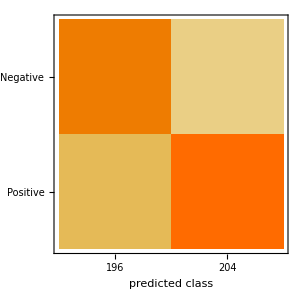
{0.7425,-Graphics-,<|Negative→0.795875,Positive→0.760331|>,<|Negative→0.740933,Positive→0.743961|>}

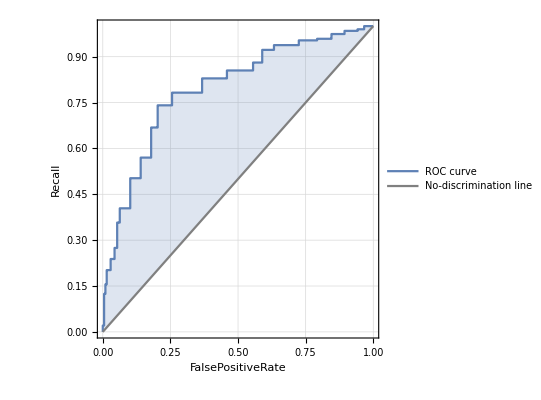
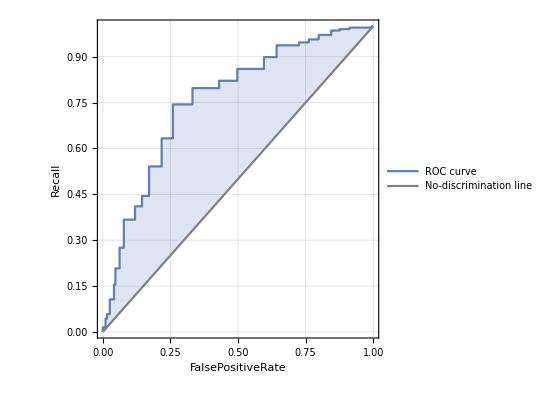
{<|Negative→-Graphics-,Positive→-Graphics-|>}

{}

0.72

{{1,0.72}}

0.78

{{1,0.72},{101,0.78}}

0.73

{{1,0.72},{101,0.78},{201,0.73}}

0.74

{{1,0.72},{101,0.78},{201,0.73},{400,0.74}}

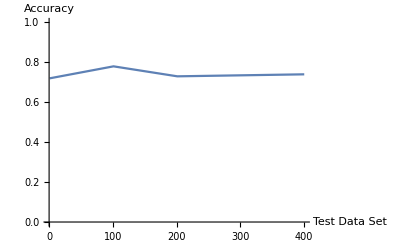

{0.7425}

{<|Negative→0.740933,Positive→0.743961|>}

{<|Negative→0.795875,Positive→0.760331|>}

{<|Negative→0.729592,Positive→0.754902|>}

```mathematica
z=Length[testSet[1]+testSet[2]]
randomForestCM/@{"Accuracy","ConfusionMatrixPlot","AreaUnderROCCurve","Recall"}
randomForestCM/@{"ROCCurve"}
graphPoints={}
randomForestCM1=ClassifierMeasurements[randomForestClassifier,testAccuracyTest1,"Accuracy"]
AppendTo[graphPoints,{lower1,randomForestCM1}]
randomForestCM1=ClassifierMeasurements[randomForestClassifier,testAccuracyTest2,"Accuracy"]
AppendTo[graphPoints,{lower2,randomForestCM1}]
randomForestCM1=ClassifierMeasurements[randomForestClassifier,testAccuracyTest3,"Accuracy"]
AppendTo[graphPoints,{lower3,randomForestCM1}]
randomForestCM1=ClassifierMeasurements[randomForestClassifier,testAccuracyTest4,"Accuracy"]
AppendTo[graphPoints,{totalTestSetLength,randomForestCM1}]
ListLinePlot[graphPoints,AxesLabel->{"Test Data Set","Accuracy"},PlotRange->{{0,totalTestSetLength},{0,1}}]
rmAccuracy=randomForestCM/@{"Accuracy"}
rmRecall=randomForestCM/@{"Recall"}
rmAOC=randomForestCM/@{"AreaUnderROCCurve"}
rmPrecision=randomForestCM/@{"Precision"}
```

### b) Neural Network

{}

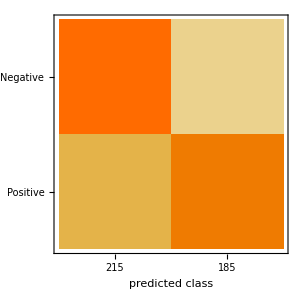
{0.735,-Graphics-,<|Negative→0.82471,Positive→0.82471|>,<|Negative→0.782383,Positive→0.690821|>}

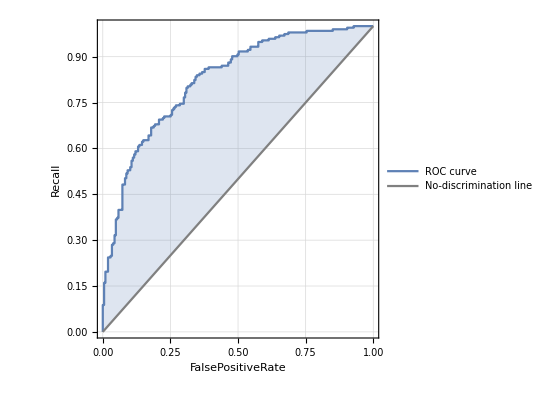
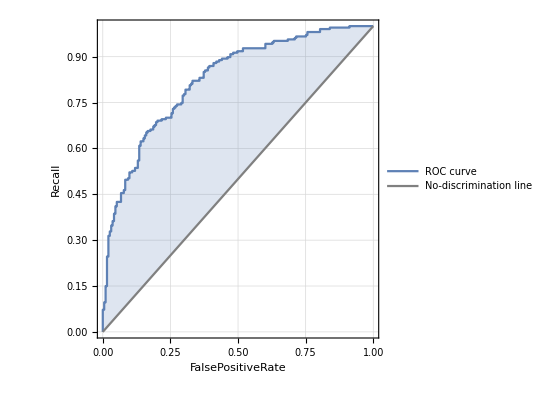
{<|Negative→-Graphics-,Positive→-Graphics-|>}

0.73

{{1,0.73}}

0.72

{{1,0.73},{101,0.72}}

0.8

{{1,0.73},{101,0.72},{201,0.8}}

0.69

{{1,0.73},{101,0.72},{201,0.8},{400,0.69}}

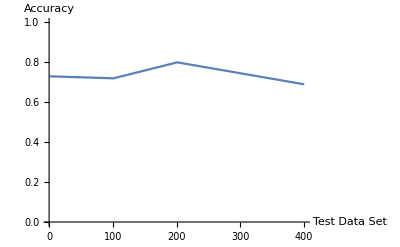

{0.735}

{<|Negative→0.782383,Positive→0.690821|>}

{<|Negative→0.82471,Positive→0.82471|>}

{<|Negative→0.702326,Positive→0.772973|>}

```mathematica
graphPointsNP={}
neuralNetworkCM/@{"Accuracy","ConfusionMatrixPlot","AreaUnderROCCurve","Recall"}
neuralNetworkCM/@{"ROCCurve"} 
nMCM1=ClassifierMeasurements[neuralNetworkClassifier,testAccuracyTest1,"Accuracy"]
AppendTo[graphPointsNP,{lower1,nMCM1}]
nMCM1=ClassifierMeasurements[neuralNetworkClassifier,testAccuracyTest2,"Accuracy"]
AppendTo[graphPointsNP,{lower2,nMCM1}]
nMCM1=ClassifierMeasurements[neuralNetworkClassifier,testAccuracyTest3,"Accuracy"]
AppendTo[graphPointsNP,{lower3,nMCM1}]
nMCM1=ClassifierMeasurements[neuralNetworkClassifier,testAccuracyTest4,"Accuracy"]
AppendTo[graphPointsNP,{totalTestSetLength,nMCM1}]
ListLinePlot[graphPointsNP,AxesLabel->{"Test Data Set","Accuracy"},PlotRange->{{0,totalTestSetLength},{0,1}}]
nMAccuracy=neuralNetworkCM/@{"Accuracy"}
nMRecall=neuralNetworkCM/@{"Recall"}
nMAOC=neuralNetworkCM/@{"AreaUnderROCCurve"}
nMPrecision=neuralNetworkCM/@{"Precision"}
```

### c) Support Vector Machine

{}

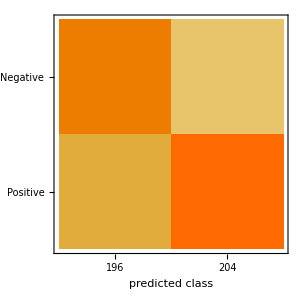
{0.6625,-Graphics-,<|Negative→0.715201,Positive→0.715201|>,<|Negative→0.658031,Positive→0.666667|>}

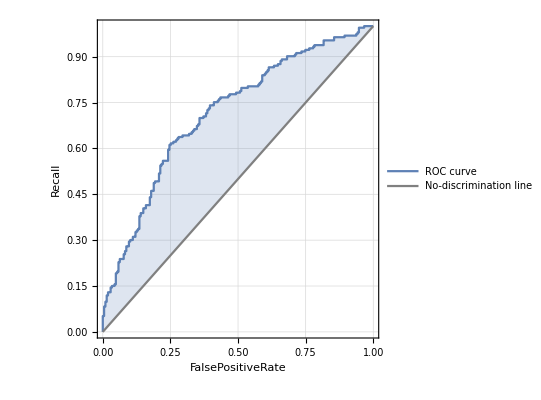
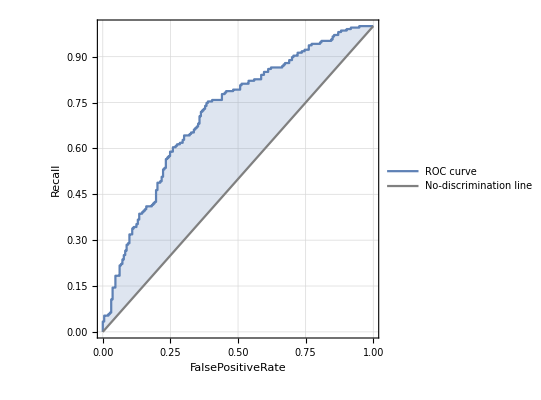
{<|Negative→-Graphics-,Positive→-Graphics-|>}

0.66

{{1,0.66}}

0.59

{{1,0.66},{101,0.59}}

0.69

{{1,0.66},{101,0.59},{201,0.69}}

0.71

{{1,0.66},{101,0.59},{201,0.69},{400,0.71}}

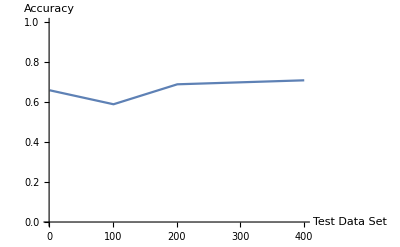

{0.6625}

{<|Negative→0.658031,Positive→0.666667|>}

{<|Negative→0.715201,Positive→0.715201|>}

{<|Negative→0.647959,Positive→0.676471|>}

```mathematica
graphPointsSVM={}
supportVectorMachineCM/@{"Accuracy","ConfusionMatrixPlot","AreaUnderROCCurve","Recall"}
supportVectorMachineCM/@{"ROCCurve"}
svmCM1=ClassifierMeasurements[supportVectorMachineClassifier,testAccuracyTest1,"Accuracy"]
AppendTo[graphPointsSVM,{lower1,svmCM1}]
svmCM1=ClassifierMeasurements[supportVectorMachineClassifier,testAccuracyTest2,"Accuracy"]
AppendTo[graphPointsSVM,{lower2,svmCM1}]
svmCM1=ClassifierMeasurements[supportVectorMachineClassifier,testAccuracyTest3,"Accuracy"]
AppendTo[graphPointsSVM,{lower3,svmCM1}]
svmCM1=ClassifierMeasurements[supportVectorMachineClassifier,testAccuracyTest4,"Accuracy"]
AppendTo[graphPointsSVM,{totalTestSetLength,svmCM1}]
ListLinePlot[graphPointsSVM,AxesLabel->{"Test Data Set","Accuracy"},PlotRange->{{0,totalTestSetLength},{0,1}}]
svmAccuracy=supportVectorMachineCM/@{"Accuracy"}
svmRecall=supportVectorMachineCM/@{"Recall"}
svmAOC=supportVectorMachineCM/@{"AreaUnderROCCurve"}
svmPrecision=supportVectorMachineCM/@{"Precision"}
```

### d) Markov

{}

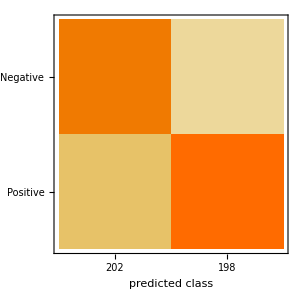
{0.8175,-Graphics-,<|Negative→0.894621,Positive→0.894621|>,<|Negative→0.834197,Positive→0.801932|>}

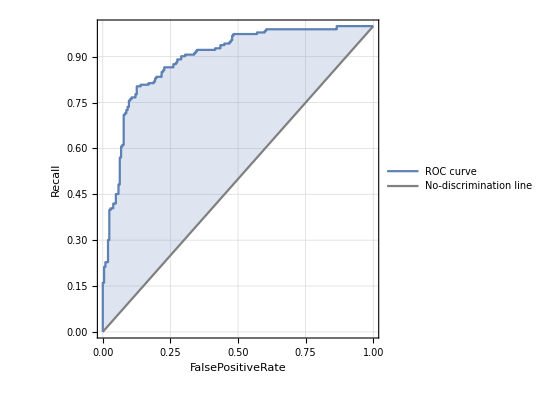
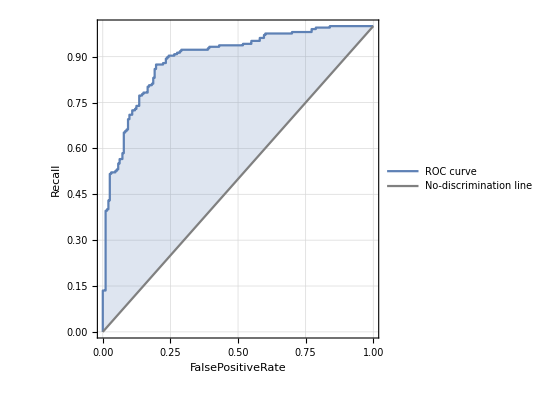
{<|Negative→-Graphics-,Positive→-Graphics-|>}

0.86

{{1,0.86}}

0.83

{{1,0.86},{101,0.83}}

0.76

{{1,0.86},{101,0.83},{201,0.76}}

0.82

{{1,0.86},{101,0.83},{201,0.76},{400,0.82}}

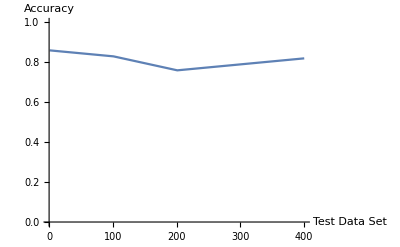

{0.8175}

{<|Negative→0.834197,Positive→0.801932|>}

{<|Negative→0.894621,Positive→0.894621|>}

{<|Negative→0.79703,Positive→0.838384|>}

```mathematica
graphPointsMarkov={}
markovCM/@{"Accuracy","ConfusionMatrixPlot","AreaUnderROCCurve","Recall"}
markovCM/@{"ROCCurve"} 
markovCM1=ClassifierMeasurements[ markovClassfier,testAccuracyTest1,"Accuracy"]
AppendTo[graphPointsMarkov,{lower1,markovCM1}]
markovCM1=ClassifierMeasurements[ markovClassfier,testAccuracyTest2,"Accuracy"]
AppendTo[graphPointsMarkov,{lower2,markovCM1}]
markovCM1=ClassifierMeasurements[ markovClassfier,testAccuracyTest3,"Accuracy"]
AppendTo[graphPointsMarkov,{lower3,markovCM1}]
markovCM1=ClassifierMeasurements[ markovClassfier,testAccuracyTest4,"Accuracy"]
AppendTo[graphPointsMarkov,{totalTestSetLength,markovCM1}]
ListLinePlot[graphPointsMarkov,AxesLabel->{"Test Data Set","Accuracy"},PlotRange->{{0,totalTestSetLength},{0,1}}]
markovAccuracy=markovCM/@{"Accuracy"}
markovRecall=markovCM/@{"Recall"}
markovAOC=markovCM/@{"AreaUnderROCCurve"}
markovPrecision=markovCM/@{"Precision"}
```

### e) Logistic Regression Forest

{}

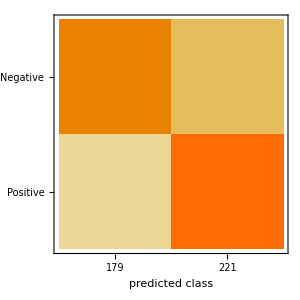
{0.775,-Graphics-,<|Negative→0.874221,Positive→0.874221|>,<|Negative→0.73057,Positive→0.816425|>}

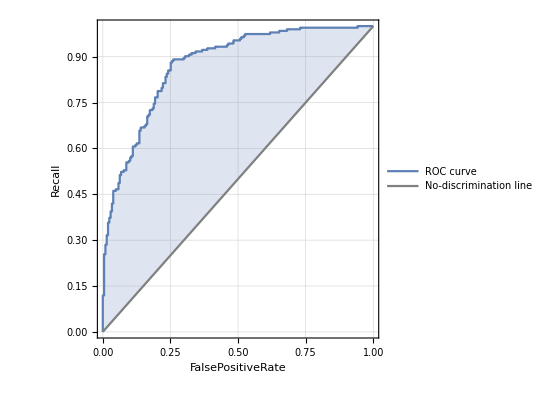
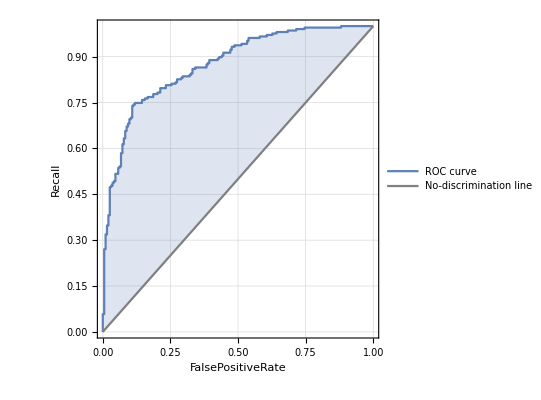
{<|Negative→-Graphics-,Positive→-Graphics-|>}

0.76

{{1,0.76}}

0.8

{{1,0.76},{101,0.8}}

0.77

{{1,0.76},{101,0.8},{201,0.77}}

0.77

{{1,0.76},{101,0.8},{201,0.77},{400,0.77}}

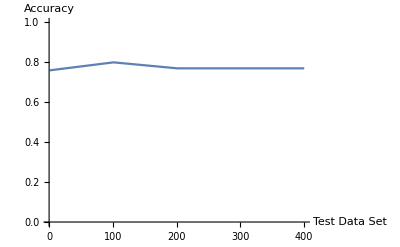

{0.775}

{<|Negative→0.73057,Positive→0.816425|>}

{<|Negative→0.874221,Positive→0.874221|>}

{<|Negative→0.787709,Positive→0.764706|>}

```mathematica
graphPointsLR={}
logisticClassifierCM/@{"Accuracy","ConfusionMatrixPlot","AreaUnderROCCurve","Recall"}
logisticClassifierCM/@{"ROCCurve"}
lrCM1=ClassifierMeasurements[logisticRegressionClassfier,testAccuracyTest1,"Accuracy"]
AppendTo[graphPointsLR,{lower1,lrCM1}]
lrCM1=ClassifierMeasurements[logisticRegressionClassfier,testAccuracyTest2,"Accuracy"]
AppendTo[graphPointsLR,{lower2,lrCM1}]
lrCM1=ClassifierMeasurements[logisticRegressionClassfier,testAccuracyTest3,"Accuracy"]
AppendTo[graphPointsLR,{lower3,lrCM1}]
lrCM1=ClassifierMeasurements[logisticRegressionClassfier,testAccuracyTest4,"Accuracy"]
AppendTo[graphPointsLR,{totalTestSetLength,lrCM1}]
ListLinePlot[graphPointsLR,AxesLabel->{"Test Data Set","Accuracy"},PlotRange->{{0,totalTestSetLength},{0,1}}]
lRAccuracy=logisticClassifierCM/@{"Accuracy"}
lRRecall=logisticClassifierCM/@{"Recall"}
lRAOC=logisticClassifierCM/@{"AreaUnderROCCurve"}
lRPrecision=logisticClassifierCM/@{"Precision"}
```

### Graphs- “Recall” , “Precision” and “Area under ROC Curve” - Comparing against each algorithm This section has all the code for running the graphs comparing the recall, precision and Area under ROC curve for each algorithm.

#### Algorithm vs Accuracy

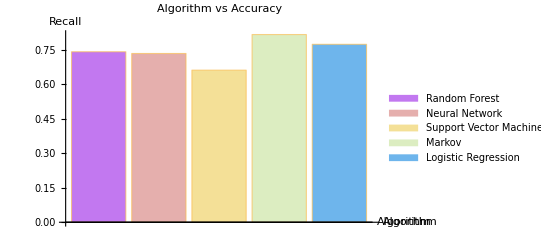

```mathematica
BarChart[{rmAccuracy[[1]],nMAccuracy[[1]],svmAccuracy[[1]],markovAccuracy[[1]],lRAccuracy[[1]]},ChartLegends->{"Random Forest","Neural Network","Support Vector Machine","Markov","Logistic Regression"},AxesLabel->{"Algorithm","Recall"},ChartStyle->"Pastel",PlotLabel->"Algorithm vs Accuracy"]
(* BarChart[{rmAccuracy[[1]],nMAccuracy[[1]],svmAccuracy[[1]]},ChartLegends->{"Random Forest","Neural Network","Support Vector Machine"},AxesLabel->{"Algorithm","Recall"},ChartStyle->"Pastel",PlotLabel->"Algorithm vs Recall"]*)
```

#### Algorithm vs Recall

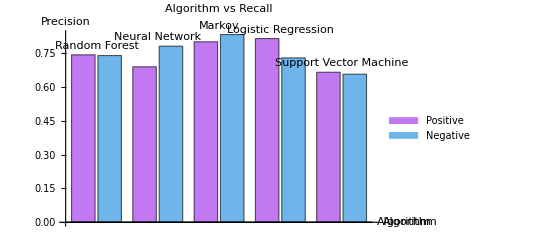

```mathematica
BarChart[{{rmRecall[[1]]["Positive"],rmRecall[[1]]["Negative"]},{nMRecall[[1]]["Positive"],nMRecall[[1]]["Negative"]},{markovRecall[[1]]["Positive"],markovRecall[[1]]["Negative"]},{lRRecall[[1]]["Positive"],lRRecall[[1]]["Negative"]},{svmRecall[[1]]["Positive"],svmRecall[[1]]["Negative"]}},ChartLegends->{{"Positive","Negative"}},AxesLabel->{"Algorithm","Precision"},ChartLabels-> {Placed[{"Random Forest","Neural Network","Markov","Logistic Regression","Support Vector Machine"},Above],None},ChartStyle->"Pastel",PlotLabel->"Algorithm vs Recall"]
(*BarChart[{{rmRecall[[1]]["Positive"],rmRecall[[1]]["Negative"]},{nMRecall[[1]]["Positive"],nMRecall[[1]]["Negative"]},{svmRecall[[1]]["Positive"],svmRecall[[1]]["Negative"]}},ChartLegends->{{"Positive","Negative"}},AxesLabel->{"Algorithm","Precision"},ChartLabels-> {Placed[{"Random Forest","Neural Network","Support Vector Machine"},Above],None},ChartStyle->"Pastel",PlotLabel->"Algorithm vs Precison"]*)
```

#### Algorithm vs Precision

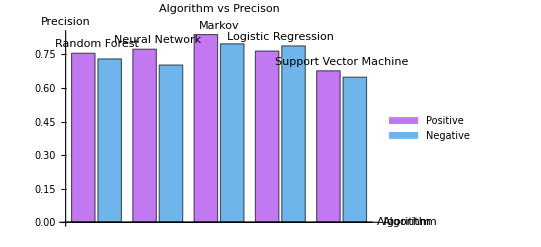

```mathematica
BarChart[{{rmPrecision[[1]]["Positive"],rmPrecision[[1]]["Negative"]},{nMPrecision[[1]]["Positive"],nMPrecision[[1]]["Negative"]},{markovPrecision[[1]]["Positive"],markovPrecision[[1]]["Negative"]},{lRPrecision[[1]]["Positive"],lRPrecision[[1]]["Negative"]},{svmPrecision[[1]]["Positive"],svmPrecision[[1]]["Negative"]}},ChartLegends->{{"Positive","Negative"}},AxesLabel->{"Algorithm","Precision"},ChartLabels-> {Placed[{"Random Forest","Neural Network","Markov","Logistic Regression","Support Vector Machine"},Above],None},ChartStyle->"Pastel",PlotLabel->"Algorithm vs Precison"]
(*BarChart[{{rmRecall[[1]]["Positive"],rmRecall[[1]]["Negative"]},{nMRecall[[1]]["Positive"],nMRecall[[1]]["Negative"]},{svmRecall[[1]]["Positive"],svmRecall[[1]]["Negative"]}},ChartLegends->{{"Positive","Negative"}},AxesLabel->{"Algorithm","Precision"},ChartLabels-> {Placed[{"Random Forest","Neural Network","Support Vector Machine"},Above],None},ChartStyle->"Pastel",PlotLabel->"Algorithm vs Precison"]*)
```

#### Algorithm vs Area under ROC curve

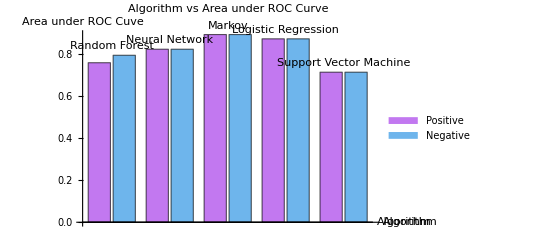

```mathematica
BarChart[{{rmAOC[[1]]["Positive"],rmAOC[[1]]["Negative"]},{nMAOC[[1]]["Positive"],nMAOC[[1]]["Negative"]},{markovAOC[[1]]["Positive"],markovAOC[[1]]["Negative"]},{lRAOC[[1]]["Positive"],lRAOC[[1]]["Negative"]},{svmAOC[[1]]["Positive"],svmAOC[[1]]["Negative"]}},ChartLegends->{{"Positive","Negative"}},AxesLabel->{"Algorithm","Area under ROC Cuve"},ChartLabels-> {Placed[{"Random Forest","Neural Network","Markov","Logistic Regression","Support Vector Machine"},Above],None},ChartStyle->"Pastel",PlotLabel->"Algorithm vs Area under ROC Curve"]

(* BarChart[{{rmAOC[[1]]["Positive"],rmAOC[[1]]["Negative"]},{nMAOC[[1]]["Positive"],nMAOC[[1]]["Negative"]},{svmAOC[[1]]["Positive"],svmAOC[[1]]["Negative"]}},ChartLegends->{{"Positive","Negative"}},AxesLabel->{"Algorithm","Area under ROC Cuve"},ChartLabels-> {Placed[{"Random Forest","Neural Network","Support Vector Machine"},Above],None},ChartStyle->"Pastel",PlotLabel->"Algorithm vs Area under ROC Curve"] *)
```

## Conclusions-

#### • Takes long time to train the data when compared to Random Forest, Neural Network and Markov • If proper training data set is not chosen, classification is hampered badly • Accuracy takes a toll for smaller training data. Accuracy is appreciable for large training data sets • Looking at the confusion matrix of the algorithm, we can draw inference that it usually classifies the data with good accuracy